## What time is it now?

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
makehand[m_,n_,o_,p_]:={Thick,Arrowheads[0.05],Arrow[{{m,n},{o,p}}]};
Column[{
Item[Text@Style["Happy Day\nI wish you an enjoyable seminar and a Successful Year",FontFamily->"Times New Roman",24,Bold,Darker [Blue],Italic],Frame->True,Alignment->Center],
hourhand:=makehand[0,0,0,0.6 radius];

minutehand:={Blue,makehand[0,0,0,0.75 radius]};

secondhand:={Red,makehand[0,-0.1,0,0.85 radius]};
Item[
Quiet[Graphics[{
  Inset[PolarPlot[x Sin[ x],{x,0,k Pi},PlotRange->All,Axes->False,PlotStyle->{RGBColor[0,0,1]},ImageSize->Tiny],{ radius Cos[π/3],radius Sin[ π/3]}],
Inset[PolarPlot[{x Cos[ x],-x Cos[x]},{x,0,k Pi},PlotRange->All,Axes->False,PlotStyle->{RGBColor[1,0,1]},ImageSize->Tiny],{radius Cos[π/6],radius Sin[ π/6]}],
Inset[PolarPlot[x Sin[11 x],{x,0,k Pi},PlotRange->All,Axes->False,PlotStyle->{RGBColor[0,0,1]},ImageSize->Tiny],{radius Cos[2π/3],radius Sin[2 π/3]}],
Inset[PolarPlot[{x Cos[6 x],-x Cos[6 x]},{x,0,k Pi},PlotRange->All,Axes->False,PlotStyle->{Hue[0.9]},ImageSize->Tiny],{radius Cos[π/2],radius Sin[ π/2]}],
Inset[PolarPlot[x Sin[9 x],{x,0,k Pi},PlotRange->All,Axes->False,PlotStyle->{RGBColor[1,0,1]},ImageSize->Tiny],{radius Cos[3π/3],radius Sin[3 π/3]}],
Inset[PolarPlot[x Sin[4 x],{x,0,k Pi},PlotRange->All,Axes->False,PlotStyle->{RGBColor[1,0,1]},ImageSize->Tiny],{radius Cos[7π/6],radius Sin[7 π/6]}],
Inset[PolarPlot[x Sin[7 x],{x,0,k Pi},PlotRange->All,Axes->False,PlotStyle->{RGBColor[0,0,1]},ImageSize->Tiny],{radius Cos[4π/3],radius Sin[4 π/3]}],Inset[PolarPlot[x Sin[5 x],{x,0,k Pi},PlotRange->All,Axes->False,PlotStyle->{RGBColor[0,0,1]},ImageSize->Tiny],{radius Cos[5π/3],radius Sin[5 π/3]}],
Inset[PolarPlot[{x Sin[2 x],-x Sin[2 x]},{x,0,k Pi},PlotRange->All,Axes->False,PlotStyle->{Hue[0.9]},ImageSize->Tiny],{radius Cos[11π/6],radius Sin[11 π/6]}],
Inset[PolarPlot[{x Sin[3 x],-x Sin[3 x]},{x,0,k Pi},PlotRange->All,Axes->False,PlotStyle->{Hue[0.9]},ImageSize->Tiny],{radius Cos[3π/2],radius Sin[3 π/2]}],
Inset[PolarPlot[{x Sin[5 x],-x Sin[5x]},{x,0,k Pi},PlotRange->All,Axes->False,PlotStyle->{Hue[0.9]},ImageSize->Tiny],{radius Cos[5π/6],radius Sin[5 π/6]}],
Inset[PolarPlot[x Sin[3 x],{x,0,k Pi},PlotRange->All,Axes->False,PlotStyle->{Hue[0.9]},ImageSize->Tiny],{radius Cos[6π/3],radius Sin[6 π/3]}],
Inset[
Dynamic[Style[Refresh[DateString[{"DayNameShort" ," ","Day"," ","MonthNameShort"," ", "Year","\n\n  ","Hour12Short",":","Minute"," ","AMPM"}],UpdateInterval->1],FontFamily->"Edwardian Script ITC",24,Bold,Blue(*RGBColor[1,0,1]*)]],{0,0.4 radius}],
{Purple,PointSize[0.03],Point[{0,0}]},(* Numbers *)
  Rotate[hourhand, Dynamic[Refresh[-30 Mod[AbsoluteTime[]/3600, 60] °, UpdateInterval -> 60]], {0, 0}],
  Rotate[minutehand, Dynamic[Refresh[-6 Mod[AbsoluteTime[]/60, 60] °, UpdateInterval -> 1]], {0, 0}],
  Rotate[secondhand, Dynamic[Refresh[-6 Mod[AbsoluteTime[], 60] °, UpdateInterval -> 1/20]], {0, 0}]
  },ImageSize->Large]],Frame->True]}],{{k,13,"loops"},5,20,1,Appearance->"Labeled"},
{{radius,5,"Radius"},.5,7,Appearance->"Labeled"},
ContinuousAction->False,
TrackedSymbols->{k,radius}]
```

# Area of Figures

## I. Area of Triangles:

## II. Area of figures

## Area Working

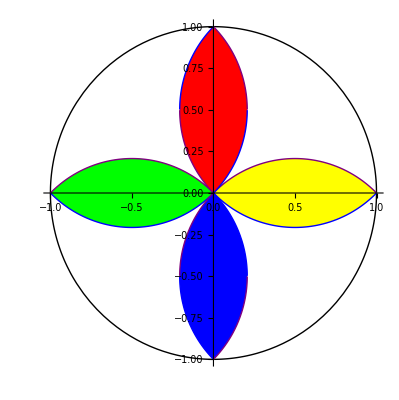

```mathematica
a=1;
f0[x_]=√(a^2 - x^2);
f0D[x_]=-√(a^2 - x^2);
f1[x_]=a/2-Sqrt[(a)^2/2-(x-a/2)^2];
f2[x_]=a/2+Sqrt[(a)^2/2-(x-a/2)^2];
f3[x_]=a/2+Sqrt[(a)^2/2-(x+a/2)^2];
f4[x_]=a/2-Sqrt[(a)^2/2-(x+a/2)^2];


p0=Plot[{f0[x],f0D[x]},{x,-1,1},PlotStyle->{{Thick,Black}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic];


g1[x_]=-a/2+Sqrt[(a)^2/2-(x-a/2)^2];
g2[x_]=-a/2-Sqrt[(a)^2/2-(x-a/2)^2];
g3[x_]=-a/2-Sqrt[(a)^2/2-(x+a/2)^2];
g4[x_]=-a/2+Sqrt[(a)^2/2-(x+a/2)^2];
pright=Plot[{g1[x],f1[x]},{x,0,1},PlotStyle->{{Thick,Purple},{Thick,Blue}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Yellow];

pUpL=Plot[{f1[x],f2[x]},{x,-0.5,0},PlotStyle->{{Thick,Purple},{Thick,Blue}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Red,PlotRange->All];
pUpR=Plot[{f3[x],f4[x]},{x,0,0.5},PlotStyle->{{Thick,Purple},{Thick,Blue}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Red,PlotRange->All];
pleft=Plot[{g4[x],f4[x]},{x,-1,0},PlotStyle->{{Thick,Purple},{Thick,Blue}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Green];
pDnR=Plot[{g3[x],g4[x]},{x,0,0.5},PlotStyle->{{Thick,Purple},{Thick,Blue}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Blue,PlotRange->All];
pDnL=Plot[{g1[x],g2[x]},{x,-0.5,0},PlotStyle->{{Thick,Purple},{Thick,Blue}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Blue,PlotRange->All];
p1=Plot[{g1[x],g2[x],g3[x],g4[x]},{x,-1,0.5},PlotStyle->{{Thick,Black},{Thick,Red},{Thick,Green},{Thick,Purple}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic];
Show[p0,pright,pleft,pUpR,pUpL,pDnR,pDnL,PlotRange->{-1,1}]
```

# Area of a triangle within a polygon

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
Column[{
Item[
Which[answer&&n==4,Column[{Style["\nArea of shaded triangle = k^2/24",16, Black],
Style["Area of Square = k^2\n",16, Black]}],answer&&n==6,
Column[{Style["\nArea of shaded triangle = (√3)/15",16, Black],Style["Area of Hexagon = (3 SqrtBox[3] SuperscriptBox[k, 2])/2\n",16, Black]}],
answer&&n==8,Column[{Style["\nArea of shaded triangle = (√2)/8",16, Black],Style["Area of Octagon = 2 (1 + √2) k^2\n",16, Black]}],True,Style["\nCalculate the area of the yellow triangle\ngiven that the length of the figure's side is k\n",16,Black]],Alignment->Left,Frame->True],
Item[
α8=ArcTan[(Cos[π/8] Sin[π/4] - Sin[13π/8])/Cos[13π/8]];
θ= ArcTan[(Tan[π/6]-Sin[5π/3])/Cos[5π/3]];
Graphics[{Circle[],{PointSize[0.02],Blue,Point[{0,0}]},
Which[n==4,{{Thick,Line[Table[{Cos[t],Sin[t]},{t,π/n,2π+π/n,2π/n}]]},
Line[{{Cos[(n-1)π/n],0},{Cos[π/n],0}}],Line[{{Cos[(n-1)π/n],0},{Cos[π/n],Sin[π/4]}}],Line[{{Cos[(n-1)π/n],Sin[(n-1)π/n]},{Cos[π/n],0}}],
Line[{{Cos[(n+1)π/n],Sin[(n+1)π/n]},{0,Sin[π/n]/(n-2)}}],Line[{{Cos[(2 n-1)π/n],Sin[(2 n-1)π/n]},{0,Sin[π/n]/2}}],{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,Sin[π/n]/(n-2)},{-Cos[π/n]/(n-1),0},{Cos[π/n]/(n-1),0}}]}
},n==6,
{{Thick,Line[Table[{Cos[2π k/n],Sin[2π k/n]},{k,0,n}]]},Point[{0,Tan[π/6]}],Line[{{Cos[0],0},{Cos[ π],0}}],{Black,Line[{{Cos[0],0},{Cos[4π/n],Sin[4π/n]}}],Line[{{Cos[π],0},{Cos[2π/n],Sin[2π/n]}}],Line[{{Cos[10π/( n)],Sin[10 π/n]},{0,Tan[π/n]}}],Line[{{Cos[8 π/n],Sin[8 π/n]},{0,Tan[π/n]}}]},{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,Tan[π/n]},{Tan[π/n]/Tan[θ],0},{-Tan[π/n]/Tan[θ],0}}]
}

},
n==8,
{{Thick,Line[Table[{Sin[t],Cos[t]},{t,π/8,2 π+π/8,2 π/8}]],Blue,Circle[],PointSize[0.02],Point[{0,0}],Point[{Cos[π/8],0}],Point[{Cos[7π/8],0}],Line[{{Cos[7π/8],0},{Cos[π/8],0}}]},{Black,Line[{{Cos[7π/8],0},{Cos[3π/8],Sin[3π/8]}}],Line[{{Cos[π/8],0},{Cos[5π/8],Sin[5π/8]}}],Line[{{Cos[11π/8],Sin[11π/8]},{0,Cos[π/8]Sin[π/4]}}],Line[{{Cos[13π/8],Sin[13π/8]},{0,Cos[π/8]Sin[π/4]}}]},{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,Cos[π/8]Sin[π/4]},{Cos[π/8]Sin[π/4]/Tan[α8],0},{-Cos[π/8]Sin[π/4]/Tan[α8],0}}]}
},

Mod[n,11]==0 ||Mod[n,9]==0 ||Mod[n,7]==0,{Thick,Line[Table[{Cos[2π k/n],Sin[2π k/n]},{k,n/4,(n+n/4)}]]},
Mod[n,10]==0,{Thick,Line[Table[{Cos[t],Sin[t]},{t,4π/n,2π+4π/n,2π/(n)}]]},
Mod[n,5]==0,{Thick,Line[Table[{Cos[t],Sin[t]},{t,π/(2n),2π+2π/(n),2π/(n)}]]},
True,{{Thick,Line[Table[{Cos[2π k/n],Sin[2π k/n]},{k,0,n}]]},Point[{0,Tan[π/6]}],Line[{{Cos[0],0},{Cos[ π],0}}]

}]},ImageSize->400],Alignment->{Center},Frame->True]
}],
Row[{
Control[{{n,6,"# Vertices"},4,8,2,Appearance->"Labeled",ImageSize->Tiny}],Spacer[30],Control[{{answer,False,"answer"},{False,True}}]}],TrackedSymbols:>{n,answer}]
```

## Ratio of Areas in a Square

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
Graphics[{{GrayLevel[0.7],Polygon[{{0,0},{10,0},{10,10},{0,10},{0,0}}]},
{Yellow,Polygon[{{0,0},{100/(10+z),(10 z)/(10+z)},{0,10}}]},{Yellow,Polygon[{{10,0},{10,z},{100/(10+z),(10 z)/(10+z)}}]},If[hint,{PointSize[0.02],Purple,Point[{10/(1+0.1 z),z/(1+0.1 z)}],Dashing[0.03],Arrow[{{10/(1+0.1 z),z/(1+0.1 z)},{10,z/(1+0.1 z)}}],Arrow[{{10/(1+0.1 z),z/(1+0.1 z)},{10/(1+0.1 z),0}}]
}],

{Thick,Line[{{0,0},{10,0}}]},
{Thick,Line[{{10,0},{10,10}}]},{Thick,Line[{{10,10},{0,10}}]},{Thick,Line[{{0,10},{0,0}}]},{Thick,Blue,Line[{{0,10},{10,0}}]},
{Thick,Red,Line[{{0,0},{10,z}}]},
Inset[Style[" I ",18,Bold],{9.7,0.9}],Inset[Style[" II",18,Bold],{7,0.5}],Inset[Style[" III ", 18,Bold],{2,4}],Inset[Style[" IV",18,Bold],{5,7}],
If[Answer,
Inset[Style[Row[{"Ratio of \n","Area I : Area II : Area III : Area IV  ="," \n ","   1   :   ",10 /z,"   :   ", (10/z)^2, "   :   ", (100 + 10 z -z^2)/z^2}],16,Bold,Blue],{5,12}],{Inset[Style[Row[{"Calculate the ratio of \n","Area I : Area II : Area III : Area IV "}],16,Bold],{5,12} ]}]}],

Grid[{{Control[{{z,2,"height"},1,9.,0.1,Appearance->"Labeled"}]},{Control[{{hint,False,"hint"},{False,True}}],Control[{{Answer,False,"Answer"},{False,True}}]}}],TrackedSymbols->{z,hint,Answer}]
```

# Creating multi - assignments from a math League problem

## Calculate the ratio of shaded Areas in a Rectangle

Based on AMC 12 A, February 2, 2016

```mathematica
Manipulate[
yellowArea=2 ( (2.5+4-z)(4)/2+2.5 (3-w)/2);
(* Half of the gray area consists of two triangles:
The first has a base of 1 + w and height = 2.5
The second has a base of 1+ z and height = 4.
Hence the gray area = (1+ w )2.5 + (1+z) 4 *)
grayArea=(1+w ) 2.5 + (1+z ) 4;
(*grayArea=40-yellowArea;*)
ratio=FullSimplify[yellowArea/grayArea];
Graphics[{{Yellow,Opacity[0.9],Polygon[{{0,0},{8,0},{8,5},{0,5},{0,0}}]},
{GrayLevel[0.7],Polygon[{{7-w,0},{8,0},{8,1+z},{4,2.5}}]},{GrayLevel[0.7],Polygon[{{0,4-z},{4,2.5},{1+w,5},{0,5}}]},
{Thick,Line[{{0,0},{8,0}}]},
{Thick,Line[{{8,0},{8,5}}]},{Thick,Line[{{8,5},{0,5}}]},{Thick,Line[{{0,5},{0,0}}]},{Thick,Blue,Line[{{0,4-z},{8,1+z}}]},
{Thick,Red,Line[{{1+w,5},{7-w,0}}]},
Line[{{0,0},{0,-1.6}}],Line[{{8,0},{8,-1.6}}],Line[{{8,0},{9.6,0}}],Line[{{8,1+z},{9,1+z}}],Line[{{8,5},{9.6,5}}],Line[{{7-w,0},{7-w,-1}}],
Arrowheads[{-0.03,0.03}],Arrow[{{0,-0.8},{7-w,-0.8}}],Arrow[{{7-w,-0.8},{8,-0.8}}],Arrow[{{0,-1.4},{8,-1.4}}],
Arrow[{{8.6,0},{8.6,1+z}}],Arrow[{{8.6,1+z},{8.6,5}}],Arrow[{{9.4,0},{9.4,5}}],
Inset[Style[" 8 cm",14,Purple],{4,-1.2}],Inset[Style[StandardForm[7-w],14,Purple],{(7-w)/2,-0.5}],
Inset[Style[StandardForm[1+w],14,Purple],{8-(1+w)/2,-0.5}],
Inset[Style[" 5 cm",14,Purple],{9.2,2.5}],Inset[Style[StandardForm[4-z],14,Purple],{8.5,1+(4+z)/2}],
Inset[Style[StandardForm[1+z],14,Purple],{8.5,(1+z)/2}],
If[hint,{Red,Arrowheads[0.03],Arrow[{{4,2.5},{4,0}}],Arrow[{{4,2.5},{8,2.5}}],Line[{{0,5},{8,0}}],
Inset[Style["4 cm",14],{6,2.7}],Inset[Style["2.5 cm",14],{4,1.25}]
}
],
If[Answer,
Inset[Style[Row[{"Gray area = ",grayArea,"  cm^2",Spacer[55],"Yellow area = ",yellowArea,"  cm^2\n Ratio of Gray area  : Yellow area = \n ",Spacer[53],"   1   :   ",ratio,"\n"}],12,Blue,Italic],{5,7}],{Inset[Style[Row[{"Calculate the ratio of \n","Gray area  :  Yellow area II "}],17,Italic,FontFamily->"Palatino"],{4,7} ]}]}],

Row[{Control[{{w,0,"length"},0,6.,0.1,Appearance->"Labeled",ImageSize->Tiny}],Control[
{{z,0,"height"},0,4,0.1,Appearance->"Labeled",ImageSize->Tiny}],Spacer[10],Control[
{{hint,False,"Hint"},{False,True}}],Spacer[5],Control[
{{Answer,False,"Answer"},{False,True}}]}],TrackedSymbols->{w,z,hint,Answer},SaveDefinitions->True]
```

# What is the largest equilateral triangle that can be inscribed in a unit square (A square with side length = 1 cm)

```mathematica
Manipulate[
Graphics[{EdgeForm[{Thick,Black}],FaceForm[Yellow],Rectangle[{0,0},{1,1}],

Text[Style["A",16,Bold,Black],{-0.05,0}],
Text[Style["B",16,Bold,Black],{1.05,0}],
Text[Style["C",16,Bold,Black],{1.05,1.05}],
Text[Style["D",16,Bold,Black],{0,1.05}],
If[solution,{
{EdgeForm[{Thick,Blue}],FaceForm[Red],Polygon[{{0,0},{1,Tan[15°]},{Sec[15°]Cos[75°],Sec[15°]Sin[75°]}}]},
Text[Style["E",16,Bold,Black],{1.05,Tan[15°]}],
Text[Style["F",16,Bold,Black],{Sec[15°]Cos[75°],0.05+Sec[15°]Sin[75°]}],
Text[Style["θ = 15°",16,Bold,Black],0.25{Cos[15° /2]+0.3,Sin[15 °/2]}],
{Arrowheads[0.03],Thick,Black,Arrow[{{0.2,0},0.2{Cos[θ],Sin[15°]}}]},

Text[Style["45°",16,Bold,Black],{0.94,0.15+Tan[15° ]}],

{Thick,Black,Circle[{1,Tan[15°]},0.12,{π/2,135°}]},

Text[Style["75°",16,Bold,Black],{0.93,Tan[15° ]-0.12}],
{Thick,Black,Circle[{1,Tan[15°]},0.1,{195°,270°}]},

Text[Style["45°",16,Bold,Black],{Sec[15°]Cos[75°]+0.13,Sec[15°]Sin[75°]-0.05}],
{Thick,Black,Circle[{Sec[15°]Cos[75°],Sec[15°]Sin[75°]},0.08,{7π/4,2 π}]},

{Thick,Black,Circle[{Sec[15°]Cos[75°],Sec[15°]Sin[75°]},0.08,{π,17π/12}]},
Text[Style["75°",16,Bold,Black],{Sec[15°]Cos[75°]-0.12,Sec[15°]Sin[75°]-0.06}],
Text[Style[Row[{
"The length of the side of \nthe equilateral triangle = ",Simplify[Sec[15°]]," cm\nmaximum area of equilateral triangle = ", FullSimplify[(√3)/4 Sec[15°]^2],"  cm^2\n"}],14,Purple],{0.5,1.2}]
},

{Text[Style["Calculate the side length and the area of the largest \nequilateral triangle that can be inscribed in a unit square",13,Italic,Black],{0.5,1.2}],
Inset[Style[Row[{"θ = ",θ}],14,Bold,Blue],0.25{Cos[θ /2]+0.3,Sin[θ /2]}],
{EdgeForm[{Thick,Blue}],FaceForm[Red],Polygon[{{0,0},{1,Tan[θ]},{Sec[θ]Cos[π/3+θ],Sec[θ]Sin[θ+π/3]}}]},
{Arrowheads[0.03],Thick,Red,Arrow[{{0.2,0},0.2{Cos[θ],Sin[θ]}}]},

Text[Style["E",16,Bold,Black],{1.05,Tan[θ]}],

Text[Style["F",16,Bold,Black],{Sec[θ]Cos[θ+π/3],0.05+Sec[θ]Sin[θ+π/3]}]
}]
}],

{{θ,11°,"inclination angle"},20°,0° ,1°,Appearance->"Labeled"},{{solution,False,"solution"},{False,True}}
,TrackedSymbols:>{θ,solution},ContentSize->390]
```

# Rotating a rectangle about a center of a square.

## Calculate the common area between a square and a rectangle whose vertex is at the center of the square.

```mathematica
ClearAll["Global`*"];
```

```mathematica
DynamicModule[{θ,hint,answer},Manipulate[
If[answer,θ=0,θ];
Column[{
Item[
Which[answer,Style["\nCommon area = 1/4 of area of square = 1 in^2\n",16,Purple],hint,Style["\n rotate the rectangle until its sides coinside with the square's diagonals ( θ = 0 )\n",14, Blue],True,Style["Calculate the common area bet. the square and \nthe rectangle if the square's side = 2 and the rctangle has length 3√2 and width 1.5√2\n",14,Black]
],Frame->True,Alignment->Left],
Item[

Graphics[{
{EdgeForm[{Thick,Black}],FaceForm[White],Rectangle[{-1,-1},{1,1}]},Which[θ<0.,{EdgeForm[{Thick,Black}],FaceForm[{Red,Opacity[0.9]}],Polygon[{{0,0},{1,Tan[π/4+θ]},{1,-1},{Tan[π/4+θ],-1}}]},θ>0,{EdgeForm[{Thick,Black}],FaceForm[{Red,Opacity[0.9]}],Polygon[{{0,0},{1,Tan[π/4-θ]},{1,1},{Tan[π/4-θ],1}}]}],

If[answer,{{EdgeForm[{Thick,Blue}],FaceForm[{Yellow,Opacity[0.5]}],Polygon[{{0,0},{1.5,1.5},{4.5,-1.5},{3,-3}}]},{EdgeForm[{Thick,Blue}],FaceForm[{Red,Opacity[0.8]}],Polygon[{{0,0},{1,1},{1,-1}}]}
},Rotate[{EdgeForm[{Thick,Blue}],FaceForm[{Yellow,Opacity[0.5]}],Polygon[{{0,0},{1.5,1.5},{4.5,-1.5},{3,-3}}]},θ,{0,0}]
],
If[hint,
Which[θ<0.,{EdgeForm[{Thick,Blue}],FaceForm[{Red,Opacity[0.8]}],Polygon[{{0,0},{1,1},{1.,Tan[π/4+θ]}}],Polygon[{{0,0},{1,-1},{Tan[π/4+θ],-1}}]},θ==0.,{EdgeForm[{Thick,Blue}],FaceForm[{Red,Opacity[0.8]}],Polygon[{{0,0},{1,1},{1,-1}}]},θ>0.,
{EdgeForm[{Thick,Blue}],FaceForm[{Red,Opacity[0.8]}],Polygon[{{0,0},{1,1},{Tan[π/4-θ],1}}],Polygon[{{0,0},{1,-1},{1,-Tan[π/4-θ]}}]}
]
]},AxesOrigin->{0,0},Axes->True,ImageSize->Medium,PlotRange->{{-1.5,5},{-4.5,2.7}}]
,Frame->True,Alignment->{Center}]
}],
Row[{
Control[{{θ,-π/10.,"rot.Angle"},-π/4.,π/4.,Appearance->"Labeled",ImageSize->Tiny",Enabled→hint"}],
Spacer[30],Control[{{hint,False,"hint"},{False,True}}],Spacer[30],Control[
{{answer,False,"answer"},{False,True}}]}],TrackedSymbols:>{θ,hint,answer}]]
```

## A Square within a Square

```mathematica
ClearAll["Global`*"];
```

```mathematica
Initialization:>{v[b_]={
{100 b/(100+b^2),1000/(100 +b^2)},
{10 b^2/(100+b^2),100 b/(100 +b^2)},
{(1000+10 b^2-100 b)/(100+b^2),b - b (1000+10 b^2-100 b)/(1000+10 b^2) },
{(1000)/(100+b^2),(1000-100 b+10 b^2)/(100 +b^2)}
};
area=(100-10 b)^2/(100+b^2);};
(*p[b_]={{0,0},{b,10},{10,10},{10-b,0}};};*)
```

```mathematica
Manipulate[
area=(100-10 b)^2/(100+b^2);
Column[{
Item[Which[answer,Style[Row[{"\nThe area of shaded square = ",area, " sq. units\n"}],16,Black],soln,Style[Row[{"\narea of blue parallelogram   \n",
" = base * height = (10 - b ) * 10  = ",( 10 - b ) 10,"  = hyp. * height = ",Style[TraditionalForm[√(10^2 + b^2) ],12], " h \n"}], 16],hint,Style["\nCalculate the area of the blue parallelogram in two different ways\n",16,Blue],True,Style["\nCalculate the area of the inner square\n",16,Black]],Alignment->Left,Frame->True],
Item[
gr1=Graphics[{
Thick,Line[{{0,0},{10,0}}],
Line[{{0,0},{0,10}}],
Line[{{10,0},{10,10}}],
Line[{{0,10},{10,10}}],
Blue,Line[{{0,b},{10,0}}],
Line[{{0,10},{10,10-b}}],
Red, 
Line[{{0,0},{b,10}}],
Line[{{10,10},{10-b,0}}],
Text[Style[Row[{Style["b",Italic],Style[" = "],NumberForm[b ,{4,2}]}],14], {b/2, 10.95}],
Arrowheads[{-0.04,0.04}], Arrow[{{0, 10.5}, {b,10.5}}],
Arrowheads[{-0.04,0.04}], Arrow[{{-0.7, 0}, {-0.7,10.}}],
 Text[Style[Row[{Style["a",Italic],Style[" = 10 "] }],14], {-1.7, 5}],EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{
{100 b/(100+b^2),1000/(100 +b^2)},
{10 b^2/(100+b^2),100 b/(100 +b^2)},
{(1000+10 b^2-100 b)/(100+b^2),b - b (1000+10 b^2-100 b)/(1000+10 b^2) },
{(1000)/(100+b^2),(1000-100 b+10 b^2)/(100 +b^2)}
}]},ImageSize->{600,450},PlotRange->{{-3,12},{-3,12}}];

gr2=Graphics[{

{Hue[0.6],Polygon[{{0,0},{b,10},{10,10},{10-b,0}}]},
{RGBColor[0.9,0,0.2],Polygon[{{0,0},{b,10},{0,10}}]
},
{RGBColor[0.9,0,0.2],Polygon[{{10-b,0},{10,0},{10,10}}]
},Blue,Line[{{0,b},{10,0}}],Line[{{0,10},{10,10-b}}],
{Red, Text[Style[Row[{Style["b",Italic],Style[" = "],NumberForm[b ,{4,2}]}],14], {b/2, 10.95}]},
{Red,Arrowheads[{-0.05,0.05}], Arrow[{{0, 10.5}, {b,10.5}}]},
{Red,Arrowheads[{-0.05,0.05}], Arrow[{{-0.7, 0}, {-0.7,10.}}]},
{Red, Text[Style[Row[{Style["a",Italic],Style[" = 10 "] }],14], {-1.7, 5}]},

Arrowheads[{-0.09,0.09}],Thickness[0.01],Green,Arrow[{{0,0},{10-b,0}}],Arrowheads[0.09],Arrow[{{5-b/2,0},{5-b/2,10}}],Inset[Style["height = 10",18,Black],{5,5}]
},ImageSize->{300,400},PlotRange->{{-3,12},{-3,12}}];


gr3=Graphics[{

{Hue[0.6],Polygon[{{0,0},{b,10},{10,10},{10-b,0}}]},
{RGBColor[0.9,0,0.2],Polygon[{{0,0},{b,10},{0,10}}]
},
{RGBColor[0.9,0,0.2],Polygon[{{10-b,0},{10,0},{10,10}}]
},Blue,Line[{{0,b},{10,0}}],Line[{{0,10},{10,10-b}}],
{Red, Text[Style[Row[{Style["b",Italic],Style[" = "],NumberForm[b ,{4,2}]}],14], {b/2, 10.95}]},
{Red,Arrowheads[{-0.05,0.05}], Arrow[{{0, 10.5}, {b,10.5}}]},
{Red,Arrowheads[{-0.05,0.05}], Arrow[{{-0.7, 0}, {-0.7,10.}}]},
{Red, Text[Style[Row[{Style["a",Italic],Style[" = 10 "] }],14], {-1.7, 5}]},Thickness[0.01],

Arrowheads[{-0.09,0.09}],Green,Arrow[{{10-b,0},{10,10}}],Arrowheads[0.09],Arrow[{{10-b/2,5},{((20 b+100-b^2)/(200+2 b^2))b,((20 b+100-b^2)/(200+2 b^2))10}}],
Inset[Style["height = h",18,Black],{5,5}]
},ImageSize->{300,400},PlotRange->{{-3,12},{-3,12}}];Which[hint,Row[{Show[gr2],Show[gr3]}],soln,Row[{Show[gr2],Show[gr3]}],True,Show[gr1]],Alignment->{Center},Frame->True]

}],

Row[{Control[{{b,3,"b = distance from Side"},2,8.,Appearance->"Labeled"}],Control[
{{hint,False,"hint"},{False,True}}],Spacer[25],Control[
{{soln,False,"solution"},{False,True}}],Spacer[36],Control[
{{answer,False,"answer"},{False,True}}]}],TrackedSymbols:>{b,answer,hint,soln}]
```

# Another way of calculating the area of the inner square

## A Square within a Square

```mathematica
Module[{b},Manipulate[

Graphics[{
If[solution,
Switch[steps,1,{Inset[Style[Row[{"area of blue parallelogram =  \n",
"area of 10×10 square - area of two red triangles = \n",100," - ", 10," ",Style["b",Italic] , " = ",100-10b}], 20],{5,17}],

{Hue[0.6],GraphicsComplex[p[b],Polygon[{1,2,3,4}]
]},
{RGBColor[0.9,0,0.2],Polygon[{{0,0},{b,10},{0,10}}]
},
{RGBColor[0.9,0,0.2],Polygon[{{10-b,0},{10,0},{10,10}}]
}},
2,{
Inset[Style[Row[{"area of blue rectangle = ", √(100+b^2) ," ",Style["x",Italic]," = ",100- 10 b }], 20],{5,17}],

{Hue[0.6],GraphicsComplex[t[b],Polygon[{1,2,3,4}]
]},

{RGBColor[0.9,0,0.2],Polygon[{{0,0},{b,10},{0,10}}]
},
{RGBColor[0.9,0,0.2],Polygon[{{10-b,0},{10,0},{10,10}}]
}},

3,{
Inset[Style[Row[{"area of the blue square = ",Style["x",Italic]^2 ," = ",
areaSqr}],20],{5,17}]

}],
{
If[answer,Inset[Style[Row[{"The area of shaded square = ",area}],20],{5,17}],
Inset[Style[" Calculate the area of the shaded square.",20],{5,17}]]
}],

{Thick,Line[{{0,0},{10,0}}]},
{Thick,Line[{{0,0},{0,10}}]},
{Thick,Line[{{10,0},{10,10}}]},
{Thick,Line[{{0,10},{10,10}}]},
(*{Red, Text[Style["b", 14, Italic], {b/2, 10.95}]},*)
{Red, Text[Style[Row[{Style["b",Italic],Style[" = "],NumberForm[b ,{4,2}]}],14], {b/2, 10.95}]},
{Red,Arrowheads[{-0.02,0.02}], Arrow[{{0, 10.5}, {b,10.5}}]},
{Red,Arrowheads[{-0.02,0.02}], Arrow[{{-0.7, 0}, {-0.7,10.}}]},
{Red, Text[Style[Row[{Style["a",Italic],Style[" = 10 "] }],14], {-1.7, 5}]},
(*{Red,Arrowheads[.02], Arrow[{{.9*b/2, 10.5}, {0,10.5}}]},
{Red,Arrowheads[.02], Arrow[{{1.1*b/2, 10.5}, {b,10.5}}]},*)
{Red,Line[{{0,0},{b,10}}]},
{Red,Line[{{10,10},{10-b,0}}]},
{Blue,Line[{{0,b},{10,0}}]},
{Blue,Line[{{0,10},{10,10-b}}]},
{Hue[0.6],GraphicsComplex[v[b],Polygon[{1,2,3,4}]
]}
},ImageSize->{450,450},PlotRange->{{-7,17},{-3,19}}],
{{b,10(2.-√3),"b = distance from vertex"},0.7,9.3,0.01,Appearance->"Labeled"},
{{answer,False,"answer"},{False,True},Enabled->Not@solution},
{{solution,False},{False,True}},
{{steps,1,"steps"},{1,2,3},ControlType->RadioButton,Enabled->solution},
TrackedSymbols->{b,answer,solution,steps},SaveDefinitions->True,
AutorunSequencing->{1,2,3},
Initialization:>{
p[b_]:={{0,0},{b,10},{10,10},{10-b,0}};
t[b_]:={ 
{(1000-100 b+10 b^2)/(100+b^2),(10 b^2)/(100 +b^2)},
{(1000+10 b^2+b^3)/(100+b^2),(1000+20 b^2)/(100+ b^2) },{(10 b^2+100 b+b^3)/(100+b^2),(1000+10 b^2+100 b)/(100+ b^2) },{10 b^2/(100+b^2),100 b/(100 +b^2)}
 };
v[b_]:={
{100 b/(100+b^2),1000/(100 +b^2)},
{10 b^2/(100+b^2),100 b/(100 +b^2)},
{(1000+10 b^2-100 b)/(100+b^2),b - b (1000+10 b^2-100 b)/(1000+10 b^2) },
{(1000)/(100+b^2),(1000-100 b+10 b^2)/(100 +b^2)}
 };areaSqr:=(100-10 b)^2/(100+b^2)}]]
```

# Third way

## A Square within a Square

```mathematica
ClearAll["Global`*"];
```

```mathematica
Module[{b},Manipulate[

gr1=Graphics[{{Thick,Line[{{0,0},{10,0}}]},
{Thick,Line[{{0,0},{0,10}}]},
{Thick,Line[{{10,0},{10,10}}]},
{Thick,Line[{{0,10},{10,10}}]},
{Blue,Line[{{0,b},{10,0}}],
Line[{{0,10},{10,10-b}}]},
{Red, 

{Line[{{0,0},{b,10}}],
Line[{{10,10},{10-b,0}}]},
Text[Style[Row[{Style["b",Italic],Style[" = "],NumberForm[b ,{4,2}]}],14], {b/2, 10.95}]},
{Red,Arrowheads[{-0.02,0.02}], Arrow[{{0, 10.5}, {b,10.5}}]},
{Red,Arrowheads[{-0.02,0.02}], Arrow[{{-0.7, 0}, {-0.7,10.}}]},
{Red, Text[Style[Row[{Style["a",Italic],Style[" = 10 "] }],14], {-1.7, 5}]},{EdgeForm[{Thick,Red}],FaceForm[Yellow],GraphicsComplex[v[b],Polygon[{1,2,3,4}]]},If[answer,Inset[Style[Row[{"The area of shaded square = ",area, " sq. units"}],18],{5,17}],

Inset[Style[" Calculate the area of the shaded square.",20],{5,17}]]},ImageSize->{450,450},PlotRange->{{-7,17},{-3,21}}];

gr2=Graphics[
{

Inset[Style["Calculate the area of the blue\nparallelogram in two different ways\n",16,Blue],{5,13}],
{EdgeForm[{Thick,Red}],FaceForm[Directive[Opacity[0.3],Blue]],GraphicsComplex[prlgram[b],Polygon[{1,2,3,4}]]},
{Thick,Line[{{0,0},{10,0}}]},
{Thick,Line[{{0,0},{0,10}}]},
{Thick,Line[{{10,0},{10,10}}]},
{Thick,Line[{{0,10},{10,10}}]},
Text[Style[Row[{Style["b",Italic],Style[" = "],NumberForm[b ,{4,2}]}],14], {b/2, 10.95}],
{Red,Arrowheads[{-0.02,0.02}], Arrow[{{0, 10.5}, {b,10.5}}]},
{Red,Arrowheads[{-0.02,0.02}], Arrow[{{-0.7, 0}, {-0.7,10.}}]},
{Red, Text[Style[Row[{Style["a",Italic],Style[" = 10 "] }],14], {-1.7, 5}]},
{Blue,Line[{{0,b},{10,0}}],
Line[{{0,10},{10,10-b}}]},


{Red, 
{Line[{{0,0},{b,10}}],
Line[{{10,10},{10-b,0}}]},
{RGBColor[0.9,0,0.2],Polygon[{{0,0},{b,10},{0,10}}]
},
{RGBColor[0.9,0,0.2],Polygon[{{10-b,0},{10,0},{10,10}}]}
},
{Arrowheads[0.05],{Thick,Green},Arrow[{{5,0},{5,10}}]},Inset[Style["height = 10",18,Black],{5,5}]},ImageSize->{400,200},PlotRange->{{-7,17},{-3,21}}];

gr3=Graphics[
{If[soln,Inset[Style[Row[{"area of blue parallelogram   \n",
" = base * height = ",(10 - b ), " * 10  = ",( 10 - b ) 10," \n = hyp. * height =  ",Style[TraditionalForm[√(10^2 + b^2) ],12], " h \n"}], 16],{5,17}]],If[soln&&answer,Inset[Style[Row[{"The area of shaded square \n= ",area, " sq. units"}],16,Blue],{5,13}]],{EdgeForm[{Thick,Red}],FaceForm[Directive[Opacity[0.3],Blue]],GraphicsComplex[prlgram[b],Polygon[{1,2,3,4}]]},
{Thick,Line[{{0,0},{10,0}}]},
{Thick,Line[{{0,0},{0,10}}]},
{Thick,Line[{{10,0},{10,10}}]},
{Thick,Line[{{0,10},{10,10}}]},
{Blue,Line[{{0,b},{10,0}}],
Line[{{0,10},{10,10-b}}]},
{Red, 
{Line[{{0,0},{b,10}}],
Line[{{10,10},{10-b,0}}]},
{RGBColor[0.9,0,0.2],Polygon[{{0,0},{b,10},{0,10}}]
},
{RGBColor[0.9,0,0.2],Polygon[{{10-b,0},{10,0},{10,10}}]}
},
{Arrowheads[0.09],{Thick,Red},Arrow[{{10-b,0},{(10 b^2 -  b^3)/(100 + b^2),((10 b^2 -  b^3)/(100 + b^2))(10/b)}}]},Inset[Style["height = h",18],{3,2}]},ImageSize->{350,250}];


Which[hint,
Row[{Show[gr2,ImageSize->{350,400},ContentSize->{500,200}],
Show[gr3,ImageSize->{300,300},ContentSize->{500,200}]}],True,Show[gr1]],

{{b,3,"b = distance from a side"},1,9.,Appearance->"Labeled"},
Row[{Control[
{{hint,False,"hint"},{False,True}}],Spacer[25],Control[
{{soln,False,"solution"},{False,True}}],Spacer[36],Control[
{{answer,False,"answer"},{False,True}}]}],TrackedSymbols:>{b,answer,hint,soln},
Initialization:>{v[b_]={
{100 b/(100+b^2),1000/(100 +b^2)},
{10 b^2/(100+b^2),100 b/(100 +b^2)},
{(1000+10 b^2-100 b)/(100+b^2),b - b (1000+10 b^2-100 b)/(1000+10 b^2) },
{(1000)/(100+b^2),(1000-100 b+10 b^2)/(100 +b^2)}
};
area=(100-10 b)^2/(100+b^2);
prlgram[b_]:={{0,0},{b,10},{10,10},{10-b,0}};}]]
```

## Nested Squares

Develop the sequence of areas of squares

```mathematica
Manipulate[Graphics[{EdgeForm[Directive[Blue]],RGBColor[0,0.6,1],Rectangle[],
{Cyan,Polygon[{{0,0.5},{0,1},{0.5,1}}]},

{Cyan,Polygon[{{0.5,0},{1,0},{1,0.5}}]},{Yellow,Rotate[Rectangle[{0.5-0.25 √2,0.5-0.25 √2},{0.5+0.25 √2,0.5+0.25 √2}],θ Degree,{0.5,0.5}]},
{Red,Rectangle[{0.25,0.25},{0.75,0.75}]},
{Green,Rotate[Rectangle[{0.5-0.25/√2,0.5-0.25/√2},{0.5+0.25/√2,0.5+0.25/√2}],θ Degree,{0.5,0.5}]},Blue,Rectangle[{0.375,0.375},{0.625,0.625}],{Pink,Rotate[Rectangle[{0.5-0.125/√2,0.5-0.125/√2},{0.5+0.125/√2,0.5+0.125/√2}],θ ,{0.5,0.5}]},Cyan,Rectangle[{0.5-0.125/2,0.5-0.125/2},{0.5+0.125/2,0.5+0.125/2}]},Axes->True,AxesOrigin->{0,0}],
{{θ,45,"Rotation"},-180,180,5,Appearance->"Labeled"},TrackedSymbols->{θ}]
```

## Sequence of Nested Squares part II

```mathematica
Module[{steps,answer},Manipulate[

g2=Graphics[

If[answer,Inset[Style[Row[{"Ratio among areas of squares = \n",
Row[Table[Row[{
TraditionalForm[2^-(2i)]," : ",TraditionalForm[2^-(2i+1)]," : "}],{i,0,n-1}]],TraditionalForm[2^-(2n)]," : ",TraditionalForm[2^-(2n+1)],"\n" }],16,Purple],{0,1.2}],Inset[Text@Style["Calculate the ratio among the\n areas of the squares\n",16,Italic,Purple],{0,1.2}]]];
Show[g1[i,n],g2,PlotRange->All]
,
Row[{Control[{{n,0,"Steps"},0,4,1,SetterBar}],Spacer[50],Control[
{{answer,False,"answer"},{False,True}}]}],TrackedSymbols->{n,answer},Initialization:>{ g1[i_,n_]:=Table[Graphics[{
{Thick,Line[{{-2^(-i),0},{0, 2^(-i)}}],Line[{{2^(-i),0},{0, -2^(-i)}}],Line[{{0,2^(-i)},{ 2^(-i),0}}],Line[{{-2^(-i),0},{0, -2^(-i)}}],
Blue,Line[{{-2^(-i),-2^(-i)},{-2^(-i),2^(-i)}}],
Line[{{-2^(-i),2^(-i)},{2^(-i),2^(-i)}}],
Line[{{2^(-i),2^(-i)},{2^(-i),-2^(-i)}}],
Line[{{2^(-i),-2^(-i)},{-2^(-i),-2^(-i)}}]}
},AspectRatio->Automatic,AxesOrigin->{0,0},Axes->False,PlotRange->{{-1,1},{-1,1}}],{i,0,n,1}];}]]
```

## Write the Equations that form the Squares

```mathematica
Manipulate[
Column[{
Item[

If[Answer,Text[Style[Row[{"The Equations of the slant lines that form the squares are: \n"," Left Side :                               Right Side :\n",
Column[Table[Row[{
" y = ", x+2^(-i),Spacer[10],", ","  y = ",-x-2^(-i)}],{i,0,m}]],Spacer[15],
Column[Table[Row[{
"  y = ", x-2^(-i),Spacer[10],", ","  y = ",-x+2^(-i)}],{i,0,m}]],"\n"}],12,Purple]],
Text@Style["\nWrite the Equations of the slant lines that form the squares \n",16,Italic,Purple]],Frame->True,ItemSize->{27,3},Alignment->Center],

Item[pt1:=Table[ParametricPlot[{{-2^(-i),t},{2^(-i),t}},{t,-2^(-i),2^(-i)},PlotStyle->{{Thick,Blue}},Axes->True],{i,0,m}];
ph2:=Table[Plot[{-2^(-i),2^(-i)},{x,-2^(-i),2^(-i)},PlotStyle->{{Thick,Blue}}],{i,0,m}];
psl:=Table[Plot[{x+2^(-i),-x-2^(-i)},{x,-2^(-i),0},PlotStyle->{{Thick,Purple}}],{i,0,m}];
psr:=Table[Plot[{x-2^(-i),-x+2^(-i)},{x,0,2^(-i)},PlotStyle->{{Thick,Purple}}],{i,0,m}];

Show[pt1,ph2,psl,psr,PlotRange->{{-1.3,1.3},{-1.2,1.2}},ImageSize->Medium],Frame->True,Alignment->Center,ItemSize->{33,3} ]}],

Row[{Control[{{m,0,"Steps"},0,3,1,SetterBar}],Spacer[60],Control[
{{Answer,False,"answer"},{False,True}}]}],TrackedSymbols->{m,Answer},SaveDefinitions->True]
```

# How many Rectangles are there?

```mathematica
Manipulate[
Show[
Graphics[
{Thickness[0.003],Table[{Line[{{0,i},{  m,i}}],Line[{{j,0},{j,n}}]},{i,0,n},{j,0,m}]}],
Graphics[Inset[Row[{Style["There are ",16, Bold, Blue],Style[m n (m+1)(n+1)/4, 16, Bold, Blue],Style[" Rectangles",16,Blue,Bold],
"\n",
		Style["Can You Find Them ?",24,Red,Bold,Italic]
}],{m/2,n+2}]]],
{{n,3,Style["n rows",14,Bold]},1,70,1,Appearance->"Labeled",ImageSize->Tiny},{{m,4,Style["m columns",14,Bold]},1,70,1,Appearance->"Labeled",ImageSize->Tiny},SaveDefinitions->True]
```

```mathematica
Equations of Angle Bisectors

Given two non parallel lines with the equations:
 y = Subscript[m, 1] x + Subscript[b, 1]  and  y = Subscript[m, 2] x + Subscript[b, 2], where Subscript[m, 1] and Subscript[m, 2] are the slopes of the two lines, then the angle bisectors are the locus of all points that are at equidistance from both intersecting lines.
```

ma=If[m1≠-m2,(m1m2-1+√((m1^2+1)(m2^2+1)))/(m1+m2),Style["0",18,Bold,Purple]];
map=If[m1≠-m2,(m1m2-1-√((m1^2+1)(m2^2+1)))/(m1+m2),Style["∞",24,Bold,Red]];
xint=If[m1-m2==0,Infinity,(b1-b2)/(m2-m1)];
yint= If[m1-m2==0,Infinity,(m2 b1 - m1 b2)/(m2-m1)];
y_a=If[m1≠m2,ma x+yint-ma xint];
y_ap=If[m1≠m2,map x+yint-map xint];

```mathematica
Module[{a,b,c,u,v},Manipulate[
a=Sqrt[(u-c)^2+v^2];b=Sqrt[u^2+v^2];
s=(a+b+c)/2;
radius=Sqrt[(s-a)(s-b)(s-c)/s];
(* Slope of the two angle bisectors are: *)
ma=(c-u-Sqrt[v^2+(u-c)^2])/v;
ma2=(-u+Sqrt[v^2+(u)^2])/v;
xint=ma c/(ma-ma2);yint=ma2 xint;
Graphics[{Thick,Line[{{0,0},{c,0}}],Line[{{c,0},{u,v}}],Line[{{u,v},{0,0}}],Text[Style["A",18,Bold],{-0.1,0}],Text[Style["B",18,Bold],{c+0.1,0}],Text[Style["C",18,Bold],{u,v+0.1}],Inset[Style[TraditionalForm[{0, 0}],14,Black],{0,-0.06}],Inset[Style[TraditionalForm[{c, 0}],14,Black],{c,-0.06}],
Inset[Style[TraditionalForm[{u, v}],14,Black],{u,v+0.04}],
Inset[Style[TraditionalForm[{NumberForm[xint,{4,3}],NumberForm[ yint,{4,3}]}],14,Black],{xint,yint+0.05}],
Inset[Style[Row[{"R = ",NumberForm[radius,{4,3}]}],16,Blue],{xint,yint-0.12}],
Thick,Blue,Circle[{xint,yint},radius],PointSize[0.02],Point[{xint,yint}],Dashing[0.02],Line[{{0,0},{xint,yint}}],Line[{{c,0},{xint,yint}}],Red,Line[{{u,v},{xint,yint}}]},Axes->False],Row[{Control[{{c,2,"c"},0.5,5,0.1,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{u,0.3,"u"},0.1,5,0.1,Appearance->"Labeled",ImageSize->Tiny}],Control[{{v,1.5,"v"},0.2,5,0.1,Appearance->"Labeled",ImageSize->Tiny}]}],TrackedSymbols:>{c,u,v}]]
```

## Incircle and circum circle of a triangle with side lengths a, b, c

The center of the in circle is the intersection point of the three angle bisectors.
  The radius of the incircle is Sqrt[ (s-a) (s-b)(s-c)/s].
  
  The center of the circumCircle is the intersection point of the three perpendicular  bisectors of the sides of the triangle.  
  The radius of the circumCircle = a /(2 Sin[theta]), where theta is the angle A between sides b, and c.

```mathematica
Manipulate[
If[u>a,u=a-0.3];
b=EuclideanDistance[{0,0},{u,h}];
c=EuclideanDistance[{a,0},{u,h}];
s=(a + b + c )/2;
rincircle=Sqrt[(s-a)(s-b)(s -c)/s];
(*m1 = slope of segment AB, m2 = Slope of segment AC *)
m2:=h/(u-a);m1:=h/u;theta=ArcTan[Abs[(m2 - m1 )/(1 + m1 m2 )]];R = a/(2 Sin[theta]);
(* Equation of line AC *)
y1:=m1 x;
(* Equation of line AB *)
y2:= m2 (x-a ) ;
(*Slope of angle bisector  = ma *)
(* ma = m1 m2 - 1 + Sqrt[m1^2 + 1)+(m2^2 + 1 )]/(m1 + m2)*)
ma:= (m1 m2 - 1 - Sqrt[(m1^2 + 1 ) (m2^2 + 1 )])/(m1 + m2 );
ma2=(-1+Sqrt[m2^2+1])/m2;
xincircle:=(h+a(ma2)-(ma)u)/(ma2 - ma);
yincircle := ma2(xincircle-a);

(* The center of the circumcircle is calculated via the intersection of the perpendicular bisectors of the sides *)

xcircum= (u/(2 m1 )- (u + a )/(2 m2))/(1/m1 - 1/m2);
ycircum= h/2-(xcircum-u/2)/m1;
p1=Plot[{ma (x-u) + h,ma2(x-a)},{x,0,1.}];

gr=Graphics[{Thick,Line[{{0,0},{a,0}}],Line[{{a,0},{u,h}}],Line[{{u,h},{0,0}}],(*Line[{{a,0},{xincircle,yincircle}}],*)

{Dashing[0.02],Blue,Line[{{u,h},{xincircle,yincircle}}],Line[{{a,0},{xincircle,yincircle}}],Line[{{0,0},{xincircle,yincircle}}]},
(* Center of circumcircle *)
{Dashing[0.02],Purple,Line[{{a/2,0},{xcircum,ycircum}}],Line[{{u/2,h/2},{xcircum,ycircum}}],Line[{{(u+a)/2,h/2},{xcircum,ycircum}}]},
Text[Style["C",18,Bold],{-0.1,0}],Text[Style["B",18,Bold],{a+0.1,0}],Text[Style["A",18,Bold],{u,h+0.15}],Inset[Style[TraditionalForm[{0, 0}],14,Black],{0,-0.06}],Inset[Style[TraditionalForm[{a, 0}],14,Black],{a,-0.06}],
Inset[Style[TraditionalForm[{u, h}],14,Black],{u,h+0.04}],
Blue,PointSize[0.03],Point[{xincircle,yincircle}],Thick,Circle[{xincircle,yincircle},rincircle],Purple,PointSize[0.03],Point[{xcircum,ycircum}],Circle[{xcircum,ycircum},R],
Inset[Style[TraditionalForm[{NumberForm[xincircle,{4,3}],NumberForm[ yincircle,{4,3}]}],14,Black],{xincircle,yincircle+0.1}],
Inset[Style[TraditionalForm[{NumberForm[xcircum,{4,2}],NumberForm[ ycircum,{4,2}]}],14,Purple],{xcircum+0.3,ycircum}],
Inset[Style[Row[{"rincircle = ",NumberForm[rincircle,{4,3}]}],16,Blue],{xincircle,yincircle-0.12}],Inset[Style[Row[{"b = ",NumberForm[b,{3,2}]}],14,Black],{u/2-0.2,h/2}],Inset[Style[Row[{"c = ",NumberForm[c,{3,2}]}],14,Black],{(a+u)/2+0.3,h/2}],Inset[Style[Row[{"a = ",a}],14,Black],{(a)/2,-0.1}]},Axes->False];

Show[gr],Row[{Control[{{a,2,"a"},0.5,5,0.1,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{u,0.4,"u"},0.01,5,0.1,Appearance->"Labeled",ImageSize->Tiny}],Control[{{h,1.5,"h"},0.2,5,0.1,Appearance->"Labeled",ImageSize->Tiny}]}],TrackedSymbols:>{u,a,h}]
```

## Angle bisectors in a triangle Find the equations of the angle bisectors and the coordinates of their point of intersection as well as inner circle.

```mathematica
ClearAll["Global`*"];
```

```mathematica
Module[{b,c,ratio,affd,bffe,cffg,coord,eqn},Manipulate[
dab=b[[1]];
dbc=EuclideanDistance[b,c];
dac=EuclideanDistance[{0,0},c];
dBD=EuclideanDistance[b,{xintD,yintD}];
dAF=EuclideanDistance[{0,0},{xintF,yintF}];
dBF=EuclideanDistance[{xintF,yintF},{b[[1]],0}];
dFD=EuclideanDistance[{xintF,yintF},{xintD,yintD}];
dFE=EuclideanDistance[{xintF,yintF},{xintE,yintE}];
dCF=EuclideanDistance[{xintF,yintF},c];
dFG=EuclideanDistance[{xintF,yintF},{xintG,0}];
ratioAFFD=FullSimplify[dAF/dFD];
ratioBFFE=FullSimplify[dBF/dFE];
ratioCFFG=FullSimplify[dCF/dFG];

slopbc=(c[[2]])/(c[[1]]-b[[1]]);
slopac=(c[[2]])/(c[[1]]);
(*Equation of AC *)
eqac[x_]:=slopac x ;
(*Equation of BC *)
eqbc[x_]:=FullSimplify[slopbc (x -b[[1]])];
slopanglbisectorA= FullSimplify[slopac/(1+√(slopac^2+1))];
alpha=ArcTan[slopanglbisectorA];
xintD=FullSimplify[(slopbc b[[1]])/(slopbc -slopanglbisectorA)];
yintD=FullSimplify[slopbc (xintD -b[[1]])];
(* Equation of anglebisector AD *)
eqad[x_]:=NumberForm[slopanglbisectorA,{5,3}] x;

(* Developing equation of Angle bisector BE from point B*)
slopanglbisectorB= FullSimplify[slopbc/(1+√(slopbc^2+1))];
(* Equation of angle bisector AE *)
eqnBE[x_]:=NumberForm[slopanglbisectorB,{5,3}](x-b[[1]]);
(*Find the coordinates of point E which is the intersection of angle bisector BE and AC *)
xintE=FullSimplify[(slopanglbisectorB b[[1]])/(slopanglbisectorB-slopac )];
yintE=FullSimplify[slopac xintE];

(*Developing the equation of the angle bisector CG *)
(* Tthe point of intersection of AC and BC is point C (given) *)
(* First get slope of CG Slope = (m1 m2 - 1 + √((m1^2 +1) (m2^2 + 1)))/(m1+m2)*)
slopanglbisectorC=FullSimplify[(slopac slopbc -1 - √((slopac^2+1)(slopbc^2+1)))/(slopac+slopbc)];
eqnCG[x_]:=NumberForm[slopanglbisectorC,{5,3}] (x-c[[1]])+NumberForm[c[[2]],{5,3}];
xintG=FullSimplify[(slopanglbisectorC (c[[1]])-c[[2]])/slopanglbisectorC];
(*Get the point of intersection of AD and BE *)
(* For two lines y1 = m1 x + b1 and y2 = m2 x + b2,xint = (b1 - b2)/ (m2 - m1) and yintersect = (m2 b1 - m1 b2 ) / ( m2 - m1 ) *)
xintF= FullSimplify[-slopanglbisectorB  b[[1]]/(slopanglbisectorA-slopanglbisectorB)];
yintF=FullSimplify[slopanglbisectorA xintF];
(* Plot the angle bisectors *)
pltLine1=Plot[Tooltip[slopanglbisectorA x],{ x,0,xintD},PlotStyle->Red];
pltLine2=Plot[Tooltip[slopanglbisectorB (x-b[[1]])],{ x,b[[1]],xintE},PlotStyle->Red];
pltLine3=Plot[Tooltip[slopanglbisectorC (x-c[[1]])+c[[2]]],{ x,c[[1]],xintG},PlotStyle->Red];
(* the radius of the inncircle = (s-a)(s-b)(s-c)/s *)
a1 = Sqrt[(c[[1]]-b[[1]])^2+c[[2]]^2];
b1=Sqrt[c[[1]]^2+c[[2]]^2];c1=b[[1]];s=(a1+b1+c1)/2;radius=Sqrt[(s-a1)(s-b1)(s-c1)/s];

Column[{
Item[Which[ratio==1,If[affd,Style[Row[{"\nRatio AF : FD = " ,ratioAFFD, " :  1 \n"}],14,Blue],Style[Row[{"\nCalculate the ratio AF : FD if AB = ",b[[1]]," , BC = ",dbc," AC = ",dac,"\nWrite the equations of the three angle bisectors.\n"}] ,14,Italic,Black]],
ratio==2,
If[bffe,Style[Row[{"\nRatio BF : FE = " ,TraditionalForm[ratioBFFE], "  \n"}],14,Blue],Style[Row[{"\nCalculate the ratio BF : FE if AB = ",b[[1]]," , BC = ",dbc," AC = ",dac,"\nWrite the equations of the three angle bisectors.\n"}] ,14,Italic,Black]],

ratio==3,
If[cffg,Style[Row[{"\nRatio CF : FG = " ,TraditionalForm[ratioCFFG], " \n"}],14,Blue],Style[Row[{"\nCalculate the ratio CF : FG if AB = ",b[[1]]," , BC = ",dbc," AC = ",dac,"\nWrite the equations of the three angle bisectors.\n"}] ,14,Italic,Black]]],Alignment->Left,Frame->True],
(*Construct any triangle given point A at origin and point B on x axis while point C at any place above the x-axis *)
Item[
grTriangle=Graphics[{{Thick,Line[{{0,0},{b[[1]],0}}],Line[{{b[[1]],0},{c[[1]],c[[2]]}}],Line[{{c[[1]],c[[2]]},{0,0}}]},
(*{EdgeForm[{Thick,Blue}],FaceForm[Yellow],Disk[{0,0},0.6,{0,alpha}]},*)PointSize[0.015],Black,Point[{0,0}],Blue,Point[{b[[1]],0}],Point[{c[[1]],c[[2]]}],Red,Point[{xintD,yintD}],
Purple,Point[{xintE,yintE}],Point[{xintF,yintF}],Green,Point[{xintG,0}],
Red,Arrow[{{0,0},{xintD,yintD}}],Arrow[{{b[[1]],0},{xintE,yintE}}],Arrow[{c,{xintG,0}}],
{Thick,Blue,Circle[{xintF,yintF},radius]},
Text[Style["A ",18,Black,Italic],{0,-0.3}],
Text[Style["B ",18,Black,Italic],{b[[1]],-0.3}],
Text[Style["C ",18,Black,Italic],{c[[1]],c[[2]]+0.3}],
Text[Style["E ",18,Black,Italic],{xintE-0.3,yintE}],
Text[Style["F ",18,Black,Italic],{xintF, yintF-0.3}],
Text[Style["D ",18,Black,Italic],{xintD+0.3,yintD}],
Text[Style["G ",18,Black,Italic],{xintG,-0.3}],
If[coord,{Text[Style[TraditionalForm[{0,0}],13,Purple],{-0.5,0}],Text[Style[StandardForm[{NumberForm[b[[1]],{5,3}],0}],13,Purple],{b[[1]],-0.5}],Text[Style[StandardForm[{NumberForm[c[[1]],{5,3}],NumberForm[c[[2]],{5,3}]}],13,Purple],{c[[1]],c[[2]]+0.7}],Text[Style[TraditionalForm[{NumberForm[xintF,{5,3}],NumberForm[yintF,{5,3}]}],13,Purple],{xintF,yintF+0.5}],Text[Style[StandardForm[{NumberForm[xintD,{5,3}],NumberForm[yintD,{5,3}]}],13,Purple],{xintD+1.3,yintD-0.4}],Text[Style[StandardForm[{NumberForm[xintE,{5,3}],NumberForm[yintE,{5,3}]}],13,Purple],{xintE-1.3,yintE-0.4}],Text[Style[TraditionalForm[{NumberForm[xintG,{5,3}],0}],13,Purple],{xintG,+0.5}]}],
Which[ratio==1&&eqn,Text[Style[Row[{"Equation of Angle bisector AD\n   y = ",TraditionalForm[eqad[x]],"\n"}],15,Purple],{0,7}],

ratio==2&&eqn,Text[Style[Row[{"Equation of Angle bisector BE\n   y = ",TraditionalForm[eqnBE[x]],"\n"}],15,Purple],{0,7}],
ratio==3&&eqn,Text[Style[Row[{"Equation of Angle bisector CG\n   y = ",TraditionalForm[eqnCG[x]],"\n"}],15,Purple],{0,7}]],
Text[Style[NumberForm[dab,{5,3}],16,Black],{dab/2,-0.6}],
Text[Style[NumberForm[dbc,{5,3}],16,Black],{(b[[1]]+c[[1]])/2+0.5,c[[2]]/2+0.5}],
Text[Style[NumberForm[dac,{5,3}],16,Black],{c[[1]]/2-0.5,c[[2]]/2+0.5}],
Which[ratio==1&&affd,{Text[Style[dAF,16,Red],{xintF/2,yintF/2+0.3}],
Text[Style[dFD,16,Red],{(xintF+xintD)/2,(yintF+yintD)/2+0.3}]},
ratio==2&&bffe,{Text[Style[dBF,16,Red],{(xintF+b[[1]])/2,yintF/2+0.3}],
Text[Style[dFE,16,Red],{(xintF+xintE)/2,(yintF+yintE)/2+0.3}]},
ratio==3&&cffg,{Text[Style[dCF,16,Red],{(c[[1]]+xintG)/2,(c[[2]]+yintF)/2+0.3}],
Text[Style[dFG,16,Red],{(xintF+xintG)/2,(yintF)/2+0.3}]}]

},Axes->False,AxesOrigin->{0,0},PlotRange->{{-2,9},{-2,9}},PlotRange->10,ImageSize->Large];
Show[grTriangle(*,pltLine1,pltLine2,pltLine3*)],Alignment->{Center},Frame->True]
}],
{{b,{6.,0},"Pt. B"},{1.,0},{9,0},Locator,Appearance->None},
{{c,{17/4.,7.√15./4},"Pt C"},{0.3,1},{Dynamic[b[[1]]]-2,9},Locator,
Appearance->None},
Row[{
Control[{{ratio,1,"Ratio"},1,3,1,ControlType->SetterBar}],Spacer[30],
Control[
{{affd,False,"AF :FD "},{False,True}}],Spacer[30],Control[
{{bffe,False,"BF :FE "},{False,True}}],Spacer[30],Control[
{{cffg,False,"CF :FG "},{False,True}}],Spacer[30],Control[{{coord,False,"Coordinates"},{False,True}}],Spacer[30],
Control[{{eqn,False,"Equation\nAngle bisector"},{False,True}}]
}],
TrackedSymbols:>{b,c,ratio,affd,bffe,cffg,coord,eqn},SaveDefinitions->True]]
```

## Area of a circular polygon in a circle with radius = 1 = (n/2) Sin ( 2π/n) For a regular Polygon, area = (n/4) s^2 Cot (π/n) , where s = side length of the polygon. s = 2 r Sin ( π/n)

```mathematica
Manipulate[
Graphics[{Thick,Circle[],{EdgeForm[{Thick,Red}],Yellow,Polygon[CirclePoints[n]]},Inset[Style[Row[{"Area Polygon = \n",FullSimplify[n Sin[2π/n]/2],"  Sq. units"}],14,Black],{0,0.1}]},ImageSize->{400,400}],{{n,3,"n"},3,51,1,Appearance->"Labeled"},TrackedSymbols:>n]
```

# What is the ratio of the areas of the inner and outer regular polygons in this figure?

```mathematica
ClearAll["Global`*"];
```

```mathematica
Module[{n,hint,answer},Manipulate[

ratio=Sin[2π/n]^2;
polygonName=Which[n==3,"triangle",n==4,"quadrilateral",n==5,"pentagon",n==6,"hexagon",n==7,"heptagon",n==8,"octagon",n==9,"nonagon",n==10,"decagon",n==11,"hendecagon",n==12,"dodecagon",n==13,"triskaidecagon",n==14,"tetrakaidecagon",n==15,"pentakaidecagon",n==16,"hexakaidecagon",n==17,"heptakaidecagon"];
Column[{
Item[Which[hint,Style["\nWhat is the ratio of the areas of the two triangles ABD and ABC?\nWhat is the ratio of the square of AB to the square of AC?\n",16,Black,Italic],answer,
Style[Row[{"\nRatio of area of inner ",polygonName, " to outer ",polygonName," \n",Spacer[30],"=  ",ratio,"         :       1\n"}],16,Purple,Italic],True,Style[Row[{"\nWhat is the ratio of the areas of the inner and outer regular ",polygonName,"?\n"}],16,Black,Italic]],Alignment->Left,Frame->True],
Item[                  Graphics[{EdgeForm[{Black,Thick}],FaceForm[Yellow],Polygon[Table[(Sec[π/n]){Sin[2π k/n],Cos[2π k/n]},{k,1,n}]],EdgeForm[{Blue,Thick}],FaceForm[Pink],Polygon[Table[{Cos[(2π k)/n+(π/2-π/n)],Sin[(2π k)/n+(π/2-π/n)]},{k,1,n}]],Black,Circle[],PointSize[0.02],Point[{0,0}],
If[hint||answer,{Black,Arrow[{{0,0},{Cos[-π/n+π/2],Sin[-π/n+π/2]}}],Arrow[{{0,0},(Sec[π/n]){Cos[π/2],Sin[π/2]}}],Text[Style["A",20,Bold],{0,-0.1}],Text[Style["B",18,Bold],{Cos[-π/n+π/2],Sin[-π/n+π/2]}+0.06],
Text[Style["C",20,Bold],{0,Sec[π/n]+0.06}],
Text[Style["D",20,Bold],{-0.06,Cos[π/( n)]}]}]
},ImageSize->Medium],Alignment->{Center},Frame->True]
}],
Row[{Control[{{n,3,"number of sides"},3,20,1,Appearance->"Labeled"}],Spacer[30],
Control[{{hint,False,"hint"},{False,True},Appearance->"Labeled"}],Spacer[30],Control[{{answer,False,"answer"},{False,True},Appearance->"Labeled"}]
}],TrackedSymbols:>{n,hint,answer}]]
```

## Calculate area inside a hexagon

```mathematica
Vertices[Hexagon]
(*Graphics[{PointSize[0.025],Purple,Point/@%},AspectRatio->1];*)
Manipulate[Graphics[{Thick,Purple,Line[{{1/2,(√3)/2},{-1/2,(√3)/2}}],Line[{{-1/2,(√3)/2},{-1,0}}],Line[{{-1,0},{-1/2,-(√3)/2}}],Line[{{-1/2,-(√3)/2},{1/2,-(√3)/2}}],Line[{{1/2,-(√3)/2},{1,0}}],Line[{{1/2,(√3)/2},{1,0}}],
{PointSize[0.025],Red,Point[{0,0}]},{EdgeForm[{Blue,Thick}],FaceForm[Pink],Disk[{1,0},0.5,{2π/3,4π/3}],
Disk[{1/2,(√3)/2},0.5,{π,5π/3}],
Disk[{-1/2,(√3)/2},0.5,{4π/3,6π/3}],
Disk[{-1,0},0.5,{5π/3,7π/3}],

Disk[{-1/2,-(√3)/2},0.5,{0,2π/3}],
Disk[{1/2,-(√3)/2},0.5,{π/3,3π/3}]
},
If[answer,Text[Style["area of the internal white region = 54 √3 - 18 π in^2\n",14, Blue],{0,1.1}],Text[Style["What is the area of the internal white region,\n if the side length of the hexagon = 6 in?\n",16,Black,Italic],{0,1.1}]
]

},Axes->False,AxesOrigin->{0,0},AspectRatio->1],
{{answer,False,"answer"},{False,True}},TrackedSymbols:>answer]
```

Vertices[Hexagon]

## General case of interior area

```mathematica
ClearAll["Global`*"];
```

```mathematica
DynamicModule[{n,answer},Manipulate[
areaInt=n Sin[2π/n]/2-(n-2)π Sin[π/n]^2/2;
Column[{Item[If[answer,Row[{Style["\narea of the interior region = \n\n",14, Blue],Style[Row[{areaInt," in^2\n"}],14,Blue]}],Style["\nCalculate the interior green area given that the radius of the circumcircle is 1 inch\n",16,Black,Italic]],Frame->True,Alignment->{Center}
],
Item[
Graphics[{{EdgeForm[{Blue,Thick}],FaceForm[{Opacity[0.9],Green}],Polygon[Table[{Sin[2π k/n],Cos[2π k/n]},{k,1,n}]]},
{EdgeForm[{Blue,Thick}],FaceForm[Pink],Table[Disk[{Sin[2π k/n ],Cos[2π k/n]},Sin[π/n],{(n-(2 k-1))π/n,(2 n-(2k+1)) π/n}],{k,1,n}]},
{Purple,Thick,Circle[{0,0},1],PointSize[0.02],Point[{0,0}]}
},Axes->True,AxesOrigin->{0,0},ImageSize->Medium,

PlotLabel->PopupMenu[Dynamic[n],{3->Style["Triangle",20],4->Style["Quadrilateral",20],5->Style["Pentagon",20],6->Style["Hexagon",20],7->Style["Heptagon",20],8->Style["Octagon",20],9->Style["Nonagon\n",20],10->Style["Decagon",20],11->Style["Hendecagon\n",20],12->Style["Dodecagon",20],13->Style["Triskaidecagon",20],14->Style["Tetrakaidecagon",20],15->Style["Pentakaidecagon",20],16->Style["Hexakaidecagon",20],17->Style["Heptakaidecagon",20],18->Style["Octakaidecagon",20],19->Style["Enneakaidecagon",20],20->Style["Icosagon",20],21->Style["Icosikaihenagon",20],22->Style["Icosikaidigon",20],23->Style["Icosikaitrigon",20],24->Style["Icosikaitetragon",20],25->Style["Icosikaipentagon",20],26->Style["Icosahexagon",20],27->Style["Icosaheptagon",20],28->Style["Icosaoctagon",20],29->Style["Icosaenneagon",20],30->Style["Triacontagon",20],ImageSize -> Automatic,FrameMargins -> {{0,0},{6,6}}}]


]
,Frame->True,Alignment->{Center},ItemSize->{36,3}]
}],
Row[{Control[{{n,3,"polygon"},3,60,1,PopupMenu}],
,Spacer[90],Control[{{answer,False,"answer"},{False,True}}]}],TrackedSymbols:>{n,answer},SaveDefinitions->True]]
```

## Ratio between areas of circles and area of the encompassing triangle 6-8-2017 (using Table[Table])

Based on a problem by Stewart (Early Transcendentals 5 e Thomson publisher, 2003, Ch. 11, Infinite Seq. and Series Problems Plus # 15 P. 791)

```mathematica
ClearAll["Global`*"];
```

```mathematica
DynamicModule[{m,rc,answer},Manipulate[disk[center_,radius_]:={EdgeForm[{Thick,Blue}],FaceForm[RGBColor[1,0,1]],Disk[center,radius],PointSize[0.015],Point[center]};
radius[k_]:=1/(k-1+√3);
areaofcircles[m_]:=π (radius[m])^2 m (m+1)/2;
areaoftriangle:=√3;
ratio[m_]:=(π m (m+1)(radius[m])^2)/(2 √3);
limit=Limit[(π n (n+1)(radius[n])^2)/(2 √3),n->∞];
Graphics[{If[answer,
Inset[Style[TraditionalForm[Row[{"(Total area of Circles)/(Area of Triangle) = ",ratio[m],"\nLimit [ratio as No. Circles->∞] = ",limit}]],16,Purple,Bold],{0,2}],Inset[Style["\nCalculate the ratio between \nthe total area of disks and the area of triangle\n",16,Black,Italic],{0,2}]], 
{EdgeForm[{Thick,Red}],LightYellow,Polygon[{{rc √3-1,0},{1 -√3 rc,0},{1-0.5 rc √3,3 rc/2},{√3 rc/2,√3-1.5 rc},{-0.5 rc √3,√3-1.5 rc},{0.5 rc √3-1,1.5 rc}}]},{LightYellow,Disk[{(rc √3-1) ,rc},rc,{5π/6,3π/2}],Disk[{1-rc √3,rc},rc,{3π/2,13π/6}],Disk[{0,(√3-2 rc) },rc,{π/6,5π/6}]},{Thick,Red,Circle[{(rc √3-1) ,rc},rc,{5π/6,3π/2}],Circle[{1-rc √3,rc},rc,{3π/2,13π/6}],Circle[{0,(√3-2 rc) },rc,{π/6,5π/6}]},Table[Table[
disk[{(m+i-2(j+1))radius[m],(1+√3 (i-1)) radius[m]},radius[m]],{i,j+1}],{j,0,m-1}]},Axes->False,AxesOrigin->{0,0}],Row[{Control[{{rc,0.07,"roundingradius"},0.01,0.3,Appearance->"Labeled",ImageSize->Tiny}],Control[{{m,7,"number of circles"},1,30,1,Appearance->"Labeled",ImageSize->Tiny}],Control[{{answer,False,"Answer"},{False,True}}]}],TrackedSymbols->{m,rc,answer}]]
```

## Just for Fun

```mathematica
ClearAll["Global`*"];
```

```mathematica
DynamicModule[{m,rc,n},Manipulate[mydisk[center_,radius_]:={EdgeForm[{Thick,Blue}],FaceForm[RGBColor[1,0,1]],Disk[center,radius],PointSize[0.015],Point[center]};
radius[q_]:=1/(q-1+√3);pooltable=Graphics[{{EdgeForm[{Thick,Red}],LightYellow,Polygon[{{rc √3-1,0},{1 -√3 rc,0},{1-0.5 rc √3,3 rc/2},{√3 rc/2,√3-1.5 rc},{-0.5 rc √3,√3-1.5 rc},{0.5 rc √3-1,1.5 rc}}]},{LightYellow,Disk[{(rc √3-1) ,rc},rc,{5π/6,3π/2}],Disk[{1-rc √3,rc},rc,{3π/2,13π/6}],Disk[{0,(√3-2 rc) },rc,{π/6,5π/6}]},{Thick,Red,Circle[{(rc √3-1) ,rc},rc,{5π/6,3π/2}],Circle[{1-rc √3,rc},rc,{3π/2,13π/6}],Circle[{0,(√3-2 rc) },rc,{π/6,5π/6}]},Table[Table[
mydisk[{(m+i-2(j+1))radius[m],(1+√3 (i-1)) radius[m]},radius[m]],{i,j+1}],{j,0,m-1}]},Axes->False];rotPool=Show[pooltable,Graphics[{Table[Rotate[#,k π/3,{-1,0}],{k,1,n}]},Axes->False]&/@pooltable,ImageSize->500],Row[{Control[{{rc,0.07,"roundingradius"},0.01,0.3,Appearance->"Labeled",ImageSize->Tiny}],Control[{{m,3,"number of circles"},1,30,1,Appearance->"Labeled",ImageSize->Tiny}],Control[{{n, 5,"No Rot"},1,5,1,Appearance->"Labeled",ImageSize->Tiny}]}],TrackedSymbols->{m,rc,n}]]
```

## The Area of Part of an Isosceles right Triangle

```mathematica
Manipulate[
p1:=Plot[aa - x,{x,0,aa},Filling->Axis,FillingStyle->RGBColor[1,0,1],PlotStyle->{Black,Thick},AspectRatio->Automatic,PlotRange->{{0,10},{0,10}},PlotLabel->If[Answer,TraditionalForm@Text@Style[
Row[{"shaded area = ",a^2," - (π SuperscriptBox[a, 2])/4 = ",NumberForm[N[aa^2/4 (4 - π )],{5,3}]}],
18,Bold,RGBColor[0.25, 0.43, 0.82]],Text@Style["Calculate the shaded area ",16,Black,Italic]]
];
gr:=Graphics[{EdgeForm[Thick],FaceForm[GrayLevel[1]], Disk[{aa,0}, aa,{(3π)/4, π}]}
];
g2:=Graphics[{EdgeForm[Thick],FaceForm[GrayLevel[1]], Disk[{aa,0}, aa,{π/2, π}]}
];
p2:=Plot[aa - x,{x,aa (√2)/2,aa},Filling->Axis,FillingStyle->RGBColor[1, 0,1],PlotStyle->{Black,Thick}];

p2r:=Plot[{aa - x,aa-√(aa^2-(x)^2)},{x,aa (√2)/2,aa},Filling->{1->{2}},FillingStyle->RGBColor[1,0,0],PlotStyle->{{Black,Thick},{Black,Thick}}];

g2r:=Graphics[{EdgeForm[{Thick,Black}],FaceForm[{RGBColor[1, 0, 0.02]}],Polygon[{{0,aa},{aa,aa},{aa,0}}],EdgeForm[Thick],FaceForm[GrayLevel[1]], Disk[{0,aa}, aa,{(7π)/4,2 π}],Thick,Circle[{aa,0},aa,{3 π/4,π/2}]}];
g3r:=Graphics[{EdgeForm[{Thick,Black}],FaceForm[{RGBColor[1, 0, 0]}],Polygon[{{0,aa},{aa,aa},{aa,0}}],EdgeForm[Thick],FaceForm[GrayLevel[1]], Disk[{aa,0}, aa,{(2π)/4, π}],Thick,Circle[{aa,0},aa,{3 π/4,π/2}]}];

p3:=Plot[aa - √(aa^2-x^2),{x,0,aa (√2)/2},Filling->Axis,FillingStyle->RGBColor[1,0,1],PlotStyle->{Black,Thick}];
p3r:=Plot[{aa ,Sqrt[aa^2-(x-aa)^2]},{x,aa √2-aa,aa},Filling->{1->{2}},FillingStyle->RGBColor[1,0,0],PlotStyle->{Black,Thick}];
If[Answer,Show[p1,g3r,g2],If[explain,Show[p1,g3r,p3,p2r,p2],Show[p1,gr,p2,p3]],Show[p1,gr,p2,p3]],
(*If[explain,Show[p1,g3r,p3,p2r,p2],If[Answer,Show[p1,g3r,g2],Show[p1,gr,p2,p3]],Show[p1,gr,p2,p3]],*)
(*If[Answer,Show[p1,g3r,g2],Show[p1,gr,p2,p3]],*)
Row[{Control[
{{explain,False,"explain"},{False,True},Enabled->!Answer}],Spacer[100],Control[
{{Answer,False,"Answer"},{False,True}(*,Enabled->!explain*)}]}],
{{aa,9, "a"},2,10,Appearance->"Labeled"},TrackedSymbols->{explain,Answer,aa},SaveDefinitions->True]
```

# Solving by reflection

## Example 1

```mathematica
ClearAll["Global`*"];
```

```mathematica
Module[{explain,Answer,aa},Manipulate[
p1:=Plot[aa - x,{x,0,aa},Filling->Axis,FillingStyle->RGBColor[1,0,1],PlotStyle->{Black,Thick},AspectRatio->Automatic,PlotRange->{{0,10},{0,10}},PlotLabel->If[Answer,TraditionalForm@Text@Style[
Row[{"shaded area = ",a^2," - (π SuperscriptBox[a, 2])/4 = ",NumberForm[N[aa^2/4 (4 - π )],{5,3}]}],
18,Bold,RGBColor[0.25, 0.43, 0.82]],Text@Style["Calculate the shaded area ",16,Black,Italic]]
];
gr:=Graphics[{EdgeForm[Thick],FaceForm[GrayLevel[1]], Disk[{aa,0}, aa,{(3π)/4, π}]}
];
g2:=Graphics[{EdgeForm[Thick],FaceForm[GrayLevel[1]], Disk[{aa,0}, aa,{π/2, π}]}
];
p2:=Plot[aa - x,{x,aa (√2)/2,aa},Filling->Axis,FillingStyle->RGBColor[1, 0,1],PlotStyle->{Black,Thick}];

p2r:=Plot[{aa - x,aa-√(aa^2-(x)^2)},{x,aa (√2)/2,aa},Filling->{1->{2}},FillingStyle->RGBColor[1,0,0],PlotStyle->{{Black,Thick},{Black,Thick}}];

g2r:=Graphics[{EdgeForm[{Thick,Black}],FaceForm[{RGBColor[1, 0, 0.02]}],Polygon[{{0,aa},{aa,aa},{aa,0}}],EdgeForm[Thick],FaceForm[GrayLevel[1]], Disk[{0,aa}, aa,{(7π)/4,2 π}],Thick,Circle[{aa,0},aa,{3 π/4,π/2}]}];
g3r:=Graphics[{EdgeForm[{Thick,Black}],FaceForm[{RGBColor[1, 0, 0]}],Polygon[{{0,aa},{aa,aa},{aa,0}}],EdgeForm[Thick],FaceForm[GrayLevel[1]], Disk[{aa,0}, aa,{(2π)/4, π}],Thick,Circle[{aa,0},aa,{3 π/4,π/2}]}];

p3:=Plot[aa - √(aa^2-x^2),{x,0,aa (√2)/2},Filling->Axis,FillingStyle->RGBColor[1,0,1],PlotStyle->{Black,Thick}];
p3r:=Plot[{aa ,Sqrt[aa^2-(x-aa)^2]},{x,aa √2-aa,aa},Filling->{1->{2}},FillingStyle->RGBColor[1,0,0],PlotStyle->{Black,Thick}];
If[Answer,Show[p1,g3r,g2],If[explain,Show[p1,g3r,p3,p2r,p2],Show[p1,gr,p2,p3]],Show[p1,gr,p2,p3]],
(*If[explain,Show[p1,g3r,p3,p2r,p2],If[Answer,Show[p1,g3r,g2],Show[p1,gr,p2,p3]],Show[p1,gr,p2,p3]],*)
(*If[Answer,Show[p1,g3r,g2],Show[p1,gr,p2,p3]],*)
Row[{Control[
{{explain,False,"hint"},{False,True},Enabled->!Answer}],Spacer[100],Control[
{{Answer,False,"Answer"},{False,True}(*,Enabled->!explain*)}]}],
{{aa,9, "a"},2,10,Appearance->"Labeled"},TrackedSymbols->{explain,Answer,aa}]]
```

# Solving by reflection

## Given Isosceles Triangle ABC with vertex angle A = θ°. If m ∠ DCB = 60 ° and m ∠EBC = 50 °. Find m ∠ CDE

## Example 2

The following problem is  a puzzle mentioned in “Geometry third edition 2003 by Harold R. Jacobs, P. 97”)

## Given Isosceles Triangle ABC with vertex angle C = 20°. If m ∠ EAB = 60 ° and m ∠ABF = 70 °. Find m ∠ BFE

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
Column[{
Item[If[hint,Text@Style["\nReflect the whole figure over line BF\n", 14, Blue],Text@Style["\nGiven Isosceles Triangle ABC with vertex C = 20°.\nIf m ∠ EAB = 60°, m ∠AFB = 30°, and m ∠ ABF = 70°.  Find m ∠ BFE\n",14] ],ItemSize->{27,2},Alignment->{Center},Frame->True],
Item[
(* Let point D be the foot of the perpendicular from point F to the base AB.
We reflect points A, C, and D over line BF
First we find the coordinates ofthe points of the isosceles triangle *)
xA=0;yA=0;xB=6;yB=0;xC=3;yC=3. Tan[(4.π)/9];
(*Equation of AE: *)
y=√3. x;
(* Equation of BC *)
y= Tan[(5π)/9] x;
(* Solving the above two equations gives coordinates of point E *)
xE=(6 Tan[(5π)/9])/(Tan[(5π)/9]-√3.); yE=√3 xE;
(* Similarly to get poit F, we solve equations of AC and BF *)
(* Equation of AC *)
y= Tan[(4π)/9] x;
(* Equation of BF *)
y = Tan[(11π)/18] (x - 6);
(* Coordinates of point F are: *)
xF = (6 Tan[(11π)/18])/(Tan[(11π)/18]-Tan[(4π)/9]);yF=Tan[(4π)/9] xF;
(* The slope of the reflection line BF is : *)
m = Tan[(11π)/18];
(* The x and y coordinates of the reflected points over Line BF are:*)
b=-6. m;
xr[u_,v_]:=N[1/(1+m^2)((1-m^2)u+2 m v -2 b m ),3];
yr[u_,v_]:=N[1/(1+m^2)(2 m u -(1-m^2)v+2 b  ),3];
(*Let us graph the figure *)
gFigure=Graphics[{
{Thick,Line[{{0,0},{6,0},{xC,yC},{0,0}}],Line[{{0,0},{xE,yE}}],Line[{{6,0},{xF,yF}}],Line[{{xE,yE},{xF,yF}}]},{Dashing[0.02],Red,Thick,Line[{{xF,yF},{xF,0}}]},{Red,PointSize[0.025],Point[{0,0}],Point[{6,0}],Point[{xE,yE}],Point[{xF,yF}],Point[{xC,yC}]},
Text[Style["A",18,Black],{0,-0.6}],Text[Style["B",18,Black],{6,-0.6}],Text[Style["E",18,Black],{xE+0.3,yE+0.3}],Text[Style["C",18,Black],{xC+0.3,yC}],
Text[Style["20°",14,Blue],{xC,yC-1.5}],Text[Style["F",18,Black],{xF-0.6,yF}],Text[Style["D",18,Black],{xF,-0.6}],Text[Style["60°",14,Blue],{1,0.6}],Text[Style["70°",14,Blue],{5.2,0.6}],Text[Style["30°",14,Blue],{xF,yF-1.5}],
If[solution,Text[Style["20°",16,Red],{xF+1,yF}],Text[Style["?",15,Red],{xF+0.8,yF-1.5}]],Text[Style["40°",14,Blue],{xE-0.3,yE-1.4}],Text[Style["20°",14,Blue],{1,2.7}],Text[Style["10°",14,Blue],{5.6,2}],Text[Style["90°",14,Red],{xF+0.5,0.5}]
},AxesOrigin->{0,0},Axes->False];
gReflection=Graphics[{
{Thick,Green,Line[{{6,0},{xr[0,0],yr[0,0]},{xr[xC,yC],yr[xC,yC]},{6,0}}]},{Thick,Red,Dashing[0.02],Line[{{xF,yF},{xr[xF,0],yr[xF,0]}}]},{FaceForm[{Yellow,Opacity[0.6]}],Polygon[{{6,0},{xr[xF,0],yr[xF,0]},{xr[xF,yF],yr[xF,yF]}}]},{Red,PointSize[0.02],Point[{xr[xF,0],yr[xF,0]}],Point[{xr[0,0],yr[0,0]}],Point[{xr[xC,yC],yr[xC,yC]}]},Text[Style["D'",18,Blue],{xr[xF,0]+0.3,yr[xF,0]-0.6}],Text[Style["A'",18,Blue],{xr[0,0]+0.5,yr[0,0]}],Text[Style["C'",18,Blue],{xr[xC,yC],yr[xC,yC]+0.6}],
Text[Style["20°",14,Blue],{xr[xC,yC]+0.3,yr[xC,yC]-0.6}],Text[Style["90°",14,Blue],{xr[xF,0]-0.9,yr[xF,0]-0.3}],Text[Style["60°",14,Blue],{xr[6,0]+0.6,yr[6,0]+0.9}],
Text[Style["80°",14,Blue],{xr[0,0]-0.6,yr[0,0]}](*Text[Style["20°",16,Red],{xF+1,yF}]*)
},Axes->False,AxesOrigin->{0,0}];
If[solution,Row[{Show[gFigure,ImageSize->150],Spacer[5],Show[gFigure,gReflection,ImageSize->300]}],
Show[gFigure,ImageSize->150]]
,Alignment->{Center},Frame->True,ItemSize->{33,5}]
}],
Row[{Control[
{{hint,False,"hint"},{False,True}}],Spacer[90],Control[{{solution,False,"solution"},{False,True}}]}],
TrackedSymbols->{hint,solution},SaveDefinitions->True,AutorunSequencing->{1,2}]
```

## Example 3

The following problem is similar to a puzzle mentioned in “Geometry third edition 2003 Harold R. Jacobs, P. 97”)

## Given Isosceles Triangle ABC with vertex angle A = θ°. If m ∠ DCB = 60 ° and m ∠EBC = 50 °. Find m ∠ CDE

```mathematica
Manipulate[
a:=6;
n:=a √3/(√3 Cos[80  Degree]+Sin[80 Degree]);
b:= 2 n Sin[80 Degree] √3./3;
u:=a Sin[80 Degree]/(Cos[40 Degree]);
v:=u Sin[50 Degree]/Sin[80 Degree];
l:=a/(2Cos[80 Degree]);
Column[{
Item[If[Answer,Text@Style["Reflect the whole figure over line AC\nthen     m ∠ CDE = 30°\n", 14, Blue,Italic],Text@Style["Given Isosceles Triangle ABC with vertex A = 20°.  If m ∠ DCB = 60° and m ∠ EBC = 50°.  Find m ∠ CDE",14,Italic] ],ItemSize->{27,2},Alignment->{Center},Frame->True],
Item[

Graphics[{Line[{{0,0},{0,-1}}],Line[{{a,0},{a,-1}}],{Arrowheads[{-0.06,0.06}],Arrow[{{0,-0.8},{a,-0.8}}]},
Inset[Style[Row[{a," cm"}],14,Black],{a/2,-0.5}],
{Thick,(*Line[{{0,0},{a/2,h}}],Line[{{a,0},{a/2,h}}],*)Line[{{0,0},{a,0}}]
,Line[{{a,0},{a+b Cos[2π/3],b Sin[2π/3]}}]},
{EdgeForm[{Thick,Blue}],FaceForm[Yellow],Disk[{a/2,17},3,{13 π/9,14π/9}],Disk[{0,0},2,{0,5π/18}],Disk[{a,0},2,{2π/3,π}],Disk[{n Cos[80 Degree],n Sin[80 Degree]},1,{5π/3,11π/6}]},


Inset[Text@Style[Row[{"β = 50° "}],14,Italic,Black],{1.8,0.8}],Inset[Text@Style[Row[{"α = 20°"}],14,Italic],{a/2.,13}],Inset[Text@Style[Row[{"θ = 60°"}],14,Italic,Black],{a-1.4,0.4}],
{Thick,Line[{{0,0},{u Cos[50 Degree],u Sin[50 Degree]}}]},
{Thick,Line[{{n Cos[80 Degree],n Sin[80 Degree]},{u Cos[50 Degree],u Sin[50 Degree]}}]},


{Red,PointSize[0.015],Point[{a+v Cos[100 Degree], v Sin[100 Degree]}]},

Rotate[{Thick,Line[{{0,0},{l,0}}]},80 Degree,{0,0}],Rotate[{Thick,Line[{{a-l,0},{a,0}}]},-80 Degree,{a,0}],
Inset[Text@Style["A",18,Bold],{3,17.4}],Inset[Text@Style["B",18,Bold],{-0.5,-0.5}],Inset[Text@Style["C",18,Bold],{a+0.5,-0.5}],
Inset[Text@Style["D",18,Bold],{0.6,n Sin[80 Degree]}],

Inset[Text@Style["?",18,Bold,Red],{n Cos[80 Degree]+1,n Sin[80 Degree]-1.2}],
Inset[Text@Style["E",18,Bold],{u Cos[50 Degree]+0.5,u Sin[50 Degree]}],
If[Answer,{{LightBlue,Polygon[{{a,0},{n Cos[80 Degree],n Sin[80 Degree]},{a+a Cos[20 Degree],a Sin[20 Degree]}}]},{Dashing[0.01],Black,Line[{{0,0},{u Cos[50 Degree],u Sin[50 Degree]}}],
Line[{{a,0},{a/2,l Sin[80 Degree]}}]

},{Purple,Line[{{a,0},{a+a Cos[20 Degree],a Sin[20 Degree]}}],
Line[{{a/2.,l Sin[80 Degree]},{a+a Cos[20 Degree],a Sin[20 Degree]}}],Line[{{
n Cos[80 Degree],n Sin[80 Degree]},{a+a Cos[20 Degree],a Sin[20 Degree]}}]},Inset[Text@Style["F",18,Bold],{a+a Cos[20 Degree]+0.5,a Sin[20 Degree]}],
Inset[Text@Style["30°",18,Bold,Red],{n Cos[80 Degree]+1.7,n Sin[80 Degree]-1.8}],Inset[Text@Style[Row[{" 20°"}],14,Italic,Red],{a-1,2.5}],Inset[Text@Style[Row[{"80°"}],14,Italic,Red],{a+.6,0.6}],Inset[Text@Style["50°",14,Italic,Red],{u Cos[50 Degree]-0.7,u Sin[50 Degree]+1}],Inset[Text@Style["50°",14,Italic,Red],{a+a Cos[20 Degree]-0.9,a Sin[20 Degree]}],Inset[Text@Style["20°",14,Italic,Red],{a+2.,0.3}],
Inset[Text@Style["40°",14,Red],{n Cos[80 Degree]+0.3,n Sin[80 Degree]-1.4}],
If[coord,{
Inset[Text@Style[Row[{"( ",NumberForm[n Cos[80. Degree],{5,3}]," , ",NumberForm[n Sin[80. Degree],{5,3}]," ) "}],14,Italic,Red],{0,n Sin[80 Degree]+0.6}],

Inset[Text@Style[Row[{"( ",NumberForm[u Cos[50. Degree],{5,3}]," , ",NumberForm[u Sin[50. Degree],{5,3}]," ) "}],14,Italic,Red],{u Cos[50. Degree]+3,u Sin[50 Degree]}],

Inset[Text@Style[Row[{"( ",NumberForm[a+a Cos[20. Degree],{5,3}]," , ",NumberForm[a Sin[20. Degree],{5,3}]," ) "}],14,Italic,Red],{a+a Cos[20. Degree],a Sin[20 Degree]-0.9}],
Inset[Text@Style[Row[{"( ",NumberForm[l Cos[80. Degree],{5,3}]," , ",NumberForm[l Sin[80. Degree],{5,3}]," ) "}],14,Italic,Red],{a-0.2,l Sin[80 Degree]}]},

{}]
},


{}]


},AxesOrigin->{0,0},Axes->False,AspectRatio->Automatic,ImageSize->Medium],ItemSize->{27,2},Alignment->{Center},Frame->True]
}],
Row[{Control[
{{Answer,False,"Answer"},{False,True}}],Spacer[90],Control[{{coord,False,"show coord"},{False,True}}]}],

TrackedSymbols->{Answer,coord},SaveDefinitions->True,AutorunSequencing->{1,2}]
```

## Reflection of Polygons

## Strict Convex Polygon 1 - 30 - 15

#### Function for testing strict and non-strict convexity

First, two helper functions: one to compute the “perp dot” product, and one to generate the “turns” taken as the edges of the polygon are traversed in the given order.

```mathematica
perpDot[a_,b_]:=Cross@a.b
```

```mathematica
edgeTurns[polygon_]:=
Sign/@perpDot@@@Partition[Differences[polygon~Join~{First@polygon}],2,1,1]
```

Please note that these functions follow the algorithm and approach described at the following Wolfram MathWorld page:
http://mathworld.wolfram.com/ConvexPolygon.html

```mathematica
convex2DQ[polygon_]:=
Module[
{turns=Select[edgeTurns@polygon,#≠0&]},
turns≠{}&&Equal@@turns
]
```

The following is an alternative for strict convexity testing.

```mathematica
strictConvex2DQ[polygon_]:=
Module[
{turns=edgeTurns@polygon},
!Equal@@Append[turns,0]&&Equal@@turns
]
```

#### Some brief testing

```mathematica
testpts={{0,0},{1,1},{2,2},{0,2}}
```

```mathematica
Graphics[{Polygon@testpts},ImageSize->Tiny]
```

```mathematica
convex2DQ[testpts]
```

```mathematica
strictConvex2DQ[testpts]
```

# Calculating The area of a Convex Polygon using Coordinate Geometry / Reflection

```mathematica
Needs["ComputationalGeometry`"]
```

```mathematica
strictConvex2DQ[polygon_]:=
Module[
{turns=edgeTurns@polygon},
!Equal@@Append[turns,0]&&Equal@@turns
]
```

```mathematica
Manipulate[
Needs["ComputationalGeometry`"];
strictConvex2DQ[polygon_]:=
Module[
{turns=edgeTurns@polygon},
!Equal@@Append[turns,0]&&Equal@@turns
];
Module[{areat,areaq,areap,pt1locator,pt2locator,pt3locator,pt4locator,pt5locator,coordt,coordtx,coordty,coordtxy,coordtxa,coordtymxb,coordq,coordqx,coordqy,coordqxy,coordqxa,coordqymxb,coordp,coordpx,coordpy,coordpxy,coordpxa,coordpymxb,triangle,trianglrx,trianglry,trianglrxy,pa,ga,trianglrxa,trianglrymxb,quadrx,quadry,quadrxy,gquad,quadrxa,quadrymxb,pltrefline,quad,pentrx,pentry,pentrxy,gpentad,pentrxa,pentrymxb,pent},
areat=Abs[0.5Det[({{1, 1, 1}, {x1, x2, x3}, {y1, y2, y3}})]];
areaq=areat+Abs[0.5Det[({{1., 1., 1.}, {x1, x3, x4}, {y1, y3, y4}})]];
areap=areaq+Abs[0.5Det[({{1, 1, 1}, {x1, x4, x5}, {y1, y4, y5}})]];
pt1locator = Graphics[Locator[Dynamic[{x1,y1}]]];
pt2locator = Graphics[Locator[Dynamic[{x2,y2}]]];
pt3locator = Graphics[Locator[Dynamic[{x3,y3}]]];
pt4locator = Graphics[Locator[Dynamic[{x4,y4}]]];
pt5locator = Graphics[Locator[Dynamic[{x5,y5}]]];


(* Reflection over line y = m x + b " *)
xr1=N[1/(1+m^2)((1-m^2)x1+ 2 m y1 - 2 b m),3];
yr1=N[1/(1+m^2)(2 m x1- (1-m^2) y1 + 2 b ),3];
xr2=N[1/(1+m^2)((1-m^2)x2+ 2 m y2 - 2 b m),3];
yr2=N[1/(1+m^2)(2 m x2- (1-m^2) y2 + 2 b ),3];
xr3=N[1/(1+m^2)((1-m^2)x3+ 2 m y3 - 2 b m),3];
yr3=N[1/(1+m^2)(2 m x3- (1-m^2) y3 + 2 b ),3];
xr4=N[1/(1+m^2)((1-m^2)x4+ 2 m y4 - 2 b m),3];
yr4=N[1/(1+m^2)(2 m x4- (1-m^2) y4 + 2 b ),3];
xr5=N[1/(1+m^2)((1-m^2)x5+ 2 m y5 - 2 b m),3];
yr5=N[1/(1+m^2)(2 m x5- (1-m^2) y5 + 2 b ),3];


(* Modification 1 *)
points={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}};
pointsq={{x1,y1},{x2,y2},{x3,y3},{x4,y4}};

coordt=Graphics[{Inset[Text@Style[Row[{"( ",x1," , ",y1," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x1,y1+0.9}],
Inset[Text@Style[Row[{"( ",x2," , ",y2," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x2,y2+0.9}],
Inset[Text@Style[Row[{"( ",x3," , ",y3," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x3,y3+0.9}]}];

(* Reflection of triangle over x axis *)
coordtx=Graphics[{Inset[Text@Style[Row[{"( ",x1," , ",-y1," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x1,-y1+0.9}],
Inset[Text@Style[Row[{"( ",x2," , ",-y2," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x2,-y2+0.9}],
Inset[Text@Style[Row[{"( ",x3," , ",-y3," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x3,-y3+0.9}]}];

(* Reflection of triangle over y axis *)
coordty=Graphics[{Inset[Text@Style[Row[{"( ",-x1," , ",y1," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x1,y1+0.9}],
Inset[Text@Style[Row[{"( ",-x2," , ",y2," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x2,y2+0.9}],
Inset[Text@Style[Row[{"( ",-x3," , ",y3," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x3,y3+0.9}]}];

(* Reflection of triangle over Origin *)
coordtxy=Graphics[{Inset[Text@Style[Row[{"( ",-x1," , ",-y1," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x1,-y1+0.9}],
Inset[Text@Style[Row[{"( ",-x2," , ",-y2," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x2,-y2+0.9}],
Inset[Text@Style[Row[{"( ",-x3," , ",-y3," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x3,-y3+0.9}]}];

(* Reflection of triangle over line x = a *)
coordtxa=Graphics[{Inset[Text@Style[Row[{"( ",2 a-x1," , ",y1," )"}],12,Black,Background->Lighter[Yellow,0.5]],{2 a-x1,y1-0.9}],
Inset[Text@Style[Row[{"( ",2 a -x2," , ",y2," )"}],12,Black,Background->Lighter[Yellow,0.5]],{2 a-x2,y2-0.9}],
Inset[Text@Style[Row[{"( ",2 a-x3," , ",y3," )"}],12,Black,Background->Lighter[Yellow,0.5]],{2 a-x3,y3-0.9}]}];

(* Reflection of triangle over line y = m x + b *)
coordtymxb=Graphics[{Inset[Text@Style[Row[{"( ",NumberForm[xr1,3]," , ",NumberForm[yr1,3]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{xr1,yr1-0.9}],
Inset[Text@Style[Row[{"( ",NumberForm[xr2,3]," , ",NumberForm[yr2,3]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{xr2,yr2-0.9}],
Inset[Text@Style[Row[{"( ",NumberForm[xr3,3]," , ",NumberForm[yr3,3]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{xr3,yr3-0.9}]}];


(* Quadrilateral *)

coordq={coordt,Graphics[Inset[Text@Style[Row[{"( ",x4," , ",y4," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x4,y4+0.9}]]};

(* Reflection of quadrilateral over x axis *)
coordqx={coordtx,Graphics[
Inset[Text@Style[Row[{"( ",x4," , ",-y4," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x4,-y4+0.9}]
]};

(* Reflection of quadrilateral over y axis *)
coordqy={coordty,Graphics[Inset[Text@Style[Row[{"( ",-x4," , ",y4," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x4,y4+0.9}]]};

(*Reflection of quadrilateral over the origin *)
coordqxy={coordtxy,Graphics[Inset[Text@Style[Row[{"( ",-x4," , ",-y4," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x4,-y4+0.9}]]};

(*Reflection of quadrilateral over the line x = a *)
coordqxa={coordtxa,Graphics[Inset[Text@Style[Row[{"( ",2 a-x4," , ",y4," )"}],12,Black,Background->Lighter[Yellow,0.5]],{2 a-x4,y4-0.9}]]};

(* Reflection of quadrilateral over line y = m x + b *)
coordqymxb={coordtymxb,Graphics[Inset[Text@Style[Row[{"( ",NumberForm[xr4,3]," , ",NumberForm[yr4,3]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{xr4,yr4-0.9}]]};


(* Coordinates of Pentagon *)
coordp={coordq,Graphics[Inset[Text@Style[Row[{"( ",x5," , ",y5," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x5,y5+0.9}]]};

(* Reflection of pentagon over x axis *)
coordpx={coordqx,Graphics[
Inset[Text@Style[Row[{"( ",x5," , ",-y5," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x5,-y5+0.9}]
]};

(* Reflection of pentagon over y axis *)
coordpy={coordqy,Graphics[Inset[Text@Style[Row[{"( ",-x5," , ",y5," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x5,y5+0.9}]]};

(*Reflection of pentagon over the origin *)
coordpxy={coordqxy,Graphics[Inset[Text@Style[Row[{"( ",-x5," , ",-y5," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x5,-y5+0.9}]]};

(*Reflection of pentagon over the line x = a *)
coordpxa={coordqxa,Graphics[Inset[Text@Style[Row[{"( ",2 a-x5," , ",y5," )"}],12,Black,Background->Lighter[Yellow,0.5]],{2 a-x5,y5-0.9}]]};

(* Reflection of pentagon over line y = m x + b *)
coordpymxb={coordqymxb,Graphics[Inset[Text@Style[Row[{"( ",NumberForm[xr5,3]," , ",NumberForm[yr5,3]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{xr5,yr5-0.9}]]};


(* Drawing Polygons *)
triangle=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,RGBColor[0.8,0,0.3]],Polygon[{{x1,y1},{x2,y2},{x3,y3}}]}
},
PlotLabel->If[Answert,
(* Modification for triangles *)
If[strictConvex2DQ@points[[;;n]],Text@Style[Row[{Style["Area of Δ = ",Italic],areat," Square Units \n"}],16,Purple]],

Text@Style["Write the coordinates of the Δ\nCalculate its area\n",16,Italic]],Axes->True,AxesStyle->{{Blue,Thick},{Blue,Thick}},PlotRange->{{-10,10},{-10,10}},AxesLabel->{Style[x,Large,Bold,Italic,Blue],Style[y,Large,Bold,Italic]},GridLines->{Range[-10,10],Range[-10,10]},GridLinesStyle->Directive[GrayLevel[0.7]]
];


trianglrx=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.5]],Polygon[{{x1,-y1},{x2,-y2},{x3,-y3}}]}
}];
trianglry=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.7]],Polygon[{{-x1,y1},{-x2,y2},{-x3,y3}}]}
}];
trianglrxy=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.3]],Polygon[{{-x1,-y1},{-x2,-y2},{-x3,-y3}}]}
}];

pa=ParametricPlot[{a,t},{t,-9,9},PlotStyle->{Dashing[0.01],Red}];

ga=Graphics[{EdgeForm[{Thick,Black}],
{Opacity[0.5,Hue[0.4]],Polygon[{{2 a-x1,y1},{2 a-x2,y2},{2a-x3,y3}}]},Inset[Text@Style[Row[{Style["x",Italic],Style[" = "],a}],18,Red],{a+0.7,9}]
}];
trianglrxa=Show[pa,ga];

trianglrymxb=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.9]],Polygon[{{xr1,yr1},{xr2,yr2},{xr3,yr3}}]},
Inset[Text@Style[Row[{Style["y",Italic],Style[" = "],m,Style["x",Italic]," + ",b}],18,Red],{5,8}]
}];

(* Quadrilateral  *)

quadrx=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.5]],Polygon[{{x1,-y1},{x2,-y2},{x3,-y3},{x4,-y4}}]}
}];
quadry=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.7]],Polygon[{{-x1,y1},{-x2,y2},{-x3,y3},{-x4,y4}}]}
}];
quadrxy=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.3]],Polygon[{{-x1,-y1},{-x2,-y2},{-x3,-y3},{-x4,-y4}}]}
}];

gquad=Graphics[{EdgeForm[{Thick,Black}],
{Opacity[0.5,Hue[0.4]],Polygon[{{2 a-x1,y1},{2 a-x2,y2},{2a-x3,y3},{2a-x4,y4}}]},Inset[Text@Style[Row[{Style["x",Italic],Style[" = "],a}],18,Red],{a+0.7,9}]
}];
quadrxa=Show[pa,gquad];

quadrymxb=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.9]],Polygon[{{xr1,yr1},{xr2,yr2},{xr3,yr3},{xr4,yr4}}]},
Inset[Text@Style[Row[{Style["y",Italic],Style[" = "],m,Style["x",Italic]," + ",b}],18,Purple],{5,8}]
}];

(* Plot reflection line y = m x + b  *)
pltrefline={Plot[m x +b,{x,-10,10},PlotStyle->{Dashing[0.01],Thick,Purple}],Graphics[Inset[Text@Style[Row[{Style["y",Italic],Style[" = "],m,Style["x",Italic]," + ",b}],18,Purple],{5,8}]]};

pgnq[x_,y_]=Polygon[{{x1,y1},{x2,y2},{x3,y3},{x4,y4}}];
quad=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,RGBColor[0.8,0,0.3]],pgnq[x,y]}
},
PlotLabel->
If[Answerq,
(* Modification 21 *)
If[strictConvex2DQ@points[[;;n]],
(*If[Length@ConvexHull[pointsq,AllPoints->True]==Length@pointsq,*)
Text@Style[Row[{Style["Area of quadrilateral = ",Italic],areaq," Square Units \n"}],16,Purple],Text@Style["Polygon is not convex",16 ,Bold,Red]
],

Text@Style["Write the coordinates of the quadrelateral\nCalculate its area\n",16,Italic]],Axes->True,AxesStyle->{{Blue,Thick},{Blue,Thick}},PlotRange->{{-10,10},{-10,10}},AxesLabel->{Style[x,Large,Bold,Italic,Blue],Style[y,Large,Bold,Italic]},GridLines->{Range[-10,10],Range[-10,10]},GridLinesStyle->Directive[GrayLevel[0.7]]
];

(* Reflections of Pentagon about axes *)
pentrx=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.5]],Polygon[{{x1,-y1},{x2,-y2},{x3,-y3},{x4,-y4},{x5,-y5}}]}
}];
pentry=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.7]],Polygon[{{-x1,y1},{-x2,y2},{-x3,y3},{-x4,y4},{-x5,y5}}]}
}];
pentrxy=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.3]],Polygon[{{-x1,-y1},{-x2,-y2},{-x3,-y3},{-x4,-y4},{-x5,-y5}}]}
}];
(* graph reflection over x = a *)
gpentad=Graphics[{EdgeForm[{Thick,Black}],
{Opacity[0.5,Hue[0.4]],Polygon[{{2 a-x1,y1},{2 a-x2,y2},{2a-x3,y3},{2a-x4,y4},{2a-x5,y5}}]},Inset[Text@Style[Row[{Style["x",Italic],Style[" = "],a}],18,Red],{a+0.7,9}]
}];
pentrxa=Show[pa,gpentad];

pentrymxb=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.9]],Polygon[{{xr1,yr1},{xr2,yr2},{xr3,yr3},{xr4,yr4},{xr5,yr5}}]},
Inset[Text@Style[Row[{Style["y",Italic],Style[" = "],m,Style["x",Italic]," + ",b}],18,Purple],{5,8}]
}];

pgnpt[x_,y_]=Polygon[{{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}}];


pent=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,RGBColor[0.8,0,0.3]],pgnpt[x,y]}
},
PlotLabel->
If[Answerp,
(* Modification 2 *)
If[strictConvex2DQ@points[[;;n]],
(*If[Length@ConvexHull[points,AllPoints->True]==Length@points,*)
Text@Style[Row[{Style["Area of pentagon = ",Italic],areap," Square Units \n"}],16,Bold,Purple],
Text@Style["Polygon is not convex",16 ,Bold,Red]],

Text@Style["Write the coordinates of the pentagon\nCalculate its area\n",16,Italic]],Axes->True,

AxesStyle->{{Arrowheads[{-0.05,0.05}],Directive[Thick,Italic,Blue,14]},{Arrowheads[{-0.04,0.05}],Directive[Thick,Italic,Blue,14]}},

(*AxesStyle->{{Blue,Thick},{Blue,Thick}},*)PlotRange->{{-10,10},{-10,10}},AxesLabel->{Style["x",Large,Bold,Italic,Blue],Style["y",Large,Bold,Italic]},GridLines->{Range[-10,10],Range[-10,10]},GridLinesStyle->Directive[GrayLevel[0.7]]
];
(* Modification 3 *)
lbl=Switch[n,3,"Triangle",4,"Quadrilateral",5,"Pentagon"];
If[n==3,Show[triangle,pt1locator,pt2locator,pt3locator,If[showt,coordt,{}],If[imagext,{trianglrx,coordtx},{}],
If[imageyt,{trianglry,coordty},{}],If[imagexyt,{trianglrxy,coordtxy},{}],
(*If[imageyxt,{trianglryx,coordtyx},{}],*)If[imagexat,{trianglrxa,coordtxa},{If[refln,pa,{}]}],
If[imageymxb,{pltrefline,trianglrymxb,coordtymxb},{If[grefln,pltrefline,{}]}]

       ],If[n==4,Show[quad,pt1locator,pt2locator,pt3locator,pt4locator,If[showq,coordq,{}],

If[imagexq,{quadrx,coordqx},{}],
If[imageyq,{quadry,coordqy},{}],If[imagexyq,{quadrxy,coordqxy},{}],
If[imagexaq,{quadrxa,coordqxa},{}],If[refln,pa,{}],
If[imageymxbq,{pltrefline,quadrymxb,coordqymxb},{}] ,If[grefln,pltrefline,{}]
],

Show[pent,pt1locator,pt2locator,pt3locator,pt4locator,pt5locator,If[showp,coordp,{}] ,If[imagexp,{pentrx,coordpx},{}],
If[imageyp,{pentry,coordpy},{}],If[imagexyp,{pentrxy,coordpxy},{}],
If[imagexap,{pentrxa,coordpxa},{}],If[refln,pa,{}],
If[imageymxbp,{pltrefline,pentrymxb,coordpymxb},{}] ,If[grefln,pltrefline,{}] ] ]]  ],

(*Delimiter,*)
{{n,4,Dynamic@lbl},3,5,1,SetterBar,ControlPlacement->Left},
{{x1,-3,"x1"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny,ControlPlacement->Left},
{{y1,8,"y1"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny,ControlPlacement->Left},
{{x2,-5,"x2"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny,ControlPlacement->Left},
{{y2,5,"y2"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny,ControlPlacement->Left},
{{x3,-3,"x3"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny,ControlPlacement->Left},
{{y3,0,"y3"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny,ControlPlacement->Left},
{{x4,-1,"x4"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny,ControlPlacement->Left},
{{y4,5,"y4"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny,ControlPlacement->Left},
{{x5,-2,"x5"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny,ControlPlacement->Left},
{{y5,9,"y5"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny,ControlPlacement->Left},
(*Style["Reflection over\nVertical line",12,Red],*)
{{refln,False,Style["Refl. over\nVertical line",10,Red]},{False,True},ControlPlacement->Left},
{{a,2,Style["Vert. Line x =",Red]},-4,4,1,ControlPlacement->Left,Appearance->"Labeled",ImageSize->Tiny},
{{imagexat,False,"image Δ"},{False,True},ControlPlacement->Left,Enabled->n==3},
{{imagexaq,False,"image qd."},{False,True},ControlPlacement->Left,Enabled->n==4},
{{imagexap,False,"image pg"},{False,True},ControlPlacement->Left,Enabled->n==5},
" ",
{{grefln,False,Style["General\nRefl.line",Purple,10]},{False,True},ControlPlacement->Left},

{{m,0.5,Style["Slope",Purple]},-5,5,0.1,Appearance->"Labeled",ControlPlacement->Left,ImageSize->Tiny},

{{b,2.,Style["y-intercep",Purple]},-5,5,0.1,Appearance->"Labeled",ControlPlacement->Left,ImageSize->Tiny},

{lbl,None}, (* Symbol to hold the dynamically updated label of the SetterBar *)
{{imageymxb,False,"image Δ"},{False,True},ControlPlacement->Left,Enabled->n==3},
{{imageymxbq,False,"image quad"},{False,True},ControlPlacement->Left,Enabled->n==4},

{{imageymxbp,False,"image pg"},{False,True},ControlPlacement->Left,Enabled->n==5},
(*ControlPlacement->Left,*)
{{imagext,False,Style["refl. over x-axis",Blue,10]},{False,True},ControlPlacement->Right,Enabled->n==3},
{{imagexq,False,"imagexq"},{False,True},ControlPlacement->Right,Enabled->n==4},
{{imagexp,False,"imagexp"},{False,True},ControlPlacement->Right,Enabled->n==5},

{{imageyt,False,Style["refl. over y-axis",Blue,10]},{False,True},ControlPlacement->Right,Enabled->n==3},
{{imageyq,False,"imageyq"},{False,True},ControlPlacement->Right,Enabled->n==4},
{{imageyp,False,"imageyp"},{False,True},ControlPlacement->Right,Enabled->n==5},

{{imagexyt,False,Style["refl over Origin",Blue,10]},{False,True},ControlPlacement->Right,Enabled->n==3},
{{imagexyq,False,"imagexyq"},{False,True},ControlPlacement->Right,Enabled->n==4},
{{imagexyp,False,"imagexyp"},{False,True},ControlPlacement->Right,Enabled->n==5},
{{Answert,False,"Area Δ"},{False,True},ControlPlacement->Right,Enabled->n==3},{{showt,False,"Show coord. Δ"},{False,True},ControlPlacement->Right,Enabled->n==3},
{{Answerq,False,"Area qd"},{False,True},ControlPlacement->Right,Enabled->n==4},{{showq,False,"Show coord.q"},{False,True},ControlPlacement->Right,Enabled->n==4},
{{Answerp,False,"Area pg"},{False,True},ControlPlacement->Right,Enabled->n==5},{{showp,False,"Show coord.p"},{False,True},ControlPlacement->Right,Enabled->n==5},
(*{{n,4,Dynamic@lbl},3,5,1,SetterBar,ControlPlacement->Left},*)TrackedSymbols->{areat,areaq,areap,a,x1,y1,x2,y2,x3,y3,x4,y4,x5,y5,Answert,Answerq,Answerp,imagext,imageyt,imagexyt,imagexat,imageymxb,showt,showq,showp,imagexq,imageyq,imagexyq,imagexaq,imageymxbq,imagexp,imageyp,imagexyp,imagexap,imageymxbp,coordt,coordq,coordp,refln,grefln,m,b,n},SaveDefinitions->True,
(* Modification 4 *)
Initialization:><<ComputationalGeometry`]
```

# Reflection of points over a line

```mathematica
Manipulate[
DynamicModule[{px,py,f,v,line,sol2,ref},
px=center[[1]];py=center[[2]];f=1;
v={Cos[θ] ,Sin[θ] };
line[t_]:=center+ v t;
sol2[OP_]:=Block[{t,sol,OQ},
sol=Flatten[Solve[(center+ t v-OP).v==0,t]];
OQ=center + t v /.sol];
ref[OP_]:=OP-2(OP-sol2[OP]);
lineintercept=FullSimplify[-Tan[θ] center[[1]]+center[[2]]];
Column[{
Item[
If[answer,If[θ==π/2.||θ==-π/2,Style[Row[{"\nEquation of the reflection line: x = ",center[[1]],"\n"}],12,Red],
Style[Row[{"\nEquation of the reflection line: y = ",Tan[θ]," x + ",lineintercept,"\n"}],12,Purple]],Style["\nWrite the equation of the reflection line\n",14,Black]
],Frame->True,Alignment->{Center}],
Item[


Graphics[
{ 
If[mirror,{Thick,Brown,Dashed,Line[{line[-10],line[10]}]},{}],
If[ rot, {PointSize[0.02],Tooltip[Point[{px,py}], "line of reflection"]}, {}],{Opacity[0.5], Blue, Tooltip[Polygon[pts], "source object."]},
If[image,{{Opacity[0.5], Red, Tooltip[ Polygon[Table[ref[pts[[i]]],{i,1,Length[pts]}]], "transformed object"]},{PointSize[0.015],Red,Point[Table[ref[pts[[i]]],{i,1,Length[pts]}]]}

},{}],
If[lines,{Purple,Dashed,Thick,Table[Line[{pts[[i]],ref[pts[[i]]]}],{i,1,Length[pts]}]},{Black}],
Text[Style[Row[{" ( ",center[[1]]," , ",center[[2]]," )"}],14,Black],center+{0,0.5}],
Text[Style[Row[{" ( ",pts[[1,1]]," , ",pts[[1,2]]," )"}],14,Black],pts[[1]]-{0,0.6}],
Text[Style[Row[{" ( ",pts[[2,1]]," , ",pts[[2,2]]," )"}],14,Black],pts[[2]]-{0,0.6}],
Text[Style[Row[{" ( ",pts[[3,1]]," , ",pts[[3,2]]," )"}],14,Black],pts[[3]]-{0,0.6}],

If[image&&cordimg,{Text[Style[Row[{TraditionalForm[ref[pts[[1]]]]}],14,Purple],ref [pts[[1]]]+{-2,0.5}],
Text[Style[Row[{TraditionalForm[ref[pts[[2]]]]}],14,Purple],ref [pts[[2]]]+{-1,0}],
Text[Style[Row[{TraditionalForm[ref[pts[[3]]]]}],14,Purple],ref [pts[[3]]]+{0,0.5}]},


Inset[Style["\n\nWrite the coordinates of the reflected points\n\n\n",Black,18,Background->Lighter[Yellow]],{0,10}]

]
}, 
PlotRange->{{-10,10}, {-10,10}}, Axes->True,AxesLabel->{Style["x",Italic],Style["y",Italic]},
GridLines->{Range[-10,10], Range[-10,10]},Ticks->{Range[-10,10], Range[-10,10]},GridLinesStyle->Directive[{RGBColor[0.2,0.75,1]}],ImageSize->{400,400}],Alignment->Center,Frame->True]
}]
],

Style["mirror line",Bold],
{{θ,Pi/4,"angle θ°"},-π/2,π/2,ImageSize->Tiny,Appearance->"Labeled"},
{{center,{0,-2},"handle "},{-3,-3},{3,3},ControlType->Slider2D,ControlPlacement->Left},
Delimiter,
Style[ "show",Bold],
{{mirror, True, Tooltip["mirror line","mirror line"]}, {True, False}}, 
{{lines, False, Tooltip["lines","lines"]}, {True, False},ControlPlacement->Left,Enabled->image}, 
{{rot, True, Tooltip["mirror handle","show handle of the mirror"]}, {True, False},ControlPlacement->Left}, 
{{image, True, Tooltip["image","show image"]}, {True, False},ControlPlacement->Left},
{{answer,True,"answer"},{False,True}},
{{cordimg,False,"coord.\nofimages"},{False,True}},
{{pts,{{0,-3},{4,-5},{6,0}}},{-10,-10},{10,10},{1,1},Locator,LocatorAutoCreate->True},
ControlPlacement->Left,ControllerLinking->False,TrackedSymbols->{θ,center,mirror,lines,rot,image,answer,pts,cordimg}
]
```

## Strict Convex Polygon 1 - 30 - 15

#### Function for testing strict and non-strict convexity

First, two helper functions: one to compute the “perp dot” product, and one to generate the “turns” taken as the edges of the polygon are traversed in the given order.

```mathematica
perpDot[a_,b_]:=Cross@a.b
```

```mathematica
edgeTurns[polygon_]:=
Sign/@perpDot@@@Partition[Differences[polygon~Join~{First@polygon}],2,1,1]
```

Please note that these functions follow the algorithm and approach described at the following Wolfram MathWorld page:
http://mathworld.wolfram.com/ConvexPolygon.html

```mathematica
convex2DQ[polygon_]:=
Module[
{turns=Select[edgeTurns@polygon,#≠0&]},
turns≠{}&&Equal@@turns
]
```

The following is an alternative for strict convexity testing.

```mathematica
strictConvex2DQ[polygon_]:=
Module[
{turns=edgeTurns@polygon},
!Equal@@Append[turns,0]&&Equal@@turns
]
```

#### Some brief testing

```mathematica
testpts={{0,0},{1,1},{2,2},{0,2}}
```

```mathematica
Graphics[{Polygon@testpts},ImageSize->Tiny]
```

```mathematica
strictConvex2DQ[testpts]
```

# Calculating The area of a Convex Polygon using Coordinate Geometry / Reflection

```mathematica
Needs["ComputationalGeometry`"]
```

```mathematica
strictConvex2DQ[polygon_]:=
Module[
{turns=edgeTurns@polygon},
!Equal@@Append[turns,0]&&Equal@@turns
]
```

```mathematica
Manipulate[
Needs["ComputationalGeometry`"];
strictConvex2DQ[polygon_]:=
Module[
{turns=edgeTurns@polygon},
!Equal@@Append[turns,0]&&Equal@@turns
];
Module[{areat,areaq,areap,pt1locator,pt2locator,pt3locator,pt4locator,pt5locator,coordt,coordtx,coordty,coordtxy,coordtxa,coordtymxb,coordq,coordqx,coordqy,coordqxy,coordqxa,coordqymxb,coordp,coordpx,coordpy,coordpxy,coordpxa,coordpymxb,triangle,trianglrx,trianglry,trianglrxy,pa,ga,trianglrxa,trianglrymxb,quadrx,quadry,quadrxy,gquad,quadrxa,quadrymxb,pltrefline,quad,pentrx,pentry,pentrxy,gpentad,pentrxa,pentrymxb,pent},
areat=Abs[0.5Det[({{1, 1, 1}, {x1, x2, x3}, {y1, y2, y3}})]];
areaq=areat+Abs[0.5Det[({{1., 1., 1.}, {x1, x3, x4}, {y1, y3, y4}})]];
areap=areaq+Abs[0.5Det[({{1, 1, 1}, {x1, x4, x5}, {y1, y4, y5}})]];
pt1locator = Graphics[Locator[Dynamic[{x1,y1}]]];
pt2locator = Graphics[Locator[Dynamic[{x2,y2}]]];
pt3locator = Graphics[Locator[Dynamic[{x3,y3}]]];
pt4locator = Graphics[Locator[Dynamic[{x4,y4}]]];
pt5locator = Graphics[Locator[Dynamic[{x5,y5}]]];


(* Reflection over line y = m x + b " *)
xr1=N[1/(1+m^2)((1-m^2)x1+ 2 m y1 - 2 b m),3];
yr1=N[1/(1+m^2)(2 m x1- (1-m^2) y1 + 2 b ),3];
xr2=N[1/(1+m^2)((1-m^2)x2+ 2 m y2 - 2 b m),3];
yr2=N[1/(1+m^2)(2 m x2- (1-m^2) y2 + 2 b ),3];
xr3=N[1/(1+m^2)((1-m^2)x3+ 2 m y3 - 2 b m),3];
yr3=N[1/(1+m^2)(2 m x3- (1-m^2) y3 + 2 b ),3];
xr4=N[1/(1+m^2)((1-m^2)x4+ 2 m y4 - 2 b m),3];
yr4=N[1/(1+m^2)(2 m x4- (1-m^2) y4 + 2 b ),3];
xr5=N[1/(1+m^2)((1-m^2)x5+ 2 m y5 - 2 b m),3];
yr5=N[1/(1+m^2)(2 m x5- (1-m^2) y5 + 2 b ),3];


(* Modification 1 *)
points={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}};
pointsq={{x1,y1},{x2,y2},{x3,y3},{x4,y4}};

coordt=Graphics[{Inset[Text@Style[Row[{"( ",x1," , ",y1," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x1,y1+0.9}],
Inset[Text@Style[Row[{"( ",x2," , ",y2," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x2,y2+0.9}],
Inset[Text@Style[Row[{"( ",x3," , ",y3," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x3,y3+0.9}]}];

(* Reflection of triangle over x axis *)
coordtx=Graphics[{Inset[Text@Style[Row[{"( ",x1," , ",-y1," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x1,-y1+0.9}],
Inset[Text@Style[Row[{"( ",x2," , ",-y2," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x2,-y2+0.9}],
Inset[Text@Style[Row[{"( ",x3," , ",-y3," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x3,-y3+0.9}]}];

(* Reflection of triangle over y axis *)
coordty=Graphics[{Inset[Text@Style[Row[{"( ",-x1," , ",y1," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x1,y1+0.9}],
Inset[Text@Style[Row[{"( ",-x2," , ",y2," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x2,y2+0.9}],
Inset[Text@Style[Row[{"( ",-x3," , ",y3," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x3,y3+0.9}]}];

(* Reflection of triangle over Origin *)
coordtxy=Graphics[{Inset[Text@Style[Row[{"( ",-x1," , ",-y1," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x1,-y1+0.9}],
Inset[Text@Style[Row[{"( ",-x2," , ",-y2," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x2,-y2+0.9}],
Inset[Text@Style[Row[{"( ",-x3," , ",-y3," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x3,-y3+0.9}]}];

(* Reflection of triangle over line x = a *)
coordtxa=Graphics[{Inset[Text@Style[Row[{"( ",2 a-x1," , ",y1," )"}],12,Black,Background->Lighter[Yellow,0.5]],{2 a-x1,y1-0.9}],
Inset[Text@Style[Row[{"( ",2 a -x2," , ",y2," )"}],12,Black,Background->Lighter[Yellow,0.5]],{2 a-x2,y2-0.9}],
Inset[Text@Style[Row[{"( ",2 a-x3," , ",y3," )"}],12,Black,Background->Lighter[Yellow,0.5]],{2 a-x3,y3-0.9}]}];

(* Reflection of triangle over line y = m x + b *)
coordtymxb=Graphics[{Inset[Text@Style[Row[{"( ",NumberForm[xr1,3]," , ",NumberForm[yr1,3]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{xr1,yr1-0.9}],
Inset[Text@Style[Row[{"( ",NumberForm[xr2,3]," , ",NumberForm[yr2,3]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{xr2,yr2-0.9}],
Inset[Text@Style[Row[{"( ",NumberForm[xr3,3]," , ",NumberForm[yr3,3]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{xr3,yr3-0.9}]}];


(* Quadrilateral *)

coordq={coordt,Graphics[Inset[Text@Style[Row[{"( ",x4," , ",y4," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x4,y4+0.9}]]};

(* Reflection of quadrilateral over x axis *)
coordqx={coordtx,Graphics[
Inset[Text@Style[Row[{"( ",x4," , ",-y4," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x4,-y4+0.9}]
]};

(* Reflection of quadrilateral over y axis *)
coordqy={coordty,Graphics[Inset[Text@Style[Row[{"( ",-x4," , ",y4," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x4,y4+0.9}]]};

(*Reflection of quadrilateral over the origin *)
coordqxy={coordtxy,Graphics[Inset[Text@Style[Row[{"( ",-x4," , ",-y4," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x4,-y4+0.9}]]};

(*Reflection of quadrilateral over the line x = a *)
coordqxa={coordtxa,Graphics[Inset[Text@Style[Row[{"( ",2 a-x4," , ",y4," )"}],12,Black,Background->Lighter[Yellow,0.5]],{2 a-x4,y4-0.9}]]};

(* Reflection of quadrilateral over line y = m x + b *)
coordqymxb={coordtymxb,Graphics[Inset[Text@Style[Row[{"( ",NumberForm[xr4,3]," , ",NumberForm[yr4,3]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{xr4,yr4-0.9}]]};


(* Coordinates of Pentagon *)
coordp={coordq,Graphics[Inset[Text@Style[Row[{"( ",x5," , ",y5," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x5,y5+0.9}]]};

(* Reflection of pentagon over x axis *)
coordpx={coordqx,Graphics[
Inset[Text@Style[Row[{"( ",x5," , ",-y5," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{x5,-y5+0.9}]
]};

(* Reflection of pentagon over y axis *)
coordpy={coordqy,Graphics[Inset[Text@Style[Row[{"( ",-x5," , ",y5," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x5,y5+0.9}]]};

(*Reflection of pentagon over the origin *)
coordpxy={coordqxy,Graphics[Inset[Text@Style[Row[{"( ",-x5," , ",-y5," )"}],14,Bold,Black,Background->Lighter[Yellow,0.5]],{-x5,-y5+0.9}]]};

(*Reflection of pentagon over the line x = a *)
coordpxa={coordqxa,Graphics[Inset[Text@Style[Row[{"( ",2 a-x5," , ",y5," )"}],12,Black,Background->Lighter[Yellow,0.5]],{2 a-x5,y5-0.9}]]};

(* Reflection of pentagon over line y = m x + b *)
coordpymxb={coordqymxb,Graphics[Inset[Text@Style[Row[{"( ",NumberForm[xr5,3]," , ",NumberForm[yr5,3]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{xr5,yr5-0.9}]]};


(* Drawing Polygons *)
triangle=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,RGBColor[0.8,0,0.3]],Polygon[{{x1,y1},{x2,y2},{x3,y3}}]}
},
PlotLabel->If[Answert,
(* Modification for triangles *)
If[strictConvex2DQ@points[[;;n]],Text@Style[Row[{Style["Area of Δ = ",Italic],areat," Square Units \n"}],16,Purple]],

Text@Style["Write the coordinates of the Δ\nCalculate its area\n",16,Italic]],Axes->True,PlotRange->{{-10,10},{-10,10}},Ticks->{Range[-10,10,2],Range[-10,10,2]},AxesLabel->{Style[x,Large,Bold,Italic,Blue],Style[y,Large,Bold,Italic]},
AxesStyle->{{Arrowheads[{-0.03,0.03}],Directive[Thick,Italic,Blue,14]},{Arrowheads[{-0.03,0.03}],Directive[Thick,Italic,Blue,14]}},GridLines->{Range[-10,10],Range[-10,10]},GridLinesStyle->Directive[GrayLevel[0.7]]
];


trianglrx=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.5]],Polygon[{{x1,-y1},{x2,-y2},{x3,-y3}}]}
}];
trianglry=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.7]],Polygon[{{-x1,y1},{-x2,y2},{-x3,y3}}]}
}];
trianglrxy=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.3]],Polygon[{{-x1,-y1},{-x2,-y2},{-x3,-y3}}]}
}];

pa=ParametricPlot[{a,t},{t,-9,9},PlotStyle->{Dashing[0.01],Red}];

ga=Graphics[{EdgeForm[{Thick,Black}],
{Opacity[0.5,Hue[0.4]],Polygon[{{2 a-x1,y1},{2 a-x2,y2},{2a-x3,y3}}]},Inset[Text@Style[Row[{Style["x",Italic],Style[" = "],a}],18,Red],{a+0.7,9}]
}];
trianglrxa=Show[pa,ga];

trianglrymxb=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.9]],Polygon[{{xr1,yr1},{xr2,yr2},{xr3,yr3}}]},
Inset[Text@Style[Row[{Style["y",Italic],Style[" = "],m,Style["x",Italic]," + ",b}],18,Red],{5,8}]
}];

(* Quadrilateral  *)

quadrx=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.5]],Polygon[{{x1,-y1},{x2,-y2},{x3,-y3},{x4,-y4}}]}
}];
quadry=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.7]],Polygon[{{-x1,y1},{-x2,y2},{-x3,y3},{-x4,y4}}]}
},AxesStyle->{{Arrowheads[{-0.03,0.03}],Directive[Thick,Italic,Blue,14]},{Arrowheads[{-0.03,0.03}],Directive[Thick,Italic,Blue,14]}}];
quadrxy=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.3]],Polygon[{{-x1,-y1},{-x2,-y2},{-x3,-y3},{-x4,-y4}}]}
}];

gquad=Graphics[{EdgeForm[{Thick,Black}],
{Opacity[0.5,Hue[0.4]],Polygon[{{2 a-x1,y1},{2 a-x2,y2},{2a-x3,y3},{2a-x4,y4}}]},Inset[Text@Style[Row[{Style["x",Italic],Style[" = "],a}],18,Red],{a+0.7,9}]
}];
quadrxa=Show[pa,gquad];

quadrymxb=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.9]],Polygon[{{xr1,yr1},{xr2,yr2},{xr3,yr3},{xr4,yr4}}]},
Inset[Text@Style[Row[{Style["y",Italic],Style[" = "],m,Style["x",Italic]," + ",b}],18,Purple],{5,8}]
}];

(* Plot reflection line y = m x + b  *)
pltrefline={Plot[m x +b,{x,-10,10},PlotStyle->{Dashing[0.01],Thick,Purple}],Graphics[Inset[Text@Style[Row[{Style["y",Italic],Style[" = "],m,Style["x",Italic]," + ",b}],18,Purple],{5,8}]]};

pgnq[x_,y_]=Polygon[{{x1,y1},{x2,y2},{x3,y3},{x4,y4}}];
quad=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,RGBColor[0.8,0,0.3]],pgnq[x,y]}
},
PlotLabel->
If[Answerq,
(* Modification 21 *)
If[strictConvex2DQ@points[[;;n]],
(*If[Length@ConvexHull[pointsq,AllPoints->True]==Length@pointsq,*)
Text@Style[Row[{Style["Area of quadrilateral = ",Italic],areaq," Square Units \n"}],16,Purple],Text@Style["Polygon is not convex",16 ,Bold,Red]
],

Text@Style["Write the coordinates of the quadrelateral\nCalculate its area\n",16,Italic]],Axes->True,Ticks->{Range[-10,10,2],Range[-10,10,2]},PlotRange->{{-10,10},{-10,10}},AxesLabel->{Style[x,Large,Bold,Italic,Blue],Style[y,Large,Bold,Italic]},
AxesStyle->{{Arrowheads[{-0.03,0.03}],Directive[Thick,Italic,Blue,14]},{Arrowheads[{-0.03,0.03}],Directive[Thick,Italic,Blue,14]}},GridLines->{Range[-10,10],Range[-10,10]},GridLinesStyle->Directive[GrayLevel[0.7],Ticks->{Range[-10,10,2],Range[-10,10,2]}]
];

(* Reflections of Pentagon about axes *)
pentrx=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.5]],Polygon[{{x1,-y1},{x2,-y2},{x3,-y3},{x4,-y4},{x5,-y5}}]}
}];
pentry=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.7]],Polygon[{{-x1,y1},{-x2,y2},{-x3,y3},{-x4,y4},{-x5,y5}}]}
}];
pentrxy=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.3]],Polygon[{{-x1,-y1},{-x2,-y2},{-x3,-y3},{-x4,-y4},{-x5,-y5}}]}
}];
(* graph reflection over x = a *)
gpentad=Graphics[{EdgeForm[{Thick,Black}],
{Opacity[0.5,Hue[0.4]],Polygon[{{2 a-x1,y1},{2 a-x2,y2},{2a-x3,y3},{2a-x4,y4},{2a-x5,y5}}]},Inset[Text@Style[Row[{Style["x",Italic],Style[" = "],a}],18,Red],{a+0.7,9}]
}];
pentrxa=Show[pa,gpentad];

pentrymxb=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,Hue[0.9]],Polygon[{{xr1,yr1},{xr2,yr2},{xr3,yr3},{xr4,yr4},{xr5,yr5}}]},
Inset[Text@Style[Row[{Style["y",Italic],Style[" = "],m,Style["x",Italic]," + ",b}],18,Purple],{5,8}]
}];

pgnpt[x_,y_]=Polygon[{{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}}];


pent=Graphics[{EdgeForm[{Thick,Blue}],
{Opacity[0.5,RGBColor[0.8,0,0.3]],pgnpt[x,y]}
},
PlotLabel->
If[Answerp,
(* Modification 2 *)
If[strictConvex2DQ@points[[;;n]],
(*If[Length@ConvexHull[points,AllPoints->True]==Length@points,*)
Text@Style[Row[{Style["Area of pentagon = ",Italic],areap," Square Units \n"}],16,Bold,Purple],
Text@Style["Polygon is not convex",16 ,Bold,Red]],

Text@Style["Write the coordinates of the pentagon\nCalculate its area\n",16,Italic]],Axes->True,Ticks->{Range[-10,10,2],Range[-10,10,2]},

AxesStyle->{{Arrowheads[{-0.03,0.03}],Directive[Thick,Italic,Blue,14]},{Arrowheads[{-0.03,0.03}],Directive[Thick,Italic,Blue,14]}},
PlotRange->{{-10,10},{-10,10}},ImageSize->Large,AxesLabel->{Style[x,Large,Bold,Italic,Blue],Style[y,Large,Bold,Italic]},GridLines->{Range[-10,10],Range[-10,10]},GridLinesStyle->Directive[GrayLevel[0.7]]
];
(* Modification 3 *)
lbl=Switch[n,3,"Triangle",4,"Quadrilateral",5,"Pentagon"];
If[n==3,Show[triangle,pt1locator,pt2locator,pt3locator,If[showt,coordt,{}],If[imagext,{trianglrx,coordtx},{}],
If[imageyt,{trianglry,coordty},{}],If[imagexyt,{trianglrxy,coordtxy},{}],
(*If[imageyxt,{trianglryx,coordtyx},{}],*)If[imagexat,{trianglrxa,coordtxa},{If[refln,pa,{}]}],
If[imageymxb,{pltrefline,trianglrymxb,coordtymxb},{If[grefln,pltrefline,{}]}],ImageSize->Large

       ],If[n==4,Show[quad,pt1locator,pt2locator,pt3locator,pt4locator,If[showq,coordq,{}],

If[imagexq,{quadrx,coordqx},{}],
If[imageyq,{quadry,coordqy},{}],If[imagexyq,{quadrxy,coordqxy},{}],
If[imagexaq,{quadrxa,coordqxa},{}],If[refln,pa,{}],
If[imageymxbq,{pltrefline,quadrymxb,coordqymxb},{}] ,If[grefln,pltrefline,{}],ImageSize->Large
],

Show[pent,pt1locator,pt2locator,pt3locator,pt4locator,pt5locator,If[showp,coordp,{}] ,If[imagexp,{pentrx,coordpx},{}],
If[imageyp,{pentry,coordpy},{}],If[imagexyp,{pentrxy,coordpxy},{}],
If[imagexap,{pentrxa,coordpxa},{}],If[refln,pa,{}],
If[imageymxbp,{pltrefline,pentrymxb,coordpymxb},{}] ,If[grefln,pltrefline,{}] ,ImageSize->Large] ]]  ],
Grid[{
{Control[{{n,3,Dynamic@lbl},3,5,1,SetterBar}],Control[{{Answert,False,"Area Δ"},{False,True},Enabled->n==3}],
Control[{{Answerq,False,"Area quadrilateral"},{False,True},Enabled->n==4}],Control[{{Answerp,False,"Area pentagon"},{False,True},Enabled->n==5}]

},
{Control[{{x1,-3,"x1"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny}],Control[{{x2,-5,"x2"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{x3,-3,"x3"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{x4,-1,"x4"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{x5,-1,"x5"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny}]
},{Control[{{y1,8,"y1"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{y2,5,"y2"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{y3,0,"y3"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{y4,5,"y4"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{y5,9,"y5"},-10,10,1,Appearance->"Labeled",ImageSize->Tiny}]}
}],

{{showt,False,"Show coord. Δ"},{False,True},ControlPlacement->Left,Enabled->n==3},
{{showq,False,"Show coord.q"},{False,True},ControlPlacement->Left,Enabled->n==4},
{{showp,False,"Show coord.p"},{False,True},ControlPlacement->Left,Enabled->n==5},

(*Reflection over axis *)
Delimiter,
{{imagext,False,Style["refl. over x-axis",Blue,10]},{False,True},ControlPlacement->Left,Enabled->n==3},
{{imagexq,False,"imagexq"},{False,True},ControlPlacement->Left,Enabled->n==4},
{{imagexp,False,"imagexp"},{False,True},ControlPlacement->Left,Enabled->n==5},

{{imageyt,False,Style["refl. over y-axis",Blue,10]},{False,True},ControlPlacement->Left,Enabled->n==3},
{{imageyq,False,"imageyq"},{False,True},ControlPlacement->Left,Enabled->n==4},
{{imageyp,False,"imageyp"},{False,True},ControlPlacement->Left,Enabled->n==5},

{{imagexyt,False,Style["refl over Origin",Blue,10]},{False,True},ControlPlacement->Left,Enabled->n==3},
{{imagexyq,False,"imagexyq"},{False,True},ControlPlacement->Left,Enabled->n==4},
{{imagexyp,False,"imagexyp"},{False,True},ControlPlacement->Left,Enabled->n==5},

(*Style["Reflection over\nVertical line",12,Red],*)
{{refln,False,Style["Refl. over\nVertical line",10,Red]},{False,True},ControlPlacement->Left},
{{a,2,Style["Vert. Line x =",Red]},-4,4,1,ControlPlacement->Left,ControlType->PopupMenu},
{{imagexat,False,"image Δ"},{False,True},ControlPlacement->Left,Enabled->n==3},
{{imagexaq,False,"image qd."},{False,True},ControlPlacement->Left,Enabled->n==4},
{{imagexap,False,"image pg"},{False,True},ControlPlacement->Left,Enabled->n==5},
" ",
(* Reflection over a general line y = m x + b *)
{{grefln,False,Style["General Refl.line",Purple,10]},{False,True},ControlPlacement->Left},

{{m,0.5,Style["Slope",Purple]},-5,5,0.1,ControlPlacement->Left,ControlType->PopupMenu,ImageSize->Tiny},

{{b,2.,Style["y-intercep",Purple]},-5,5,0.1,ControlPlacement->Left,ControlType->PopupMenu,ImageSize->Tiny},

{lbl,None}, (* Symbol to hold the dynamically updated label of the SetterBar *)
{{imageymxb,False,"image Δ"},{False,True},ControlPlacement->Left,Enabled->n==3},
{{imageymxbq,False,"image quad"},{False,True},ControlPlacement->Left,Enabled->n==4},

{{imageymxbp,False,"image pg"},{False,True},ControlPlacement->Left,Enabled->n==5},
TrackedSymbols->{areat,areaq,areap,a,x1,y1,x2,y2,x3,y3,x4,y4,x5,y5,Answert,Answerq,Answerp,imagext,imageyt,imagexyt,imagexat,imageymxb,showt,showq,showp,imagexq,imageyq,imagexyq,imagexaq,imageymxbq,imagexp,imageyp,imagexyp,imagexap,imageymxbp,coordt,coordq,coordp,refln,grefln,m,b,n},SaveDefinitions->True]
```

# Reflection of points over a line

```mathematica
Manipulate[
DynamicModule[{px,py,f,v,line,sol2,ref},
px=center[[1]];py=center[[2]];f=1;
v={Cos[θ] ,Sin[θ] };
line[t_]:=center+ v t;
sol2[OP_]:=Block[{t,sol,OQ},
sol=Flatten[Solve[(center+ t v-OP).v==0,t]];
OQ=center + t v /.sol];
ref[OP_]:=OP-2(OP-sol2[OP]);
lineintercept=FullSimplify[-Tan[θ] center[[1]]+center[[2]]];
Column[{
Item[
If[answer,If[θ==π/2.||θ==-π/2,Style[Row[{"\nEquation of the reflection line: x = ",center[[1]],"\n"}],12,Red],
Style[Row[{"\nEquation of the reflection line: y = ",Tan[θ]," x + ",lineintercept,"\n"}],12,Purple]],Style["\nWrite the equation of the reflection line\n",14,Black]
],Frame->True,Alignment->{Center}],
Item[


Graphics[
{ 
If[mirror,{Thick,Brown,Dashed,Line[{line[-10],line[10]}]},{}],
If[ rot, {PointSize[0.02],Tooltip[Point[{px,py}], "line of reflection"]}, {}],{Opacity[0.5], Blue, Tooltip[Polygon[pts], "source object."]},
If[image,{{Opacity[0.5], Red, Tooltip[ Polygon[Table[ref[pts[[i]]],{i,1,Length[pts]}]], "transformed object"]},{PointSize[0.015],Red,Point[Table[ref[pts[[i]]],{i,1,Length[pts]}]]}

},{}],
If[lines,{Purple,Dashed,Thick,Table[Line[{pts[[i]],ref[pts[[i]]]}],{i,1,Length[pts]}]},{Black}],
Text[Style[Row[{" ( ",center[[1]]," , ",center[[2]]," )"}],14,Black],center+{0,0.5}],
Text[Style[Row[{" ( ",pts[[1,1]]," , ",pts[[1,2]]," )"}],14,Black],pts[[1]]-{0,0.6}],
Text[Style[Row[{" ( ",pts[[2,1]]," , ",pts[[2,2]]," )"}],14,Black],pts[[2]]-{0,0.6}],
Text[Style[Row[{" ( ",pts[[3,1]]," , ",pts[[3,2]]," )"}],14,Black],pts[[3]]-{0,0.6}],

If[image&&cordimg,{Text[Style[Row[{TraditionalForm[ref[pts[[1]]]]}],14,Purple],ref [pts[[1]]]+{-2,0.5}],
Text[Style[Row[{TraditionalForm[ref[pts[[2]]]]}],14,Purple],ref [pts[[2]]]+{-1,0}],
Text[Style[Row[{TraditionalForm[ref[pts[[3]]]]}],14,Purple],ref [pts[[3]]]+{0,0.5}]},


Inset[Style["\n\nWrite the coordinates of the reflected points\n\n\n",Black,18,Background->Lighter[Yellow]],{0,10}]

]
}, 
PlotRange->{{-10,10}, {-10,10}}, Axes->True,AxesLabel->{Style["x",Italic],Style["y",Italic]},
GridLines->{Range[-10,10], Range[-10,10]},Ticks->{Range[-10,10], Range[-10,10]},GridLinesStyle->Directive[{RGBColor[0.2,0.75,1]}],ImageSize->{400,400}],Alignment->Center,Frame->True]
}]
],

Style["mirror line",Bold],
{{θ,Pi/4,"angle θ°"},-π/2,π/2,ImageSize->Tiny,Appearance->"Labeled"},
{{center,{0,-2},"handle "},{-3,-3},{3,3},ControlType->Slider2D,ControlPlacement->Left},
Delimiter,
Style[ "show",Bold],
{{mirror, True, Tooltip["mirror line","mirror line"]}, {True, False}}, 
{{lines, False, Tooltip["lines","lines"]}, {True, False},ControlPlacement->Left,Enabled->image}, 
{{rot, True, Tooltip["mirror handle","show handle of the mirror"]}, {True, False},ControlPlacement->Left}, 
{{image, True, Tooltip["image","show image"]}, {True, False},ControlPlacement->Left},
{{answer,True,"answer"},{False,True}},
{{cordimg,False,"coord.\nof images"},{False,True}},
{{pts,{{0,-3},{4,-5},{6,0}}},{-10,-10},{10,10},{1,1},Locator,LocatorAutoCreate->True},
ControlPlacement->Left,ControllerLinking->False,TrackedSymbols->{θ,center,mirror,lines,rot,image,answer,pts,cordimg}
]
```

## Ratio of Areas

A rectangular piece of paper whose length is √3 times the width has area A.  The paper is divided into three equal sections along the opposite lengths, and then a line is drawn from the first divider to the second divider on the opposite side.  The paper is then folded flat along this dotted line to create a new shape with area B.  What is the atio B : A ?

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
Column[{
Item[
If[answer,Style["\narea AEFC'D: area ABCD = 2 : 3\n",Purple,18], Style["ABCD is a rectangular paper with area = area1,| AB| = 3√3 in, |BC|= 3 in, Point E ist at { √3 , 0 }, and point F is at {2 √3 , 3}\nIf the paper is folded along the line EF to create a new shape with area = area AEFC`D\n         What is the ratio of area AEFC'D : area of rectangle ABCD?\n",12]
],Alignment->Left,ItemSize->{42,3},Frame->True],
Item[

g1=Graphics[{{Black,Line[{{0,0},{0,-1.2}}],Line[{{3 √3,0},{3 √3,-1.2}}],
Line[{{3 √3,0},{3 √3+1,0}}],Line[{{3 √3,3},{3 √3+1,3}}],
Arrowheads[{-0.03,0.03}],Arrow[{{0,-1},{3 √3,-1}}],Arrow[{{3 √3+0.8,0},{3 √3+0.8,3}}]},
EdgeForm[{Thick,Blue}],FaceForm[Yellow],Polygon[{{0,0},{3 √3,0},{3 √3,3},{0,3}}],Thick,Red,Line[{{√3,0},{2 √3,3}}],
{White,Polygon[{{0,0},{√3,0},{2 √3,3},{0,3}}]

},If[answer,{Yellow,Disk[{√3,0},0.5,{2π/3,π}],
Red,Circle[{√3,0},0.5,{0,π/3}],
Text[Style["Area of AEFC`D = 6 √3 in^2",14,Black],{3, 5.6}],Text[Style["Area of rectangle ABCD = 9 √3 in^2",14,Black],{3, 5}],Text[Style[TraditionalForm[60Degree],Red,16],{√3-0.5,0.25}],
Text[Style[TraditionalForm[60Degree],Red,16],{√3+0.5,0.25}]},Text[Style["Area of rectangle ABCD = 9 √3 in^2",14,Black],{-0.4, 4.6}]
],

{PointSize[0.015],Red,Point[{√3,0}],Point[{2 √3,3}]},
{Black,Text[Style["A",18],{-0.2,0}],
Text[Style["E",18],{ √3,-0.2}],Text[TraditionalForm[{ √3, 0}],{ √3,-0.5}],
Text[Style["3 in",16,Black],{ 3 √3+0.5, 1.5}],
Text[Style["3 √3 in",16,Black],{ 3√3/2, -.65}],Text[Style["B",18],{3 √3+0.2,0}],
Text[Style["C",18],{3 √3+0.2,3}],
Text[Style["F",18],{2 √3,3.2}],Text[TraditionalForm[{2 √3, 3}],{2 √3+0.3, 2.6}],
Text[Style["D",18],{-0.2,3}],If[reflection,Text[Style["C'",18],{xr2,yr2+0.2}]]
}
},Axes->False];

greflection=Graphics[{EdgeForm[{Thick,Red}],FaceForm[Pink],Polygon[{{√3,0},{xr1,yr1},{xr2,yr2},{2 √3,3}}]}];

If[reflection,Show[g1,greflection,ImageSize->{500,500}],Show[g1,ImageSize->{400,400}]],ItemSize->{42,4},Alignment->{Center},Frame->True]
}],
Row[{Control[{{reflection,False,"reflection"},{False,True}}],Spacer[60],Control[
{{answer,False,"answer"},{False,True},Enabled->reflection}]}],TrackedSymbols:>{reflection,answer},Initialization:>(x1:=3 √3;y1:=0;x2:=x1;y2:=3;b:=-3;
(*slope of the reflection line = m *)
m:=√3;
xr1:=N[1/(1+m^2)((1-m^2)x1+ 2 m y1 - 2 b m),3];
xr2:=N[1/(1+m^2)((1-m^2)x2+ 2 m y2 - 2 b m),3];
yr1:=N[1/(1+m^2)(2 m x1- (1-m^2) y1 + 2 b ),3];
yr2:=N[1/(1+m^2)(2 m x2- (1-m^2) y2 + 2 b ),3];)
]
```

# Solving Geometrical problems by Reflection

## Example 3

## Reflection and Rotation Reflecting a figure about a line then rotating it. In addition to rotating the existing figure.

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[points={{x1,y1},{x2,y2},{x3,y3}};


(* Reflection of triangle over line y = m x + b *)
coordtymxb:=Graphics[{
Inset[Text@Style[Row[{"( ",NumberForm[xr2,3]," , ",NumberForm[yr2,3]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{xr2+2,yr2+0.5}]
}];

(* Additional coordinates if reflection over x-axis *)

coordx:=Graphics[
Inset[Text@Style[Row[{"( ",NumberForm[x3,3]," , ",NumberForm[-y3,3]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{xr3-0.5,-yr3-0.9}]];


(* Drawing Polygons *)
part1t:=Graphics[
If[rotate,Table[Rotate[{EdgeForm[{Thick,Blue}],FaceForm[Yellow],Polygon[{{x1,y1},{t1,y1},{t1,t2}}]},i theta,{x1,y1}],{i,0,n,2}],{EdgeForm[{Thick,Blue}],FaceForm[Yellow],Polygon[{{x1,y1},{t1,y1},{t1,t2}}]}]];
part1tr:=Graphics[{EdgeForm[{Thick,Blue}],FaceForm[Cyan],Polygon[{{x1,y1},{x2,y2},{t1,-t2}}]}];
part1trh:=Graphics[If[rotref,
Table[Rotate[{EdgeForm[{Thick,Blue}],FaceForm[Cyan],Polygon[{{x1,y1},{tr1h,tr2h},{t1,t2}}]},i theta,{x1,y1}],{i,0,n,2}],{EdgeForm[{Thick,Blue}],FaceForm[Cyan],Polygon[{{x1,y1},{tr1h,tr2h},{t1,t2}}]}]
];


triangle:=
Graphics[{
If[rotate,Table[
Rotate[{EdgeForm[{Thick,Blue}],
Opacity[0.5,RGBColor[0.8,0,0.3]],Polygon[{{x1,y1},{x2,y2},{x3,y3}}]},k theta,{x1,y1}],{k,0,n,2}],


{EdgeForm[{Thick,Blue}],
Opacity[0.5,RGBColor[0.8,0,0.3]],Polygon[{{x1,y1},{x2,y2},{x3,y3}}]}],
If[showt,{
Inset[Text@Style["A ",14,Bold,Black],{x1,y1-1}],Inset[Text@Style["B ",14,Bold,Black],{x2,y2-1}],Inset[Text@Style["C ",14,Bold,Black],{x3+1,y3}],
(*Inset[Text@Style["D ",14,Bold,Red],{t1+0.5,t2+0.5}],*)(*If[showt,*)
Inset[Text@Style[Row[{"( ",x1," , ",y1," )"}],12,Black,Background->Lighter[Yellow,0.5]],{x1,y1+0.9}],
Inset[Text@Style[Row[{"( ",x2," , ",y2," )"}],12,Black,Background->Lighter[Yellow,0.5]],{x2+1,y2+0.9}],
Inset[Text@Style[Row[{"( ",x3," , ",y3," )"}],12,Black,Background->Lighter[Yellow,0.5]],{x3-1,y3+1.3}],

Inset[Text@Style[Row[{"( ",NumberForm[t1,{4,2}]," , ",NumberForm[t2,{4,2}]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{t1,t2+1.5}]},{}]
},PlotLabel->If[Answert,
Text@Style[Row[{Style["Pink area : Yellow area = ",16,Purple,Italic],Style[NumberForm[ratio,{5,3}],Purple],Style[" : 1",Purple],Style["\nRadius of the semicircle = ",Red, Italic],Style[NumberForm[rds,{4,2}],16,Red,Italic]}],16],
Text@Style["Calculate ratio of Pink area to yellow area\nCalculate the radius",16,Italic]],PlotRange->{{-12,12},{-12,12}},If[grid,{Axes->True,AxesStyle->{{Blue,Thick},{Blue,Thick}},AxesLabel->{Style[x,Large,Bold,Italic,Blue],Style[y,Large,Bold,Italic]},GridLines->{Range[-12,12],Range[-12,12]},GridLinesStyle->Directive[GrayLevel[0.7]]},{}]];
(* White Disk *)
whitedisk:=Graphics[{
If[rotate,Table[Rotate[{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{x2-rds,y2},rds,{0,π}],(*k theta,{x1,y1}],{k,0,n}]*)Red,Arrowheads[0.03],Arrow[{{x2-rds,y2},{t1,t2}}],PointSize[0.015],Point[{x2-rds,0}](*Text[Style["O ",14,Italic],{x2-rds,-1}]*)},k theta,{x1,y1}],{k,0,n,2}],{{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{ x2-rds,y2},rds,{0,π}]},

{Red,Arrowheads[0.03],Arrow[{{x2-rds,y2},{t1,t2}}]},{PointSize[0.015],Point[{x2-rds,0}]},Inset[Text@Style["D ",14,Bold,Red],{t1+0.5,t2+0.5}]}],



If[Answert,{Text[Style[Row[{"r = ",NumberForm[rds,{4,2}]}],13,Italic,Red],{(x2-rds+t1)/2,t2/2}],(*Text[Style["Calculate the radius",16,Black],{-6,7}]],*)
Text[Style[Row[{αdeg,"°"}],14,Italic,Red],{x2-rds-1.5,-0.9}]},{}]},PlotRange->All];




(*Red,Arrow[{{x2-rds,y2},{t1,t2}}],PointSize[0.015],Point[{x2-rds,0}],Text[Style["O ",14,Italic],{x2-rds,-1}],If[Answert,Text[Style[Row[{"r = ",NumberForm[rds,{4,2}]}],13,Italic],{(x2-rds+t1)/2,t2/2}]],(*Text[Style["Calculate the radius",16,Black],{-6,7}]],*)
Text[Style[Row[{αdeg,"°"}],14,Italic],{x2-rds-1.5,0.5}]}];*)
whitediskrfl:=Graphics[{
{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{ x2-rds,y1},rds,{0,-π}]},{Blue,Arrowheads[0.03],Arrow[{{x2-rds,y2},{t1,-t2}}]},

Inset[Text@Style[Row[{"( ",NumberForm[t1,{4,2}]," , ",NumberForm[-t2,{4,2}]," )"}],Background->Lighter[Yellow,0.5]],{t1,-t2-0.9}],

{Red,Arrowheads[0.03],Arrow[{{x2-rds,y2},{t1,t2}}]},

(*  Reflected arrow *)
(*{Blue,Arrow[{{xrcntr,yrcntr},{t1,t2}}]},*)
(* that was the important arrow *)

{PointSize[0.015],Point[{x2-rds,0}]}
}];
(*Graphics Reflected Triangle*)
whitediskrflh:=Graphics[{{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{ xrcntr,yrcntr},rds,{2 theta,2 theta-π}],PointSize[0.015]},Point[{xrcntr,yrcntr}], 
If[showt,
Inset[Text@Style[Row[{"( ",NumberForm[xrcntr,{4,2}]," , ",NumberForm[yrcntr,{4,2}]," )"}],12,Black,Background->Lighter[Yellow,0.5]],{xrcntr-3,yrcntr}],{}],If[rotref,{Table[Rotate[{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{xrcntr,yrcntr},rds,{2 theta,2 theta-π}],(*k theta,{x1,y1}],{k,0,n}]*)Blue,Arrowheads[0.03],Arrow[{{xrcntr,yrcntr},{t1,t2}}]},i(theta),{x1,y1}],{i,2,n,2}],{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{ xrcntr,yrcntr},rds,{2 theta,2 theta-π}],PointSize[0.015]},Point[{x2-rds,0}],Point[{xrcntr,yrcntr}],
(*{}],*)
{Red,Arrowheads[0.03],Arrow[{{x2-rds,y2},{t1,t2}}]},

(*  Reflected arrow *)
{Blue,Arrow[{{xrcntr,yrcntr},{t1,t2}}]},
(* that was the important arrow *)

PointSize[0.015],Point[{x2-rds,0}]


    },{Blue,Arrowheads[0.03],Arrow[{{xrcntr,yrcntr},{t1,t2}}]}]
}];

trianglrymxbh=Graphics[If[rotref,
Table[
Rotate[{EdgeForm[{Thick,Blue}],
Opacity[0.5,RGBColor[0.8,0,0.3]],Polygon[{{x1,y1},{xr2,yr2},{x3,y3}}]},k theta,{x1,y1}],{k,0,n,2}],
{
{EdgeForm[{Thick,Blue}],
Opacity[0.5,Hue[0.9]],Polygon[{{x1,y1},{xr2,yr2},{x3,y3}}]},
Inset[Text@Style[Row[{Style["Equation of reflection line  y",Italic],Style[" = "],NumberForm[m,{2,1}],Style["x",Italic]," + ",b}],14,Purple],{-1,12}]}]


];
(*Graphics Reflected Triangle over x-axis*)
trianglrymxb:=Graphics[{EdgeForm[{Thick,Blue}],
Opacity[0.5,Hue[0.9]],Polygon[{{x1,y1},{x2,y2},{x3,-y3}}]

}];
original:=Show[triangle,part1t,whitedisk];
refx:=Show[triangle,part1t,whitedisk,trianglrymxb,part1tr,whitediskrfl,coordx];
refh:=Show[triangle,part1t,whitedisk,trianglrymxbh,part1trh,whitediskrflh];

(* Place the star in a circle *)
translatestarc:=Graphics[Table[Translate[#,(20+20 GoldenRatio){{Cos[t π/6],Sin[t π/6]}}],{t,1,12,1}]&/@refh];
(* Place the star in an ellipse *)
translatestare:=Graphics[Table[Translate[#,(20+20 GoldenRatio){{ Cos[t π/6],GoldenRatio Sin[t π/6]}}],{t,1,12,1}]&/@refh[[1]]];
If[incircle,Show[refh,translatestarc,PlotRange->Automatic],
If[ellipse,Show[translatestare,PlotRange->Automatic],

Show[triangle,part1t,whitedisk,

If[reflx,refx,original],If[reflhyp,Show[trianglrymxbh,part1trh,whitediskrflh],{original}]]] ],

Style["General info",14,Italic],
{{x1,0,"x1"},-12,11,.1,Appearance->"Labeled",ImageSize->Tiny},
{{x2,12,"x2"},-12,12,.1,Appearance->"Labeled",ImageSize->Tiny},
{{x3,12,"x3"},-12,12,.1,Appearance->"Labeled",ImageSize->Tiny},
{{y3,12 /√3.,"y3"},-12,12,.1,Appearance->"Labeled",ImageSize->Tiny},
{{grid,True,"Show Grid"},{False,True}},
{{showt,False,"Showcordt"},{False,True}},
{{Answert,False,"Answert"},{False,True}},
Style["Reflections",14,Italic],
{{reflx,False,"refl x-axis"},{False,True}},
{{reflhyp,False,"refl hypot"},{False,True}},
{{rotref,False,"Rotate\n reflected"},{False,True}},
Style["Rotation",14,Italic],
{{rotate,False,"Rotate"},{False,True}},
{{n,2,"No. of\n rotations"},0,16,2,Appearance->"Labeled",ImageSize->Tiny},
{{incircle,False,"Incircle"},{False,True}},
{{ellipse,False,"Ellipse"},{False,True}},
ControlPlacement->Left,
TrackedSymbols->{x1,x2,x3,y3,grid,rotate,n,reflx,Answert,showt,reflhyp,incircle,ellipse},SaveDefinitions->True,Initialization:>(ClearAll["Global`*"];
areat:=Abs[0.5Det[({{1, 1, 1}, {x1, x2, x3}, {y1, y2, y3}})]];

(* Slope and y-intercept of hypotenuse *)
m:=(y3-y1)/(x3-x1);
b:=y1-(y3-y1) x1 / (x3-x1);
y1:=0;
y2:=0;xr1:=N[1/(1+m^2)((1-m^2)x1+ 2 m y1 - 2 b m),3];
yr1:=N[1/(1+m^2)(2 m x1- (1-m^2) y1 + 2 b ),3];
xr2:=N[1/(1+m^2)((1-m^2)x2+ 2 m y2 - 2 b m),3];
yr2:=N[1/(1+m^2)(2 m x2- (1-m^2) y2 + 2 b ),3];
xr3:=N[1/(1+m^2)((1-m^2)x3+ 2 m y3 - 2 b m),3];
yr3:=N[1/(1+m^2)(2 m x3- (1-m^2) y3 + 2 b ),3];

theta:=ArcTan[(y3-y1)/(x3-x1)];
α:=π/2.-theta;
αdeg:=NumberForm[α 180/π,{4,2}];

rds:=y3 (x2 - x1 )/(y3+Sqrt[Abs[(x3-x1)^2. + y3^2. ]]);
(*Reflection of point center x2 - rds,0 over the hypotenuse *)
xrcntr:=N[1/(1+m^2)((1-m^2)(x2-rds)+ 2 m y1 - 2 b m),3];
yrcntr:=N[1/(1+m^2)(2 m (x2-rds)- (1-m^2) y1 + 2 b ),3];
g:=x2-rds;
z:=y3/(x3-x1);
(*Point of Tangency (t1,t2 ) *)
t1:=(g+z^2 x1)/(z^2+1);
t2:=g/z-(g+z^2 x1)/(z (z^2+1));

tr1:=N[1/(1+m^2)((1-m^2)t1+ 2 m t2- 2. b m),3];
tr2:=N[1/(1+m^2)(2 m t1- (1-m^2) t2+ 2 b ),3];
tr1h:=N[1/(1+m^2)((1-m^2)t1+ 2 m y2- 2. b m),3];tr2h:=N[1/(1+m^2)(2 m t1 -(1-m^2)y2+  2. b ),3];
area1:=0.5 rds Sqrt[(t1-x1)^2+t2^2] - 0.5 rds^2 α;

lnthtangAD:=√((t1-x1)^2 + (t2^2));
areaqd:=areat-0.5 rds lnthtangAD;
area2:=areaqd-0.5 rds^2 (π-α);
ratio:=FullSimplify[area2/area1];
)
]
```

## Stars 7 pointed Star

## Drawing 7 pointed star with multiple reflections using trig functions Red & Blue Arrows

This is the beauty of Mathematics with Mathematica

```mathematica
Manipulate[ClearAll["Global`*"];Pane[mata:={{x1,x2,x3,xD,xE},{y1,y2,y3,yD,yE},{1,1,1,1,1}};
matf:=(1/(1+m^2)){{1-m^2,2 m, -2 b m},{2 m, m^2-1,2 b},{0,0,1+m^2}};
prf:=FullSimplify[matf . mata]//MatrixForm;
xr1:=prf[[1,1,1]];
yr1:=prf[[1,2,1]];xr2:=prf[[1,1,2]];yr2:=prf[[1,2,2]];xr3:=prf[[1,1,3]];yr3:=prf[[1,2,3]];xDr:=prf[[1,1,4]];
yDr:=prf[[1,2,4]];tr1:=prf[[1,1,5]];
tr2:=prf[[1,2,5]];
phi:=ArcTan[(y3-y1)/(x3-x1)];
m0=(y3-y1)/(x3-x1);
beta:=ArcTan[m];
alpha:=ArcTan[(y2-y1)/(x2-x1)];
theta:=Abs[phi-alpha];
AC:=Sqrt[(y3-y1)^2+(x3-x1)^2];
AB:=Sqrt[(y2-y1)^2+(x2-x1)^2];
rad:=(AB Sin[theta])/(1+Sin[theta]);
AD:=AB-Abs[rad];
AE:=Abs[AD Cos[theta]];

(* Point of Tangencies  {t1, t2 }*)
t1:=AE Cos[phi];
t2:=AE Sin[phi];
(* Center of Semi-circle is {xD , yD}  *)
xD:=((AB-rad)x2+rad x1)/AB;
yD:=((AB-rad)y2+rad y1)/AB;

(* points t1, t2  are the same as  tangency xE, yE *)

xE:=xD-rad Cos[π/2 - phi];
yE:=yD+rad Sin[π/2-phi];
plt:=Plot[{m x + b},{x,-3,6},PlotStyle->Red];
gp:=Graphics[{{EdgeForm[Blue],FaceForm[RGBColor[0,0.6,1]],Polygon[{{x1,y1},{x2,y2},{x3,y3}}]},
{EdgeForm[Blue],FaceForm[RGBColor[1,0.6,1]],Polygon[{{x1,y1},{xD,yD},{xE,yE}}]},
{White,EdgeForm[{Thick,Black}],Disk[{xD,yD},rad,{alpha,π+alpha}]},{PointSize[0.015],Blue,Point[{x1,y1}],Point[{x2,y2}],Point[{x3,y3}],Black,Point[{xD,yD}]},
{Purple,Arrow[{{xD,yD},{xE,yE}}]},
If[grid,{Axes->True,AxesLabel->{Style[x,Large,Bold,Italic],Style[y,Large,Bold,Italic]},GridLines->{Range[-10,10],Range[-10,10]},GridLinesStyle->Directive[GrayLevel[0.7]]},{}],
If[rotate,Outer[Rotate[{{EdgeForm[Blue],FaceForm[RGBColor[0,0.6,1]],Polygon[{{x1,y1},{x2,y2},{x3,y3}}]},

{EdgeForm[Blue],FaceForm[RGBColor[1,0.6,1]],Polygon[{{x1,y1},{xD,yD},{xE,yE}}]},
{White,EdgeForm[{Thick,Black}],Disk[{xD,yD},rad,{alpha,π+alpha}]},{PointSize[0.015],Blue,Point[{x1,y1}],Point[{x2,y2}],Point[{x3,y3}],Black,Point[{xD,yD}]},
{Red,Arrowheads[0.025],Arrow[{{xD,yD},{xE,yE}}]}},#,{x1,y1}]&, (2 theta) Range[n]],{}]
},If[grid,{Axes->True,AxesLabel->{Style[x,Large,Bold,Italic],Style[y,Large,Bold,Italic]},GridLines->{Range[-10,10],Range[-10,10]},GridLinesStyle->Directive[GrayLevel[0.7]]},{}]];


(* Reflected Polygons and Disk  *)
gpr:=Graphics[{{EdgeForm[Blue],FaceForm[Cyan],Polygon[{{xr1,yr1},{xr2,yr2},{xr3,yr3}}]},
{EdgeForm[Blue],FaceForm[Orange],Polygon[{{xr1,yr1},{xDr,yDr},{tr1,tr2}}]},
{White,EdgeForm[{Thick,Black}],Disk[{xDr,yDr},rad,{2beta-alpha+π,2π+2beta-alpha}]},
{Blue,Arrowheads[0.025],Arrow[{{xDr,yDr},{tr1,tr2}}]},If[angle,{Red,Line[{{xDr-1.,yDr},{xDr+1.3,yDr}}],Circle[{xDr,yDr},0.75,{0,2 beta-alpha}],Text[Style[" θ °",18],{xDr+0.3,yDr+0.15}]},{}],
{Red,Point[{xr1,yr1}],Point[{xr2,yr2}],Point[{xr3,yr3}]},If[dash,{Dashing[0.01],Line[{{x1,y1},{xr1,yr1}}],Line[{{x2,y2},{xr2,yr2}}],Line[{{x3,y3},{xr3,yr3}}]},{}],
{PointSize[0.015],Black,Point[{xDr,yDr}]},If[grid,{Axes->True,AxesLabel->{Style[x,Large,Bold,Italic],Style[y,Large,Bold,Italic]},GridLines->{Range[-10,10],Range[-10,10]},GridLinesStyle->Directive[GrayLevel[0.7]]},{}],
If[rotref,Outer[Rotate[{{EdgeForm[Blue],FaceForm[Cyan],Polygon[{{xr1,yr1},{xr2,yr2},{xr3,yr3}}]},
{EdgeForm[Blue],FaceForm[Orange],Polygon[{{xr1,yr1},{xDr,yDr},{tr1,tr2}}]},
{White,EdgeForm[{Thick,Black}],Disk[{xDr,yDr},rad,{2beta-alpha+π,2π+2beta-alpha}]},
{Blue,Arrowheads[0.025],Arrow[{{xDr,yDr},{tr1,tr2}}]},
{Red,Point[{xr1,yr1}],Point[{xr2,yr2}],Point[{xr3,yr3}]},If[dash,{Dashing[0.01],Line[{{x1,y1},{xr1,yr1}}],Line[{{x2,y2},{xr2,yr2}}],Line[{{x3,y3},{xr3,yr3}}]},{}],
{PointSize[0.015],Black,Point[{xDr,yDr}]}},#,{x1,y1}]&,(2 theta) Range[nr]],{}]
},If[grid,{Axes->True,AxesLabel->{Style[x,Large,Bold,Italic],Style[y,Large,Bold,Italic]},GridLines->{Range[-10,10],Range[-10,10]},GridLinesStyle->Directive[GrayLevel[0.7]]},{}]];


(* Place the star in a circle   First Translate the group *)
gpgpr:=Show[gpr,gp,ImageSize->400,PlotRange->All];
starc:=Graphics[Table[Translate[#,(11.7+11.7 GoldenRatio){Cos[t π/6],Sin[t π/6] }],{t,1,12,1}]&/@gpgpr];

(* Place the star in an Ellipse   First Translate the group *)
stare:=Graphics[Table[Translate[#,(9.7+9.7 GoldenRatio){ Cos[t π/6], GoldenRatio Sin[t π/6] }],{t,1,12,1}]&/@gpgpr[[1]]];
Column[{Item[If[Answer,Text@Style[Row[{Style["m ∠ θ = ",Purple,Italic],Style[NumberForm[(2 beta-alpha) 180./π, {4,2}],Italic],"°\n"}],18,Purple],Text@Style["Calculate the measure of the central angle θ at the first reflected semi-circle",18]],Alignment->{Center}],

Item[If[ellipse,Show[stare,ImageSize->{500,600}],If[incircle,Show[gpgpr,starc,ImageSize->{650,600}],If[refl&&line,Show[gpgpr,plt],If[refl,gpgpr,
If[line,Show[gp,plt,ImageSize->{400,400}],
Show[gp,ImageSize->{400,400},PlotRange->All]]]]]],

Alignment->{Center},ItemSize->Automatic]}]],

Row[{Control[{{Answer,False,"Answer"},{False,True}}],Control[{{incircle,False,"In Circle"},{False,True}}],Control[{{ellipse,False,"in ellipse"},{False,True}}]
}],
Delimiter,
Style["Polygon Coord.",14,Blue],
{{x1,0,"x1"},-4,4,0.01,Appearance->"Labeled",ImageSize->Tiny},
{{y1,0,"y1"},-4,4,0.01,Appearance->"Labeled",ImageSize->Tiny},
{{x2,3,"x2"},-4,10,0.01,Appearance->"Labeled",ImageSize->Tiny},
{{y2,1.03,"y2"},-4,4,0.01,Appearance->"Labeled",ImageSize->Tiny},
{{x3,5.75,"x3"},-12,12,0.01,Appearance->"Labeled",ImageSize->Tiny},
{{y3,5.75,"y3"},-5,12,0.01,Appearance->"Labeled",ImageSize->Tiny},
Row[{Control[{{line,True,"Polygon"},{False,True}}],Control[{{grid,False,"Grid"},{False,True}}]
}],
Delimiter,
Style["Reflection Line",14,Red],
{{line,False,"Reflection line"},{False,True}},
{{m,m0,"Slope"},-3,3,0.01,ImageSize->Tiny,Appearance->"Labeled"},
{{b,0.,"y-cept"},-4,5,0.01,Appearance->"Labeled",ImageSize->Tiny},
{{refl,False,"Refl"},{False,True}},Row[{Control[{{angle,False,"Show Angle"},{False,True}}],Control[
{{dash,False,"Dashed lines"},{False,True}}]}],
Delimiter,
Style["Reflection Control",14,Purple],
{{rotref,False,"rotate\nreflected"},{False,True}},{{nr,6,"No.LRot"},0,16,1,ImageSize->Tiny,Appearance->"Labeled"},
Delimiter,
Style["Rotation Control",14,Blue],
{{rotate,False,"Rot"},{False,True}},
{{n,6,"No. Rot"},0,16,1,ImageSize->Tiny,Appearance->"Labeled"},
ControlPlacement->Left,

TrackedSymbols->{m,b,m0,grid,refl,n,rotate,rotref,nr,line,angle,dash,Answer,incircle,ellipse,x1,y1,x2,y2,x3,y3},SaveDefinitions->True]
```

## GoldenRatio

Golden rectangle :

```mathematica
ClearAll["Global`*"];
```

```mathematica
gr[0]:={{0,0},{1,-1}};
gr[n_]:=Module[{ϕ=GoldenRatio,m=Mod[n,4],a,b,c,d},{{a,b},{c,d}}=gr[n-1];
Switch[Mod[n,4],0,{{a,d},{a+ϕ^-n,d-ϕ^-n}},1,{{c,d+ϕ^-n},{c+ϕ^-n,d}},2,{{c-ϕ^-n,b+ϕ^-n},{c,b}},3,{{a-ϕ^-n,b},{a,b-ϕ^-n}}]];
```

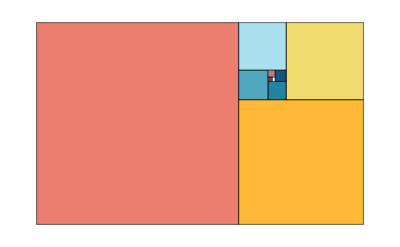

```mathematica
Graphics[{EdgeForm[Opacity[.5]],Table[{ColorData[24,k+1],Rectangle@@gr[k]},{k,0,8}]}]
```

```mathematica
Animate[With[{q=Quotient[θ,π/2],m=Mod[θ,π/2]},Graphics[{EdgeForm[Black],LightGray,Rotate[Rectangle[{q,0}],-m,{q+1,0}]},Axes->{True,False},PlotRange->{{-.5,5.5},{-0.5,1.5}},ImageSize->350]],{θ,0,2Pi},AnimationRunning->False,AnimationDirection->ForwardBackward,DefaultDuration->2]
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
ϕ[n_]:=N@(GoldenRatio^n);Φ[n_]:=1/ϕ[n];circles[0]:=Circle[{1,0},1,{Pi,3Pi/2}];
circles[n_]:=Circle@@Module[{m=Mod[n,4],x1,y1,x2,y2},{{x1,y1},{x2,y2}}=rect[n-1];
Which[m==0,{{x1+Φ[n],y2},Φ[n],{Pi,3Pi/2}},m==1,{{x2,y2+Φ[n]},Φ[n],{3Pi/2,2Pi}},m==2,{{x2-Φ[n],y1},Φ[n],{0,Pi/2}},m==3,{{x1,y1-Φ[n]},Φ[n],{Pi/2,Pi}}]];
color={{Gray,Gray,Gray,Gray},{RGBColor[1, 0.128252, 0.306447],RGBColor[0.986831, 1, 0.3093],RGBColor[0.336309, 1, 0.485557],RGBColor[0.11722, 0.379614, 1]}};
rect[0]={{0,0},{1,-1}};
rect[n_]:=Module[{m=Mod[n,4],x1,y1,x2,y2},{{x1,y1},{x2,y2}}=rect[n-1];

Which[m==0,{{x1,y2},{x1+Φ[n],y2-Φ[n]}},m==1,{{x2,y2+Φ[n]},{x2+Φ[n],y2}},m==2,{{x2-Φ[n],y1+Φ[n]},{x2,y1}},m==3,{{x1-Φ[n],y1},{x1,y1-Φ[n]}}]];
GoldenRectangle[n_,b_,gray_]:=Graphics[Flatten[Table[{color[[gray,Mod[i,4,1]]],EdgeForm[{Black}],Rectangle[rect[i][[1]],rect[i][[2]]]},{i,b,n}]]];
GoldenSquare[n_,op_,gray_]:=Graphics[{color[[gray,Mod[n,4,1]]],EdgeForm[{Black}],Rectangle[rect[n][[1]],rect[n][[2]]]}];

circleTable[k_,b_,tick_:0.5]:=Graphics[Table[{AbsoluteThickness[tick 2/(Log[(i+1)]+0.7)],circles[i]},{i,b,k}]];

Manipulate[Module[{t,z,k,l,b,g},t=n +s-1; k=Floor[t];l=Ceiling[t];If[az,

z=ϕ[Max[0,t-4]],{None}];b=Max[0,Floor[Log[GoldenRatio,z]]-3];
Show[{GoldenRectangle[k,b,gr],GoldenSquare[l,s,gr],circleTable[k,b,1]},PlotRangePadding->{Scaled[.1],Scaled[.1]},ImageSize->980{1,1/GoldenRatio},Axes->False]
],
{{s,0,"progression"},{0},ControlType->None},
{{az,True, "autozoom"},{True},ControlType->None},{{gr,2,"square color"},{1->"Gray",2->"Color"},ControlPlacement->Top,ControlType->PopupMenu},{{n,1,"iteration"},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21},ControlType->SetterBar},TrackedSymbols->{s,az,gr,n},AutorunSequencing->{3,4},SaveDefinitions->True]
```

# Golden Ratio Given three circles with radii = a cm. each. Find the ratio between the radius of the encompassing circle and the diameter of the small circle.

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
Column[{Item[If[answer,Style[Row[{Spacer[60],"\nRatio of R : d =",Spacer[30],"√5 + 1   : 1 \n"}],24,Purple],Style["\nCalculate the ratio betwen the radius of the encompassng circle and the diameter of the smaller circle d\n",16,Black]],Alignment->Left,Frame->True], 
Item[
Graphics[{
{Thick,Circle[{0,0},(√5+1)a,{0,π}]},
{Thick,Blue,Circle[{0,a},a,{0,2π}]},
{Thick,Purple,Circle[{2 a,a},a,{0,2π}]},
{Thick,Red,Circle[{-2 a,a},a,{0,2π}]},
{PointSize[0.02],Point[{0,0}]},
{PointSize[0.02],Purple,Point[{2 a,a}]},
{PointSize[0.02],Blue,Point[{0,a}]},
{PointSize[0.02],Red,Point[{-2 a,a}]},
{Thick,Line[{{-4 a,0},{4 a,0}}]},{Thick,Arrowheads[{-0.03,0.03}],Arrow[{{-a,a},{a,a}}]},Arrow[{{0,0},(√5+1 ) a {Cos[π/3],Sin[π/3]}}],Text[Style["d cm",12,Black],{0,a+0.2}],Text[Style["R cm",12,Blue],((√5+1 ) a ){Cos[7π/18],Sin[9π/36]}]

},Axes->True,ImageSize->{450,250}],Alignment->{Center},Frame->True]
}],
Row[{Control[
{{a,1,"radius"},0.25,2,Appearance->"Labeled"}],Control[{{answer,False,"aswer"},{False,True}}]}],TrackedSymbols->{a,answer}]
```

# Ratio of Areas of two consecutive Pentagons and a Star

```mathematica
ClearAll["Global`*"];
```

```mathematica
DynamicModule[{r,m,t,Answer},Manipulate[goldratio= (1+√5)/2;grsqr=1+2 Cos[π/5];
r1=goldratio-1;
apathom= r Cos[π/5];Graphics[{Yellow,Polygon[{{r Cos[π/10],r Sin[π/10]},{0,r},r {Cos[9 π/10],Sin[9 π/10]},r{Cos[13 π/10],Sin[13π/10]}, r {Cos[17 π/10],Sin[17π/10]}}],RGBColor[0.1,0.8,0.1],If[Answer,Polygon[{ r{Cos[π/10],Sin[π/10]},{0,r}, r grsqr{Cos[3π/10],Sin[3π/10]}}],Polygon[{ r{Cos[π/10],Sin[π/10]},{0,r},t r grsqr{Cos[3π/10],Sin[3π/10]}}]],

{RGBColor[1,0,0],Opacity[0.85],EdgeForm[Black],Polygon[{ {0,r},r {Cos[π/10],Sin[π/10]},m r {Cos[3π/10],Sin[3π/10]}}],Purple,Polygon[{ r {Cos[9π/10],Sin[9π/10]},r {Cos[13π/10],Sin[13π/10]}, m r {Cos[11π/10],Sin[11π/10]}}],RGBColor[0.95,0.15,0.2],
Polygon[{r {Cos[13π/10],Sin[13π/10]}, m   {0,-r}, r{Cos[17π/10],Sin[17π/10]}}],RGBColor[1,0.2,0.75],
Polygon[{r {Cos[17π/10],Sin[17π/10]},   m r  {Cos[19π/10],Sin[19π/10]},r{Cos[π/10],Sin[π/10]}}],
RGBColor[0,0.6,1],
Polygon[{ {0,r},r {Cos[9π/10],Sin[9π/10]}, m r {Cos[7π/10],Sin[7π/10]}}]

},
{Purple,Opacity[0.5],Polygon[{{0,r}, r{Cos[9π/10],Sin[9π/10]},  r grsqr{Cos[7π/10],Sin[7π/10]}}]},

Hue[0.55],Opacity[0.7],Polygon[{ r{Cos[9π/10],Sin[9π/10]},r {Cos[13π/10],Sin[13π/10]},  r grsqr {Cos[11π/10],Sin[11π/10]} }],

Orange,Polygon[{r {Cos[13π/10],Sin[13π/10]},  grsqr {0,-r},r{Cos[17π/10],Sin[17π/10]}}],

Hue[0.6],Polygon[{r {Cos[17π/10],Sin[17π/10]},    r grsqr {Cos[19π/10],Sin[19π/10]},r{Cos[π/10],Sin[π/10]}}],

If[t==1&&m==goldratio,
{Black,Dashing[0.01],Arrow[{{0,0},{0,r }}],
Arrow[{{0,0},r grsqr { Cos[3π/10],Sin[3π/10]}}],Inset[Style["36°",12,Black],{0.4,1.}],
Inset[Style["r",16,Black],{-0.4,r/2}],
Inset[Style["R =\nr (1 + Cos 36°) + r Cos 36° = ϕ^2 r",16,Black],(3r grsqr/4) { Cos[3π/10],Sin[3π/10]}]}],

Thick,Red,Circle[{0,0},r grsqr, {0,2π}],
Thick,Blue,Line[{  grsqr {0,-r}, r grsqr {Cos[19π/10],Sin[19π/10]}}],
Line[{ r grsqr{Cos[7π/10],Sin[7π/10]},
 r grsqr {Cos[11π/10],Sin[11π/10]} }],
Line[{ r grsqr{Cos[3π/10],Sin[3π/10]},
r grsqr{Cos[7π/10],Sin[7π/10]}}],
Line[{r grsqr{Cos[3π/10],Sin[3π/10]},
r grsqr {Cos[19π/10],Sin[19π/10]} }],
Line[{ grsqr {0,-r}, r grsqr {Cos[11π/10],Sin[11π/10]} }],
Thick,Red,Circle[{0,0},r,{0,2 π}],Black,PointSize[0.015],Point[{0,0}]},PlotRange->{{-7,7},{-7,7}},Which[
t==1&&m==goldratio&&!Answer,PlotLabel->Style["Think about the ratio between the square of the two radii:\n the radius R of the circle circumscribing the outer pentagon\n and the radius r of the smaller circle\n",14,Blue],
Answer,PlotLabel->Style[Row[{"Ratio of areas of:\n Internal-Pentagon : Star : Pentagon are :
  1 ",Spacer[12]," :  ϕ^3 - 1 ",Spacer[21]," :      ϕ^4\n=",Spacer[18],"1 ",Spacer[12]," :  2 ϕ ",Spacer[39],"  :   3 ϕ + 2\n=     1 ","   : 3.236         :    6.854  "}], 16,Blue],True,PlotLabel->Style["Calculate the ratio of the areas of: \n the Internal-Pentagon : the Star : the Pentagon",16, Purple]],Axes->False,ImageSize->420],
Grid[{{
Control[
{{r, 2.5,"Radius"},1,2.5,Appearance->"Labeled"}],Control[
{{Answer,False,"Answer"},{False,True}}]},{Control[
{{m,0,"Tip 1"},0,goldratio,Appearance->"Labeled",ImageSize->Tiny}],Control[
{{t,1,"Tip 2"},-1/grsqr,1,Appearance->"Labeled",ImageSize->Tiny}]}}],TrackedSymbols->{t,r,m,Answer}]]
```

# Ratio of Areas of two consecutive Pentagons and a Star

```mathematica
Manipulate[goldratio= (1+√5)/2;grsqr=1+2 Cos[π/5];

apathom= r Cos[π/5];Graphics[{Yellow,Polygon[{{r Cos[π/10],r Sin[π/10]},{0,r},r {Cos[9 π/10],Sin[9 π/10]},r{Cos[13 π/10],Sin[13π/10]}, r {Cos[17 π/10],Sin[17π/10]}}],RGBColor[0.1,0.8,0.1],Polygon[{ r{Cos[π/10],Sin[π/10]},{0,r},t r grsqr{Cos[3π/10],Sin[3π/10]}}],
RGBColor[0.7,0.1,0.1],Polygon[{ {0,r},r {Cos[π/10],Sin[π/10]},m r {Cos[3π/10],Sin[3π/10]}}],
Pink,Polygon[{{0,r}, r{Cos[9π/10],Sin[9π/10]},  r grsqr{Cos[7π/10],Sin[7π/10]}}],
RGBColor[0.6,0.1,0.1],Polygon[{ {0,r},r {Cos[9π/10],Sin[9π/10]}, m r {Cos[7π/10],Sin[7π/10]}}],
Hue[0.55],Polygon[{ r{Cos[9π/10],Sin[9π/10]},r {Cos[13π/10],Sin[13π/10]},  r grsqr {Cos[11π/10],Sin[11π/10]} }],
RGBColor[0.7,0.1,0.2],Polygon[{ r {Cos[9π/10],Sin[9π/10]},r {Cos[13π/10],Sin[13π/10]}, m r {Cos[11π/10],Sin[11π/10]}}],
Orange,Polygon[{r {Cos[13π/10],Sin[13π/10]},  grsqr {0,-r},r{Cos[17π/10],Sin[17π/10]}}],
RGBColor[0.65,0.1,0.15],Polygon[{r {Cos[13π/10],Sin[13π/10]}, m   {0,-r},r{Cos[17π/10],Sin[17π/10]}}],
Hue[0.6],Polygon[{r {Cos[17π/10],Sin[17π/10]},    r grsqr {Cos[19π/10],Sin[19π/10]},r{Cos[π/10],Sin[π/10]}}],
RGBColor[0.65,0.15,0.1],Polygon[{r {Cos[17π/10],Sin[17π/10]},   m r  {Cos[19π/10],Sin[19π/10]},r{Cos[π/10],Sin[π/10]}}],
{Black,Dashing[0.01],Arrow[{{0,0},{0,r grsqr Cos[π/5]}}],Arrow[{{0,0},r grsqr { Cos[3π/10],Sin[3π/10]}}],Inset[Style["36°",12,Black],{0.4,1.}]},

Thick,Red,Circle[{0,0},r grsqr, {0,2π}],
Thick,Blue,Line[{  grsqr {0,-r}, r grsqr {Cos[19π/10],Sin[19π/10]}}],
Line[{ r grsqr{Cos[7π/10],Sin[7π/10]},
 r grsqr {Cos[11π/10],Sin[11π/10]} }],
Line[{ r grsqr{Cos[3π/10],Sin[3π/10]},
r grsqr{Cos[7π/10],Sin[7π/10]}}],
Line[{r grsqr{Cos[3π/10],Sin[3π/10]},
r grsqr {Cos[19π/10],Sin[19π/10]} }],
Line[{ grsqr {0,-r}, r grsqr {Cos[11π/10],Sin[11π/10]} }],
Thick,Red,Circle[{0,0},r,{0,2 π}],Red,PointSize[0.02],Point[{0,0}]},PlotRange->{{-7,7},{-7,7}},If[Answer,PlotLabel->Style[Row[{"Ratio of areas of:\n Internal-Pentagon : Star : Pentagon are :
  1 ",Spacer[12]," :  ϕ^3 - 1 ",Spacer[21]," :      ϕ^4\n=",Spacer[18],"1 ",Spacer[12]," :  2 ϕ ",Spacer[39],"  :   3 ϕ + 2\n=     1 ","   : 3.236         :    6.854  "}], 16,Blue],PlotLabel->Style["Calculate the ratio of the areas of: \n the Internal-Pentagon : the Star : the Pentagon",16, Purple]],Axes->False],
{{r, 2.5,"Radius"},1,2.5,Appearance->"Labeled"},
{{m,goldratio,"hint 1"},0,goldratio,Appearance->"Labeled"},
{{t,1,"hint 2"},-1/grsqr,1,Appearance->"Labeled"},
{{Answer,False,"Answer"},{False,True}},TrackedSymbols->{t,r,m,Answer}]
```

## Golden Ratio - 5 Stars - Pentagons Ratio of Areas of Pentagons and Starrs

```mathematica
Module[{r,m,t,Answer},Manipulate[goldratio= (1+√5)/2;grsqr=1+2 Cos[π/5];
r1=goldratio-1;
apathom= r Cos[π/5];Graphics[{

(* Grph the pentagons and the stars *)
Yellow,Polygon[{{r Cos[π/10],r Sin[π/10]},{0,r},r {Cos[9 π/10],Sin[9 π/10]},r{Cos[13 π/10],Sin[13π/10]}, r {Cos[17 π/10],Sin[17π/10]}}],RGBColor[0.1,0.8,0.1],
(*Thick,Red,Circle[{0,0},r grsqr, {0,2π}],*)
Thick,Blue,Line[{  grsqr {0,-r}, r grsqr {Cos[19π/10],Sin[19π/10]}}],
Line[{ r grsqr{Cos[7π/10],Sin[7π/10]},
 r grsqr {Cos[11π/10],Sin[11π/10]} }],
Line[{ r grsqr{Cos[3π/10],Sin[3π/10]},
r grsqr{Cos[7π/10],Sin[7π/10]}}],
Line[{r grsqr{Cos[3π/10],Sin[3π/10]},
r grsqr {Cos[19π/10],Sin[19π/10]} }],
Line[{ grsqr {0,-r}, r grsqr {Cos[11π/10],Sin[11π/10]} }],
{Purple,Opacity[0.5],Polygon[{{0,r}, r{Cos[9π/10],Sin[9π/10]},  r grsqr{Cos[7π/10],Sin[7π/10]}}]},

Hue[0.55],Opacity[0.7],Polygon[{ r{Cos[9π/10],Sin[9π/10]},r {Cos[13π/10],Sin[13π/10]},  r grsqr {Cos[11π/10],Sin[11π/10]} }],

Orange,Polygon[{r {Cos[13π/10],Sin[13π/10]},  grsqr {0,-r},r{Cos[17π/10],Sin[17π/10]}}],

Hue[0.6],Polygon[{r {Cos[17π/10],Sin[17π/10]},    r grsqr {Cos[19π/10],Sin[19π/10]},r{Cos[π/10],Sin[π/10]}}],

If[Answer,{{EdgeForm[Blue],Green,Polygon[{ r{Cos[π/10],Sin[π/10]},{0,r}, r grsqr{Cos[3π/10],Sin[3π/10]}}]},
(* show the triangles outside the inner polygon *)
{RGBColor[1,0,0],Opacity[0.85],EdgeForm[Black],Polygon[{ {0,r},r {Cos[π/10],Sin[π/10]},goldratio r {Cos[3π/10],Sin[3π/10]}}],Purple,Polygon[{ r {Cos[9π/10],Sin[9π/10]},r {Cos[13π/10],Sin[13π/10]}, goldratio r {Cos[11π/10],Sin[11π/10]}}],RGBColor[0.95,0.15,0.2],
Polygon[{r {Cos[13π/10],Sin[13π/10]}, goldratio   {0,-r}, r{Cos[17π/10],Sin[17π/10]}}],RGBColor[1,0.2,0.75],
Polygon[{r {Cos[17π/10],Sin[17π/10]},   goldratio r  {Cos[19π/10],Sin[19π/10]},r{Cos[π/10],Sin[π/10]}}],
RGBColor[0,0.6,1],
Polygon[{ {0,r},r {Cos[9π/10],Sin[9π/10]}, goldratio r {Cos[7π/10],Sin[7π/10]}}]
},{Black,Dashing[0.01],Arrow[{{0,0},{0,r }}],
Arrow[{{0,0},r grsqr { Cos[3π/10],Sin[3π/10]}}],Inset[Style["36°",12,Black],{0.4,1.}],
Inset[Style["r",16,Black],{-0.4,r/2}],
Inset[Style["R",16,Black],(3r grsqr/4) { Cos[3π/10],Sin[3π/10]}]}},

{{EdgeForm[Blue],Green,Polygon[{ r{Cos[π/10],Sin[π/10]},{0,r},t r grsqr{Cos[3π/10],Sin[3π/10]}}]},
(* Graph the inside triangles that will be moving outside the inner pentagon *)
{RGBColor[1,0,0],Opacity[0.85],EdgeForm[Black],Polygon[{ {0,r},r {Cos[π/10],Sin[π/10]},m r {Cos[3π/10],Sin[3π/10]}}],Purple,Polygon[{ r {Cos[9π/10],Sin[9π/10]},r {Cos[13π/10],Sin[13π/10]}, m r {Cos[11π/10],Sin[11π/10]}}],RGBColor[0.95,0.15,0.2],
Polygon[{r {Cos[13π/10],Sin[13π/10]}, m   {0,-r}, r{Cos[17π/10],Sin[17π/10]}}],RGBColor[1,0.2,0.75],
Polygon[{r {Cos[17π/10],Sin[17π/10]},   m r  {Cos[19π/10],Sin[19π/10]},r{Cos[π/10],Sin[π/10]}}],
RGBColor[0,0.6,1],
Polygon[{ {0,r},r {Cos[9π/10],Sin[9π/10]}, m r {Cos[7π/10],Sin[7π/10]}}]

}}],

If[t==1&&m==goldratio,
{{Black,Dashing[0.01],Arrow[{{0,0},{0,r }}],
Arrow[{{0,0},r grsqr { Cos[3π/10],Sin[3π/10]}}],Inset[Style["36°",12,Black],{0.4,1.}],
Inset[Style["r",16,Black],{-0.4,r/2}],
Inset[Style["R",16,Black],(3r grsqr/4) { Cos[3π/10],Sin[3π/10]}]},

Dashing[0.02],Thick,Black,Circle[{0,0},r,{0,2 π}],Black,PointSize[0.015],Point[{0,0}],{Thick,Red,Circle[{0,0},r grsqr, {0,2π}]}}]
},
Which[
t==1&&m==goldratio&&!Answer,PlotLabel->Style["Think about the ratio between the square of the two radii:\n the radius R of the circle circumscribing the outer pentagon\n and the radius r of the smaller circle\n",14,Blue],
Answer,PlotLabel->Style[Row[{"Ratio of areas of:\n Internal-Pentagon : Star : Pentagon are :
  1 ",Spacer[12]," :  ϕ^3 - 1 ",Spacer[21]," :      ϕ^4\n=",Spacer[18],"1 ",Spacer[12]," :  2 ϕ ",Spacer[39],"  :   3 ϕ + 2\n=     1 ","   : 3.236         :    6.854  "}], 16,Blue],True,PlotLabel->Style["Calculate the ratio of the areas of: \n the Internal-Pentagon : the Star : the Pentagon",16, Purple]],PlotRange->{{-7,7},{-7,7}},Axes->False],
Grid[{{
Control[
{{r, 2.5,"Radius"},1,2.5,Appearance->"Labeled"}],Control[
{{Answer,False,"Answer"},{False,True}}]},{Control[
{{m,0,"Tip 1"},0,goldratio,Appearance->"Labeled",ImageSize->Tiny}],Control[
{{t,1,"Tip 2"},-1/grsqr,1,Appearance->"Labeled",ImageSize->Tiny,Enabled->m==goldratio}]}}],TrackedSymbols->{t,r,m,Answer}]]
```

# Ratio of areas of Hexagons and a star

```mathematica
Manipulate[
Graphics[{

(*Draw the Outer Hexagon *)
White,Polygon[{{a,a √3},{2 a,0},{a,-a √3},{-a,-a √3},{-2 a,0},{-a,a √3}}],

Blue,Circle[{0,0},2 a √3,{0,2π}],Dashing[0.015],Line[{{-3 a,-a √3},{-3 a,a √3}}],Line[{{-3 a,a √3},{0,2 a √3}}],
Line[{{0,2 a √3},{3 a,a √3}}],Line[{{3 a,a √3},{3 a,-a √3}}],
Line[{{3 a,-a √3},{0,-2 a √3}}],Line[{{0,-2 a √3},{-3 a,-a √3}}],



(* Draw Inner Polygon *)

{Yellow,Polygon[{{-2a,0},{-a,a √3},{a,a √3},{2 a,0},{a,-a √3},{-a,-a √3}}]},
{PointSize[0.015],Red,Point[{0,0}]},

(* Draw the Star *)
Orange,Polygon[{{a,a √3},{2 a,0},(1-t){3 a,a √3}}],Orange,Polygon[{{a,-a √3},(1-t){0,-2 a √3},{-a,-a √3}}]  ,

Polygon[{{-a,a √3},{-2 a,0},(1-t){-3 a,a √3}}],RGBColor[.79,.1,.26],Polygon[{{a,a √3},(1-t){0,2 a √3},{-a,a √3}}],Polygon[{{a,-a √3},{2 a,0},(1-t){3 a,-a √3}}],Polygon[{{-a,-a √3},{-2 a,0},(1-t){-3 a,-a √3}}] ,


(* Divide the inner hexagon into triangles*)
If[solution&&steps==2&&n==0,{

{GrayLevel[0.8],
Polygon[{{ a,a √3},{2 a,0},{ a,-a √3}}],Polygon[{{a, a √3},{-a,a √3}, {-2a,0}}],
Polygon[{{-2a,0},{-a,-a √3},{a,-a √3}}]},
{RGBColor[1,0,0.5],Polygon[{{a,a √3},{0, 0},{a, -a √3}
}]},Hue[0.55],Polygon[{{a,a √3
},{0,0},{-2a,0}}],RGBColor[0.1,0.8,0.1],Polygon[{{-2 a ,0},{0,0},{a, - a √3
}}] ,

RGBColor[0.7,0,0,5],Dashing[0.01],Line[{{a,a √3},{a,-a √3}}],Line[{{a,a √3},{-2 a,0}}],Line[{{-2a,0},{a,-a √3}}]

},{}],

(*Translate the triangles out of Hexagon *)
If[solution&&steps==3,{

{GrayLevel[0.8],
Polygon[{{2 a n+ a,a √3},{2 a,0},{2 a n + a,-a √3}}],Polygon[{{-n a+a,a n √3 +a √3},{-a,a √3}, {- a n-2a,a n √3}}],
Polygon[{{-2a-a n,-a n √3},{-a,-a √3},{a-a n,-a √3-a n √3}}]},
RGBColor[1,0,0.5],Polygon[{{-n a+a,a n √3 +a √3
},{n a, n a √3},{2 a n+a,2a n √3 -a √3}
}],Hue[0.55],Polygon[{{-4 a n +a,a √3
},{-2 a n,0},{-2a-a n,-a n √3}}],RGBColor[0.1,0.8,0.1],Polygon[{{-2 a+2 a n ,-2 a n √3},{a n, -a n √3},{2 a n + a, - a √3
}}] ,

RGBColor[0.7,0,0,5],Dashing[0.01],Line[{{a,a √3},{a,-a √3}}],Line[{{a,a √3},{-2 a,0}}],Line[{{-2a,0},{a,-a √3}}]

},{}]},

PlotLabel->Which[solution&&steps==1,Style["\n Map Star into inner hexagon \n", 20, Black,Italic],solution&&steps==2&&n==0,Style["\nDivide the inner hexagon into triangles\n",20,Black,Italic],solution&&steps==3&&n==0,
Style["\n Translate triangles out of hexagon\n ", 20,Italic, Black],
solution&&steps==4|| Answer,Style["\nRatio of areas of\ninner Hexagon : Star : outer Hexagon are:\n1   :   2   :  3 \n", 20,Blue,Italic],
True,
Style["Calculate the ratio of the areas of: \n the inner Hexagon : the Star : the outer Hexagon\n",16, Purple]
],PlotRange->{{-11,11},{-11,11}} ,Axes->True,ImageSize->500],
{{a,3,"a = side length of small △ "},1/√3,3,Appearance->"Labeled"},
{{solution,False},{False,True}},
Grid[{{Control[
{{t,0,"Map Star in Hexagon"},0,1,ImageSize->Tiny,Appearance->"Labeled",Enabled->Dynamic[solution]}],Control[

{{n,0,"Translate Δs out"},0,1,ImageSize->Tiny,Appearance->"Labeled",Enabled->If[Dynamic[solution&&steps==3],True,False]}]},{Control[{{steps,1,"steps"},{1,2,3,4},ControlType->RadioButton,Enabled->solution}],Control[
{{Answer,False,"Answer"},{False,True}}]}}],TrackedSymbols->{solution,steps,Answer,a,t,n}]
```

# Decorating a Glass Panel

```mathematica
Manipulate[areaTr:= (1-(√2)/2)^2;
Column[{
Item[If[Answer,Style[Row[{"\nArea of Red Triangle = ",areaTr,"  sq. meters.\n"}],16,Italic,Purple],Style["\nCalculate the area of one of the red triangles\ngiven that the radius of the yellow disk = 1 meter\n",16,Black]],Alignment->{Center},Frame->True],
Item[
Graphics[{
{EdgeForm[Red],FaceForm[Yellow],Disk[]},{EdgeForm[Blue],Opacity[0.5],RGBColor[1,0.6,0.3],Rectangle[{-(√2)/2,-(√2)/2},{(√2)/2,(√2)/2}]},{EdgeForm[Blue],Yellow,Polygon[{{-1,0},{0,-1},{1,0},{0,1}}]},{EdgeForm[Blue],Red,Polygon[{{-1+(√2)/2,(√2)/2},{0,1},{1-(√2)/2,(√2)/2}}],Polygon[{{-1+(√2)/2,(-√2)/2},{0,-1},{1-(√2)/2,(-√2)/2}}]},{EdgeForm[Blue],Green,Polygon[{{(√2)/2,1-(√2)/2},{1,0},{(√2)/2,-1+(√2)/2}}],Polygon[{{(-√2)/2,1-(√2)/2},{-1,0},{(-√2)/2,-1+(√2)/2}}]},{Thick,EdgeForm[Purple],White,Disk[{0,0},radius]},{Thick,Purple,PointSize[0.025],Point[{0,0}]}
},Axes->False,ImageSize->360],Alignment->{Center},ItemSize->{33,4},Frame->True]
}],Row[{Control[
{{radius,√2.-1,"Radius"},0.01,(√2)/2,Appearance->"Labeled"}],Spacer[21],Control[
{{Answer,False,"Ansewer"},{False,True}}]
}],
TrackedSymbols->{radius,Answer}]
```

## Calculate the area and the circumference of an egg-shaped figure.

```mathematica
Manipulate[
Clear[c1,c2,c3,c4];
c1={Thick,Purple,Circle[{0,0},a,{-Pi/2,Pi/2}],Point[{0,0}]};
c2={Thick,Pink,Circle[{0,a},2 a,{5 Pi/4,3 Pi/2}]};
c3={Thick,Pink,Circle[{0,-a},2 a,{Pi/2,3 Pi/4}]};
c4={Thick,Red,Circle[{-a,0},(2-Sqrt[2]) a,{3 Pi/4,5 Pi/4}],
	Point[{-a,0}]};
l1={Purple,Line[{{0,-a},{0,a}}]};
l2={Blue,Line[{{0,a},{-a Sqrt[2],a-a Sqrt[2]}}]};
l3={Orange,Line[{{0,-a},{-a Sqrt[2],-a+a Sqrt[2]}}]};
l4={Black,Line[{{-3 a+a Sqrt[2],0},{a ,0}}]};
t1=Text[Style["a",{"Times-Bold",24}],{a/2,-0.1}];
t2=Text[Style["a",{"Times-Bold",24}],{-a/2,-0.1}];
quetn=Text[Style["Prove that the area of the figure = ((3 -Sqrt[2]) Pi -1)(a^2) and \n the circumference of the figure is = (3 - Sqrt[2]/2)( a Pi)",18,Bold,Purple],{-2,7}];
area=Text[Style[Row[{"Area of the figure = ", 
((3 -Sqrt[2]) π -1)(a^2),"\n\n"}],18,Blue,Bold],{-2,8}]; 
circom=Text[Style[Row[{"Circumference = ",
(3 - Sqrt[2]/2)( a Pi),"\n\n"}],18,Bold,Purple],{-2,6}];
If[Answer,Show[Graphics[{c1,c2,c3,c4,t1,t2,l1,l2,l3,l4,area,circom},AspectRatio->Automatic,PlotRange->{{-9,6},{-6,10}},Axes->False,ImageSize->Large]],
Show[Graphics[{ c1,c2,c3,c4,t1,t2,l1,l2,l3,l4,quetn},Axes->False,AspectRatio->Automatic,PlotRange->{{-9,6},{-6,10}},ImageSize->Large]]],

{{a,2,"Radius"},1,5,Appearance->"Labeled"},
{{Answer,False,"Answer"},{False,True}},TrackedSymbols->{a,Answer}]
```

# Koch Snowflakes

The Koch snowflake is constructed by following a simple rule: put a triangle on top of every line. After this, the picture still consists of lines. To each of these lines, the rule is applied again: put a triangle on top of every line. After applying this refinement infinitely many times, a fractal appears. Three of these fractals put together in a triangle are called the Koch snowflake. In this Demonstration, you can vary the rule for making the snowflake by dragging the points. You can also add points with Alt+click.

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
Column[{Item[If[Answer&&iter==0&&maketriangle,Text@Style[Row[{Style["\nArea of Δ with side length 2 √3 in",Italic]," =3 √3 in^2\n"}],18],If[Answer&&iter≥1&&maketriangle,Text@Style[Row[{Style["Shaded Area",Italic,Black],Style[" = ",Black],Style[area[iter],18,Black],Style["  in^2",18,Black],"\n",Style["Lim_(n → ∞) Area",Red,Italic,18]," = ",limitarea," in^2 ;   % of areas =",percentarea," %\n"}],18,Red],If[!maketriangle,Text@Row[{Style["\nShow the triangle and Calculate the shaded area\n if the Side length of Δ = ",18,Italic],Style[sidelength,18,Black],Style[" in \n",18,Black]}],Text@Row[{Style["Calculate the shaded area if the Side length of Δ = ",18,Italic],Style[sidelength,18,Black],Style["  in \n",18,Black]}]]]],ItemSize->{45,3},Frame->True,Alignment->{{Center},{Left}}],
Item[Graphics[{Line@Nest[g[form,#]&,pts0,iter],If[maketriangle,{Opacity[0.5],EdgeForm[Black],Hue[iter],Polygon[triangle],Red,Disk[{0,0},radius],Blue,PointSize[0.01],Point[{0,0}](*Inset[Image[-Graphics-,ImageSize->{220,220}],{0,0}]*)},{}]},Axes->ax,PlotRange->2.1,AxesOrigin->{0,0},AspectRatio->Automatic,ImageSize->{500,500}],ItemSize->{39,3},Frame->All,Alignment->{Center}]}],
(*"None"->{{pts,{{-√3/3,1},{0,1},{√3/3,1}}},{-2.1,-2.1},{2.1,2.1},Locator,LocatorAutoCreate->{1,∞},ContinuousAction->If[iter>2,False,True]},*)
Row[{Control[{{ax,False,"Show axes"},{False,True}}],Spacer[30],Control[
{{iter,3,"refinements"},0,5,1,SetterBar}],Spacer[30],Control[
{{maketriangle,False,"make triangle"},{True,False}}],Spacer[40],Control[{{Answer,False,"Answer"},{False,True}}]}],{{radius,0.02,"radius"},0.01,(2 √3)/3,Appearance->"Labeled"},SaveDefinitions->True,
TrackedSymbols:>{pts,ps0,ax,iter,maketriangle,Answer,radius},Initialization:>{ClearAll["Global`*"];sidelength=2 √3;
area[n_]=FullSimplify[(1+(3(1-(4/9)^n))/5)(√3)/4 sidelength^2];

limitarea=Limit[(1+(3(1-(4/9)^n))/5)(√3)/4 sidelength^2,n->∞];

percentarea:=NumberForm[100.*area[iter]/limitarea,{5,3}];
pts0={{-√3,1},{√3,1}};
pts={{-√3/3,1},{0,2},{√3/3,1}};
form=Append[Prepend[pts,{-√3,1}],{√3,1}];
f[form_,{a_,b_}]:=AffineTransform[{{b-a,({{0, -1}, {1, 0}}).(b-a)}ᵀ,a}][1/Norm[Last[form]-First[form]]TranslationTransform[-First[form]][form]],
g[form_,points_]:=Flatten[Map[f[form,#]&,Partition[points,2,1]],1],base:=Nest[g[form,#]&,pts0,iter];
triangle:=Join[base,RotationTransform[4 π/3.][base],RotationTransform[2 π/3.][base]];}
]
```

## The Ratio between the shaded area and the small circle

```mathematica
Manipulate[
If[center<radius-Radius,center=radius-Radius];
If[center>Radius-radius,center=Radius-radius];
area=π (Radius^2 -radius^2);
ratio= (Radius^2 -radius^2)/radius^2;
Column[{
If[Answer,Text @ Style[Row[{"Ratio of shaded area to small circle = ",TraditionalForm[ratio]," = ",NumberForm[N@ (ratio),{5,4}]}],18,Bold, Blue],
Style["Calculate the Ratio of the shaded Area to the area of the small Circle",16,Bold,Red]],
Graphics[{
GrayLevel[0.8],Disk[{0,0},Radius],
Thick, Black,Circle[{0,0},Radius],
White,Disk[{center,0},radius],
 Thick,Blue,Circle[{center,0},radius],
PointSize[0.03],Blue,Point[{center,0}],
Black,Dashed,Line[{{-Radius,0},{Radius,0}}]
},PlotRange->5.1,(*Axes->True,*)ImageSize->Large]
},Alignment->Center],
Row[{
Control[
{{Radius,3,"large radius R"},radius,5,0.1,Appearance->"Labeled",ImageSize->Tiny}],Spacer[6],Control[{{radius,1.5,"small radius r"},0.2,Radius-0.3,0.1,Appearance->"Labeled",ImageSize->Tiny}],Spacer[6],Control[ {{center,-0.9},radius-Radius,Radius-radius,0.1,Appearance->"Labeled",ImageSize->Tiny}],Spacer[6],Control[
{{Answer,False,"Answer"},{False,True}}]}],TrackedSymbols->{Radius,radius,center,Answer}]
```

## III Area of Lunes

## Equal areas of Lunes.

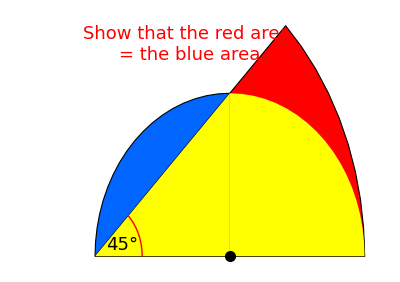

```mathematica
Graphics[{{EdgeForm[{Thick,Black}],FaceForm[RGBColor[0,0.4,1]],Disk[{1,0},1,{0,π}]},{EdgeForm[{Thick,Black}],FaceForm[Red],Disk[{0,0},2,{0,π/4}]},{FaceForm[Yellow],Disk[{1,0},1,{0,π/2}]},{FaceForm[Yellow],Polygon[{{0,0},{1,0},{1,1}}]},{PointSize[0.02],Black,Point[{1,0}]},Text[Style["45°",18,Black],{0.2,0.07}],Thick,Red,Circle[{0,0},0.35,{0,π/4}],Text[Style[Row[{Style["Show that the",Black],Style[" red ",Red],Style["area \n= the ",Black],Style["blue",Blue],Style[ " area",Black]}],18,Italic],{0.7,1.3}]}]
```

## The Area of the Lunes and the Area of the Triangle.

```mathematica
This program shows that the sum of the areas of the two lunes is equal to the area of the triangle.  Prove it.
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
Graphics[{
b:=Sqrt[1-a^2];
arealeftlune=
If[a≤0,
π (1-Abs[a])/4-0.5(ArcSin[b]-b),
π (a-1)/4+0.5 ( ArcSin[b]+b )];
arearightlune=If[a>0,
π (1-a)/4+0.5 (b-ArcSin[b]),
π (Abs[a]-1)/4+0.5 (b+ArcSin[b] )];

{Hue[0.5],Disk[{(a-1)/2, b/2},Sqrt[2 a+2]/2,{ArcTan[Sqrt[(1-a)/(1+a)]],π+ArcTan[Sqrt[(1-a)/(1+a)]]}]},
{Hue[0.5],Disk[{(a+1)/2,b/2},Sqrt[2 - 2 a]/2,{-ArcTan[Sqrt[(1+a)/(1-a)]],π-ArcTan[Sqrt[(1+a)/(1-a)]]}]},
{GrayLevel[1],Disk[{0,0},1,{0,π}]},
{Hue[0.85],Polygon[{ {-1,0}, {a,b},{1,0} }]},
Thick,Circle[{0,0},1,{0,π}],{PointSize[Large],Point[{0,0}]},
Thick,Circle[{(a-1)/2, b/2},Sqrt[2 a+2]/2,{ArcTan[Sqrt[(1-a)/(1+a)]],π+ArcTan[Sqrt[(1-a)/(1+a)]]}],
Thick,Circle[{(a+1)/2,b/2},Sqrt[2 - 2 a]/2,{-ArcTan[Sqrt[(1+a)/(1-a)]],π-ArcTan[Sqrt[(1+a)/(1-a)]]}],
Line[{{-1,0},{1,0}}],
Line[{{-1,0},{a,b}}],
Line[{{a,b},{1,0}}],
Inset[Style["A",20,Bold],{a,Sqrt[1-a^2]+0.09}],
Inset[
Row[{Style["Area of Left Lune = ",20,Bold],Style[arealeftlune,20,Bold],Style["  square units",20,Bold],"\n"}],{-0.02,-0.3}],
Inset[
Row[{Style["Area of Right Lune = ",20,Bold],Style[arearightlune,20,Bold],Style["  square units",20,Bold],"\n"}],{-0.03,-0.45}],
Inset[
Row[{Style["Area of the Triangle = ",20,Bold],Style[Sqrt[1-a^2],20,Bold],Style["  square units",20,Bold],"\n"}],{-0.03,-0.7}],
Inset[
Row[{Style["Verify that the total area of the Lunes = ",20,Bold,Red],"\n",Style["The area of the Triangle",20,Bold,Red]}],{-0.1,-1}]
},ImageSize->{450,450},PlotRange->1.3],{{a,0.3,Style[" A ",16,Bold]},-0.95,0.95,Appearance->"Labeled"},TrackedSymbols->{a}]
```

## Area of Lune and area of Triangle

Show that the area of the line bounded by a semi circle with radius “a” and center {0,0}, and a semi circle with radius a√2, Center {0, -a} is equal to the are of the triangle ENF

```mathematica
areaT:= a^2;
areaSector:= (a √2)^2 π/4;
areaSegment:=areaSector-areaT;
areaLune:=π a^2/2-areaSegment;
Manipulate[
Column[{
Item[
If[answer,Style[Column[{Row[{"Area of Triangle ENF = a^2 = ",areaT}],Row[{"Area of Sector ENF = ",areaSector}],Row[{"Area of Segment  = area Sector - area Triangle = ",areaSector}],
Row[{"Area of Red Lune = Area of half a circle - area of Segment = ",areaLune,"\n"}]}],16,Purple,Italic]
,Style[Row[{"\nGiven that:\n the length of Rectangle ABCD is ",2a √2,Spacer[30],"Its Width is ",2 a,"\nShow that the area of the red lune = the area of the triangle ENF\n"}],16,Black,Italic]],Frame->True,Alignment->Left],
Item[
Graphics[{
{EdgeForm[{Thick,Black}],FaceForm[White],Rectangle[{-a √2,-a},{a √2,a}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0,a},a √2,{π,2π}]},
{EdgeForm[{Thick,Black}],FaceForm[Red],Disk[{0,0},a,{0,π}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0,-a},a √2,{0,π}]},{EdgeForm[{Thick,Black}],FaceForm[Yellow],Polygon[{{0,-a},{a,0},{-a,0}}]},
{PointSize[0.02],Purple,Point[{0,0}]},
Text[Style["A",18,Bold,Italic],{-a √2,-a-0.1}],
Text[Style["B",18,Bold,Italic],{a √2,-a-0.1}],
Text[Style["C",18,Bold,Italic],{a √2,a+0.1}],
Text[Style["D",18,Bold,Italic],{-a √2,a+0.1}],
Text[Style["E",18,Bold,Italic],{-a-0.1,0}],
Text[Style["M",18,Bold,Italic],{0,0.1}],
Text[Style["F",18,Bold,Italic],{a+0.1,0}],
Text[Style["N",18,Bold,Italic],{0,-a-0.1}]
},AxesOrigin->{0,0},Axes->False,ImageSize->{450,450}],Frame->True,Alignment->{Center}]}],
Row[{
Control[{{a,1,"halfWidth"},1,10,Appearance->"Labeled"}],Spacer[30],Control[
{{answer,False,"answer"},{False,True}}]}],TrackedSymbols->{a,answer,areaT,areaSector,areaSegment},SaveDefinitions->True]
```

# Twin Circles of Archimedes

## Prove that the radii of the twin circles are equal

```mathematica
Manipulate[Graphics[{{Gray,EdgeForm[Thick],Disk[{1/2,0},1/2,{0,π}]},{White,EdgeForm[Thick],Disk[{r/2,0},r/2,{0,π}]},{White,EdgeForm[Thick],Disk[{1-(1-r)/2,0},(1-r)/2,{0,π}]},{White,EdgeForm[Thick],Disk[{r(1+r)/2,r Sqrt[1-r]},r(1-r)/2]},{White,EdgeForm[Thick],Disk[{r(3-r)/2,(1-r) Sqrt[r]},r(1-r)/2]},{Thick,Line[{{r,0},{r,Sqrt[r(1-r)]}}]}},ImageSize->{500,300}],
{{r,2/3},0,1}]
```

## Twin Circles of Archimedes and their families

```mathematica
DynamicModule[{a,b,m,n,Rchain,Rclw,x,Rtwin,xtwin,ytwin,xtwinlft,ytwinleft,kright,kleft,xctlw,y,xclw,answer},Manipulate[
Column[{
Item[
If[answer,Style[Row[{"\n The radius of each ofthe twin circles = (a b)/(a  +  b) = ", TraditionalForm[ a b/ (a+b)]," in \n"}],15,Purple],
Style["\nProve that the radius of each of the twin circles = (a b)/(a  +  b) \n",16,Black]],Alignment->Left,Frame->True],
Item[

Graphics[{{GrayLevel[0.8],Disk[{a+b,0},a+b,{0,Pi}]},{GrayLevel[1.0],Disk[{a,0},a,{0,Pi}]},{GrayLevel[1.0],Disk[{2 a+b,0},b,{0,Pi}]},Line[{{0,0},{2*(a+b),0}}],Line[{{2 a,0},{2 a,2 Sqrt[a b]}}],
Line[{{0,0},{0,-2}}],Line[{{a,0},{a,-1}}],Line[{{a+b,0},{a+b,-2}}],Line[{{2 a,0},{2 a ,-1.1}}],Line[{{2 a + b,0},{2 a + b,-1.1}}],Arrowheads[{-0.02,0.02}],Arrow[{{0,-1},{a,-1}}],Arrow[{{0,-1.9},{a+b,-1.9}}],Arrow[{{2 a ,-1},{2 a + b,-1}}],
Text[Style[Row[{"a = ",a}],12,Black],{a/2,-0.6}],
Text[Style[Row[{"b = ",b}],12,Black],{2 a +b/2,-0.6}],
Text[Style[Row[{"a + b = ",a + b}],12,Black],{(a+ b )/2,-1.6}],



Thick,Blue,Circle[{a,0},a,{0,Pi}],{PointSize[0.015],Blue,Point[{a,0}]},Thick,Black,Circle[{a+b,0},(a+b),{0,Pi}],{PointSize[0.015],Black,Point[{a+b,0}]},Thick,Blue,Circle[{2 a+b,0},b,{0,Pi}],{PointSize[0.015],Blue,Point[{2 a+b,0}]},Text[Style["A",Black,Bold,16],{0,-1.15}],Text[Style["B",Black,Bold,16],{2 a,-1.15}],Text[Style["D",Black,Bold,16],{2 (a+b),-1.15}],Text[Style["C",Black,Bold,16],{2 a,2 Sqrt[a b]+.8}],{GrayLevel[1.0],Disk[{xtwin[a,b],ytwin[a,b]},Rtwin[a,b],{0,2 Pi}]},Thick,Black,Circle[{xtwin[a,b],ytwin[a,b]},Rtwin[a,b],{0,2 Pi}],{PointSize[0.015],Purple,Point[{xtwin[a,b],ytwin[a,b]}]},{GrayLevel[1.0],Disk[{xtwinlft[a,b],ytwinleft[a,b]},Rtwin[a,b],{0,2 Pi}]},Thick,Black,Circle[{xtwinlft[a,b],ytwinleft[a,b]},Rtwin[a,b],{0,2 Pi}],{PointSize[0.015],Purple,Point[{xtwinlft[a,b],ytwinleft[a,b]}]},



{Purple,Arrowheads[0.02],Arrow[{{xtwinlft[a,b],ytwinleft[a,b]},{2 a,ytwinleft[a,b]}}],Arrow[{{xtwin[a,b],ytwin[a,b]},{2 a,ytwin[a,b]}}]},
Text[Style[" r_t = ?",14,Purple],{xtwinlft[a,b]+Rtwin[a,b]/2,ytwinleft[a,b]+0.6}],

Table[{GrayLevel[1.0],Disk[{xctlw[kright[a,b]+k,b,a],y[kright[a,b]+k,b,a]},Rchain[kright[a,b]+k,b,a],{0,2 Pi}]},{k,1,n}],Table[{Thick,Purple,Circle[{xctlw[kright[a,b]+k,b,a],y[kright[a,b]+k,b,a]},Rchain[kright[a,b]+k,b,a],{0,2 Pi}]},{k,1,n}],Table[{PointSize[0.01],Black,Point[{xctlw[kright[a,b]+k,b,a],y[kright[a,b]+k,b,a]}]},{k,1,n}],Table[{GrayLevel[1.0],Disk[{xclw[kleft[a,b]+k,a,b],y[kleft[a,b]+k,a,b]},Rchain[kleft[a,b]+k,a,b],{0,2 Pi}]},{k,1,m}],Table[{Thick,Purple,Circle[{xclw[kleft[a,b]+k,a,b],y[kleft[a,b]+k,a,b]},Rchain[kleft[a,b]+k,a,b],{0,2 Pi}]},{k,1,m}],Table[{PointSize[0.01],Black,Point[{xclw[kleft[a,b]+k,a,b],y[kleft[a,b]+k,a,b]}]},{k,1,m}]},
ImageSize->{600,400},AspectRatio->Automatic,PlotRange->Automatic,Axes->False(*{{-2,32},{-2,22}}*)
],Alignment->{Center},Frame->True]
}],
Grid[{
{Control[
{{a,7,"left radius"},1,10,1,Appearance->"Labeled"}],Control[
{{b,4,"right radius"},1,10,1,Appearance->"Labeled"}]},{Control[
{{m,0,"number of rleft circles"},0,10,1,Appearance->"Labeled",ImageSize->Tiny}],Control[
{{n,0,"number of right circles"},0,10,1,Appearance->"Labeled",ImageSize->Tiny}],Control[{{answer,False,"answer"},{False,True}}]}}],TrackedSymbols->{a,b,m,n,answer},
Initialization:>(
Rchain[k_,a_,b_]:=a b (a+b)/(a (a+b)+(k b)^2);
Rclw[k_,a_,b_]:=a b (a+b)/(b (a+b)+(k a)^2);
x[k_,a_,b_]:=(2 a+b) Rchain[k,a,b]/b;
x[k_,a_,b_;a>b]:=(2 a+b) Rchain[k,a,b]/b;
x[k_,a_,b_;a<b]:=2 (a+b)-(a+2 b) Rchain[k,a,b]/a;
Rtwin[a_,b_]:= a b /(a+b);
xtwin[a_,b_]:=2 a+Rtwin[a,b];
ytwin[a_,b_]:=2 Sqrt[ b Rtwin[a,b]]; 
xtwinlft[a_,b_]:=2 a-Rtwin[a,b];
ytwinleft[a_,b_]:=2 Sqrt[ a Rtwin[a,b]]; 
kright[a_,b_]:=Sqrt[(a+b)/a];
kleft[a_,b_]:=Sqrt[(a+b)/b];
xctlw[k_,a_,b_]:=2 (a + b)-x[k,a,b];
y[k_,a_,b_]:=2 k Rchain[k,a,b];
xclw[k_,a_,b_]:=(2 a+ b)Rchain[k,a,b]/b;
y[k_,a_,b_]:=2 k Rchain[k,a,b];
)]]
```

# Schumacher's Knife

Prove that the area of the shaded region is equal to the area of the red circle

```mathematica
ClearAll["Global`*"];
```

```mathematica
Module[{a,b},Manipulate[

 Show[Graphics[{

{GrayLevel[0.8],Disk[{a+b,0},a+b,{0, Pi}]},
{GrayLevel[1.0],Disk[{a,0},a,{0, Pi}]},
{GrayLevel[1.0],Disk[{2 a+b,0},b,{0, Pi}]},

	Line[{{0,0}, {2*(a+b), 0}}],
	Line[{{2 a,0}, {2 a,2 Sqrt[a b]}}],
	
	Thick,Blue,Circle[{a,0},a, {0, Pi}],
	{PointSize[0.02], Blue, Point[{a, 0}]},
	Thick,Red,Circle[{2 (a),Sqrt[a b]},Sqrt[a b], {0,2 Pi}],
	{PointSize[0.02], Red, Point[{2 (a),Sqrt[a b]}]},
	Thick,Black,Circle[{a + b,0},(a +b), {0,Pi}],
	{PointSize[0.02], Black, Point[{ a + b, 0}]},
	Thick,Blue,Circle[{2 a+b,0},b,{0, Pi}],
	{PointSize[0.02], Blue, Point[{2 a + b, 0}]},
	Text[Style["A",Black,Bold,16],{0,-.9}],
	Text[Style["B",Black,Bold,16],{2 a,-.9}],
	Text[Style["D",Black,Bold,16],{2 (a+b),-.9}],
	Text[Style["C",Black,Bold,16],{2 a,2 Sqrt[a b]+.7}],
	Inset[Row[{Style["Shaded Area = ",18,Bold,Black],
	Style[π a b,18,Bold,Black],"  ",Style[Superscript[in,2],18,Bold,Black]}],{a/2,2 Sqrt[a b]+7}],
	Inset[Row[{Style["Area of Red Circle = ",18,Bold,Red],
	Style[π a b,18,Bold,Red],"  ",Style[Superscript[in,2],18,Bold,Red]}],{2 a,2 Sqrt[a b]+7}],
	ImageSize-> {600,600},AspectRatio-> Automatic
	
	}],ImageSize->Large],
	Row[{Control[
	{{a,9," LeftRadius a"},1,10,Appearance->"Labeled",ImageSize->Tiny}]Spacer[15],Control[
	{{b,5,"RightRadius b"},1,6,Appearance->"Labeled",ImageSize->Tiny}]}],TrackedSymbol->{a,b}]]
```

# Schumacher's Knife

Prove that the area of the shaded region is equal to the area of the red circle

```mathematica
Module[{a,b},Manipulate[

 Show[Graphics[{

{GrayLevel[0.8],Disk[{a+b,0},a+b,{0, Pi}]},
{GrayLevel[1.0],Disk[{a,0},a,{0, Pi}]},
{GrayLevel[1.0],Disk[{2 a+b,0},b,{0, Pi}]},

	Line[{{0,0}, {2*(a+b), 0}}],
	Line[{{2 a,0}, {2 a,2 Sqrt[a b]}}],
	
	Thick,Blue,Circle[{a,0},a, {0, Pi}],
	{PointSize[0.02], Blue, Point[{a, 0}]},
	Thick,Red,Circle[{2 (a),Sqrt[a b]},Sqrt[a b], {0,2 Pi}],
	{PointSize[0.02], Red, Point[{2 (a),Sqrt[a b]}]},
	Thick,Black,Circle[{a + b,0},(a +b), {0,Pi}],
	{PointSize[0.02], Black, Point[{ a + b, 0}]},
	Thick,Blue,Circle[{2 a+b,0},b,{0, Pi}],
	{PointSize[0.02], Blue, Point[{2 a + b, 0}]},
	Text[Style["A",Black,Bold,16],{0,-.9}],
	Text[Style["B",Black,Bold,16],{2 a,-.9}],
	Text[Style["D",Black,Bold,16],{2 (a+b),-.9}],
	Text[Style["C",Black,Bold,16],{2 a,2 Sqrt[a b]+.7}],
	Inset[Row[{Style["Shaded Area = ",18,Bold,Black],
	Style[π a b,18,Bold,Black]}],{a/2,2 Sqrt[a b]+7}],
	ImageSize-> {300,300},AspectRatio-> Automatic
	
	}]],
	
	{{a,9},1,10,Appearance->"Labeled"},
	{{b,5},1,6,Appearance->"Labeled"},TrackedSymbols->{a,b}]]
```

## Calculate the area and the circumference of the heart shaped figure

```mathematica
Manipulate[

Graphics[{
c1={Thick,Red,Circle[{a/2,0},a/2,{0,Pi}],PointSize[0.01],Point[{a/2,0}]};
c2={Thick,Blue,Circle[{-a/2,0},a/2,{0,Pi}],PointSize[0.01],Point[{-a/2,0}]};
c3={Thick,Red,Circle[{-a,0},2 a,{-Pi/3,0}]};
c4={Thick,Blue,Circle[{a,0},2 a,{Pi,4 Pi/3}]};
l1=Line[{{-a,0},{a,0}}];
l2={Arrowheads[{-0.04,0.04}],Arrow[{{-a/2,-0.9},{a/2,-0.9}}]};
dsk1={GrayLevel[0.9],Disk[{a/2,0},a/2,{0,Pi}]};
dsk2={GrayLevel[0.9],Disk[{-a/2,0},a/2,{0,Pi}]};
dsk3={GrayLevel[0.9],Disk[{-a,0},2 a,{-Pi/3,0}]};
dsk4={GrayLevel[0.9],Disk[{a,0},2 a,{Pi,4 Pi/3}]};
fig=Inset[Style[Row[{" a = ",a}],14],{0,-0.6}];
sig=Inset[Style["Mr. Gadalla",12,Bold,Italic],{-3,-10}];
qstn=Inset[Style["Calculate the area and the Circumference \nof the heart shaped figure",16,Bold],{0,5}];
areaH=Inset[Style[Row[{"Area of the heart = ",(19 Pi/12-Sqrt[3]) a^2,"\n\n"}],16,Bold,Purple],{0,5}];
circum=Inset[Style[Row[{"Circumference = ",7 Pi/3 a,"\n\n"}],16,Bold,Blue],{0,3.25}];
hp=Inset[Style[" H a p p y\n\nValentine's\n\n Day\n\n",16,Bold,Purple],{0,-a}];

}];
If[Answer,Show[Graphics[{areaH,circum,l1,dsk1,dsk2,dsk3,dsk4,c1,c3,c2,c4,l2,fig,hp,sig},PlotRange->{{-6.5,6.5},{-12,7.5}},AspectRatio->Automatic,ImageSize->Medium]],
Show[Graphics[{qstn,l1,dsk1,dsk2,dsk3,dsk4,c1,c3,c2,c4,l2,fig,hp,sig},PlotRange->{{-6.5,6.5},{-12,7.5}},AspectRatio->Automatic,Axes->False,ImageSize->Medium]]],
{{a,6,"distance bet. centers"},1,6,Appearance->"Labeled"},
{{Answer,False,"Answer"},{False,True}},TrackedSymbols->{a,Answer}]
```

# Calculate the area of the heart

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
areah=(11 π)/3 a^2;

Column[{Item[If[Answer,Row[{Style["\nArea of the heart = ",16,Italic],Style[TraditionalForm[areah],16,Italic],Style["   Sq. inches\n",16,Italic]}],Style["\nCalculate the area of the heart\n",16,Italic]],Alignment->Center,Frame->True,ItemSize->Full],

Item[
Show[ParametricPlot[{{a-a Cos[t],a Sin[t]},{2a- a Cos[π/3+t],a Sin[π/3+t]}},{t,10^-9,θ1}, PlotStyle->{{Thickness[0.005],Blue},{Thick,Red},{Thick,Purple}},ImageSize->400,PlotRange->All,Axes->True],ParametricPlot[{{3a-3a Cos[-t],3a Sin[-t]},{3a Cos[-t],3a Sin[-t]}},{t,10^-9,θ2},PlotStyle->{{Thickness[0.005],Blue},{Thick,Red}},ImageSize->400,PlotRange->All],Graphics[{
(*Line[{{0,0},{3 a,0}}],*)
Arrow[{{3 a,0},{3a-3 a Cos[-π/6],3 a Sin[-π/6]}}],Arrow[{{a,0},{a-a Cos[2π/3],a Sin[2π/3]}}],
Inset[Style["60° ",16],{1.2 a,0.1 a}],Inset[Row[{Style[" r = ",16,Blue],Style[a ,16,Blue],Style[" in. ",16,Blue]}],{ a,0.4a}],Inset[Row[{Style[" rad = ",16,Blue],Style[3 a ,16, Blue],Style[" in. ",16,Blue]}],{1.5 a,-0.7 a}]

}],PlotRange->All(*{{-1,9.5},{-9,4}}*)],Alignment->{Center},Frame->True,ItemSize->Full]}],
Grid[{{Control[{{a,1,"Radius a"},0.5,3,ImageSize->Tiny,Appearance->"Labeled"}],Control[
{{Answer,False,"Answer"},{False,True}}]},{Control[{{θ1,2Pi/3,"Rotation angle θ1"},0,2Pi/3,ImageSize->Tiny,Appearance->"Labeled"}],Control[
{{θ2,Pi/3,"Rotation angle θ2"},0,Pi/3,ImageSize->Tiny,Appearance->"Labeled"}]}}],TrackedSymbols->{Answer,a,θ1,θ2}]
```

# What is the ratio of the areas of the outer and inner regular polygons in this figure?

```mathematica
ClearAll["Global`*"];
```

```mathematica
DynamicModule[{n,hint,answer},Manipulate[

innerouterratio=Evaluate[Sin[(n-2)π/(2n)]^2];ratio=1/innerouterratio;
polygonName=Which[n==3,"triangle",n==4,"quadrilateral",n==5,"pentagon",n==6,"hexagon",n==7,"heptagon",n==8,"octagon",n==9,"nonagon",n==10,"decagon",n==11,"hendecagon",n==12,"dodecagon",n==13,"triskaidecagon",n==14,"tetrakaidecagon",n==15,"pentakaidecagon",n==16,"hexakaidecagon",n==17,"heptakaidecagon"];
Column[{
Item[Which[hint,Style["\nWhat is the ratio of the areas of the two triangles ABC and ABD?\nWhat is the ratio of the square of AC to the square of AB?\n",16,Black,Italic],answer,
Style[Row[{"\nRatio of area of outer ",polygonName, " to inner ",polygonName," \n",Spacer[30],"=  ",ratio,"         :       1\n"}],16,Purple,Italic],True,Style[Row[{"\nWhat is the ratio of the areas of the outer and inner regular ",polygonName,"?\n"}],16,Black,Italic]],Alignment->Left,Frame->True],
Item[                  Graphics[{EdgeForm[{Black,Thick}],FaceForm[Yellow],Polygon[Table[(Sec[π/n]){Sin[2π k/n],Cos[2π k/n]},{k,1,n}]],EdgeForm[{Blue,Thick}],FaceForm[Pink],Polygon[Table[{Cos[(2π k)/n+(π/2-π/n)],Sin[(2π k)/n+(π/2-π/n)]},{k,1,n}]],Black,Circle[],PointSize[0.02],Point[{0,0}],
If[hint||answer,{Black,Arrow[{{0,0},{Cos[-π/n+π/2],Sin[-π/n+π/2]}}],Arrow[{{0,0},(Sec[π/n]){Cos[π/2],Sin[π/2]}}],Text[Style["A",20,Bold],{0,-0.1}],Text[Style["B",18,Bold],{Cos[-π/n+π/2],Sin[-π/n+π/2]}+0.06],
Text[Style["C",20,Bold],{0,Sec[π/n]+0.06}],
Text[Style["D",20,Bold],{-0.06,Cos[π/( n)]}],Text[Style[Row[{180/n,"°"}],18,Bold,Blue],{0.12,0.3}]}]
},ImageSize->Medium],Alignment->{Center},Frame->True]
}],
Row[{Control[{{n,5,"number of sides"},3,20,1,Appearance->"Labeled"}],Spacer[30],
Control[{{hint,False,"hint"},{False,True},Appearance->"Labeled"}],Spacer[30],Control[{{answer,False,"answer"},{False,True},Appearance->"Labeled"}]
}],TrackedSymbols:>{n,hint,answer}]]
```

# Moving a circle in a triangle

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[


radius=(√3-cntrpt[[2]])/2;
arearect=2 Abs[(cntrpt[[2]]-radius)];
Column[{
Item[If[answer,Style[Row[{"\narea of rectangle BGHC = ",arearect", cm^2\n"}],14,Purple],Style["An equilateral triangle ABC with side length = 2 cm .sits on side BC of rectangle BCHG.  Circle O is tangent to two sides of the triangle.\nCalculate the area of rectangle BCHG.",12,Black]
],Alignment->{Left},Frame->True],Item[grc=Graphics[{Red,Thick,Circle[cntrpt,radius],{PointSize[0.02],Blue,Point[cntrpt]},
Text[Style["{-1, 0}",Purple,12],{-1.15,0.25}],
Text[Style["{1, 0}",Purple,12],{1.15,0.25}],

Text[Style[Row[{"r = ",radius}],12,Black],{0,cntrpt[[2]]+0.25}],
Text[Style["A",Black,Italic,16],{0,√3+0.15}],
Text[Style["B",Black,Italic,16],{-1.15,0}],
Text[Style["C",Black,Italic,16],{1.15,0}],
Text[Style["O",Red,Italic,14],{0,cntrpt[[2]]-0.15}],
{Blue,Text[Style["G",Italic,16],{-1,cntrpt[[2]]-radius-0.15}],
Text[Style["H",Italic,16],{1,cntrpt[[2]]-radius-0.15}]},

{Dashing[0.02],Thick,Blue,Line[{{-1,0},{-1,cntrpt[[2]]-radius}}],Line[{{1,0},{1,cntrpt[[2]]-radius}}],Line[{{-1,cntrpt[[2]]-radius},{1,cntrpt[[2]]-radius}}]},
{Arrowheads[0.03],Blue,Arrow[{cntrpt,{-radius √3/2.,cntrpt[[2]]+ radius/2}}],Arrow[{cntrpt,{radius √3/2.,cntrpt[[2]]+ radius/2.}}]},
{Thick,Black,Line[{{-1,0},{0,√3}}],Line[{{-1,0},{1,0}}],Line[{{1,0},{0,√3}}]},
If[coordinate,
{Text[Style[cntrpt,Blue,12],{0,cntrpt[[2]]-0.15}],Text[Style[Row[{"{ ",NumberForm[-radius √3/2.,{4,3}],", ",NumberForm[(cntrpt[[2]]+ radius/2),{3,2}]," }"}],Blue,12],{-radius √3/2-0.69,cntrpt[[2]]+ radius/2}],Text[Style[Row[{"{ ",NumberForm[radius √3/2.,{4,3}],", ",NumberForm[cntrpt[[2]]+ radius/2,{4,3}]," }"}],Blue,12],{radius √3/2.+0.69,cntrpt[[2]]+ radius/2}]
},Text[Style["Write the coordinates of the center of the circle\nand the coordinates of the tangent points at the arrow heads\n",12,Black,Italic],{0,2.4}] ],
If[hint,{Purple,
Text[Style["D",Italic,16],{-1.15-(radius-cntrpt[[2]])(√3)/3,-(radius-cntrpt[[2]])}],
Text[Style["E",Italic,16],{1.15+(radius-cntrpt[[2]])(√3)/3,-(radius-cntrpt[[2]])}],

Line[{{-1,0},{-1-(radius-cntrpt[[2]])(√3)/3,-(radius-cntrpt[[2]])}}],Line[{{1,0},{1+(radius-cntrpt[[2]])(√3)/3,-(radius-cntrpt[[2]])}}],Line[{{-1-(radius-cntrpt[[2]])(√3)/3,-(radius-cntrpt[[2]])},{1+(radius-cntrpt[[2]])(√3)/3,-(radius-cntrpt[[2]])}}]}]
},Axes->False,AspectRatio->Automatic,ImageSize->Medium,PlotRange->{{-2.7,2.7},{-2.7,3.1}}],Alignment->{Center},Frame->True]
}],

{{cntrpt,{0,0.25}},{0,-0.9},{0,0.9},{0.01,0.01},Appearance->None,Locator},Row[{
Control[{{hint,False,"hint"},{False,True}}],Spacer[30],Control[
{{coordinate,False,"coordinatet"},{False,True}}],Spacer[30],Control[{{answer,False,"answer"},{False,True}}]
}],TrackedSymbols->{cntrpt,hint,coordinate,answer}]
```

# Rotating A point about Center-point (m, n)

```mathematica
Manipulate[
rotmat=({{Cos[θ], -Sin[θ], cntrpt[[1]]}, {Sin[θ], Cos[θ], cntrpt[[2]]}, {0, 0, 1.}}  );
transmat=({{1, 0, -cntrpt[[1]]}, {0, 1, -cntrpt[[2]]}, {0, 0, 1}});
vectpt=({{pnt1[[1]]}, {pnt1[[2]]}, {1}});
radius = Sqrt[(cntrpt[[1]]-pnt1[[1]])^2+(cntrpt[[2]]-pnt1[[2]])^2];
ϕ=ArcTan[(pnt1[[2]]-cntrpt[[2]])/(pnt1[[1]]-cntrpt[[1]])];
npt=rotmat.transmat.vectpt//MatrixForm;
xnpt=npt[[1,1,1]];
ynpt=npt[[1,2,1]];
Column[{
Item[If[Answer,

Text@Style[Row[{"\nCoordinate of Image of p is ( ",NumberForm[xnpt,{5,3}]," , ",NumberForm[ynpt,{5,3}]," )\n"}],14,Bold,Black],

Text@Style[Row[{Style["What are the coordinates of the image of P ( ",14],pnt1[[1]]," , ",pnt1[[2]]," )\n after a clockwise rotation of ",θ," about the center ( ",cntrpt[[1]]," , ",cntrpt[[2]]," )\n" }],14,Italic]],ItemSize->{30,2},Frame->True,Alignment->{Center}],
Item[
coordt=Graphics[{
{Arrowheads[0.05],Arrow[{{11.6,0},{12,0}}],Arrow[{{0,11.6},{0,12}}]},
{Dashing[0.02],Red,Circle[{cntrpt[[1]],cntrpt[[2]]},radius,{0,2 π}]},
{Purple,PointSize[0.02],Point[{  cntrpt[[1]],cntrpt[[2]] }] },

{PointSize[0.02],Point[{pnt1[[1]],pnt1[[2]]}]},

Inset[Text@Style[Row[{"P ( ",pnt1[[1]]," , ",pnt1[[2]]," )"}],12,Bold,Black,Background->Lighter[Yellow,0.5]],{pnt1[[1]],pnt1[[2]]+0.9}],
Inset[Text@Style[Row[{"( ",cntrpt[[1]]," , ",cntrpt[[2]]," )"}],14,Bold,Black,Background->Lighter[Purple,0.9]],{cntrpt[[1]],cntrpt[[2]]-0.8}     ],

If[Answer,{
Inset[Text@Style[θ,Red,16],If[θ>0.,{cntrpt[[1]]-0.5,cntrpt[[2]]+1.2},{cntrpt[[1]]+1.9,cntrpt[[2]]}]],
{Red,Circle[{cntrpt[[1]],cntrpt[[2]]},1.,{ϕ,ϕ+θ}]},
{Red,PointSize[0.02],Point[{-xnpt,-ynpt}]},
Inset[Text@Style[Row[{"( ",NumberForm[-xnpt,{5,3}]," , ",NumberForm[-ynpt,{5,3}]," )"}],12,Bold,Black,Background->Lighter[Yellow,0.5]],{-xnpt,-ynpt-0.7}],{Arrowheads[0.03],Arrow[{{cntrpt[[1]],cntrpt[[2]]},{pnt1[[1]],pnt1[[2]]}}]},{Dashing[0.01],Purple,Arrow[{{cntrpt[[1]],cntrpt[[2]]},{-xnpt,-ynpt}}]}},
 ,
{

} ]
}
,PlotRange->{{-12,12},{-12,12}},AxesStyle->Thick,TicksStyle->{{14,Italic},{14,Italic}},AxesLabel->{Style[x,Large,Bold,Italic],Style[y,Large,Bold,Italic]},GridLines->{Range[-12,12],Range[-12,12]},GridLinesStyle->Directive[GrayLevel[0.7]],Axes->True];
Show[coordt,ImageSize->{400,400}] ,ItemSize->{30,2},Alignment->{Center},Frame->True] }],

{{cntrpt,{0,0}},{-10,-10},{10,10},{1,1},Appearance->None,ControlType->Locator},

{{pnt1,{6,6},"RotPt"},{-10,-10},{10,10},{1,1},Appearance->None,ControlType->Locator},

{{θ,90 Degree,"Rot. angle"},0 Degree,360 Degree ,1 Degree,Appearance->"Labeled"},

{{Answer,True,"Answer"},{False,True}},TrackedSymbols->{cntrpt,pnt1,θ,Answer}]
```

# Yin Yang and More

The Yin Yang symbol is a Chinese representation of the entire celestial phenomenon.
   It is said to contain the cycle of the Sun, the Moon and the four seasons. 
   The ancient Chinese observed that the universe is changing every day. Hence, one little circle Yin (standing for the Moon) is marked at the summer position. Another little circle Yang (standing for the Sun) is marked at the winter position.

```mathematica
ClearAll["Global`*"];
```

```mathematica
circleCenter[{x_,y_},rad_,{theta1_,theta2_}]:={Circle[{x,y},rad,{theta1,theta2}],PointSize[Large],Point[{x,y}]}
Module[{a,b,c,YinYang,ansrYang,answer},Manipulate[
mxn = If[(a==1/3 ) || (a==2/3),  
aa=Rationalize[a];ToString[IntegerPart[100*aa],TraditionalForm]<>ToString[FractionalPart[aa],TraditionalForm],
NumberForm[100*(a),{4,2}]];

If[YinYang,
Graphics[{

If[ansrYang,
Inset[Row[{Style[mxn,18,Bold],
Style["% of the circle is shaded Blue.",18,Bold],"\n"}],{0,1.3}],
Inset[Style["  What percent of the circle is shaded Blue ? ",18,Bold,Blue],{0,1.3}]],
{Hue[0.7],Disk[{0,0},1,{3 π/2,2.5 π}]},
{GrayLevel[1],Disk[{0,a},1-a,{3 π/2,5 π/2}]},
{Hue[1],Disk[{0, 0},1,{π/2,3 π/2}]},
{Hue[1],Disk[{0, a},1-a,{3 π/2,5 π/2}]},
{Hue[0.7],Disk[{0,a-1},a,{π/2,3 π/2}]},
Line[{{0,-1},{0,1}}],
Thick,circleCenter[{0,0},1,{0,2 π}],
circleCenter[{0,a-1},a,{π/2,3 π/2}],
circleCenter[{0,a},1-a,{3 π/2, 2.5 π}]},
ImageSize->{500,500}

],
mxf = If[(b==2/3 ) && (c==1/3),  
bc=Rationalize[b-c];ToString[IntegerPart[100*bc],TraditionalForm]<>ToString[FractionalPart[bc],TraditionalForm],
NumberForm[100*(b-c),{4,2}]];
Graphics[{

If[answer,
Inset[Row[{Style[mxf,18,Bold],
Style[" % of the circle is shaded",18,Bold],"\n"}],{0,1.3}],Inset[Style["  What percent of the circle is shaded ? ",18,Bold,Purple],{0,1.3}]],
{Hue[0.5],Disk[{b-1,0},b,{0,π}]},
{GrayLevel[1.0],Disk[{c-1,0},c,{0,π}]},
{Hue[0.5],Disk[{c,0},1-c,{π,2 π}]},
{GrayLevel[1],Disk[{b,0},1-b,{π, 2 π}]},
Line[{{-1,0},{1,0}}],
Thick,Circle[{b-1,0},b,{0,π}],
circleCenter[{c-1,0},c,{0,π}],
Circle[{c,0},1-c,{π, 2 π}],
circleCenter[{b,0},1-b,{π,2 π}],
circleCenter[{0,0},1,{0,2 π}]},
ImageSize->{500,500}]
],
{{a,1/3,Style["radius "]},0.1,0.9,Appearance->"Labeled",Enabled->YinYang},
{{ansrYang,False,Style["ansrYang",16,Bold]},{False,True}},
{{YinYang,True,""},{True->"Yin-Yang",False->"more"}},
{{b,2/3,"upper curve"},0.5,0.99,Appearance->"Labeled",Enabled->Not[YinYang]},{{c,1/3,"Lower curve"},0.1,0.5,Appearance->"Labeled",Enabled->Not[YinYang]},
{{answer,False,Style["answer",16,Bold]},{False,True},Enabled->Not[YinYang]},SaveDefinitions->True]]
```

# The Twin Disks w. Vertical Slider 1 - 14 - 14 Modified NCTM problem (March 2013)

```mathematica
ClearAll["Global`*"];
```

```mathematica
Module[{twinrds,n,Lftcolor,Rtcolor,Answer},Manipulate[

Column[{Item[If[Answer,Row[{Style["\nRadius of Blue Circle = ",18,Blue],Style[N[rad,{5,3}],18,Blue],Style[" units\n",Blue,18]}],Style["Given a circle with radius 6 units, and the radius of each of the twin purple disks.\n Find the radius of the Blue Tangent Disk.\nDraw the other tangent disks to the twins, the blue, and the Black",14]] ,Alignment->{Center},Frame->True],
Item[
Rchain[k_,a_,b_]:=a b (a + b)/(a (a+b) + (k b )^2);
xchain[k_,a_,b_]:=-2 k Rchain[k,a,b];
ychain[k_,a_,b_]:=(2 a +b )Rchain[k,a,b]/b;
rad:=(72 - 6 twinrds +24 Sqrt[9 - 3 twinrds])/(twinrds+24);
r1=6-rad;
k1=Reduce[Rchain[k,rad,r1]==twinrds,k];
k2=k1[[2,2]];
AT:=12-rad-√((rad+twinrds)^2-twinrds^2);
rtp:=AT^2/(2 twinrds+2 AT);
cnt:=6-rtp;
Graphics[{cir[{0,0},6],{EdgeForm[{Thick,Blue}],FaceForm[RGBColor[0.7,0.9,1]],

{EdgeForm[{Thick,Red}],FaceForm[Yellow],disk[{0,cnt},rtp]},disk[{0,rad-6},rad]},{EdgeForm[Purple],FaceForm[RGBColor[1,0.19,0.4]],disk[{-twinrds,Sqrt[36-12 twinrds]},twinrds]},
{EdgeForm[Purple],FaceForm[RGBColor[1,0.19,0.4]],disk[{twinrds,Sqrt[36-12 twinrds]},twinrds]},

Table[{EdgeForm[Black],Lftcolor,Disk[{xchain[k2+i,rad,r1],ychain[k2+i,rad,r1]-6.},Abs[Rchain[k2+i,rad,r1]]]},{i,1,n}],
Table[{PointSize[0.014],Point[{xchain[k2+i,rad,r1],ychain[k2+i,rad,r1]-6.}]},{i,1,n,1}],
Table[{EdgeForm[Red],Rtcolor,Disk[{-xchain[k2+i,rad,r1],ychain[k2+i,rad,r1]-6.},Abs[Rchain[k2+i,rad,r1]]]},{i,1,n}],
Table[{PointSize[0.012],Point[{-xchain[k2+i,rad,r1],ychain[k2+i,rad,r1]-6.}]},{i,1,n,1}]
},Axes->True,AxesOrigin->{0,0},ImageSize->Medium],Alignment->{Center},Frame->True]
}],Delimiter,
Row[{Control[
{{twinrds,2,"Twinradius"},0.3,3,0.01,ImageSize->Tiny,Appearance->"Labeled"}],
Control[
{Lftcolor,RGBColor[1.,0.4498359655146105,0.4698710612649729],ImageSize->Tiny}],
Spacer[40],
Control[
{Rtcolor,RGBColor[0.27093919279774165,1.,0.03738460364690623],ImageSize->Tiny}],Spacer[25],Control[{{Answer,False,"Answer"},{False,True}}]}],
{{n,0,"Number\n of Chain"},0,14,1,Appearance->"Labeled",ControlPlacement->Left,ControlType->VerticalSlider},

TrackedSymbols->{n,Lftcolor,Rtcolor,Answer,twinrds},Initialization:>{cir[center_,radius_]:={Thick,Circle[center,radius],PointSize[0.015],Point[{center}]};
disk[center_,radius_]:={EdgeForm[Thick],Disk[center,radius],PointSize[0.015],Point[center]};},SaveDefinitions->True]]
```

# Constructing a square in a triangle 8 - 11 - 2015

```mathematica
ClearAll["Global`*"];
```

```mathematica
Module[{b,c,u,step,hint,answer},Manipulate[
a:={-4.,-4.};

slopbc:=(c[[2]]-b[[2]])/(c[[1]]-b[[1]]);
slopac:=(c[[2]]-a[[2]])/(c[[1]]-a[[1]]);

yab:=a[[2]];
(*Equation of AC *)
eqac[x_]:=slopac (x -a[[1]])+a[[2]];
(*Equation of BC *)
eqbc[x_]:=slopbc (x -b[[1]])+b[[2]];

squareln[x_]:=eqac[x]-a[[2]];

maxln[x_]:=Abs[eqbc[x]-yab];

(* Slope of the locus of the max vertex of square *)
slopad:=(eqac[u]-a[[2]])/(u+squareln[u]-a[[1]]);
(* Equation of AD *)
eqad[x_]:=slopad (x-a[[1]])+a[[2]];
(* Find the intersection betwen the locus line AD and BC *)
xd=FindRoot[eqad[v]==eqbc[v],{v,2.1}];
(*v=Max[Abs[u],(Abs[xd[[1,2]]]-maxln[xd[[1,2]]])];*)
yd:=eqbc[xd[[1,2]]];

areasqmax:=(maxln[xd[[1,2]]])^2;
areatrngl:=EuclideanDistance[a,b](c[[2]]-b[[2]])/2;
ratio:=Simplify[areatrngl/areasqmax];
Column[{
Item[
Which[step==1,Style["Draw a square with two vertices on the base AB and one vertex on AC \n",14, Black,Italic],
step==2,
Style["Construct another square with its base on AB and another vertex lie on AC. \n",14, Purple,Italic],
step==3,
Style["Draw a line between vertex a and the free vertex of the square\nExtend the line to meet side BC at a point\n Draw the square \n",14, Blue,Italic],

answer,Style[Row[{Style[" \nArea of square :  Area of Triangle\n",14,Blue],ratio,Style["               :      1 \n",14,Blue]}],14,Blue],

True,Row[{Style["Construct a square in that triangle such that the base of the square lie on base AB\nand the other two vertices lie on AC and BC respectively \n",16,Black,Italic],Style["Calculate the ratio between the area of the rectangle and the area of the triangle",14,Blue]}]],Alignment->Left,Frame->True,ItemSize->{36,4}],
Item[
(* Graphic the basic triangle *)
Graphics[{
{Opacity[0.5],Yellow,EdgeForm[Thick],Polygon[{a,b,c}]},
Inset[Style["A",24,Bold,Black],a-0.3],Inset[Style["B",24,Bold,Black],{b[[1]]+0.3,b[[2]]-0.3}],Inset[Style["C",24,Bold,Black],c+0.3],
{PointSize[0.02],Darker[Green],Point[{u,a[[2]]}]},


If[answer,{
Inset[Text[Style[Row[{" ( ",N[xd[[1,2]],{3,2}]," , ",N[eqbc[xd[[1,2]]],{3,2}]," )"}],Blue,14]],{xd[[1,2]]+0.3,eqbc[xd[[1,2]]]+0.3}],

Inset[Text[Style[Row[{" ( ",N[(xd[[1,2]]-maxln[xd[[1,2]]]),{3,2}]," , ",N[eqbc[xd[[1,2]]],{3,2}]," )"}],Blue,14]],{xd[[1,2]]-maxln[xd[[1,2]]]-0.3,eqbc[xd[[1,2]]]+0.3}],


{PointSize[0.025],Red,Point[{xd[[1,2]],yd}]},
,{EdgeForm[{Thick,Blue}],FaceForm[Red],Rectangle[{xd[[1,2]]-maxln[xd[[1,2]]],yab},{xd[[1,2]],eqbc[xd[[1,2]]]}]}
},{}],
Which[step==1,
If[u+squareln[u]>xd[[1,2]],
{
{PointSize[0.025],Red,Point[{xd[[1,2]],yd}]},
,{EdgeForm[{Thick,Blue}],FaceForm[Red],Rectangle[{xd[[1,2]]-maxln[xd[[1,2]]],yab},{xd[[1,2]],eqbc[xd[[1,2]]]}]}},

{{PointSize[0.015],Red,Point[{u+squareln[u],eqac[u]}]},
{EdgeForm[Directive[Thick,Opacity[0.6],Red]],Cyan,
Rectangle[{u,a[[2]]},{u+squareln[u],eqac[u]}]}}],
step==2,{

If[u+0.3+squareln[u+0.3]>xd[[1,2]],
{
{PointSize[0.025],Red,Point[{xd[[1,2]],yd}]},
,{EdgeForm[{Thick,Blue}],FaceForm[Red],Rectangle[{xd[[1,2]]-maxln[xd[[1,2]]],yab},{xd[[1,2]],eqbc[xd[[1,2]]]}]}},

{
{PointSize[0.02],Blue,Point[{u+0.3+squareln[u+0.3],eqac[u+0.3]}]},
{EdgeForm[Directive[Thick,Opacity[0.6],Red]],RGBColor[0,0.45,1],
Rectangle[{u+0.3,a[[2]]},{u+squareln[u+0.3]+0.3,eqac[u+0.3]}]}
}],{PointSize[0.015],Cyan,Point[{u+squareln[u],eqac[u]}]},
{EdgeForm[Directive[Thick,Opacity[0.6],Red]],Cyan,
Rectangle[{u,a[[2]]},{u+squareln[u],eqac[u]}]}},

step==3,{
If[u+0.63+squareln[u+0.63]>xd[[1,2]],
{
{PointSize[0.025],Red,Point[{xd[[1,2]],yd}]},
,{EdgeForm[{Thick,Blue}],FaceForm[Red],Rectangle[{xd[[1,2]]-maxln[xd[[1,2]]],yab},{xd[[1,2]],eqbc[xd[[1,2]]]}]}},{
{PointSize[0.02],Purple,Point[{u+0.63+squareln[u+0.63],eqac[u+0.63]}]},
{EdgeForm[Directive[Dashed,Blue]],Pink,
Rectangle[{u+0.63,a[[2]]},{u+0.63+squareln[u+0.63],eqac[u+0.63]}]}  
}],




If[u+0.52+squareln[u+0.52]>xd[[1,2]],
{
{PointSize[0.025],Red,Point[{xd[[1,2]],yd}]},
,{EdgeForm[{Thick,Blue}],FaceForm[Red],Rectangle[{xd[[1,2]]-maxln[xd[[1,2]]],yab},{xd[[1,2]],eqbc[xd[[1,2]]]}]}},

{
{PointSize[0.02],Purple,Point[{u+0.52+squareln[u+0.52],eqac[u+0.52]}]},
{EdgeForm[Directive[Thick,Opacity[0.6],Red]],RGBColor[0,0.75,1],
Rectangle[{u+0.52,a[[2]]},{u+squareln[u+0.52]+0.52,eqac[u+0.52]}]}
}],
If[u+0.3+squareln[u+0.3]>xd[[1,2]],
{
{PointSize[0.025],Red,Point[{xd[[1,2]],yd}]},
,{EdgeForm[{Thick,Blue}],FaceForm[Red],Rectangle[{xd[[1,2]]-maxln[xd[[1,2]]],yab},{xd[[1,2]],eqbc[xd[[1,2]]]}]}},

{
{PointSize[0.02],Blue,Point[{u+0.3+squareln[u+0.3],eqac[u+0.3]}]},
{EdgeForm[Directive[Thick,Opacity[0.6],Red]],RGBColor[0,0.45,1],
Rectangle[{u+0.3,a[[2]]},{u+squareln[u+0.3]+0.3,eqac[u+0.3]}]}
}],{PointSize[0.015],Cyan,Point[{u+squareln[u],eqac[u]}]},
{EdgeForm[Directive[Thick,Opacity[0.6],Red]],Cyan,
Rectangle[{u,a[[2]]},{u+squareln[u],eqac[u]}]}}

],

If[hint,{{PointSize[0.025],Red,Point[{xd[[1,2]],eqbc[xd[[1,2]]]}]},{Darker[Green],Dashing[0.006],Thick,

Arrowheads[0.04],Arrow[{a,{xd[[1,2]],eqbc[xd[[1,2]]]}}]}},{}],

{Arrowheads[0.04],Arrow[{{0,4.88},{0,5.0}}],Arrow[{{4.88,0},{5,0}}],Arrow[{{0,-4.88},{0,-5.0}}],Arrow[{{-4.88,0},{-5,0}}]}
},Axes->True,PlotRange->All,AxesLabel->{Style["x",Large,Bold,Italic],Style["y",Large,Bold,Italic]},GridLines->{Range[-6,6,1],Range[-6,6,1]},GridLinesStyle->Directive[GrayLevel[0.5]],PlotRange->5,ImageSize->450],Alignment->Center,Frame->True,ItemSize->{36,4}]
}]

,

{{b,{4,-4},"Pt. B"},{-0.5,-4},{4.5,-4},Locator},
{{c,{2,4},"Pt C"},{-3,0.},{Dynamic[b[[1]]]-1,4.5},Locator},
{{u,-3.3,"Pt on AB"},-3.3,Dynamic[xd[[1,2]]-maxln[xd[[1,2]]]],0.01,Appearance->"Labeled"},

Delimiter,
Row[{
Control[
{{step,0,"Steps"},0,3,1,SetterBar,Enabled->!answer}],Spacer[30],Control[
{{hint,False,"Hint"},{False,True}}],Spacer[45],Control[
{{answer,False,"Answer"},{False,True}(*,Enabled->step==0*)}]}],
TrackedSymbols:>{b,c,u,step,hint,answer},SaveDefinitions->True]]
```

# Constructing a square in a right triangle ( ∟ at A ) 12 - 14 - 13

```mathematica
ClearAll["Globa`*"];
```

```mathematica
Module[{b,c,u,step,hint,answer},Manipulate[
a={-4,-4};
slopbc:=(c[[2]]-b[[2]])/(c[[1]]-b[[1]]);
(*Equation of BC *)
eqbc[x_]=slopbc (x -b[[1]])+b[[2]];
(* Slope of the locus of the max vertex of square *)
(* Slope of AD = 1 *)
(* Equation of AD *)
eqad[x_]:= x-a[[1]]+a[[2]];
(* Find the intersection betwen the locus line AD and BC *)
xd=FindRoot[eqad[v]==eqbc[v],{v,-0.3}];
yd=xd[[1,2]];
If[u-a[[2]]>yd,u==yd+a[[2]]];
v=Max[u,(xd[[1,2]]),yd+a[[2]]];
ymax=eqbc[u];
If[yd>ymax,yd==ymax];
areasq=(eqad[u]-a[[2]])^2;
areasqmax=(yd-a[[2]])^2;
areatrngl:=(b[[1]]-a[[1]])(c[[2]]-a[[2]])/2;
ratio=Simplify[areatrngl/areasq];
ratiomax=Simplify[areatrngl/areasqmax];
Column[{
Item[
Which[step==1,Style["Draw a unit square with two vertices on the base AB  \n and the the third vertex is on the perpendicular side AC\n",14, Blue,Italic],
step==2,
Style["Draw a larger square with two vertices on the base of the triangle AB\n and the the third vertex lies on the perpendicular side AC\n",14, Purple,Italic],
step==3,
Style["\nDraw other squares the same way.\n  What seems to be the locus of the fourth corner?  How can it vary?\n",14,Italic,Black],

(*hint&&!answer,Row[{Style[" \nArea of Triangle :  Area of Square\n",14,Blue],Style[N[ratio,{4,3}],14,Blue],Style["               :      1 \n",14,Blue]}],*)
answer,Style[Row[{Style[" \nArea of Triangle :  Area of Square\n",14,Blue],ratiomax,Style["               :      1 \n",14,Blue]}],14,Blue],
True,

Row[{Style["Inscribe a square in a right  triangle.\nTwo vertices of the square should be on the base AB of the triangle, the two other vertices of the square on the two other sides of the triangle, one on each.\n",16,Black,Italic],Style["Calculate the ratio between the area of the triangle and the area of the square",14,Blue]}]],Alignment->Center,Frame->True],
Item[
(* Graphic the basic triangle *)
Graphics[{{Opacity[0.5],Yellow,EdgeForm[Thick],Polygon[{a,b,c}]},
Inset[Style["A",24,Bold,Black],a-0.3],Inset[Style["B",24,Bold,Black],{b[[1]]+0.3,b[[2]]-0.3}],Inset[Style["C",24,Bold,Black],c+0.3],


If[answer,{
Inset[Text[Style[Row[{" ( ",N[xd[[1,2]],{3,2}]," , ",N[eqbc[xd[[1,2]]],{3,2}]," )"}],Blue,14]],{xd[[1,2]]+0.3,eqbc[xd[[1,2]]]+0.3}],

Inset[Text[Style[Row[{" ( ",a[[1]]," , ",N[yd,{3,2}]," )"}],Blue,14]],{a[[1]]-0.6,eqbc[xd[[1,2]]]+0.6}],




{PointSize[0.025],Red,Point[{xd[[1,2]],yd}]},
,{EdgeForm[{Thick,Blue}],FaceForm[Red],Rectangle[a,{xd[[1,2]],yd}]}
},{}],
Which[step==1,{{PointSize[0.015],Red,Point[a+1]},
{EdgeForm[Directive[Thick,Opacity[0.6],Red]],Cyan,
Rectangle[a,a+1]}},step==2,{{PointSize[0.025],Red,Point[a+2]},
{EdgeForm[Directive[Thick,RGBColor[0,0.7,1]]],Opacity[0.8],Blue,
Rectangle[a,a+2]},{PointSize[0.015],Red,Point[a+1]},
{EdgeForm[Directive[Thick,Opacity[0.6],Red]],Purple,
Rectangle[a,a+1]}},
step==3,{If[a[[1]]+3<xd[[1,2]],{{PointSize[0.025],Red,Point[a+3]},
{EdgeForm[Directive[Thick,RGBColor[0,0.7,1]]],Opacity[0.8],Purple,
Rectangle[a,a+3]}},


{{PointSize[0.025],Red,Point[{xd[[1,2]],yd}]},
{EdgeForm[Directive[Thick,RGBColor[0,0.7,1]]],Opacity[0.8],Purple,
Rectangle[a,{xd[[1,2]],yd}]}}],


{PointSize[0.015],Red,Point[a+2]},
{EdgeForm[Directive[Thick,RGBColor[0,0.7,1]]],Opacity[0.8],Blue,
Rectangle[a,a+2]},
{PointSize[0.025],Red,Point[a+1]},
{EdgeForm[Directive[Thick,Opacity[0.6],Red]],Cyan,
Rectangle[a,a+1]}}
],



If[hint,{{PointSize[0.025],Red,Point[{xd[[1,2]],yd}]},{Darker[Green],Dashing[0.006],Thick,
Arrowheads[0.04],Arrow[{a,{xd[[1,2]],yd}}]}
},{}],{Arrowheads[0.04],Arrow[{{0,4.88},{0,5.0}}],Arrow[{{4.88,0},{5,0}}],Arrow[{{0,-4.88},{0,-5.0}}],Arrow[{{-4.88,0},{-5,0}}]}

},Axes->True,AxesLabel->{Style["x",Large,Bold,Italic],Style["y",Large,Bold,Italic]},GridLines->{Range[-6,6,1],Range[-6,6,1]},GridLinesStyle->Directive[GrayLevel[0.5]],PlotRange->All,ImageSize->450],Alignment->Center,Frame->True]
}]

,

{{c,{-4,4.3},"Pt C"},{-4,0.},{-4,4.5},Locator},
{{b,{3.,-4},"Pt. B"},{0,-4},{4.5,-4},Locator},
Delimiter,
Row[{Control[{{step,0,"Steps"},0,3,1,SetterBar,Enabled->!answer}],Spacer[30],Control[{{hint,False,"Hint"},{False,True}}],Spacer[45],Control[{{answer,False,"Answer"},{False,True},Enabled->step==0}]}],TrackedSymbols->{b,c,u,step,hint,answer},SaveDefinitions->True]]
```

## Application of Completing the square

## Find the area of the largest rectangle in a right triangle

```mathematica
ClearAll["Global`*"];
```

```mathematica
Module[{a,hint,answer},Manipulate[
area[x_]:=9 x - 0.75 x^2;
Column[{
Item[
If[answer,Style[Row[{"\nThe area of the largest rectangle = ",area[6]," cm^2\n\n               Ratio = 1 : 2\n" }],16,Italic,Purple],
Style["\nCalculate the area of the largest rectangle that can be inscribed in a right triangle with AC = 9 cm and CB = 12 cm \nCalculate the ratio of area of rectangle : area of triangle\n",16,Italic,Black]],Alignment->Left,Frame->True,ItemSize->{43,2}],
Item[
graphrect=Graphics[{
{Thick,Line [{{0,0},{12,0}}],Line[{{12,0},{0,9}}],Line[{{0,0},{0,9}}]},If[answer,{EdgeForm[{Thick,Blue}],FaceForm[Pink],Rectangle[{0,0},{6,4.5}],Text[Style["x",16,Bold,Italic],{3,5 }],
Text[Style["y",16,Bold,Italic],{6.5,2.25}]},
{EdgeForm[{Thick,Blue}],FaceForm[Yellow],Rectangle[{0,0},{a,9-0.75 a}],Text[Style["x",16,Bold,Italic],{a/2,9.5-0.75a }],
Text[Style["y",16,Bold,Italic],{a+0.5,(9.5-0.75a)/2}]}],Text[Style["A",18,Bold,Italic],{0,9.5}],
Text[Style["B",18,Bold,Italic],{12,-0.5}],
Text[Style["C",18,Bold,Italic],{0,-0.5}],
If[hint,Text[Style["Write the equation of the area of\nthe rectangle in a vertex form\n",14,Purple],{8,7}]]

},Axes->True];

plotarea=Plot[9 x-0.75 x^2,{x,0,12},PlotStyle->{Thick,Blue},AxesLabel->{(*Style["\nwidth ",14,Blue],*)"",Style["Area of \nRectangle",14,Blue]},PlotLabel->If[answer,Style[Row[{"area of rectangle = ",TraditionalForm[-9/12 (x - 6 )^2+27], " cm^2\n"}],15,Blue,Italic],
Style[Row[{"area of rectangle = ",area[a], " cm^2\n"}],15,Blue,Italic]],
Epilog->If[answer,{PointSize[0.025],Green,Point[{6,27}],Inset[Style[TraditionalForm[{6 , 27 }],Blue,16],{6,29}],Inset[Style["\nwidth ",18,Blue,Italic],{6,4}]},{PointSize[0.025],Red,Point[{a,area[a]}],Inset[Style[TraditionalForm[{a , area[a]+1 }],Purple,12],{a+2 , area[a]}],Inset[Style["\nwidth ",18,Blue,Italic],{6,4}]}],PlotRange->{{-1,14},{-1,30}}];
Column[{
Show[graphrect,ImageSize->Medium],Show[plotarea,ImageSize->Medium]}],Alignment->Center,Frame->True,ItemSize->{43,4}]
}],
Row[{
Control[
{{a,9,"width"},0.5,11.5,Appearance->"Labeled"}],Spacer[30],Control[{{hint,False,"hint"},{False,True}}],Spacer[30],Control[
{{answer,False,"answer"},{False,True}}]}],
TrackedSymbols:>{a,hint,answer},SaveDefinitions->True]]
```

# Constructing the largest rectangle in a triangle 8 - 12 - 2015

```mathematica
ClearAll["Global`*"];
```

```mathematica
Module[{a,b,c,t1,t2,t3,showStep1,showStep2,showStep3,answer},Manipulate[
d={(c[[1]]+a[[1]])/2,(c[[2]]+a[[2]])/2};
e={(c[[1]]+b[[1]])/2,(c[[2]]+b[[2]])/2};
f={c[[1]],b[[2]]};
g={d[[1]],a[[2]]};
h={e[[1]],b[[2]]};
step==0;



Column[{
Item[
If[showStep1&&showStep2&&showStep3,Style["1. Fold the vertex C until it lies on the base AB at C1\n2. Fold the vertex A until it lies on the base AB at C1\n3. Fold the vertex B until it lies on the base AB at C1",12,Blue,Italic],
If[showStep1&&showStep2,Style["1. Fold the vertex C until it lies on the base AB at C1\n2. Fold the vertex A until it lies on the base AB at C1",12,Blue,Italic],
If[showStep1,Style["1. Fold the vertex C until it lies on the base AB at C1\n",12,Blue,Italic],If[showStep2&&!showStep1,Style["2. Fold the vertex A until it lies on the base AB at C1\n",14,Blue,Italic],
If[showStep3,Style["3. Fold the vertex B until it lies on the base AB at C1\n",14,Blue,Italic],Style["\nYour Turn\n",14,Black]]]]]],Alignment->Left,Frame->All],
Item[
Graphics[{
{Opacity[0.5],Yellow,EdgeForm[Thick],Polygon[{a,b,c}]},
Inset[Style["A",24,Bold,Black],a-0.6],Inset[Style["B",24,Bold,Black],{b[[1]]+0.6,b[[2]]-0.6}],Inset[Style["C",24,Bold,Black],{c[[1]],c[[2]]+0.6}],

If[showStep1,{{White,Polygon[{c,{c[[1]],c[[2]]-t1(c[[2]]-d[[2]])},e}],Polygon[{c,{c[[1]],c[[2]]-t1(c[[2]]-d[[2]])},d}]},
(*Polygon[{{c[[1]],c[[2]]-t (c[[2]]-d[[2]])},d,e}]},*)
{Opacity[0.5],Red,EdgeForm[{Thick,Blue}],Polygon[{d,{c[[1]],d[[2]]-t1 (c[[2]]-d[[2]])},e}]},{PointSize[0.025],Purple,Point[d],Point[e],Point[f]},Inset[Style["D",18,Italic,Black],{d[[1]]-0.5,d[[2]]}],
Inset[Style["E",18,Italic,Black],{e[[1]]+0.5,e[[2]]}],Inset[Style["C1",18,Italic,Black],{f[[1]],f[[2]]-0.5}]


},{}],

If[showStep2,{{White,(*Polygon[{c,{c[[1]],c[[2]]-t(c[[2]]-d[[2]])},e}],Polygon[{c,{c[[1]],c[[2]]-t(c[[2]]-d[[2]])},d}],*)

(*Polygon[{{c[[1]],d[[2]]+t (c[[2]]-d[[2]])},d,e}],*)
Polygon[{d,{a[[1]]+t2(d[[1]]-a[[1]]),a[[2]]},a}],
{PointSize[0.025],Purple,Point[f]},Inset[Style["C1",18,Italic,Black],{f[[1]],f[[2]]-0.5}],
Inset[Style["G",18,Italic,Black],{g[[1]],g[[2]]-0.5}]

},
(*{Opacity[0.5],Red,EdgeForm[{Thick,Blue}],Polygon[{d,f,e}]},*)

{Opacity[0.5],Blue,EdgeForm[{Thick,Blue}],Polygon[{d,{d[[1]]-t2(a[[1]]-d[[1]]),a[[2]]},g}]}},{}],

If[showStep3,{{White,(*Polygon[{c,{c[[1]],c[[2]]-t(c[[2]]-d[[2]])},e}],Polygon[{c,{c[[1]],c[[2]]-t3(c[[2]]-d[[2]])},d}],
(*Polygon[{{c[[1]],d[[2]]+t (c[[2]]-d[[2]])},d,e}],*)(*Polygon[{d,{d[[1]]-t(d[[1]]-a[[1]]),a[[2]]},g}],*)
Polygon[{d,{a[[1]]+t(d[[1]]-a[[1]]),a[[2]]},a}],*)Polygon[{b,e,{b[[1]]-t3 (b[[1]]-e[[1]]),b[[2]]}}]},

(*{Opacity[0.5],Blue,EdgeForm[{Thick,Blue}],Polygon[{d,{d[[1]]-t (a[[1]]-d[[1]]),a[[2]]},g}]},*){Opacity[0.5],Purple,EdgeForm[{Thick,Blue}],Polygon[{e,{e[[1]]-t3 (b[[1]]-e[[1]]),b[[2]]},h}]},Inset[Style["H",18,Italic,Black],{h[[1]],h[[2]]-0.5}]},{}]
},PlotLabel->
If[answer,Style["\nRatio of area of Triangle  :  area of largest Rectangle\n2 :  1\n",Purple,16],Style["\nConstruct the largest rectangle in the triangle's interior\nCalculate the ratio of the area of the triangle to the area of that rectangle\n",12,Italic,Bold]],
Axes->True,PlotRange->{{-8.1,10.1},{-6.1,6.1}},AxesStyle->{{Arrowheads[{-0.05,0.05}],Directive[Thick,Italic,Black,14]},{Arrowheads[{-0.04,0.05}],Directive[Thick,Italic,Black,14]}},ImageSize->420,AxesLabel->{Style["x",Large,Bold,Italic],Style["y",Large,Bold,Italic]},GridLines->{Range[-8,9,1],Range[-6,6,1]},Ticks->{{-8,-7,-6,-5,-4,-3,-2,-1,1,2,3,4,5,6,7,8,9},{-6,-5,-4,-3,-2,-1,1,2,3,4,5,6}},
GridLinesStyle->Directive[{Opacity[1],Cyan}]],Alignment->{Center},Frame->True]
}],

{{a,{-6,-5},"Pt. A"},{-7,-5},{-0.5,-2},Locator},
{{b,{8,-5},"Pt. B"},{-0.5,-5},{8,-2},Locator},
{{c,{-2,6},"Pt C"},{-3,-5.},{Dynamic[b[[1]]]-1,6},Locator},
Delimiter,
{{showStep1,False,"Step 1"},{False,True},ControlPlacement->Left},
{{t1,0.1,"ratio1"},1,0.01,Appearance->"Labeled",ImageSize->Tiny},
{{showStep2,False,"Step 2"},{False,True},ControlPlacement->Left},
{{t2,0.1,"ratio2"},1,0.01,Appearance->"Labeled",ImageSize->Tiny},
{{showStep3,False,"Step 3"},{False,True},ControlPlacement->Left},
{{t3,0.1,"ratio3"},1,0.01,Appearance->"Labeled",ImageSize->Tiny},
{{answer,False,"answer"},{False,True}},
ControlPlacement->Left,
TrackedSymbols:>{a,b,c,t1,t2,t3,showStep1,showStep2,showStep3,answer},ContentSize->460]]
```

## Area of a Trapezoid in a semicircle

```mathematica
Manipulate[
A[β_]=(1+Cos[β]) Sin[β];

gr=Graphics[{Thick,Blue,Circle[{0,0},1,{0,π}],RGBColor[0.8,0,.30],Polygon[{{-1,0},{1,0},{Cos[θ],Sin[θ]},{-Cos[θ],Sin[θ]}}],{Green,PointSize[0.03],Point[{0,0}]},Black,Text[Style["A",14,Bold,"Label"],1.1{-1,0}],Text[Style["B",14,Bold,"Label"],1.1{1,0}],Text[Style["C",14,Bold,"Label"],1.11{Cos[θ],Sin[θ]}],Text[Style["D",14,Bold,"Label"],1.11{-Cos[θ],Sin[θ]}],Text[Style["M",14,Bold,"Label"],{0,-0.10}],
Line[{{0,0},{Cos[θ],Sin[θ]}}],
Inset[Style[Row[{NumberForm[θ 180./π,4],"°"}],14,Bold],{0.35,0.1}],
Inset[Style[Row[{"\nAB = 2 \n CD = ",2 Cos[θ ],"\n Height = ", Sin[θ ]}],14,Bold],{-0.3,-0.3}]

},PlotRange->Automatic];
plot=Plot[(2A[α])/π,{α,π/36,(5.π)/6},Epilog->{PointSize[Large],ColorData["HTML","Red"],Point[{θ,(2A[θ])/π}]},

AxesOrigin->{0,0},PlotStyle->{Thick,Blue},PlotLabel->Style[Row[{"The trapezoid covers ",NumberForm[(2. A[θ])/π,{5,3}],"\nof the semicircle at θ = ",NumberForm[θ 180./π  ,3],"°.\n"}],12,Bold,"Label"],AxesLabel->{Style["m ∠ BMC","Label",14,Bold],Style[" circle\ncoverage",14,Bold,"Label"]},ImageSize->400,PlotRange->{{0,π},{-0.3,1}},Ticks->{{0,π/9,2π/9,π/3,4π/9,5π/9,2π/3,7π/9,8π/9,π},{0,0.2,0.4,0.6,0.8,1}}];
Row[{
Show[gr,ImageSize->Medium,PlotRange->All],Show[plot,ImageSize->Medium]
}],
{{θ,π/3,"angle BMC in degrees"},π/24,π/2,π/180,Appearance->"Labeled"},TrackedSymbols:>{θ}]
```

# Find the maximum area of a rectangle in a cyclic trapezoid

## Given a trapezoid in a circle, find the dimensions of the rectangle that gives maximum area

```mathematica
ClearAll["Global[`*"];
```

```mathematica
Manipulate[
x1:=0.5;
If[x2≥x1,arearectangle=2 x2 (√(1-x1^2))/(x1-1)(x2-1),
arearectangle=2 x2 √(1-x1^2)];
If[x1≤0.5,maximumarea=(√(1-x1^2))/(2(1-x1)),maximumarea=√(1-x1^2)];
areainsiderectangle=2 x1 √(1-x1^2);

Column[{
Item[If[showmax,Style[Row[{"\nmaximum area of rectangle = ",NumberForm[maximumarea,{5,3}],"  ",Superscript[in,2],"\n"}],12,Purple],If[answer,Style[Row[{"\narea of rectangle = ",NumberForm[arearectangle,{5,3}],"  ",Superscript[in,2],"\n"}],12,Purple],
Style["\nCalculate the area of the rectangle inscribed in the trapezoid\n",12,Italic]
]],Frame->True,Alignment->{Center}],
Item[
areaPlot=Plot[If[x2≥x1,2 x √(1-x1^2) (x-1)/(x1-1),2 x √(1-x1^2)],{x,0.07,0.96},PlotStyle->{Thick,Blue},PlotRange->{{0,1},Automatic},AxesLabel->{Style[ half width ,12],Style["Content Area",12]},PlotLabel->Style[Row[{"Area of Rectangle"}],18],ImageSize->Medium];

pointOnCurve=If[showmax,Graphics[{PointSize[0.035],Red,Point[{0.5,maximumarea}]}],
Graphics[{PointSize[Large],Orange,Point[{x2,arearectangle}]}]];


polygon=Graphics[{
{Thick,Circle[{0,0},1,{0,π}],PointSize[0.015],Point[{0,0}]},
{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{-1,0},{-x1,√(1-x1^2)},{x1,√(1-x1^2)},{1,0}}]},
If[x2≥x1,
{EdgeForm[{Thick,Blue}],FaceForm[Orange],Opacity[0.6],Polygon[{{-x2,0},{-x2,(√(1-x1^2))/(x1-1)(x2-1)},{x2,(√(1-x1^2))/(x1-1)(x2-1)},{x2,0}}]},

{EdgeForm[{Thick,Blue}],FaceForm[Orange],Opacity[0.6],Polygon[{{-x2,0},{-x2,√(1-x1^2)},{x2,√(1-x1^2)},{x2,0}}]}
]
},Axes->True,ImageSize->Medium];
maxrectangle=Graphics[{
If[x1≤0.5,{EdgeForm[{Thick,Blue}],FaceForm[Pink],Rectangle[{-0.5,0},{0.5,(√(1-x1^2))/(2(1-x1))}]},{EdgeForm[{Thick,Blue}],FaceForm[Pink],Rectangle[{-0.5,0},{0.5,√(1-x1^2)}]}
]
}];
Row[{If[showmax,Show[polygon,maxrectangle],
Show[polygon]],Show[areaPlot,pointOnCurve]}],Frame->True]
}],
Row[{(*Control[
{{x1,0.3,"x1"},0.1,0.95,Appearance->"Labeled",ImageSize->Tiny}],Spacer[30],*)Control[
{{x2,0.55,"x2"},0.5,0.9,Appearance->"Labeled",ImageSize->Tiny}],Spacer[30],Control[
{{answer,False,"answer"},{False,True}}],Spacer[30],Control[{{showmax,False,"showmax"},{False,True}}]
}],
TrackedSymbols:>{x1,x2,answer,showmax}
]
```

# Five Tangent Circles in a Pentagon

Based on problem #5 Section 11, "Mathematical Puzzling" by A. Gardiner, Dover Publications, Inc., 1999.

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
cir[center_,radius_]:={Circle[center,radius,{0,2π}],PointSize[0.015],Point[center]};
rchain=(Sin[π/5]Cos[π/5])/(Sin[π/5]+Cos[π/5]);
cntr=1-rchain Sec[π/5];
rin=FullSimplify[cntr-rchain];

rchain2=(Sin[π/5]Cos[π/5])/(1+Sin[π/5]);
cntr2=Cos[π/5]-rchain2 ;
rin2=FullSimplify[Cos[π/5]-2rchain2];

rchain3=Sin[π/5]/(Tan[π/5]+2);
cntr3=Cos[π/5]-rchain3;
rin3=cntr3-rchain3;
cntr4=1-rchain3 Csc[3π/10];

Column[{
Item[Which[pos==1,If[answer,Style[Row[{"\nradius of chain circle = ",rchain," cm\n"}],16,Blue],Style["\nThe circumcircle of the pentagon has radius 1 cm\nCalculate the radius of the chain circle\n",16,Black]],pos==2,If[answer,Style[Row[{"\nradius of chain circle = ",rchain2," cm\n"}],16,Blue],Style["\nThe circumcircle of the pentagon has radius 1 cm\nCalculate the radius of the disk\n",16,Black]],pos==3,If[answer,Style[Row[{"\nradius of chin circle = ",rchain3," cm\n"}],16,Blue],Style["\nThe circumcircle of the pentagon has radius 1 cm\nCalculate the radius of the chain circle\n",16,Black]]
],Frame->True,Alignment->Left],
Item[
gpentagon=Graphics[{
{EdgeForm[Red],FaceForm[{Opacity[0.3],Yellow}],Polygon[{{Cos[π/(10)],Sin[π/(10)]},{Cos[5π/(10)],Sin[5π/(10)]},{Cos[9π/(10)],Sin[9π/(10)]},{Cos[13π/(10)],Sin[13π/(10)]},{Cos[17π/(10)],Sin[17π/(10)]}}]},{Dashing[0.02],Red,Line[{{Cos[17π/(10)],Sin[17π/(10)]},{Cos[7π/(10)],Sin[7π/(10)]}}],
Blue,Line[{{Cos[3π/(10)],Sin[3π/(10)]},{Cos[13π/(10)],Sin[13π/(10)]}}],Purple,Line[{{Cos[9π/(10)],Sin[9π/(10)]},{Cos[19π/(10)],Sin[19π/(10)]}}],Black,Line[{{Cos[π/(10)],Sin[π/(10)]},{Cos[11π/(10)],Sin[11π/(10)]}}]}
},Axes->False];
g1=Graphics[{
{Purple,Disk[{0,0},rin]},{Dashing[0.015],cir[{0,0}, cntr]},

{Thick,Purple,Table[cir[ cntr{Cos[π/(10)+4π j/
5],Sin[π/(10)+4π j/5]}, rchain],{j,1,5}]}
},Axes->False];

g2=Graphics[{

{Purple,Disk[{0,0}, rin2]},{Dashing[0.015],cir[{0,0}, cntr2]},

{Thick,Purple,Table[cir[cntr2{Cos[3π/10+4π j/
5],Sin[3π/10+4π j/5]},rchain2],{j,1,5}]}
},Axes->False,PlotLabel->If[answer,Style[Row[{"\nradius = ",rin2," cm\n"}],16,Blue],Style["\nThe circumcircle of the pentagon has radius 1 cm\nCalculate the radius of the disk\n",16,Black]]];

g3=Graphics[{
{Purple,Disk[{0,0}, rin3]},{Dashing[0.015],cir[{0,0}, cntr3]},
{Blue,Dashing[0.015],cir[{0,0},cntr4]},

{Thick,Purple,Table[cir[ cntr3{Cos[3π/2+4 π j/10],Sin[3π/2+4π j/10]}, rchain3],{j,1,10}]},
{Thick,Blue,Table[cir[ cntr4{Cos[17π/10+4 π j/10],Sin[17π/10+4π j/10]}, rchain3],{j,1,10}]}
},Axes->False];
Which[pos==1,Show[gpentagon,g1,ImageSize->Medium],
pos==2,Show[gpentagon,g2,ImageSize->Medium],pos==3,Show[gpentagon,g3,ImageSize->Medium]],Frame->True,Alignment->{Center}]
}],

Row[{Control[
{{pos,1,"Position"},1,3,1,ControlType->SetterBar}],Spacer[30],Control[

{{answer,False,"answer"},{False,True}}]}],TrackedSymbols->{pos,answer},SaveDefinitions->True]
```

# Chain of tangent circles in a Hexagon

Based on problem #6 Section 11, "Mathematical Puzzling" by A. Gardiner, Dover Publications, Inc., 1999.

```mathematica
Manipulate[Column[{
Item[Which[pos==1,If[answerh,Style[Row[{"\nradius of chain circle = ",rchainh," cm\n"}],16,Blue],Style["\nThe circumcircle of the hexagon has radius 1 cm\nCalculate the radius of the chain circle\n",16,Black]],pos==2,If[answerh,Style[Row[{"\nradius of chain circle = ",rchainh2," cm\n"}],16,Blue],Style["\nThe circumcircle of the hexagon has radius 1 cm\nCalculate the radius of the disk\n",16,Black]],pos==3,If[answerh,Style[Row[{"\nradius of chin circle = ",rchainh3," cm\n"}],16,Blue],Style["\nThe circumcircle of the hexagon has radius 1 cm\nCalculate the radius of the chain circle\n",16,Black]]
],Frame->True,Alignment->Left],
Item[
ghexagon=Graphics[{
{EdgeForm[{Thick,Blue}],FaceForm[{Opacity[0.3],Yellow}],
Polygon[{Table[{Cos[t π/3],Sin[t π/3]},{t,0,5}]}]},Dashing[0.012],Line[{{Cos[7π/6],Sin[7π/6]},{Cos[π/6],Sin[π/6]}}],
Blue,Line[{{Cos[5π/6],Sin[5π/6]},{Cos[-π/6],Sin[-π/6]}}],
Blue,Line[{{Cos[2π/6],Sin[2π/6]},{Cos[8π/6],Sin[8π/6]}}],Blue,Line[{{Cos[4π/6],Sin[4π/6]},{Cos[10π/6],Sin[10π/6]}}]
},Axes->True];
cir[center_,radius_]:={Circle[center,radius,{0,2π}],PointSize[0.015],Point[center]};
rchainh=√3/(2 (1 + √3));
centerh=2 rchainh;
radDiskh=rchainh;

rchainh2=1/(2 √3);
centerh2=2 rchainh2;
radDiskh2=rchainh2;

rchainh3=(√3)/(2 (2 √3+1));
centerh3=(√3)/2 - rchainh3;
radDiskh3=(√3)/2 -2 rchainh3;
centerh4=1-2 rchainh3 √3/3;
ghc1=Graphics[{
{EdgeForm[Red],FaceForm[Pink],Disk[{0,0},radDiskh],PointSize[0.02],Point[{0,0}]},
{Thick,Red,Table[cir[ centerh{Cos[j π/3],Sin[j π/3]}, rchainh],{j,0,6}]}

}];
ghc2=Graphics[{
{EdgeForm[Red],FaceForm[Pink],Disk[{0,0},radDiskh2],PointSize[0.02],Point[{0,0}]},
{Thick,Purple,Table[cir[ centerh2{Cos[j π/6],Sin[j π/6]}, rchainh2],{j,1,12,2}]}
}];
ghc3=Graphics[{
{EdgeForm[Red],FaceForm[Pink],Disk[{0,0},radDiskh3],PointSize[0.02],Point[{0,0}]},
{Thick,Purple,Table[cir[ centerh3{Cos[3π/2+j π/6],Sin[3π/2+j π/6]}, rchainh3],{j,0,12,2}],Red,Table[cir[ centerh4{Cos[5π/3+j π/6],Sin[5π/3+j π/6]}, rchainh3],{j,0,12,2}]}

}];
Which[pos==1,Show[ghexagon,ghc1,ImageSize->Medium],
pos==2,Show[ghexagon,ghc2,ImageSize->Medium],pos==3,Show[ghexagon,ghc3,ImageSize->Medium]],Frame->True,Alignment->{Center}]

}],

Row[{Control[
{{pos,3,"Position"},1,3,1,ControlType->SetterBar}],Spacer[30],Control[

{{answerh,False,"answer"},{False,True}}]}],TrackedSymbols->{pos,answerh},SaveDefinitions->True]
```

```mathematica
Area of a Trapezoid in a semicircle
```

```mathematica
ClearAll["Global[`*"];
```

```mathematica
Manipulate[
areaT[β_]:=(1+Cos[β]) Sin[β];
If[answerT,θ=π/3,θ=π/6];
Column[{
Item[
If[answerT,Style[Row[{"\nThe trapezoid has maximum area at θ = π/3\nIts Maximum area = ", areaT[π/3]," sq. units\n"}],15,Purple,Italic],Style["\nAt what central angle does the trapezoid has maximum area ?\n What is its maximum area ?\n",15,Black,Italic]],Alignment->Left,Frame->True,ItemSize->{40,3}],
Item[
gr=Graphics[{Thick,Blue,Circle[{0,0},1,{0,π}],If[answerT,{{EdgeForm[{Thick,Blue}],FaceForm[Pink],Polygon[{{-1,0},{1,0},{Cos[π/3],Sin[π/3]},{-Cos[π/3],Sin[2π/3]}}]},{EdgeForm[{Thick,Black}],FaceForm[Yellow],Disk[{0,0},0.2,{0,π/3}]}},
{RGBColor[0.8,0,.30],Polygon[{{-1,0},{1,0},{Cos[θ],Sin[θ]},{-Cos[θ],Sin[θ]}}]}],{Green,PointSize[0.03],Point[{0,0}]},Black,Text[Style["A",14,Bold,"Label"],1.1{-1,0}],Text[Style["B",14,Bold,"Label"],1.1{1,0}],Text[Style["C",14,Bold,"Label"],1.11{Cos[θ],Sin[θ]}],Text[Style["D",14,Bold,"Label"],1.11{-Cos[θ],Sin[θ]}],Text[Style["M",14,Bold,"Label"],{0,-0.10}],
Line[{{0,0},{Cos[θ],Sin[θ]}}],{Thick,Circle[{0,0},0.2,{0,θ}]},
Inset[Style[Row[{NumberForm[θ 180./π,4],"°"}],14,Bold],{0.35,0.1}],
Inset[Style[Row[{"\nAB = 2 \n CD = ",2 Cos[θ ],"\n Height = ", Sin[θ ]}],14,Bold],{-0.3,-0.3}]

},PlotRange->Automatic];
plot=Plot[(2areaT[α])/π,{α,π/36,(5.π)/6},Epilog->{PointSize[Large],ColorData["HTML","Red"],Point[{θ,(2areaT[θ])/π}]},

AxesOrigin->{0,0},PlotStyle->{Thick,Blue},PlotLabel->Style[Row[{"The trapezoid covers ",NumberForm[(2. areaT[θ])/π,{5,3}],"\nof the semicircle at θ = ",NumberForm[θ 180./π  ,3],"°.\n"}],12,Bold,"Label"],AxesLabel->{Style["m ∠ BMC","Label",14,Bold],Style[" circle\ncoverage",14,Bold,"Label"]},ImageSize->400,PlotRange->{{0,π},{-0.3,1}},Ticks->{{0,π/9,2π/9,π/3,4π/9,5π/9,2π/3,7π/9,8π/9,π},{0,0.2,0.4,0.6,0.8,1}}];
Row[{
Show[gr,ImageSize->Medium,PlotRange->All],Show[plot,ImageSize->Medium]
}],Alignment->Left,Frame->True,ItemSize->{36,3}]
}],
Row[{Control[
{{θ,π/6,"angle BMC in degrees"},π/24,π/2,π/180,Appearance->"Labeled"}],Spacer[30],Control[{{answerT,False,"answer"},{False,True}}]}],TrackedSymbols:>{θ,answerT}]
```

# Constructing the largest rectangle in a triangle 8 - 12 - 2015

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
d={(c[[1]]+a[[1]])/2,(c[[2]]+a[[2]])/2};
e={(c[[1]]+b[[1]])/2,(c[[2]]+b[[2]])/2};
f={c[[1]],b[[2]]};
g={d[[1]],a[[2]]};
h={e[[1]],b[[2]]};
step==0;



Column[{
Item[
If[showStep1&&showStep2&&showStep3,Style["1. Fold the vertex C until it lies on the base AB at C1\n2. Fold the vertex A until it lies on the base AB at C1\n3. Fold the vertex B until it lies on the base AB at C1",12,Blue,Italic],
If[showStep1&&showStep2,Style["1. Fold the vertex C until it lies on the base AB at C1\n2. Fold the vertex A until it lies on the base AB at C1",12,Blue,Italic],
If[showStep1,Style["1. Fold the vertex C until it lies on the base AB at C1\n",12,Blue,Italic],If[showStep2&&!showStep1,Style["2. Fold the vertex A until it lies on the base AB at C1\n",14,Blue,Italic],
If[showStep3,Style["3. Fold the vertex B until it lies on the base AB at C1\n",14,Blue,Italic],Style["\nYour Turn\n",14,Black]]]]]],Alignment->Left,Frame->All],
Item[
Graphics[{
{Opacity[0.5],Yellow,EdgeForm[Thick],Polygon[{a,b,c}]},
Inset[Style["A",24,Bold,Black],a-0.6],Inset[Style["B",24,Bold,Black],{b[[1]]+0.6,b[[2]]-0.6}],Inset[Style["C",24,Bold,Black],{c[[1]],c[[2]]+0.6}],

If[showStep1,{{White,Polygon[{c,{c[[1]],c[[2]]-t1(c[[2]]-d[[2]])},e}],Polygon[{c,{c[[1]],c[[2]]-t1(c[[2]]-d[[2]])},d}]},
(*Polygon[{{c[[1]],c[[2]]-t (c[[2]]-d[[2]])},d,e}]},*)
{Opacity[0.5],Red,EdgeForm[{Thick,Blue}],Polygon[{d,{c[[1]],d[[2]]-t1 (c[[2]]-d[[2]])},e}]},{PointSize[0.025],Purple,Point[d],Point[e],Point[f]},Inset[Style["D",18,Italic,Black],{d[[1]]-0.5,d[[2]]}],
Inset[Style["E",18,Italic,Black],{e[[1]]+0.5,e[[2]]}],Inset[Style["C1",18,Italic,Black],{f[[1]],f[[2]]-0.5}]


},{}],

If[showStep2,{{White,(*Polygon[{c,{c[[1]],c[[2]]-t(c[[2]]-d[[2]])},e}],Polygon[{c,{c[[1]],c[[2]]-t(c[[2]]-d[[2]])},d}],*)

(*Polygon[{{c[[1]],d[[2]]+t (c[[2]]-d[[2]])},d,e}],*)
Polygon[{d,{a[[1]]+t2(d[[1]]-a[[1]]),a[[2]]},a}],
{PointSize[0.025],Purple,Point[f]},Inset[Style["C1",18,Italic,Black],{f[[1]],f[[2]]-0.5}],
Inset[Style["G",18,Italic,Black],{g[[1]],g[[2]]-0.5}]

},
(*{Opacity[0.5],Red,EdgeForm[{Thick,Blue}],Polygon[{d,f,e}]},*)

{Opacity[0.5],Blue,EdgeForm[{Thick,Blue}],Polygon[{d,{d[[1]]-t2(a[[1]]-d[[1]]),a[[2]]},g}]}},{}],

If[showStep3,{{White,(*Polygon[{c,{c[[1]],c[[2]]-t(c[[2]]-d[[2]])},e}],Polygon[{c,{c[[1]],c[[2]]-t3(c[[2]]-d[[2]])},d}],
(*Polygon[{{c[[1]],d[[2]]+t (c[[2]]-d[[2]])},d,e}],*)(*Polygon[{d,{d[[1]]-t(d[[1]]-a[[1]]),a[[2]]},g}],*)
Polygon[{d,{a[[1]]+t(d[[1]]-a[[1]]),a[[2]]},a}],*)Polygon[{b,e,{b[[1]]-t3 (b[[1]]-e[[1]]),b[[2]]}}]},

(*{Opacity[0.5],Blue,EdgeForm[{Thick,Blue}],Polygon[{d,{d[[1]]-t (a[[1]]-d[[1]]),a[[2]]},g}]},*){Opacity[0.5],Purple,EdgeForm[{Thick,Blue}],Polygon[{e,{e[[1]]-t3 (b[[1]]-e[[1]]),b[[2]]},h}]},Inset[Style["H",18,Italic,Black],{h[[1]],h[[2]]-0.5}]},{}]
},PlotLabel->
If[answer,Style["\nRatio of area of Triangle  :  area of largest Rectangle\n2 :  1\n",Purple,16],Style["\nConstruct the largest rectangle in the triangle's interior\nCalculate the ratio of the area of the triangle to the area of that rectangle\n",12,Italic,Bold]],
Axes->True,PlotRange->{{-8.1,10.1},{-6.1,6.1}},AxesStyle->{{Arrowheads[{-0.05,0.05}],Directive[Thick,Italic,Black,14]},{Arrowheads[{-0.04,0.05}],Directive[Thick,Italic,Black,14]}},ImageSize->420,AxesLabel->{Style["x",Large,Bold,Italic],Style["y",Large,Bold,Italic]},GridLines->{Range[-8,9,1],Range[-6,6,1]},Ticks->{{-8,-7,-6,-5,-4,-3,-2,-1,1,2,3,4,5,6,7,8,9},{-6,-5,-4,-3,-2,-1,1,2,3,4,5,6}},
GridLinesStyle->Directive[{Opacity[1],Cyan}]],Alignment->{Center},Frame->True]
}],

{{a,{-6,-5},"Pt. A"},{-7,-5},{-0.5,-2},Locator},
{{b,{8,-5},"Pt. B"},{-0.5,-5},{8,-2},Locator},
{{c,{-2,6},"Pt C"},{-3,-5.},{Dynamic[b[[1]]]-1,6},Locator},
Delimiter,
{{showStep1,False,"Step 1"},{False,True},ControlPlacement->Left},
{{t1,0.1,"ratio1"},1,0.01,Appearance->"Labeled",ImageSize->Tiny},
{{showStep2,False,"Step 2"},{False,True},ControlPlacement->Left},
{{t2,0.1,"ratio2"},1,0.01,Appearance->"Labeled",ImageSize->Tiny},
{{showStep3,False,"Step 3"},{False,True},ControlPlacement->Left},
{{t3,0.1,"ratio3"},1,0.01,Appearance->"Labeled",ImageSize->Tiny},
{{answer,False,"answer"},{False,True}},
ControlPlacement->Left,
TrackedSymbols:>{a,b,c,t1,t2,t3,showStep1,showStep2,showStep3,answer},ContentSize->460]
```

## Area of a rectangle in a circle

```mathematica
ClearAll["Global`*"];Clear[θ];
```

```mathematica
Framed[Manipulate[gCircle=Graphics[{Thick,Blue,Circle[{0,0},1],If[answer,{{EdgeForm[{Thick,Black}],FaceForm[{Red,Opacity[0.7]}],Polygon[{{-Cos[π/4],-√(1-Cos[π/4]^2)},{Cos[π/4],-√(1-Cos[π/4]^2)},{Cos[π/4],√(1-Cos[π/4]^2)},{-Cos[π/4],√(1-Cos[π/4]^2)}}]},Line[{{0,0},{Cos[π/4],√(1-Cos[π/4]^2)}}],Inset[Style[Row[{NumberForm[ 180./4,{4,2}],"°"}],16,Bold],{0.3,0.1}],Text[Style[Row[{"AB = ", 2 Cos[π/4 ]}],16,Bold],{0.,-0.8}],Text[Style[Row[{"BC = ",2 Sin[π/4 ]}],16,Bold],{0.8,-0.15}]},

{{EdgeForm[{Thick,Black}],FaceForm[{Orange,Opacity[0.7]}],Polygon[{{-Cos[θ],-√(1-Cos[θ]^2)},{Cos[θ],-√(1-Cos[θ]^2)},{Cos[θ],√(1-Cos[θ]^2)},{-Cos[θ],√(1-Cos[θ]^2)}}]},Line[{{0,0},{Cos[θ],√(1-Cos[θ]^2)}}],Inset[Style[Row[{NumberForm[θ 180./π,{4,2}],"°"}],16,Bold],{0.3,0.1}],Text[Style[Row[{"AB = ", 2 Cos[θ ]}],16,Bold],{0.,-0.8}],Text[Style[Row[{"BC = ",2 Sin[θ ]}],16,Bold],{0.8,-0.15}]}],

{Green,PointSize[0.03],Point[{0,0}]},
Black,Text[Style["A",14,Bold,"Label"],1.1{-Cos[θ],-√(1-Cos[θ]^2)}],Text[Style["B",16,Bold,"Label"],1.1{Cos[θ],-√(1-Cos[θ]^2)}],Text[Style["C",16,Bold,"Label"],1.11{Cos[θ],√(1-Cos[θ]^2)}],Text[Style["D",16,Bold,"Label"],1.11{-Cos[θ],√(1-Cos[θ]^2)}],Text[Style["M",16,Bold,"Label"],{0,-0.15}],
Text[Style["E",16,Bold,"Label"],{1.1,0}],
Line[{{0,0},{1,0}}]
},PlotRange->Automatic,AxesOrigin->{0,0},Axes->False];

Pcurve=Plot[AreaC[Cos[x]]/π,{x,π/12,5 π/12},Epilog->If[answer,{PointSize[Large],ColorData["HTML","Red"],Point[{π/4,AreaC[Cos[π/4]]/π}]},{PointSize[Large],Green,Point[{θ,AreaC[Cos[θ]]/π}]}],

AxesOrigin->{0,0},PlotStyle->{Thick,Blue},PlotLabel->If[answer,Style[Row[{"The rectangle covers ",PercentForm[NumberForm[100. AreaC[Cos[π/4]]/π,{4,2}]]," %"," of the circle \n at θ = ",NumberForm[45,{4,2}],"°."}],12,Italic,"Label"],Style[Row[{"The rectangle covers ",PercentForm[NumberForm[100. AreaC[Cos[θ]]/π,{4,2}]]," %"," of the circle \n at θ = ",NumberForm[θ  180/π,{4,2}],"°."}],12,Italic,"Label"]],AxesLabel->{Style["m ∠ EMC","Label",14,Bold],Style["area covered","Label",14,Bold]},ImageSize->350,PlotRange->All];

Row[{Show[gCircle,ImageSize->250],Show[Pcurve,ImageSize->350]
}],Row[{
Control[{{θ,π/3 ,"m ∡ EMC in Radians"},π/12,5π/12,Appearance->"Labeled"}],Spacer[30],Control[{{answer,False,"solution"},{False,True}}]}],TrackedSymbols->{θ,answer},Initialization:>{AreaC[x_]:=4Abs[x](√(1-x^2));},SaveDefinitions->True],Background->Pink]
```

# Moving a circle in a triangle

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[


radius=(√3-cntrpt[[2]])/2;
arearect=2 Abs[(cntrpt[[2]]-radius)];
Column[{
Item[If[answer,Style[Row[{"\narea of rectangle BGHC = ",arearect", cm^2\n"}],14,Purple],Style["An equilateral triangle ABC with side length = 2 cm .sits on side BC of rectangle BCHG.  Circle O is tangent to two sides of the triangle.\nCalculate the area of rectangle BCHG.",12,Black]
],Alignment->{Left},Frame->True],Item[grc=Graphics[{Red,Thick,Circle[cntrpt,radius],{PointSize[0.02],Blue,Point[cntrpt]},
Text[Style["{-1, 0}",Purple,12],{-1.15,0.25}],
Text[Style["{1, 0}",Purple,12],{1.15,0.25}],

Text[Style[Row[{"r = ",radius}],12,Black],{0,cntrpt[[2]]+0.25}],
Text[Style["A",Black,Italic,16],{0,√3+0.15}],
Text[Style["B",Black,Italic,16],{-1.15,0}],
Text[Style["C",Black,Italic,16],{1.15,0}],
Text[Style["O",Red,Italic,14],{0,cntrpt[[2]]-0.15}],
{Blue,Text[Style["G",Italic,16],{-1,cntrpt[[2]]-radius-0.15}],
Text[Style["H",Italic,16],{1,cntrpt[[2]]-radius-0.15}]},

{Dashing[0.02],Thick,Blue,Line[{{-1,0},{-1,cntrpt[[2]]-radius}}],Line[{{1,0},{1,cntrpt[[2]]-radius}}],Line[{{-1,cntrpt[[2]]-radius},{1,cntrpt[[2]]-radius}}]},
{Arrowheads[0.03],Blue,Arrow[{cntrpt,{-radius √3/2.,cntrpt[[2]]+ radius/2}}],Arrow[{cntrpt,{radius √3/2.,cntrpt[[2]]+ radius/2.}}]},
{Thick,Black,Line[{{-1,0},{0,√3}}],Line[{{-1,0},{1,0}}],Line[{{1,0},{0,√3}}]},
If[coordinate,
{Text[Style[cntrpt,Blue,12],{0,cntrpt[[2]]-0.15}],Text[Style[Row[{"{ ",NumberForm[-radius √3/2.,{4,3}],", ",NumberForm[(cntrpt[[2]]+ radius/2),{3,2}]," }"}],Blue,12],{-radius √3/2-0.69,cntrpt[[2]]+ radius/2}],Text[Style[Row[{"{ ",NumberForm[radius √3/2.,{4,3}],", ",NumberForm[cntrpt[[2]]+ radius/2,{4,3}]," }"}],Blue,12],{radius √3/2.+0.69,cntrpt[[2]]+ radius/2}]
},Text[Style["Write the coordinates of the center of the circle\nand the coordinates of the tangent points at the arrow heads\n",12,Black,Italic],{0,2.4}] ],
If[hint,{Purple,
Text[Style["D",Italic,16],{-1.15-(radius-cntrpt[[2]])(√3)/3,-(radius-cntrpt[[2]])}],
Text[Style["E",Italic,16],{1.15+(radius-cntrpt[[2]])(√3)/3,-(radius-cntrpt[[2]])}],

Line[{{-1,0},{-1-(radius-cntrpt[[2]])(√3)/3,-(radius-cntrpt[[2]])}}],Line[{{1,0},{1+(radius-cntrpt[[2]])(√3)/3,-(radius-cntrpt[[2]])}}],Line[{{-1-(radius-cntrpt[[2]])(√3)/3,-(radius-cntrpt[[2]])},{1+(radius-cntrpt[[2]])(√3)/3,-(radius-cntrpt[[2]])}}]}]
},Axes->False,AspectRatio->Automatic,ImageSize->Medium,PlotRange->{{-2.7,2.7},{-2.7,3.1}}],Alignment->{Center},Frame->True]
}],

{{cntrpt,{0,0.25}},{0,-0.9},{0,0.9},{0.01,0.01},Appearance->None,Locator},Row[{
Control[{{hint,False,"hint"},{False,True}}],Spacer[30],Control[
{{coordinate,False,"coordinatet"},{False,True}}],Spacer[30],Control[{{answer,False,"answer"},{False,True}}]
}],TrackedSymbols->{cntrpt,hint,coordinate,answer}]
```

## Cable Television Coverage Chapter 5 Review Problem #69 (Demina Waits Foley Kennedy Sixth Edition 2004)

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
eqn1=a - √(a^2-"r^2") x /"r";
eqn2=a + √(a^2-"r^2") x /"r";
θ =2 ArcCos[1/a];
Column[{Item[If[answer,Style["\nh = r {Sec[θ/2] - 1 ]\n",24,Black],Column[{Style["\nWrite h as a function of θ",16,Black],Style["Write the equations of the two tangent lines\n",16,Black]
}]],Alignment->Left,Frame->True],
Item[
gr1=Graphics[{
{Red,PointSize[0.03],Point[{0,a}]},Table[{Hue[k/30],Arrow[{{0,0},{Cos[ π/2 -(k  θ/2)/30],Sin[ π/2 -(k θ/2) /30]}}]},{k,30}],
Table[{Hue[k/30],Arrow[{{0,0},{Cos[π/2 +(k θ/2)/30],Sin[ π/2 +(k  θ/2) /30]}}]},{k,30}],Text[Style["θ",Large],{0,0.3}],
{Thick,Black,Circle[{0,0},1,{π/2 -θ/2,π/2 +θ/2}]},
{Thick,Blue,Line[{{0,a},{√(a^2-1)/a,1/a}}],Line[{{0,a},{-√(a^2-1)/a,1/a}}]},{PointSize[0.02],Red,Point[{√(a^2-1)/a,1/a}],Point[{-√(a^2-1)/a,1/a}]},{Text[Style["h",16,Black],{0.05,(a+1)/2}],Text[Style[TraditionalForm[{0,a}],16,Red],{0.0,a+0.2}]},{Thick,Red,Arrow[{{0,a},{0,1}}]},
If[answer,{Text[Style[TraditionalForm[{NumberForm[√(a^2-1)/a,{4,3}],NumberForm[1/a,{4,3}]}],Red,14],{√(a^2-1)/a,1/a-0.15}],Text[Style[TraditionalForm[{NumberForm[-√(a^2-1)/a,{4,3}],NumberForm[1/a,{4,3}]}],Red,14],{-√(a^2-1)/a,1/a-0.15}],Text[Style[Row[{"y_1 = ",TraditionalForm[eqn1]}],16,Blue],{0.4,1.2}],Text[Style[Row[{"y_2 = ",TraditionalForm[eqn2]}],16,Blue],{-0.4
,1.2}]}]},Axes->False,ImageSize->500],
(*gr2=Graphics[Rotate[gr1[[1]],π/2,{0,0}]];
Show[gr2,ImageSize->400],*)
Alignment->{Center},Frame->True]
}],

Row[{Control[{{a,1.3,"dist to center"},1.05,2,Appearance->"Labeled"}],Spacer[30],Control[{{answer,True,"answer"},{False,True}}]
}],
TrackedSymbols->{a,answer},ContentSize->600]
```

### ABCD is a square of side length 4 . Two quarter circles and a diagonal are drawn as shown. Find the area of the shaded region.

```mathematica
ClearAll["Global`*"];
```

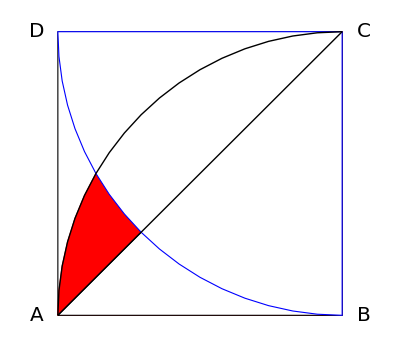

```mathematica
Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{4,4}]},{EdgeForm[{Thick,Red}],FaceForm[Red],Disk[{4,0},4,{π/2,π}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Polygon[{{0,0},{4,0},{4,4}}]},
{EdgeForm[{Thick,Blue}],FaceForm[White],Disk[{4,4},4,{π,3π/2}]},
{Thick,Black,Circle[{4,0},4,{π/2,π}]},{Thick,Black,Line[{{0,0},{4,4}}]},Text[Style["A",20,Black],{-0.3,0}],Text[Style["B",20,Black],{4.3,0}],Text[Style["C",20,Black],{4.3,4}],Text[Style["D",20,Black],{-0.3,4}]}]
```

## Step 1

### Find the area of the red segment: Area of segment = Area of quarter circle - area of Δ ABC = π/4 (4 )^2 - 1/2 (4 ) (4) = 4 ( π - 2 )

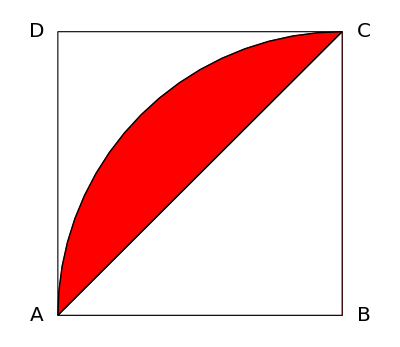

```mathematica
Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{4,4}]},{EdgeForm[{Thick,Red}],FaceForm[Red],Disk[{4,0},4,{π/2,π}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Polygon[{{0,0},{4,0},{4,4}}]},
(*{EdgeForm[{Thick,Blue}],FaceForm[White],Disk[{4,4},4,{π,3π/2}]},*)
{Thick,Black,Circle[{4,0},4,{π/2,π}]},{Thick,Black,Line[{{0,0},{4,4}}]},Text[Style["A",20,Black],{-0.3,0}],Text[Style["B",20,Black],{4.3,0}],Text[Style["C",20,Black],{4.3,4}],Text[Style["D",20,Black],{-0.3,4}]}]
```

## Step 2

### Area of yellow sector with angle = 15 ° or ( π/12 )= 1/24^2 π/12 = (2 π)/3

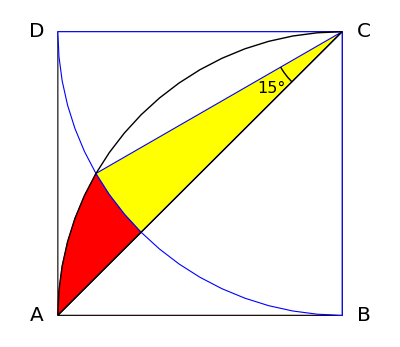

```mathematica
Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{4,4}]},{EdgeForm[{Thick,Red}],FaceForm[Red],Disk[{4,0},4,{π/2,π}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Polygon[{{0,0},{4,0},{4,4}}]},
{EdgeForm[{Thick,Blue}],FaceForm[White],Disk[{4,4},4,{π,3π/2}]},
{EdgeForm[{Thick,Blue}],FaceForm[Yellow],Disk[{4,4},4,{7π/6,5π/4}]},
{Thick,Black,Circle[{4,0},4,{π/2,π}],Circle[{4,4},1,{7π/6,5π/4}]},{Thick,Black,Line[{{0,0},{4,4}}]},Text[Style["A",20,Black],{-0.3,0}],Text[Style["B",20,Black],{4.3,0}],Text[Style["C",20,Black],{4.3,4}],Text[Style["D",20,Black],{-0.3,4}],Text[Style["15°",16,Black],{3,3.2}]}]
```

### Step 3

Area of green segment = area of sector - area of equilateral triangle
				      = 1/2 (4 )^2 π/3 - (√3)/4 ( 4 )^2 = 4 ( (2 π)/3 - √3 )

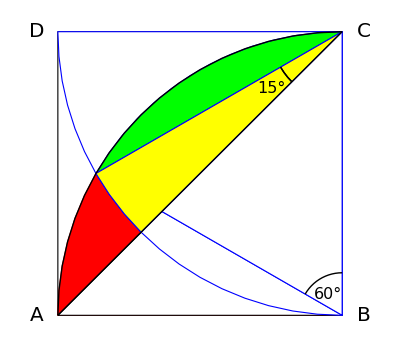

```mathematica
Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{4,4}]},{EdgeForm[{Thick,Red}],FaceForm[Red],Disk[{4,0},4,{π/2,π}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Polygon[{{0,0},{4,0},{4,4}}]},
{EdgeForm[{Thick,Blue}],FaceForm[White],Disk[{4,4},4,{π,3π/2}]},
{EdgeForm[{Thick,Blue}],FaceForm[Green],Disk[{4,0},4,{π/2,5π/6}]},
{EdgeForm[Blue],FaceForm[White],Polygon[{{4,0},{4,4},{4 (1-(√3)/2),2}}]},
{EdgeForm[{Thick,Blue}],FaceForm[Yellow],Disk[{4,4},4,{7π/6,5π/4}]},
{Thick,Black,Circle[{4,0},4,{π/2,π}],Circle[{4,4},1,{7π/6,5π/4}]},
{Thick,Black,Circle[{4,0},0.6,{π/2,5π/6}],Circle[{4,4},1,{7π/6,5π/4}]},{Thick,Black,Line[{{0,0},{4,4}}]},Text[Style["A",20,Black],{-0.3,0}],Text[Style["B",20,Black],{4.3,0}],Text[Style["C",20,Black],{4.3,4}],Text[Style["D",20,Black],{-0.3,4}],Text[Style["15°",16,Black],{3,3.2}],Text[Style["60°",16,Black],{3.8,0.3}]}]
```

## Step 4

### Finally, subtract the sum of the yellow sector and the green segment from the red segment in step 1 Hence The required area = 4 (π - 2 ) - { (2π)/3 + 4 ( (2π)/3 - √3) } = (2 π)/3 - 8 + 4 √3 square units.

```mathematica
Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{4,4}]},{EdgeForm[{Thick,Red}],FaceForm[Red],Disk[{4,0},4,{π/2,π}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Polygon[{{0,0},{4,0},{4,4}}]},
{EdgeForm[{Thick,Blue}],FaceForm[White],Disk[{4,4},4,{π,3π/2}]},
{Thick,Black,Circle[{4,0},4,{π/2,π}]},{Thick,Black,Line[{{0,0},{4,4}}]},Text[Style["A",20,Black],{-0.3,0}],Text[Style["B",20,Black],{4.3,0}],Text[Style["C",20,Black],{4.3,4}],Text[Style["D",20,Black],{-0.3,4}]}]
```

-Graphics-

# Area among curves

## Evaluate the area of the shaded region given that the square has a side length = “a” cm

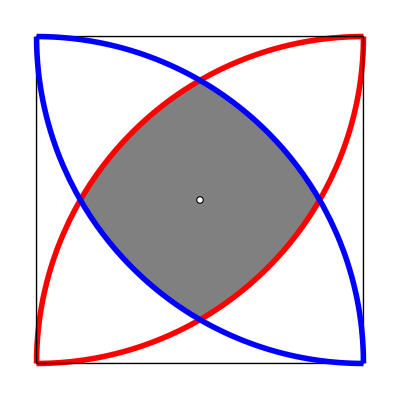

```mathematica
y1=√(2 x -x^2);
y2=1-√(1 -x^2);
y3=√(1-x^2);
y4=1-√(2 x-x^2);
y5=0;
y6=1;
fp1=Plot[{y1,y4},{x,1-(√3)/2,1/2},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Gray,Axes->False];
fp2=Plot[{y3,y2},{x,1/2,(√3)/2},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Gray];
p1=Plot[{y1,y2},{x,0,1},AspectRatio->Automatic,PlotStyle->{{Thickness[0.01],RGBColor[1,0,0]}}];
g1=Graphics[{{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},0.01]},{Thick,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]}}];
p2=Plot[{y3,y4},{x,0,1},PlotStyle->{{Thickness[0.01],RGBColor[0,0,1]}},AspectRatio->Automatic];
Show[fp1,fp2,p1,g1,p2,PlotRange->All]
```

# Trigonometric Solution

Required area = 4 ( Area of a sector with radius” a” and vertex  at (0, 0 )  - area of the yellow triangle with vertex at (0,0)) + area of the square with side length = the base of the triangle.

The base of the triangle = 2 a Sin[ π/12],
		        its height = a sin (π/12).

Area of the sector = 1/2 π/6 a^2 = π/12  a^2 square. units.  
Area of the Δ = 1/2 [2a Sin (π/12)][a Cos (π/12)]=   a^2 Sin (π/12) Cos (π/12) 
=1/2 a^2 Sin (π/6) = 1/4 a^2square. units.  
Area of one DiskSegment = π/12  a^2 - 1/4 a^2 =  (π - 3)/12 a^2 Sq. units.
Area of the square = (2 a Sin ( π/12))^2  = 4 a^2 Sin^2(π/12) =
                                                                               = 2 a^2 (1 - Cos (π/6)) = ( 2 - √3) a^2 Sq. units.

#### Hence, the required area = 4 times area of a diskSegment + area of square = ( (π - 3)/3 + (2 - √3) ) a^2 = (π/3 + 1 - √3) a^2 Sq. units.

```mathematica
Graphics[{FaceForm[{Red,Opacity[0.85]}],DiskSegment[{0,0},1,{π/6,Pi/3}]}]
```

```mathematica
grstep2=Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{1,1}]},{Blue,Circle[{1,1},1,{π,3π/2}],Circle[{0,0},1,{0,π/2}]},{Red,Circle[{1,0},1,{π/2,π}]},{Red,Circle[{0,1},1,{3π/2,2π}]},
{EdgeForm[{Thick,Black}],FaceForm[{Red,Opacity[0.85]}],DiskSegment[{0,0},1,{π/6,Pi/3}],,DiskSegment[{1,0},1,{2π/3,5Pi/6}],DiskSegment[{0,1},1,{5π/3,11Pi/6}],
DiskSegment[{1,1},1,{7π/6,4Pi/3}]},
{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,0},{0.5,(√3)/2},{(√3)/2,0.5}}]},{Black,Arrow[{{0,0},{(√3 + 1)/4, (√3 +1)/4}}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}}];
grstep21 = Graphics[{Inset [Style[TraditionalForm[{(√3)/2 , 0.5 }], 14,Black],{(√3)/2 +0.12, 0.51 }],Inset[Style["{0.5,(√3)/2}",14,Black],{0.5,(√3)/2+0.05}],Inset[Style["90°" ,12,Black],{(√3 + 1)/4-0.06, (√3 +1)/4}],Inset[Style["75°" ,12,Black],{0.51,0.8}],
Inset[Style["15°" ,12,Black],{0.23,0.16}],Inset[Style["15°" ,12,Black],{0.14,0.18}],Inset[Style["h = a Cos(15°)" ,12,Black],{0.5,0.45}],Inset[Rotate[Style["base = 2 a Sin(15°)" ,13,Black],-π/4,{0,0}],{0.76,0.74}]}];
Show [grstep2,grstep21]
```

-Graphics-

# Another Trig. Solution

4 ( Area of a sector with radius 1 and vertex angle = π / 6 - area of two triangles with side lengths 1, (√2)/2, (√3 -1)/2 )
Note that the yellow shaded triangle has a side length one and height = r/2 = (√3 -1)/4, hence: Area of Δ = (√3 -1)/8 sq. units.
Area of the sector = 1/2 π/6 = π/12  square. units.  
Area of one triangle with side length = 1 and height = (√3 -1)/2 Cos [ π/3 ] is equal to:   (√3 -1)/8  square units.
Hence the required area = 4 ( π/12 - 2 area of Δ ) = π/3 - (√3 - 1 ) = π/3 + 1 - √3  Square units as before.

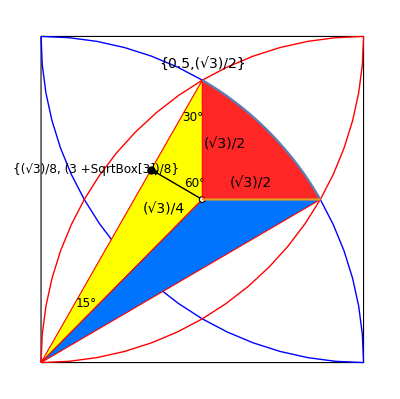

```mathematica
grstep2=Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{1,1}]},{Blue,Circle[{1,1},1,{π,3π/2}],Circle[{0,0},1,{0,π/2}]},{Red,Circle[{1,0},1,{π/2,π}]},{Red,Circle[{0,1},1,{3π/2,2π}]},
{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,0},{0.5,(√3)/2},{0.5,0.5}}]},{EdgeForm[{Thick,Red}],FaceForm[RGBColor[0,0.45,1]],Polygon[{{0,0},{0.5,0.5},{(√3)/2,0.5}}]},{Black,Arrow[{{0.5,0.5},{(√3 + 1)/8, (3 +√3)/8}}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}}];
plot2 = Plot[{√(1-x^2) ,0.5},{x,0.5,(√3)/2},Filling->{1->{2}},FillingStyle->Directive[Red,Opacity[0.85]]];
grstep21 = Graphics[{Inset [Style[" (√3)/2", 14,Black],{0.65,0.55}],PointSize[0.015],Point[{(√3 + 1)/8, (3 +√3)/8}],Inset[Style["{(√3)/8, (3 +SqrtBox[3])/8}",12,Black],{(√3 + 1)/8-0.17, (3 +√3)/8}],Inset[Style["{0.5,(√3)/2}",14,Black],{0.5,(√3)/2+0.05}],Inset[Style["30°" ,12,Black],{0.47,0.75}],Inset[Style["60°" ,12,Black],{0.475,0.55}],Inset[Style["15°" ,12,Black],{0.14,0.18}],Inset[Style["(√3)/4" ,14,Black],{0.38,0.47}],Inset[Style["(√3)/2" ,14,Black],{0.57,0.67}]}];
Show [grstep2,plot2,grstep21]
```

# Use Geometry to find the area among four curves

# Summarizing the steps in pieces.

## Putting all 6 steps together in one show :

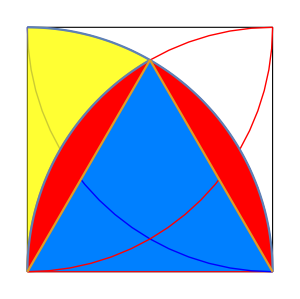
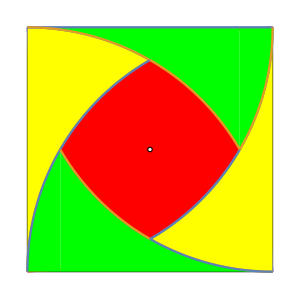

```mathematica
grsteps=Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{1,1}]},{EdgeForm[{Thick,Red}],FaceForm[RGBColor[0,0.5,1]],Polygon[{{0,0},{0.5,√3/2},{1,0}}]},{Blue,Circle[{1,1},1,{π,3π/2}],Circle[{0,0},1,{0,π/2}]},Red,Circle[{1,0},1,{π/2,π}],{Red,Circle[{0,1},1,{3π/2,2π}]}}];
plts=Plot[{√(1-(x-1)^2), √3 x},{x,0,0.5},Filling->{1->{2}},FillingStyle->Red];
plots1=Plot[{√(1-(x)^2), -√3(x-1)},{x,0.5,1},Filling->{1->{2}},FillingStyle->Red];
plts2=Plot[{√(1-x^2),√(1-(x-1)^2)},{x,0,0.5},Filling->{1->{2}},FillingStyle->Directive[Yellow,Opacity[0.8]]];

(* Final picture  deduct four times the yellow area from the area of the square *)
grstep4=Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{1,1}]},{Blue,Circle[{1,1},1,{π,3π/2}],Circle[{0,0},1,{0,π/2}]},Red,Circle[{1,0},1,{π/2,π}],{Red,Circle[{0,1},1,{3π/2,2π}]}}];
plt41=Plot[{√(1-x^2),√(1-(x-1)^2)},{x,0,0.5},Filling->{1->{2}},FillingStyle->Yellow];
plt412=Plot[{1-√(1-x^2),1-√(1-(x-1)^2)},{x,0.5,1},Filling->{1->{2}},FillingStyle->Yellow];
plt42=Plot[{1,√(1-x^2)},{x,0,√3/2},Filling->{1->{2}},FillingStyle->Green];
plt421=Plot[{1,1-√(1-x^2)},{x,√3/2,1},Filling->{1->{2}},FillingStyle->Green];
plt43=Plot[{1-√(1-(x-1)^2)},{x,1-√3/2,1},Filling->Axis,FillingStyle->Green];
plt44=Plot[{√(1-(x-1)^2)},{x,0,1-√3/2},Filling->Axis,FillingStyle->Green];

p451=Plot[{√(2 x-x^2) ,1-√(2 x-x^2)},{x,1-(√3)/2,1/2},Filling->{1->{2}},FillingStyle->Red,AspectRatio->Automatic,Axes->True,AxesOrigin->{0,0}];
p452=Plot[{1-√(1-x^2) ,√(1-x^2)},{x,1/2,(√3)/2},Filling->{1->{2}},FillingStyle->Red,AspectRatio->Automatic];
gr46=Graphics[{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}];
Row[{

Show[grsteps,plots1,plts2,plts,ImageSize->300],Spacer[30],Show[grstep4,plt41,plt412,plt42,plt421,plt43,plt44,p451,p452,gr46,ImageSize->300]
}]
```

## Solving by Integration

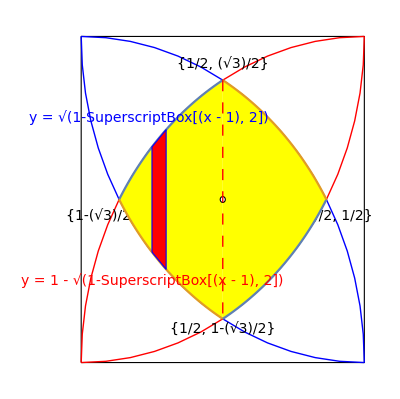

```mathematica
grstep0=Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{1,1}]},{Blue,Circle[{1,1},1,{π,3π/2}],Circle[{0,0},1,{0,π/2}]},Red,Circle[{1,0},1,{π/2,π}],{Red,Circle[{0,1},1,{3π/2,2π}]},{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}}];
plothI=Plot[{√(2 x-x^2) ,1-√(2 x-x^2)},{x,1-(√3)/2,1/2},Filling->{1->{2}},FillingStyle->Yellow,AspectRatio->Automatic,Axes->True,AxesOrigin->{0,0}];
plothI1=Plot[{1-√(1-x^2) ,√(1-x^2)},{x,1/2,(√3)/2},Filling->{1->{2}},FillingStyle->Yellow,AspectRatio->Automatic];
grstepIntg=Graphics[{EdgeForm[{Thick,Blue}],FaceForm[Red],Polygon[{{0.25,1-√(0.5- 0.0625)},{0.25,√(0.5-0.25^2)},{0.3,√(0.6- (0.3)^2)},{0.3,1-√(0.6-0.3^2)}}],{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]},{Red,Dashing[0.02],Line[{{1/2, (√3)/2},{1/2, 1-(√3)/2}}]},Inset[Style["{1/2, (√3)/2}",14,Black],{0.5,(√3)/2+0.05}],Inset[Style["{1/2, 1-(√3)/2}",14,Black],{0.5,1-(√3)/2-0.03}],Inset[Style["{1-(√3)/2, 1/2}",14,Black],{1-(√3)/2,0.45}],
Inset[Style["{(√3)/2, 1/2}",14,Black],{(√3)/2,0.45}],
Inset[Style["y = √(1-SuperscriptBox[(x - 1), 2])",14,Blue],{0.24,0.75}],
Inset[Style["y = 1 - √(1-SuperscriptBox[(x - 1), 2])",14,Red],{0.25,0.25}]
}];
Show[grstep0,plothI,plothI1,grstepIntg]
```

## Putting every thing within Manipulate

```mathematica
main=Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{1,1}]},{Thick,Blue,Circle[{1,1},1,{π,3π/2}],Circle[{0,0},1,{0,π/2}]},{Thick,Red,Circle[{1,0},1,{π/2,π}]},{Thick,Red,Circle[{0,1},1,{3π/2,2π}]}
},Axes->True,AxesOrigin->{0,0}];
Leftshade=Plot[{√(2 x-x^2) ,1-√(2 x-x^2)},{x,1-(√3)/2,1/2},Filling->{1->{2}},FillingStyle->Gray,AspectRatio->Automatic,Axes->True,AxesOrigin->{0,0}];
Rightshade=Plot[{1-√(1-x^2) ,√(1-x^2)},{x,1/2,(√3)/2},Filling->{1->{2}},FillingStyle->Gray,AspectRatio->Automatic];
gCenter=Graphics[{{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},0.01]},{Thick,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]}}];
areaSeg=0.5(1)π/6.;
areaTriangle=Sin[π/12.]Cos[π/12.];
RedAreas=4.(areaSeg - areaTriangle);
RequiredAreaSqr=RedAreas+(2 Sin[π/12.])^2;
YellowAreaSqr =FullSimplify[ 2. (∫_(1-(√3)/2)^(1/2) (√(1-(x-1)^2)-(1 - √(1-(x-1)^2)))ⅆx)];

(*Trig Solution #1 *)
sol1Step1=Graphics[{
{EdgeForm[{Thick,Black}],
FaceForm[{Red,Opacity[0.85]}],
DiskSegment[{0,0},1,{π/6,Pi/3}],,
DiskSegment[{1,0},1,{2π/3,5Pi/6}],
DiskSegment[{0,1},1,{5π/3,11Pi/6}],
DiskSegment[{1,1},1,{7π/6,4Pi/3}]},
{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,0},{0.5,(√3)/2},{(√3)/2,0.5}}]},{Black,Arrow[{{0,0},{(√3 + 1)/4, (√3 +1)/4}}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}}];
sol1Step2 = Graphics[{Inset [Style[TraditionalForm[{(√3)/2 , 0.5 }], 14,Black],{(√3)/2 +0.12, 0.51 }],Inset[Style["{0.5,(√3)/2}",14,Black],{0.5,(√3)/2+0.05}],Inset[Style["90°" ,12,Black],{(√3 + 1)/4-0.06, (√3 +1)/4}],Inset[Style["75°" ,12,Black],{0.51,0.8}],
Inset[Style["15°" ,12,Black],{0.23,0.16}],Inset[Style["15°" ,12,Black],{0.14,0.18}],Inset[Style["h = a Cos(15°)" ,12,Black],{0.5,0.45}],Inset[Rotate[Style["base = 2 a Sin(15°)" ,13,Black],-π/4,{0,0}],{0.76,0.74}]}];
(*sol1= Show [main,sol1Step1,sol1Step2];*)

(*Trigonometric Solution Method # 2 *)
sol2Step1=Graphics[{
{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,0},{0.5,(√3)/2},{0.5,0.5}}]},{EdgeForm[{Thick,Red}],FaceForm[RGBColor[0,0.45,1]],Polygon[{{0,0},{0.5,0.5},{(√3)/2,0.5}}]},{Black,Arrow[{{0.5,0.5},{(√3 + 1)/8, (3 +√3)/8}}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}}];
plot2 = Plot[{√(1-x^2) ,0.5},{x,0.5,(√3)/2},Filling->{1->{2}},FillingStyle->Directive[Red,Opacity[0.85]]];
sol2Step2 = Graphics[{Inset [Style[" (√3)/2", 14,Black],{0.65,0.55}],PointSize[0.015],Point[{(√3 + 1)/8, (3 +√3)/8}],Inset[Style["{(√3)/8, (3 + SqrtBox[3])/8}",12,Black],{(√3 + 1)/8-0.17, (3 +√3)/8}],Inset[Style["{0.5,(√3)/2}",14,Black],{0.5,(√3)/2+0.05}],Inset[Style["30°" ,12,Black],{0.47,0.75}],Inset[Style["60°" ,12,Black],{0.475,0.55}],Inset[Style["15°" ,12,Black],{0.14,0.18}],Inset[Style["(√3)/2" ,14,Black],{0.45,0.65}]}];
(*sol2 = Show [main,sol2Step1,plot2,sol2Step2];*)

(* Trigonometric Solution Sol # 3 *)

triangle = Graphics[{{EdgeForm[{Thick,Red}],FaceForm[RGBColor[0,0.5,1]],Polygon[{{0,0},{0.5,√3/2},{1,0}}]}}];
cresentR=Plot[{√(1-(x-1)^2), √3 x},{x,0,0.5},Filling->{1->{2}},FillingStyle->Red];
cresentL=Plot[{√(1-(x)^2), -√3(x-1)},{x,0.5,1},Filling->{1->{2}},FillingStyle->Red];
yellowAreaL=Plot[{√(1-x^2),√(1-(x-1)^2)},{x,0,0.5},Filling->{1->{2}},FillingStyle->Directive[Yellow,Opacity[1]]];
sol3Step1={triangle, cresentR, cresentL, yellowAreaL};
(* Final picture  deduct four times the yellow area from the area of the square *)


(*plt41=Plot[{√(1-x^2),√(1-(x-1)^2)},{x,0,0.5},Filling->{1->{2}},FillingStyle->Yellow];*)
yellowAreaR=Plot[{1-√(1-x^2),1-√(1-(x-1)^2)},{x,0.5,1},Filling->{1->{2}},FillingStyle->Yellow];
GreenAreaTop1=Plot[{1,√(1-x^2)},{x,0,√3/2},Filling->{1->{2}},FillingStyle->Green];
GreenAreaTop2=Plot[{1,1-√(1-x^2)},{x,√3/2,1},Filling->{1->{2}},FillingStyle->Green];
GreenAreaBottom1=Plot[{1-√(1-(x-1)^2)},{x,1-√3/2,1},Filling->Axis,FillingStyle->Green];
GreenAreaBottom2=Plot[{√(1-(x-1)^2)},{x,0,1-√3/2},Filling->Axis,FillingStyle->Green];

RedCenterTop=Plot[{√(2 x-x^2) ,1-√(2 x-x^2)},{x,1-(√3)/2,1/2},Filling->{1->{2}},FillingStyle->Red,AspectRatio->Automatic,Axes->True,AxesOrigin->{0,0}];
RedCenterBottom=Plot[{1-√(1-x^2) ,√(1-x^2)},{x,1/2,(√3)/2},Filling->{1->{2}},FillingStyle->Red,AspectRatio->Automatic];
CenterDot=Graphics[{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}];

sol3Step2 = {yellowAreaL, yellowAreaR, GreenAreaTop1, GreenAreaTop2, GreenAreaBottom1, GreenAreaBottom2, RedCenterTop, RedCenterBottom, CenterDot};

(*sol3=Row[{
Show[main,sol3Step1,ImageSize->300],Spacer[30],
Show[main,sol3Step2,ImageSize->300]*)


(* Solution 4 Solving by Integration  *)
LeftPart=Plot[{√(2 x-x^2) ,1-√(2 x-x^2)},{x,1-(√3)/2,1/2},Filling->{1->{2}},FillingStyle->Yellow,AspectRatio->Automatic,Axes->True,AxesOrigin->{0,0}];
RightPart=Plot[{1-√(1-x^2) ,√(1-x^2)},{x,1/2,(√3)/2},Filling->{1->{2}},FillingStyle->Yellow,AspectRatio->Automatic];
graphIntg=Graphics[{EdgeForm[{Thick,Blue}],FaceForm[Red],Polygon[{{0.25,1-√(0.5- 0.0625)},{0.25,√(0.5-0.25^2)},{0.3,√(0.6- (0.3)^2)},{0.3,1-√(0.6-0.3^2)}}],{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]},{Red,Dashing[0.02],Line[{{1/2, (√3)/2},{1/2, 1-(√3)/2}}]},Inset[Style["{1/2, (√3)/2}",14,Black],{0.5,(√3)/2+0.05}],Inset[Style["{1/2, 1-(√3)/2}",14,Black],{0.5,1-(√3)/2-0.03}],Inset[Style["{1-(√3)/2, 1/2}",14,Black],{1-(√3)/2,0.45}],
Inset[Style["{(√3)/2, 1/2}",14,Black],{(√3)/2,0.45}],
Inset[Style["y = √(1 - SuperscriptBox[(x - 1), 2])",14,Blue],{0.24,0.75}],
Inset[Style["y = 1 - √(1 - SuperscriptBox[(x - 1), 2])",14,Red],{0.25,0.25}]
}];
YellowArea =FullSimplify[ 2. (∫_(1-(√3)/2)^(1/2) (√(1-(x-1)^2)-(1 - √(1-(x-1)^2)))ⅆx)];
(*Integration=Show[main,LeftPart,RightPart,graphIntg,PlotRange->All];*)


Manipulate[
Column[{
Item[If[answer,Style[Row[{"\nShaded Area = ",NumberForm[RequiredAreaSqr,{5,3}]," cm^2 \nOr By Integration: Area = ",HoldForm[ 2 (∫_(1-(√3)/2)^(1/2) (√(1-(x-1)^2)-(1 - √(1-(x-1)^2)))ⅆx)]," = ",YellowAreaSqr,"\n"}],16,Black],Style["\nCalculate the shaded Area, given that the side length\n of the square is 1 cm \n",16,Black]],Frame->True,Alignment->Left],
Item[
Which[sol==0,Show[main,Leftshade,Rightshade,gCenter,ImageSize->400,PlotRange->All],sol==1,Show [main,sol1Step1,sol1Step2,gCenter,ImageSize->400],sol==2, Show [main,sol2Step1,plot2,sol2Step2,ImageSize->400],sol==3,Row[{
Show[main,sol3Step1,gCenter,ImageSize->400],Spacer[30],
Show[main,sol3Step2,gCenter,ImageSize->400] }],True,Show[main,LeftPart,RightPart,graphIntg,gCenter,ImageSize->400,PlotRange->All]
],Frame->True,Alignment->{Center}]
}],

Row[{

Control[{{sol,0,"Prblm"},{0->"",1->"sol1",2->"sol2",3->"sol3",4->"sol4"},ControlType->RadioButtonBar}],Spacer[21],Control[{{answer,False,"Answer"},{False,True}}]}],TrackedSymbols:>{sol,answer},SaveDefinitions->True]
```

```mathematica
r=1.;areaSeg=FullSimplify[ 1/2 (√2. r )^2 π/6 - 1/2 (√3. - 1 ) r ((√3 + 1)/2 ) r];
requiredArea1= FullSimplify[(√3. - 1. )^2 r^2 + 4 FullSimplify[ 1/2 (√2 r )^2 π/6. - 1/2 (√3 - 1 ) r ((√3. + 1)/2 ) r]];
```

```mathematica
YellowArea =FullSimplify[ 2. (∫_(1-(√3)/2)^(1/2) (√(1-(x-1)^2)-(1 - √(1-(x-1)^2)))ⅆx)]
```

0.315147

```mathematica
y1=√(2 x -x^2);
y2=1-√(1 -x^2);
y3=√(1-x^2);
y4=1-√(2 x-x^2);
ShadedArea2:=FullSimplify[ 2. (∫_(1-(√3)/2)^(1/2) (√(1-(x-1)^2)-(1 - √(1-(x-1)^2)))ⅆx)]-π (1-√2/2.)^2;

fp1=Plot[{y1,y4},{x,1-(√3)/2,1/2},Filling->{1->{2}},FillingStyle->Gray,AxesOrigin->{0,0},Axes->False,PlotLabel->Style["\nCalculate the shaded area\n",24,Italic,Black]];
g1=Graphics[{{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},0.01]},{Thick,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]}}];
g2=Graphics[{{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},1-√2/2.]},{Red,PointSize[0.025],Point[{0.5,0.5}]}(*{Thick,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]}*)}];
fp2=Plot[{y3,y2},{x,1/2,(√3)/2},Filling->{1->{2}},FillingStyle->Gray];
p1=Plot[{y1,y2},{x,0,1},PlotStyle->{{Thickness[0.01],RGBColor[1,0,0]}}];
p2=Plot[{y3,y4},{x,0,1},PlotStyle->{{Thickness[0.01],RGBColor[0,0,1]}}];
Manipulate[Column[{
Item[If[answer,Style[Row[{"\nShaded area = ", NumberForm[ShadedArea2,{4,2}]," cm^2\n"}],24,Black],Style["\nCalculate the shaded area\n",24,Italic,Black]],Alignment->{Left},Frame->True],
Item[
Show[fp1,fp2,p1,p2,g2,PlotRange->All,AspectRatio->Automatic,ImageSize->{450,400}],Alignment->{Center},Frame->True]
}],
{{answer,False,"Answer"},{False,True}},TrackedSymbols->{answer}]
```

# Similar problem

```mathematica
Manipulate[
areaseg=0.5 2 π/6;
areaTriangle=(√3-1.)√2. Cos[π/12.]/2;
AreaRedSegment = areaseg-areaTriangle;
RequiredArea=4 AreaRedSegment+(√3.-1)^2.;

Column[{
Item[
If[answer,Style[Row[{"\nShaded area = 4 Area Red Segment + area yellow Sqr. = ",NumberForm[RequiredArea,{5,3}]," cm^2\nShaded area = ",HoldForm[4 (∫_((-1+√3.)/2)^(√2-1) √(2.-(x+1)^2)ⅆx + ∫_0^((-1+√3.)/2) (-1.+√(2-x^2))ⅆx)]," = ",4 (∫_((-1+√3.)/2)^(√2.-1) √(2.-(x+1)^2)ⅆx + ∫_0^((-1+√3.)/2.) (-1.+√(2-x^2))ⅆx),"\n"}],14,Black,Italic],Style["\nClculate the shaded area\n" ,14,Black]],Frame->True,Alignment->Left],
Item[
pHorizontal=Plot[Tooltip[{√(1-x^2),-√(1-x^2),-1+√(2-x^2),1-√(2-x^2)}],{x,-1,1},AspectRatio->Automatic];
pVerticalLeft=Plot[Tooltip[{√(2-(x-1)^2),-√(2-(x-1)^2)}],{x,1-√2,0},AspectRatio->Automatic];
pVerticalRT=Plot[Tooltip[{√(2-(x+1)^2),-√(2-(x+1)^2)}],{x,0,-1+√2},AspectRatio->Automatic];
filling=Graphics[{{PointSize[0.02],Black,Point[{1/2 (1-√3),(√3-1)/2}],Point[{(√3-1)/2,(√3-1)/2}],Point[{√2-1,0}]},{EdgeForm[{Thick,Red}],FaceForm[Yellow],

Text[Style[TraditionalForm[{(1-√3)/2,(√3-1)/2}],12,Black],{-0.65,0.42}],
Text[Style[TraditionalForm[{(√3-1)/2,-(√3-1)/2}],12,Black],{-0.67,-0.41}],

Polygon[{{1/2 (1-√3),(√3-1)/2},{1/2 (1-√3),-(√3-1)/2},{1/2 (-1+√3),-(√3-1)/2},{1/2 (-1+√3),(√3-1)/2}}]},{Black,Dashing[0.02],Line[{{1,0},{1/2 (1-√3),(√3-1)/2}}],Line[{{1,0},{1/2 (1-√3),-(√3-1)/2}}]}
}];
ds=DiskSegment[{1,0},√2,{11π/12,13π/12}];
fourds=Graphics[{EdgeForm[{Thick,Black}],FaceForm[Red],ds,Rotate[ds,π/2,{0,0}],Rotate[ds,-π/2,{0,0}],Rotate[ds,π,{0,0}]}];

Show[pHorizontal,pVerticalLeft,pVerticalRT,filling,fourds,PlotRange->All,ImageSize->500],Frame->True,Alignment->{Center}]
}],
{{answer,False,"Answer"},{False,True}}]
```

```mathematica
main=Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{1,1}]},{Blue,Circle[{1,1},1,{π,3π/2}],Circle[{0,0},1,{0,π/2}]},{Red,Circle[{1,0},1,{π/2,π}]},{Red,Circle[{0,1},1,{3π/2,2π}]},


{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}},Axes->True,AxesOrigin->{0,0}];

(*Trig Solution #1 *)
sol1Step1=Graphics[{
{EdgeForm[{Thick,Black}],
FaceForm[{Red,Opacity[0.85]}],
DiskSegment[{0,0},1,{π/6,Pi/3}],,
DiskSegment[{1,0},1,{2π/3,5Pi/6}],
DiskSegment[{0,1},1,{5π/3,11Pi/6}],
DiskSegment[{1,1},1,{7π/6,4Pi/3}]},
{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,0},{0.5,(√3)/2},{(√3)/2,0.5}}]},{Black,Arrow[{{0,0},{(√3 + 1)/4, (√3 +1)/4}}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}}];
sol1Step2 = Graphics[{Inset [Style[TraditionalForm[{(√3)/2 , 0.5 }], 14,Black],{(√3)/2 +0.12, 0.51 }],Inset[Style["{0.5,(√3)/2}",14,Black],{0.5,(√3)/2+0.05}],Inset[Style["90°" ,12,Black],{(√3 + 1)/4-0.06, (√3 +1)/4}],Inset[Style["75°" ,12,Black],{0.51,0.8}],
Inset[Style["15°" ,12,Black],{0.23,0.16}],Inset[Style["15°" ,12,Black],{0.14,0.18}],Inset[Style["h = a Cos(15°)" ,12,Black],{0.5,0.45}],Inset[Rotate[Style["base = 2 a Sin(15°)" ,13,Black],-π/4,{0,0}],{0.76,0.74}]}];
(*sol1= Show [main,sol1Step1,sol1Step2];*)

(*Trigonometric Solution Method # 2 *)
sol2Step1=Graphics[{
{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,0},{0.5,(√3)/2},{0.5,0.5}}]},{EdgeForm[{Thick,Red}],FaceForm[RGBColor[0,0.45,1]],Polygon[{{0,0},{0.5,0.5},{(√3)/2,0.5}}]},{Black,Arrow[{{0.5,0.5},{(√3 + 1)/8, (3 +√3)/8}}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}}];
plot2 = Plot[{√(1-x^2) ,0.5},{x,0.5,(√3)/2},Filling->{1->{2}},FillingStyle->Directive[Red,Opacity[0.85]]];
sol2Step2 = Graphics[{Inset [Style[" (√3)/2", 14,Black],{0.65,0.55}],PointSize[0.015],Point[{(√3 + 1)/8, (3 +√3)/8}],Inset[Style["{(√3)/8, (3 + SqrtBox[3])/8}",12,Black],{(√3 + 1)/8-0.17, (3 +√3)/8}],Inset[Style["{0.5,(√3)/2}",14,Black],{0.5,(√3)/2+0.05}],Inset[Style["30°" ,12,Black],{0.47,0.75}],Inset[Style["60°" ,12,Black],{0.475,0.55}],Inset[Style["15°" ,12,Black],{0.14,0.18}],Inset[Style["0.5 r" ,14,Black],{0.4,0.52}],Inset[Style["(√3)/2" ,14,Black],{0.52,0.65}]}];
(*sol2 = Show [main,sol2Step1,plot2,sol2Step2];*)

(* Trigonometric Solution Sol # 3 *)
triangle = Graphics[{{EdgeForm[{Thick,Red}],FaceForm[RGBColor[0,0.5,1]],Polygon[{{0,0},{0.5,√3/2},{1,0}}]}}];
cresentR=Plot[{√(1-(x-1)^2), √3 x},{x,0,0.5},Filling->{1->{2}},FillingStyle->Red];
cresentL=Plot[{√(1-(x)^2), -√3(x-1)},{x,0.5,1},Filling->{1->{2}},FillingStyle->Red];
yellowAreaL=Plot[{√(1-x^2),√(1-(x-1)^2)},{x,0,0.5},Filling->{1->{2}},FillingStyle->Directive[Yellow,Opacity[1]]];
sol3Step1={triangle, cresentR, cresentL, yellowAreaL};
(* Final picture  deduct four times the yellow area from the area of the square *)


(*plt41=Plot[{√(1-x^2),√(1-(x-1)^2)},{x,0,0.5},Filling->{1->{2}},FillingStyle->Yellow];*)
yellowAreaR=Plot[{1-√(1-x^2),1-√(1-(x-1)^2)},{x,0.5,1},Filling->{1->{2}},FillingStyle->Yellow];
GreenAreaTop1=Plot[{1,√(1-x^2)},{x,0,√3/2},Filling->{1->{2}},FillingStyle->Green];
GreenAreaTop2=Plot[{1,1-√(1-x^2)},{x,√3/2,1},Filling->{1->{2}},FillingStyle->Green];
GreenAreaBottom1=Plot[{1-√(1-(x-1)^2)},{x,1-√3/2,1},Filling->Axis,FillingStyle->Green];
GreenAreaBottom2=Plot[{√(1-(x-1)^2)},{x,0,1-√3/2},Filling->Axis,FillingStyle->Green];

RedCenterTop=Plot[{√(2 x-x^2) ,1-√(2 x-x^2)},{x,1-(√3)/2,1/2},Filling->{1->{2}},FillingStyle->Red,AspectRatio->Automatic,Axes->True,AxesOrigin->{0,0}];
RedCenterBottom=Plot[{1-√(1-x^2) ,√(1-x^2)},{x,1/2,(√3)/2},Filling->{1->{2}},FillingStyle->Red,AspectRatio->Automatic];
CenterDot=Graphics[{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}];

sol3Step2 = {yellowAreaL, yellowAreaR, GreenAreaTop1, GreenAreaTop2, GreenAreaBottom1, GreenAreaBottom2, RedCenterTop, RedCenterBottom, CenterDot};

(*sol3=Row[{
Show[main,sol3Step1,ImageSize->300],Spacer[30],
Show[main,sol3Step2,ImageSize->300]*)


(*Solving by Integration *)
LeftPart=Plot[{√(2 x-x^2) ,1-√(2 x-x^2)},{x,1-(√3)/2,1/2},Filling->{1->{2}},FillingStyle->Yellow,AspectRatio->Automatic,Axes->True,AxesOrigin->{0,0}];
RightPart=Plot[{1-√(1-x^2) ,√(1-x^2)},{x,1/2,(√3)/2},Filling->{1->{2}},FillingStyle->Yellow,AspectRatio->Automatic];
graphIntg=Graphics[{EdgeForm[{Thick,Blue}],FaceForm[Red],Polygon[{{0.25,1-√(0.5- 0.0625)},{0.25,√(0.5-0.25^2)},{0.3,√(0.6- (0.3)^2)},{0.3,1-√(0.6-0.3^2)}}],{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]},{Red,Dashing[0.02],Line[{{1/2, (√3)/2},{1/2, 1-(√3)/2}}]},Inset[Style["{1/2, (√3)/2}",14,Black],{0.5,(√3)/2+0.05}],Inset[Style["{1/2, 1-(√3)/2}",14,Black],{0.5,1-(√3)/2-0.03}],Inset[Style["{1-(√3)/2, 1/2}",14,Black],{1-(√3)/2,0.45}],
Inset[Style["{(√3)/2, 1/2}",14,Black],{(√3)/2,0.45}],
Inset[Style["y = √(1 - SuperscriptBox[(x - 1), 2])",14,Blue],{0.24,0.75}],
Inset[Style["y = 1 - √(1 - SuperscriptBox[(x - 1), 2])",14,Red],{0.25,0.25}]
}];
YellowArea =FullSimplify[ 2. (∫_(1-(√3)/2)^(1/2) (√(1-(x-1)^2)-(1 - √(1-(x-1)^2)))ⅆx)];
(*Integration=Show[main,LeftPart,RightPart,graphIntg,PlotRange->All];*)


Manipulate[

Which[sol==0,Show[main],sol==1,Show [main,sol1Step1,sol1Step2],sol==2, Show [main,sol2Step1,plot2,sol2Step2],sol==3,Row[{
Show[main,sol3Step1,ImageSize->300],Spacer[30],
Show[main,sol3Step2,ImageSize->300] }],True,Show[main,LeftPart,RightPart,graphIntg,PlotRange->All]
],


(*Which[sol==3,Show[p0,p1,p2,p3,p4,p5,p6,p7,gslice3,AspectRatio->Automatic,ImageSize->Medium],
sol==2,Show[p0,p1,p2,p3,p4,p5,p6,p7,gslice,AspectRatio->Automatic,ImageSize->Medium],sol==1,Show[gsol1,psol1,psoln1,AspectRatio->Automatic,ImageSize->Medium],sol==0,
Show[p0,p1,p2,p3,p4,p5,p6,p7,AspectRatio->Automatic(*PlotRange->{{-5,5},{-5,8}}*),ImageSize->Medium]]*,Alignment->{Center},Frame->True]*)

Row[{
Control[{{sol,0,"Prblm"},{0->"",1->"sol1",2->"sol2",3->"sol3",4->"sol4"},ControlType->RadioButtonBar}]}],TrackedSymbols:>{sol},SaveDefinitions->True]
```

Show::gcomb: Could not combine the graphics objects in Show[main,sol3Step1,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[main,sol3Step2,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[main,sol3Step1,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[main,sol3Step2,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[main,sol3Step1,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[main,sol3Step2,ImageSize→300].

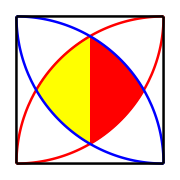
-Graphics--Graphics-

```mathematica
pl1=Plot[{√(2 x-x^2) ,1-√(2 x-x^2)},{x,1-(√3)/2,1/2},Filling->{1->{2}},FillingStyle->Yellow,AspectRatio->Automatic];
pl2=Plot[{1-√(1-x^2) ,√(1-x^2)},{x,1/2,(√3)/2},Filling->{1->{2}},FillingStyle->Red,AspectRatio->Automatic];
pl3=Plot[{√(2 x-x^2) ,1-√(1-x^2)},{x,0,1},PlotStyle->{{Thickness[0.01],RGBColor[1,0,0]}},AspectRatio->Automatic];
pl4=Plot[{√(1-x^2) ,1-√(2 x-x^2)},{x,0,1},PlotStyle->{{Thickness[0.01],RGBColor[0,0,1]}},AspectRatio->Automatic];
pl5=Plot[{0 ,1},{x,0,1},PlotStyle->{{Thickness[0.01],Black}},AspectRatio->Automatic];
pl6=ParametricPlot[{0,t},{t,0,1},PlotStyle->{Thickness[0.01],Black},AspectRatio->Automatic];
pl7=ParametricPlot[{1,t},{t,0,1},PlotStyle->{{Thickness[0.01],Black}},AspectRatio->Automatic];
Row[{Show[pl1,pl2,pl3,pl4,pl5,pl6,pl7,PlotRange->All,Axes->False,AspectRatio->Automatic,ImageSize->Small],,Spacer[20],
Rotate[Show[pl1,pl2,pl3,pl4,pl5,pl6,pl7,PlotRange->All,Axes->False,AspectRatio->Automatic,ImageSize->Small],-45 Degree]}]
```

# Tangent to a circle version 3 2 - 23 - 13 with fixed radius

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
g:= cntrpt[[1]];
h:=cntrpt[[2]];
r:=√40.;
Subscript[x, 0]:=Subscript[P, 0][[1]];
Subscript[y, 0]:=Subscript[P, 0][[2]];
(* d =Distance from the point to the center of circle *)
d:=Sqrt[(Subscript[x, 0]-g)^2 + (Subscript[y, 0] -h)^2 ];
(* Subscript[T, 1] and Subscript[T, 2]  are the lengths of the tangent lines from point Subscript[P, 0] (Subscript[x, 0], Subscript[y, 0]).  
If Subscript[T, 1] = 0, then the point Subscript[P, 0](Subscript[x, 0], Subscript[y, 0]) is on the circle.  In which case we need to check if it is at (g+r,h}, (g-r,h ), where the tangent lines are vetical lines (One tangent), or Subscript[P, 0](Subscript[x, 0], Subscript[y, 0]) is at (g, h+r ) or (g, h-r) where the tangent lines are horizontal lines. Otherwise, if Subscript[P, 0] is at any other points on the circle, the slope of the one tangent line is m =(g-Subscript[x, 0] )/(y-h)*)
Subscript[T, 1]:=Sqrt[Abs[(Subscript[x, 0]-g)^2+(Subscript[y, 0]-h)^2-r^2]];
Subscript[T, 2]:=-Sqrt[Abs[(Subscript[x, 0]-g)^2+(Subscript[y, 0]-h)^2-r^2]];
(*{Subscript[a, 1],Subscript[b, 1]} and {Subscript[a, 2],Subscript[b, 2]}are the coordinates of the tangent points at points Subscript[P, 1] and Subscript[P, 2] *)
Subscript[a, 1]:=g+(r^2 Subscript[x, 0]+r h Subscript[T, 1]-r^2 g-r Subscript[T, 1] Subscript[y, 0])/(Subscript[T, 1]^2 + r^2);
Subscript[b, 1]:=(r Subscript[T, 1] Subscript[x, 0] + r^2 Subscript[y, 0]+h Subscript[T, 1]^2-r Subscript[T, 1] g)/ (Subscript[T, 1]^2 + r^2);
Subscript[a, 2]:=g+(r^2 Subscript[x, 0]+r h Subscript[T, 2]-r^2 g-r Subscript[T, 2] Subscript[y, 0])/(Subscript[T, 2]^2 + r^2);
Subscript[b, 2]:=(r Subscript[T, 2] Subscript[x, 0] + r^2 Subscript[y, 0]+ h Subscript[T, 2]^2-r Subscript[T, 2] g)/ (Subscript[T, 2]^2 + r^2);
If[d>r&&Subscript[x, 0]≠Subscript[a, 1],Subscript[m, 1]:=Quiet[(Subscript[y, 0]-Subscript[b, 1])/(Subscript[x, 0]-Subscript[a, 1])]];
If[d>r&&Subscript[x, 0]≠Subscript[a, 2],Subscript[m, 2]:=Quiet[(Subscript[y, 0]-Subscript[b, 2])/(Subscript[x, 0]-Subscript[a, 2])]];
(*If[Subscript[x, 0]<0,theta:=π+ArcTan[(1+Subscript[m, 2] Subscript[m, 1]),(Subscript[m, 2]-Subscript[m, 1])],*)If[d==r,theta:=Abs[ArcTan[(-(Subscript[x, 0]-g))/(Subscript[y, 0]-h)]],theta:=Abs[ArcTan[(1+Subscript[m, 2] Subscript[m, 1]),(Subscript[m, 2]-Subscript[m, 1])]]];
(* If there is only one tangent and it is vertical theta = 0 
If the point is on the corner, the angle between the two tangents is π/2 *)
Which[
Subscript[x, 0]==g-r&&Subscript[y, 0]==h||
Subscript[x, 0]==g+r&&Subscript[y, 0]==h||
Subscript[x, 0]==g&&Subscript[y, 0]==(h+r)||
Subscript[x, 0]==g&&Subscript[y, 0]==(h-r),theta:= 0.,
Subscript[x, 0]==(g-r)&&Subscript[y, 0]==(h-r)||
Subscript[x, 0]==(g-r)&&Subscript[y, 0]==h+r||
Subscript[x, 0]==(g+r)&&Subscript[y, 0]==(h+r)||
Subscript[x, 0]==(g+r)&&Subscript[y, 0]==(h-r),theta:= π/2,
(* Check for other conditions *)
Subscript[x, 0]==(g-r)&&Subscript[y, 0]≠(h+r)||Subscript[x, 0]==(g-r)&&Subscript[y, 0]≠(h-r),theta:=FullSimplify[(π/2.- Abs[ArcTan[Subscript[m, 2]]])],
Subscript[x, 0]==(g+r)&&Subscript[y, 0]≠(h+r)||Subscript[x, 0]==(g+r)&&Subscript[y, 0]≠(h-r),theta:=FullSimplify[π/2.- Abs[ArcTan[Subscript[m, 2]]]]];

(* Check if the point Subscript[P, 0] is on the circle *)

If[d==r&&Subscript[y, 0]≠h&&Subscript[x, 0]≠Subscript[a, 1],Subscript[m, 1]:=-(Subscript[x, 0]-g)/(Subscript[y, 0]-h)];
If[d==r&&Subscript[y, 0]≠h&&Subscript[x, 0]≠Subscript[a, 2],Subscript[m, 2]:=-(Subscript[x, 0]-g)/(Subscript[y, 0]-h)];
(*If[1+Subscript[m, 2] Subscript[m, 1]==0,theta==π/2,theta== ArcTan[(Subscript[m, 2]-Subscript[m, 1])/(1+Subscript[m, 2] Subscript[m, 1])]];*)



Column[{
Item[
If[d<r,Quiet[Text@Style["Please move the point outside the circle",14,Italic]],
(* Check for vertical tangents at the right and at the left of circle*)
If[Answer,
Which[
(*d>r,Text@Style["The equations of the two tangent lines are:\n",14,Italic],*)
Subscript[x, 0]==g+r&&Subscript[y, 0]==h,Text@Style[Row[{"x = ",NumberForm[g+r,{5,2}]}],Blue,14,Italic],
Subscript[x, 0]==g-r&&Subscript[y, 0]==h,Text@Style[Row[{"x = ",NumberForm[g-r,{5,2}]}],Blue,14,Italic],
(*Check horizontal Tangent at top and bottom points *) 
Subscript[x, 0]==g&&Subscript[y, 0]==h+r,Text@Style[Row[{"y = ",NumberForm[h+r,{5,2}]}],14,Italic,Blue],
Subscript[x, 0]==g&&Subscript[y, 0]==h-r,Text@Style[Row[{"y = ",NumberForm[h-r,{5,2}]}],Blue,14,Italic],
(* Check, if one of the tangents is vertical in Quadrant I & IV *)
Subscript[x, 0]==g+r&&d>r&&Subscript[y, 0]≠(h+r)&&Subscript[y, 0]≠(h-r)&&Subscript[m, 2]<1000,
Text@Style[Row[{Style["The equations of the two tangent lines are:\nx ",Italic,Purple],Style[" = ",Purple],Style[NumberForm[g+r,{6,1}],Purple],"\n",
Style["y_2 ",Italic,14]," = ",NumberForm[Subscript[m, 2],{6,1}],Style[" x ", Italic],"+",NumberForm[Subscript[b, 2]-(Subscript[m, 2] Subscript[a, 2]),{6,1}]
}],14,Blue],
(* Check, if one of the tangents is vertical in Quadrant II & III *)
Subscript[x, 0]==g-r&&d>r&&Subscript[y, 0]≠(h+r)&&Subscript[y, 0]≠(h-r)&&Subscript[m, 2] ≠0,
Text@Style[Row[{Style["The equations of the two tangent lines are:\nx ",Italic,Purple],Style[" = ",Purple],Style[NumberForm[g-r,{6,1}],Purple],"\n",
Style["y_2 ",Italic,14]," = ",NumberForm[Subscript[m, 2],{6,1}],Style[" x ", Italic],"+",NumberForm[Subscript[b, 2]-(Subscript[m, 2] Subscript[a, 2]),{6,1}]
}],14,Blue],
(* Otherwise, if the point is on the circle, we have one tangent line. *)
d==r,
Text@Style[Row[{"The Equation of the tangent line is \ny = ",NumberForm[(g-Subscript[x, 0])/(Subscript[y, 0]-h),{5,2}]," x + ",NumberForm[Subscript[y, 0]+(g-Subscript[x, 0])/(Subscript[y, 0]-h) Subscript[x, 0] ,{5,2}]}],14,Italic,Blue],



(* Check the first corner  : 1) First Quadrant at g+r and h+r *)
Subscript[x, 0]==g+r&&Subscript[y, 0]==h+r,
Text@Style[Row[{Style["The equations of the two tangent lines are:\nx ",Italic,Purple],Style[" = ",Purple],Style[NumberForm[g+r,{6,1}],Purple],"\n",
Style["y_2 ",Italic,14]," = ",NumberForm[h+r,{6,1}]
}],14,Blue],
(* Check the second corner  : 2) Second Quadrant at g-r and h+r *)
Subscript[x, 0]==g-r&&Subscript[y, 0]==h+r,
Text@Style[Row[{Style["The equations of the two tangent lines are:\nx ",Italic,Purple],Style[" = ",Purple],Style[NumberForm[g-r,{6,1}],Purple],"\n",
Style["y_2 ",Italic,14]," = ",NumberForm[h+r,{6,1}]
}],14,Blue],
(* Check the third corner  : 3) Third Quadrant at g-r and h-r *)
Subscript[x, 0]==g-r&&Subscript[y, 0]==h-r,
Text@Style[Row[{Style["The equations of the two tangent lines are:\nx ",Italic,Purple],Style[" = ",Purple],Style[NumberForm[g-r,{6,1}],Purple],"\n",
Style["y_2 ",Italic,14]," = ",NumberForm[h-r,{6,1}]
}],14,Blue],
(* Check the fourth corner  : 4) Fourth Quadrant at g+r and h-r *)
Subscript[x, 0]==g+r&&Subscript[y, 0]==h-r,
Text@Style[Row[{Style["The equations of the two tangent lines are:\nx ",Italic,Purple],Style[" = ",Purple],Style[NumberForm[g+r,{6,1}],Purple],"\n",
Style["y_2 ",Italic,14]," = ",NumberForm[h-r,{6,1}]
}],14,Blue]   ,
(*Subscript[x, 0]==g+r&&Subscript[y, 0]≠h,
Text@Style[Row[{Style["y_1 ",Italic,14,Purple]," = ",NumberForm[Subscript[m, 1],{6,1}],Style[" x ", Italic,Purple],Style["+",Purple,14],Style[NumberForm[Subscript[b, 1]-(Subscript[m, 1] Subscript[a, 1]),{6,1}],Purple,14],"\n"
,Style["x ",Italic,Blue],Style[" = ",Blue],NumberForm[g+r,{6,1}]}],14,Blue],
(Subscript[x, 0]-g)^2+(Subscript[y, 0]-h)^2==r^2,,*)

Subscript[m, 1]≠0.&&Subscript[m, 2]≠0.,
Text@Style[Row[{Style["The equations of the two tangent lines are:\ny_1 ",Italic,Purple],Style[" = ",Purple],Style[NumberForm[Subscript[m, 1],{6,1}],Purple],Style[" x ", Italic,Purple],Style["+ ",Purple],Style[NumberForm[Subscript[b, 1]-(Subscript[m, 1] Subscript[a, 1]),{6,1}],Purple],"\n",
Style["y_2 ",Italic,14]," = ",NumberForm[Subscript[m, 2],{6,1}],Style[" x ", Italic],"+",NumberForm[Subscript[b, 2]-(Subscript[m, 2] Subscript[a, 2]),{6,1}]
}],14,Blue]],
Which[
d==r,Text@Style[Row[{Style["What are the coordinates of the Tangent Points\nWrite the equation of the tangent line from point\n P_0 { ",14],NumberForm[Subscript[x, 0],{2,1}]," , ",NumberForm[Subscript[y, 0],{2,1}]," } to the circle"}],13,Italic],

d>r,
Text@Style[Row[{Style["What are the coordinates of the Tangent Points\nWrite the equations of the two tangent lines from point\n P_0 { ",14],NumberForm[Subscript[x, 0],{2,1}]," , ",NumberForm[Subscript[y, 0],{2,1}]," } to the circle"}],13,Italic]]]],Frame->True,ItemSize->{30,2},Alignment->{Center}],
Item[
If[d<r,Quiet[Text@Style["Please move the point outside the circle",14,Italic]],
If[showla,
Text@Style[Row[{"Length of tangent line = ",NumberForm[Abs[Subscript[T, 1]],{4,2}],"\nMeasure of the angle between the two tangents = ",NumberForm[theta 180./π,{5,3}],"°"}],14,Purple],Text@Style["Calculate the length of the tangent line\nand the measure of angle between the two tangents",13,Italic,Purple]]] ,Frame->True,ItemSize->{30,2},Alignment->{Center}],
Item[

Graphics[
{{Thick,Circle[{g,h},r,{0,2π}]},{PointSize[0.02],Red,Point[{g,h}]},{Blue,Point[{Subscript[a, 1],Subscript[b, 1]}],Point[{Subscript[x, 0],Subscript[y, 0]}]},
Text[Style["θ ", 16,Red,Italic],{(4 Subscript[x, 0]+g)/5,(4 Subscript[y, 0]+h)/5}],
Which[

Abs[Subscript[T, 1]]==0&&Subscript[x, 0]≠g&&Subscript[y, 0]≠h+r,
{Thick,Blue,Line[{{r^2/Subscript[x, 0],0},{0,r^2/Subscript[y, 0]}}]}],
Which[
(* Draw Horizontal Tangents *)
Subscript[x, 0]==g&&Subscript[y, 0]==h+r,
{Thick,Blue,Line[{{g-2r,h+r},{g+2r,h+r}}]},
Subscript[x, 0]==g&&Subscript[y, 0]==h-r,
{Thick,Blue,Line[{{g-2r,h-r},{g+2r,h-r}}]},
(* Draw Vertical Tangents lines right and left*)
Subscript[x, 0]==g+r&&Subscript[y, 0]==h,
{Thick,Blue,Line[{{g+r,h-2r},{g+r,h+2r}}]},
Subscript[x, 0]==g-r&&Subscript[y, 0]==h,
{Thick,Blue,Line[{{g-r,h-2r},{g-r,h+2r}}]},
(* Write the coordinates of Subscript[P, 0]*)
Subscript[x, 0] >0&&Subscript[y, 0]>0,
Text[Style[Row[{"P_0 ( ",NumberForm[Subscript[x, 0],{2,1}]," , ",NumberForm[Subscript[y, 0],{2,1}]," )"}],14,Italic,Blue],{Subscript[x, 0]+0.2,Subscript[y, 0]+1.3}],

Subscript[x, 0] <0&&Subscript[y, 0]>0,
Text[Style[Row[{"P_0 ( ",NumberForm[Subscript[x, 0],{2,1}]," , ",NumberForm[Subscript[y, 0],{2,1}]," )"}],14,Italic,Blue],{Subscript[x, 0]-0.2,Subscript[y, 0]+1.3}],
Subscript[x, 0] <0&&Subscript[y, 0]<0,
Text[Style[Row[{"P_0 ( ",NumberForm[Subscript[x, 0],{2,1}]," , ",NumberForm[Subscript[y, 0],{2,1}]," )"}],14,Italic,Blue],
{Subscript[x, 0]+0.2,Subscript[y, 0]-1.3}],
Subscript[x, 0] >0&&Subscript[y, 0]<0,Text[Style[Row[{"P_0 ( ",NumberForm[Subscript[x, 0],{2,1}]," , ",NumberForm[Subscript[y, 0],{2,1}]," )"}],14,Italic,Blue],{Subscript[x, 0]+0.2,Subscript[y, 0]-1.3}]

],

{Red,(*PointSize[0.02],Point[{a,b}],
Text[Style[Row[{Style["A",Italic],TraditionalForm[{a,b}]}],13,Red],{a-1.,b+1}],*)
Arrow[{{cntrpt[[1]],cntrpt[[2]]},{Subscript[a, 1],Subscript[b, 1]}}],Text[Style[Row[{"r = ",NumberForm[r,{2,1}]}],14,Italic],{(cntrpt[[1]]+Subscript[a, 1])/2,(cntrpt[[2]]+Subscript[b, 1])/2+0.03}]},{Purple,Line[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[a, 1],Subscript[b, 1]}}],PointSize[0.02],Point[{Subscript[a, 1],Subscript[b, 1]}]},{Blue,Line[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[a, 2],Subscript[b, 2]}}],PointSize[0.02],Point[{Subscript[a, 2],Subscript[b, 2]}],Point[{Subscript[x, 0],Subscript[y, 0]}]},
If[Answer,
{Text[Style[Row[{"P_1 ( ",NumberForm[Subscript[a, 1],{2,1}]," , ",NumberForm[Subscript[b, 1],{2,1}]," )"}],14,Italic,Blue],{Subscript[a, 1]+5,Subscript[b, 1]+0.2}],
Text[Style[Row[{"P_2 ( ",NumberForm[Subscript[a, 2],{2,1}]," , ",NumberForm[Subscript[b, 2],{2,1}]," )"}],14,Italic,Blue],{Subscript[a, 2]-1.2,Subscript[b, 2]-1.3}]},{}],
Inset[Text@Style[Row[{"( ",cntrpt[[1]]," , ",cntrpt[[2]]," )"}],14,Bold,Black,Background->Yellow],{cntrpt[[1]],cntrpt[[2]]-1.4}     ]
},AxesOrigin->{0,0},Axes->True,PlotRange->{{-17,17},{-17,17}},AxesStyle->Thick,TicksStyle->{{14,Italic},{14,Italic}},AxesLabel->{Style[x,Large,Bold,Italic],Style[y,Large,Bold,Italic]},GridLines->{Range[-15,15],Range[-15,15]},GridLinesStyle->Directive[GrayLevel[0.7]],Axes->True,ImageSize->Medium]
,Frame->True,ItemSize->{30,2},Alignment->{Center}]
}],
{{cntrpt,{0.,0.}},{-15.,-15.},{15.,15.},{0.1,0.1},ControlType->Locator},

{{Subscript[P, 0],{-2.,6.},"P_0{x_0,y_0}"},{-15.,-15.},{15.,15.},{0.1,0.1},ControlType->Locator},
Row[{Control[
{{Answer,True,"Answer"},{False,True}}],Spacer[30],Control[
{{showla,True,"showla"},{False,True}}]}],
TrackedSymbols->{cntrpt,Subscript[P, 0],Answer,showla},SaveDefinitions->True,AutorunSequencing->{1,2,3,4,5}]
```

# Five Tangent Circles in a Pentagon

Based on problem #5 Section 11, "Mathematical Puzzling" by A. Gardiner, Dover Publications, Inc., 1999.

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
cir[center_,radius_]:={Circle[center,radius,{0,2π}],PointSize[0.015],Point[center]};
rchain=(Sin[π/5]Cos[π/5])/(Sin[π/5]+Cos[π/5]);
cntr=1-rchain Sec[π/5];
rin=FullSimplify[cntr-rchain];

rchain2=(Sin[π/5]Cos[π/5])/(1+Sin[π/5]);
cntr2=Cos[π/5]-rchain2 ;
rin2=FullSimplify[Cos[π/5]-2rchain2];

rchain3=Sin[π/5]/(Tan[π/5]+2);
cntr3=Cos[π/5]-rchain3;
rin3=cntr3-rchain3;
cntr4=1-rchain3 Csc[3π/10];

Column[{
Item[Which[pos==1,If[answer,Style[Row[{"\nradius of chain circle = ",rchain," cm\n"}],16,Blue],Style["\nThe circumcircle of the pentagon has radius 1 cm\nCalculate the radius of the chain circle\n",16,Black]],pos==2,If[answer,Style[Row[{"\nradius of chain circle = ",rchain2," cm\n"}],16,Blue],Style["\nThe circumcircle of the pentagon has radius 1 cm\nCalculate the radius of the disk\n",16,Black]],pos==3,If[answer,Style[Row[{"\nradius of chin circle = ",rchain3," cm\n"}],16,Blue],Style["\nThe circumcircle of the pentagon has radius 1 cm\nCalculate the radius of the chain circle\n",16,Black]]
],Frame->True,Alignment->Left],
Item[
gpentagon=Graphics[{
{EdgeForm[Red],FaceForm[{Opacity[0.3],Yellow}],Polygon[{{Cos[π/(10)],Sin[π/(10)]},{Cos[5π/(10)],Sin[5π/(10)]},{Cos[9π/(10)],Sin[9π/(10)]},{Cos[13π/(10)],Sin[13π/(10)]},{Cos[17π/(10)],Sin[17π/(10)]}}]},{Dashing[0.02],Red,Line[{{Cos[17π/(10)],Sin[17π/(10)]},{Cos[7π/(10)],Sin[7π/(10)]}}],
Blue,Line[{{Cos[3π/(10)],Sin[3π/(10)]},{Cos[13π/(10)],Sin[13π/(10)]}}],Purple,Line[{{Cos[9π/(10)],Sin[9π/(10)]},{Cos[19π/(10)],Sin[19π/(10)]}}],Black,Line[{{Cos[π/(10)],Sin[π/(10)]},{Cos[11π/(10)],Sin[11π/(10)]}}]}
},Axes->False];
g1=Graphics[{
{Purple,Disk[{0,0},rin]},{Dashing[0.015],cir[{0,0}, cntr]},

{Thick,Purple,Table[cir[ cntr{Cos[π/(10)+4π j/
5],Sin[π/(10)+4π j/5]}, rchain],{j,1,5}]}
},Axes->False];

g2=Graphics[{

{Purple,Disk[{0,0}, rin2]},{Dashing[0.015],cir[{0,0}, cntr2]},

{Thick,Purple,Table[cir[cntr2{Cos[3π/10+4π j/
5],Sin[3π/10+4π j/5]},rchain2],{j,1,5}]}
},Axes->False,PlotLabel->If[answer,Style[Row[{"\nradius = ",rin2," cm\n"}],16,Blue],Style["\nThe circumcircle of the pentagon has radius 1 cm\nCalculate the radius of the disk\n",16,Black]]];

g3=Graphics[{
{Purple,Disk[{0,0}, rin3]},{Dashing[0.015],cir[{0,0}, cntr3]},
{Blue,Dashing[0.015],cir[{0,0},cntr4]},

{Thick,Purple,Table[cir[ cntr3{Cos[3π/2+4 π j/10],Sin[3π/2+4π j/10]}, rchain3],{j,1,10}]},
{Thick,Blue,Table[cir[ cntr4{Cos[17π/10+4 π j/10],Sin[17π/10+4π j/10]}, rchain3],{j,1,10}]}
},Axes->False];
Which[pos==1,Show[gpentagon,g1,ImageSize->Medium],
pos==2,Show[gpentagon,g2,ImageSize->Medium],pos==3,Show[gpentagon,g3,ImageSize->Medium]],Frame->True,Alignment->{Center}]
}],

Row[{Control[
{{pos,1,"Position"},1,3,1,ControlType->SetterBar}],Spacer[30],Control[

{{answer,False,"answer"},{False,True}}]}],TrackedSymbols->{pos,answer},SaveDefinitions->True]
```

# Chain of tangent circles in a Hexagon

Based on problem #6 Section 11, "Mathematical Puzzling" by A. Gardiner, Dover Publications, Inc., 1999.

```mathematica
Manipulate[Column[{
Item[Which[pos==1,If[answerh,Style[Row[{"\nradius of chain circle = ",rchainh," cm\n"}],16,Blue],Style["\nThe circumcircle of the hexagon has radius 1 cm\nCalculate the radius of the chain circle\n",16,Black]],pos==2,If[answerh,Style[Row[{"\nradius of chain circle = ",rchainh2," cm\n"}],16,Blue],Style["\nThe circumcircle of the hexagon has radius 1 cm\nCalculate the radius of the disk\n",16,Black]],pos==3,If[answerh,Style[Row[{"\nradius of chin circle = ",rchainh3," cm\n"}],16,Blue],Style["\nThe circumcircle of the hexagon has radius 1 cm\nCalculate the radius of the chain circle\n",16,Black]]
],Frame->True,Alignment->Left],
Item[
ghexagon=Graphics[{
{EdgeForm[{Thick,Blue}],FaceForm[{Opacity[0.3],Yellow}],
Polygon[{Table[{Cos[t π/3],Sin[t π/3]},{t,0,5}]}]},Dashing[0.012],Line[{{Cos[7π/6],Sin[7π/6]},{Cos[π/6],Sin[π/6]}}],
Blue,Line[{{Cos[5π/6],Sin[5π/6]},{Cos[-π/6],Sin[-π/6]}}],
Blue,Line[{{Cos[2π/6],Sin[2π/6]},{Cos[8π/6],Sin[8π/6]}}],Blue,Line[{{Cos[4π/6],Sin[4π/6]},{Cos[10π/6],Sin[10π/6]}}]
},Axes->True];
cir[center_,radius_]:={Circle[center,radius,{0,2π}],PointSize[0.015],Point[center]};
rchainh=√3/(2 (1 + √3));
centerh=2 rchainh;
radDiskh=rchainh;

rchainh2=1/(2 √3);
centerh2=2 rchainh2;
radDiskh2=rchainh2;

rchainh3=(√3)/(2 (2 √3+1));
centerh3=(√3)/2 - rchainh3;
radDiskh3=(√3)/2 -2 rchainh3;
centerh4=1-2 rchainh3 √3/3;
ghc1=Graphics[{
{EdgeForm[Red],FaceForm[Pink],Disk[{0,0},radDiskh],PointSize[0.02],Point[{0,0}]},
{Thick,Red,Table[cir[ centerh{Cos[j π/3],Sin[j π/3]}, rchainh],{j,0,6}]}

}];
ghc2=Graphics[{
{EdgeForm[Red],FaceForm[Pink],Disk[{0,0},radDiskh2],PointSize[0.02],Point[{0,0}]},
{Thick,Purple,Table[cir[ centerh2{Cos[j π/6],Sin[j π/6]}, rchainh2],{j,1,12,2}]}
}];
ghc3=Graphics[{
{EdgeForm[Red],FaceForm[Pink],Disk[{0,0},radDiskh3],PointSize[0.02],Point[{0,0}]},
{Thick,Purple,Table[cir[ centerh3{Cos[3π/2+j π/6],Sin[3π/2+j π/6]}, rchainh3],{j,0,12,2}],Red,Table[cir[ centerh4{Cos[5π/3+j π/6],Sin[5π/3+j π/6]}, rchainh3],{j,0,12,2}]}

}];
Which[pos==1,Show[ghexagon,ghc1,ImageSize->Medium],
pos==2,Show[ghexagon,ghc2,ImageSize->Medium],pos==3,Show[ghexagon,ghc3,ImageSize->Medium]],Frame->True,Alignment->{Center}]

}],

Row[{Control[
{{pos,3,"Position"},1,3,1,ControlType->SetterBar}],Spacer[30],Control[

{{answerh,False,"answer"},{False,True}}]}],TrackedSymbols->{pos,answerh},SaveDefinitions->True]
```

# Tangent Circles in Polygons 2 - 19 - 15

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
cir[center_,radius_]={Thick,Circle[center,radius],PointSize[0.015],Point[center]};
dsk1[center_,radius_]={EdgeForm[{Thick,Red}],FaceForm[{Opacity[0.7],Yellow}],Disk[center,radius],PointSize[0.015],Point[{center}]};
dsk2[center_,radius_]={EdgeForm[{Thick,Red}],FaceForm[{Opacity[0.2],Purple}],Disk[center,radius],PointSize[0.015],Point[{center}]};
dsk3[center_,radius_]={EdgeForm[{Thick,Red}],FaceForm[{Opacity[1],Red}],Disk[center,radius],PointSize[0.015],Point[{center}]};
rchain[i_]:=Sin[π/i]/(2+Tan[π/i]);
cntrchain[i_]:=rchain[i]-Cos[π/i];
radiuscenters[i_]:=Abs[cntrchain[i]];

radius2[i_]:=Abs[1-rchain[n] Sec[π/n]];
Column[{
Item[
If[answer,Style[Row[{"\nThe radius of the chain circle = ",N[rchain[n]]," cm\n"}],16,Blue],Style["\nCalculate the radius of the chain circles if\nthe radius of the circumcircle of the polygon is 1 cm \n",16,Black,Italic]
],Frame->True,Alignment->Left],
Item[ 

Graphics[{{EdgeForm[{Blue,Thick}],FaceForm[{Opacity[0.1],Green}],Polygon[Table[{Sin[2π k/n],Cos[2π k/n]},{k,1,n}]]},
dsk3[{0,0},radiuscenters[n]-rchain[n]],

Which[
Mod[n,4]==0,{
Table[dsk1[radiuscenters[n]{Cos[π ( k )/( n)],Sin[π ( k )/( n)]},rchain[n]],{k,1,2(n),2}],
Table[dsk2[radius2[n]{Cos[π (2 k )/( n)],Sin[π (2 k )/( n)]},rchain[n]],{k,0,n-1,1}]
},

Mod[n,4]==1,
{
Table[dsk2[radius2[n]{Cos[π (2 k + 1)/(2 n)],Sin[π (2 k + 1)/(2 n)]},rchain[n]],{k,0,2n,2}],
Table[dsk1[radiuscenters[n]{Cos[π (2 k + 1)/(2 n)],Sin[π (2 k + 1)/(2 n)]},rchain[n]],{k,1,2n,2}]},

Mod[n,4]==2,
{
Table[dsk2[radius2[n]{Cos[π ( k )/( n)],Sin[π ( k )/( n)]},rchain[n]],{k,1,2(n),2}],
Table[dsk1[radiuscenters[n]{Cos[π (2 k )/( n)],Sin[π (2 k )/( n)]},rchain[n]],{k,0,n-1,1}]
},

Mod[n,4]==3,
{
Table[dsk1[radiuscenters[n]{Cos[π (2 k + 1)/(2 n)],Sin[π (2 k + 1)/(2 n)]},rchain[n]],{k,0,2n,2}],
Table[dsk2[radius2[n]{Cos[π (2 k + 1)/(2 n)],Sin[π (2 k + 1)/(2 n)]},rchain[n]],{k,1,2n,2}]}

]


,cir[{0,0},1],{Dashing[0.02],cir[{0,0},radiuscenters[n]],Blue,cir[{0,0},radius2[n]]}},Axes->False,AxesOrigin->{0,0},ImageSize->Medium,PlotLabel->PopupMenu[Dynamic[n],{3->"triangle",4->"quadrilateral",5->"pentagon",6->"hexagon",7->"heptagon",8->"octagon",9->"nonagon",10->"decagon",11->"hendecagon",12->"dodecagon",13->"triskaidecagon",14->"tetrakaidecagon",15->"pentakaidecagon",16->"hexakaidecagon",17->"heptakaidecagon"}]]
,Frame->True,Alignment->{Center}]
}],
Row[{Control[{{n,3,"polygon"},3,17,1,PopupMenu}],
,Spacer[90],Control[{{answer,False,"answer"},{False,True}}]}],TrackedSymbols:>{n,answer},SaveDefinitions->True]
```

## Designing the New YMCA Logo

```mathematica
Manipulate[
Module[{chopedarea1,chopedarea2,shadedarea,line1,verticescoord,darrows,line2,segmentcoord,cir,cnr, an,gp,rect},
(* Calculating the choped areas with radius = b/8 and sector with central angle = 2 π/3 
Chopped area = area of two triangles  - area of sector*)
chopedarea1:=2 (0.5)(b/8)(b √3)/8 - 0.5 (b/8)^2 (2π/3);
(*Calculating the choped areas with radius = b/4 and sector with central angle = π/3 
Chopped area = area of two triangles  - area of sector*)
chopedarea2:=2 (0.5)(b/4)(b/(4 √3))- 0.5 (b/4)^2 (π/3);
(*shaded  area=area of triangle +area of two parallelograms - 5 choped areas with radius b/8 and two with radius b/4 *)
shadedarea:=(1.125 + h )√3 k b^2 + 17 √3 b^2/8 - 5 chopedarea1-2 chopedarea2;

an:=If[Answer,{Graphics[Inset[Style[Row[{"\n\nshaded Area = ",shadedarea," sq. units\n\n"}],17,Bold,Blue],{1.1b c,-1.2 b c}],AxesOrigin->{0,0}]},{Graphics[Inset[Style["\n\ncalculate the total shaded areas\n\n ",17,Bold,Red],{1.1b c,-1.2 b c}],Axes->False,AxesOrigin->{0,0}]}];
(*Draw the structures of the logo*)
line1:=Graphics[{Dashing[0.01],Line[{{(1.25 b) c,0},{(1.25 b+ k b) c,0}}],Line[{{(1.25 b) c,0},{b c/8,(9 b/8)c √3}}],Line[{{(1.25+k )b c,0},{k b c +0.125 b c,((9 b)/8) c √3}}],
Line[{{(0.125+k)b c,((9 b)/8) c √3},{(0.125+h+k)b c,(1.125+h)√3 b c}}],
Line[{{0.125 b c,1.125b c √3},{(0.125+h)b c,(1.125+h) b c √3}}],
Line[{{(0.125+h)b c,(1.125+h) b c √3},{(0.125+h+k)b c,(1.125+h)√3 b c}}],
Line[{{-b,0},{b,0}}],Line[{{-b,0},{0,c b √3}}],
Line[{{0,c b √3},{b,0}}],



{Blue,Line[{{0,(b) c √3},{0,1.35( 1.125 b) c √3}}],
Line[{{0,0},{0,-0.4 b c}}],
Line[{{(h+k+0.125) b c,(1.125+h)√3 b c},{(h+k+0.5) b c,(1.125+h)√3 b c}}],
Line[{{k b c +0.5 b c+h b c,9 b c √3/8},{k b c +0.125 b c, b c √3+ b c √3/8}}],

Line[{{b,0},{b,-0.4b c}}],
Line[{{(1.25 b)c,0},{(1.25 b)c,-0.4b c}}],
Line[{{(k b+1.25 b)c,0},{(k b +1.25 b)c,-0.4b c}}],
Line[{{-b c,0},{-b c,-0.4b c}}],
Line[{{b c,0},{b c,-0.4b c}}],
Line[{{b c/8,(1.125b)√3 c},{b c/8,1.35(1.125  b )√3 c}}]}
}];
verticescoord:=
If[coord1, {Graphics[{
Inset[Style[Row[{"( ",NumberForm[1.25 b  c,3], " ,  0 ) "}],12,Bold],{1.25 b c,-0.1 b c}],
Inset[Style[Row[{"( ",NumberForm[k b c +1.25 b c,3], " ,  0 ) "}],12,Bold],{k b c +1.25 b c,-0.16 b c}],
(* Middle Section *)
Inset[Style[Row[{"(  ",NumberForm[0.125 b c,3], " ,  ",NumberForm[((9b)/8.) c √3,3],"  ) "}],12,Bold],{0.2 b c ,b c √3+0.35 c b }],Inset[Style[Row[{"(  ",NumberForm[k b c +0.125 b c,3], " ,  ",NumberForm[((9b)/8.) c √3,3],"  )"}],12,Bold],{(k+0.75) b c ,b c √3 +0.1 b c}],
(* Bottom Section *)
Inset[Style[Row[{"(  ",NumberForm[(h+.125 )b c,3], " ,  ",NumberForm[((8 h + 9)/8.) b c √3,3],"  ) "}],12,Bold],{(h+.125 ) b c-0.5b c,((8 h + 9)/8.)b c √3 }],Inset[Style[Row[{"(  ",NumberForm[(h +k)b c +.125 b c,3], " ,  ",NumberForm[((8 h + 9)/8.) b c √3,3],"  ) "}],12,Bold],{(h + k+0.125) b c+0.1b c,((8 h + 9)/8.)b c √3+0.15 c b }],

(* Triangle Part *)
Inset[Style[Row[{"( ",-b  c, " ,  0 ) "}],12,Bold],{-b c,0.1 b c}],
Inset[Style[Row[{"( ",b c, " ,  0 ) "}],12,Bold],{b c -0.25 b c,0.1  b c}],
Inset[Style[Row[{"( 0 ", " ,  ",b c √3,"  ) "}],12,Bold],{-0.60 b c,b c √3}]  
}]},

{Graphics[Inset[Style["\n\nFind Coordinates of Vertices\n\n",17,Bold,Red],{1.1b c,-1.2 b c}]  ]}];


darrows:=Graphics[{Arrowheads[{-0.04,0.04}],Arrow[{{(1.25 +k)b c,-0.3 b c},{(1.25 b) c,-0.3 b c}}],Arrow[{{-b c,-0.3 b c},{0,-0.3 b c}}],Arrow[{{(h+k+0.4) b c, 9 b c √3/8},{(h+k+0.4) b c, (9 +8 h)b c √3/8}}],

Inset[Text@Style[Row[{Style["k",Italic]," ",Style["b",Italic]," = ",NumberForm[k b,3]}],12,Blue,Bold],{(5  / 4+k/2) b c, -0.48b c}],
Inset[Text@Style[NumberForm[b/4.,2],12,Blue], {(1.125 b)c,-0.38b  c}],
Inset[Text@Style[Row[{Style["b",Italic]," "," = ",NumberForm[b,3]}],12,Blue,Bold],
{-b c/2,-0.48 b c}],
Inset[Text@Style[NumberForm[b/8.,3],12,Blue,Bold],{-0.19 b c,1.23( 1.125 b) c √3}],
Inset[Text@Style[Row[{Style["√3 "],Style["h",Italic]," ",Style["b",Italic]," = ",NumberForm[√3 h b ,4]}],12,Blue,Bold],{ (h+k+0.1) b c,(1.125+h/2)√3 b c }],
Arrowheads[{0,0.04}],Arrow[{{-b c / 2,1.45(b)c √3},{0,1.45(b)c √3}}],
Arrow[{{2 b c / 3,1.45(b)c √3},{ b c/8,1.45(b)c √3}}],
Arrow[{{b c /2 ,-0.3b c},{b c,-0.3 b c}}]

}];line2:=Graphics[{Inset[Text@Style[Row[{Style["Small radius",Italic]," = ",TraditionalForm[Style["b",Italic]/8]," = ",NumberForm[b/8.,3]}],RGBColor[1,0,0.3],Opacity[0.9],12,Bold],{(-0.25) b c,(1.0+2 h/3)√3 b c}],
Inset[Text@Style[Row[{Style["Big Radius",Italic]," = ",TraditionalForm[Style["b",Italic]/4]," = ",NumberForm[b/4.,3]}],RGBColor[0,0,1],12,Bold],{ -(0.25) b c,(1.125+0.8 h)√3 b c}],
Thick,Line[{{(1.25 +k-√3/8) b c ,0},{b c+b c/4+b c /(4 √3),0}}],
(* Triangle Lines *)
Line[{{(1-√3/8) b c,0},{(-1+√3/8) b c,0}}],
Line[{{(1 - √3/16)b c, 3 b c/16},{√3 b c/16,(√3 - 3/16) b c}}],
Line[{{(-1+√3/16) b c,3 b c / 16},
{-b c √3/16,(√3-3/16) b c}}],

(* End of triangle lines *)

(* Parallelogram upper *)
Line[{{k b c + b c /8+b c  /(8 √3),9 b c √3/8-b c/8},{k b c + b c + b c/4 -b c√3/16,3b c /16}}],
Line[{{b c +b c/4-b c /(8 √3), b c/8},{b c/8+b c/(8 √3),9 b c √3/8
-b c/8}}],


(* Parallelogram lower *)
Line[{{(b c)/24(3 +  √3),(b c)/8(9  √3 + 1)},{ h b c +b c/8-b c/(8 √3), -b c/8+h b c √3+9 b c √3/8}}],

Line[{{(b c)/24(3 +  √3)+k b c, (b c)/8(9  √3 + 1)},{h b c +k b c +b c/8-b c√3/16, -3 b c/16+h b c √3+9 b c √3/8}}],
(* Bottom line *)

Line[{{(h+0.125) b c+b c/(4 √3),(h+1.125) b c √3},{(h+k+0.125) b c-b c√3/8,(h+1.125) b c √3}}]
}];
segmentcoord:=

If[coord2,Graphics[{
(* Top Section *)

Inset[Style[Row[{"( ",NumberForm[(k+1.25)b c-b c √3/8.,3]," , 0 )"}],12,Bold,Purple],
{(k+1.25)b c-b c √3/8. +0.2 b c,-0.17b c}],
Inset[Style[Row[{" ( ",NumberForm[b c+b c/4.+b c /(4.0  √3),3]," , 0 )"}],12,Bold,Purple],
{b c+b c/4.+b c /(4. √3) -0.05 b c,-0.07 b c}],

Inset[Style[Row[{" ( ",NumberForm[(1-√3/8.) b c,3]," , 0 )"}],12,Bold,Purple],
{(1-√3/8) b c -0.1 b c,-0.15 b c}],Inset[Style[Row[{" ( ",NumberForm[(-1+√3/8.) b c ,3]," , 0 )"}],12,Bold,Purple],
{(-1.+√3/8.) b c +0.05 b c,-0.1 b c}],
Inset[Style[Row[{" ( ",NumberForm[( b c +b c/4.-b c /(8. √3) ),3]," , ",NumberForm[b c/8.,3]," )"}],12,Bold,Purple],
{( b c +b c/4.-b c /(8. √3)) +0.1 b c,b c/8.}],

Inset[Style[Row[{" ( ",NumberForm[((k+1.25) b c  -b c√3/16.),3]," , ",NumberForm[(3.b c /16.),3]," )"}],12,Bold,Purple],
{(k+1.25 -√3/16.) b c+0.5 b c,(3b c /16)+0.05 b c}],

Inset[Style[Row[{" ( ",NumberForm[((1. - √3/16.)b c),3]," , ",NumberForm[3. b c/16.,3]," )"}],12,Bold,Red],
{((1. - √3/16.)b c) -0.4 b c,(3 b c/16)+0.1 b c}],
Inset[Style[Row[{" ( ",NumberForm[((-1. + √3/16.)b c),3]," , ",NumberForm[3. b c/16.,3]," )"}],12,Bold,Red],
{((-1. + √3/16.)b c) -0.03 b c,(3. b c/16)+0.1b c}],
Inset[Style[Row[{" ( ",NumberForm[(√3. b c/16.),3]," , ",NumberForm[(√3. - 3./16.) b c,3]," )"}],12,Bold,Red],
{(√3. b c/16.) +0.15 b c,(√3. - 3./16.) b c-0.18 b c}],

Inset[Style[Row[{" ( ",NumberForm[(-√3 b c/16.),3]," , ",NumberForm[(√3. - 3./16.) b c,3]," )"}],12,Bold,Red],
{-0.6 b c,1.55 b c}],
(* Mid section *)
Inset[Style[Row[{" ( ",NumberForm[(k b c + b c /8+b c  /(8. √3)),3]," , ",NumberForm[(9b c √3/8.-b c/8),3]," )"}],12,Bold,Purple],
{(k b c +b c/4+b c /(8. √3)) +0.35 b c,(9b c √3/8.-b c/8.)-0.04 b c}],

Inset[Style[Row[{" ( ",NumberForm[(k b c + b c /8+b c  /(8. √3)),3]," , ",NumberForm[(9b c √3/8.+b c/8),3]," )"}],12,Bold,Purple],
{(k b c +b c/4+b c /(8. √3)) +0.35 b c,(9b c √3/8.-b c/8.)+0.3 b c}],
Inset[Style[Row[{" ( ",NumberForm[(b c/8.+b c/(8. √3)),3]," , ",NumberForm[9. b c √3/8.
-b c/8.,3]," )"}],12,Bold],
{(b c/8.+b c/(8. √3)) -0.03 b c,(9. b c √3./8.
-b c/8.)-0.04 b c}],
Inset[Style[Row[{"( ",NumberForm[(b c)/24.(3. +  √3.),3]," , ",NumberForm[(b c)/8.(9.  √3. + 1),3]," )"}],12,Bold],{(b c)/24(3 +  √3)+0.1 b c,(b c)/8(9.  √3 + 1)+0.1 b c}],

(* Bottom Section *)

Inset[Style[Row[{"( ",NumberForm[h b c + b c/8.-b c/(8. √3.),3]," , ",NumberForm[-b c/8.+(8 h + 9) b c √3./8.,3]," )"}],12,Bold],{h b c + b c/8-b c/(8 √3)-0.5 b c,-b c/8+(8 h + 9) b c √3/8-0.03 b c}],

Inset[Style[Row[{"( ",NumberForm[h b c + b c/8.+b  c √3/12.,3]," , ",NumberForm[(8h +9) b c √3./8.,3]," )"}],12,Bold],{h b c + b c/8.+b  c √3/12.-0.4 b c,(8 h + 9) b c √3/8+0.1 b c}],
Inset[Style[Row[{"( ",NumberForm[h b c + k b c + b c/8.-b c√3/16.,3]," , ",NumberForm[(8 h+9. )b c √3/8.-3 b c /16.,3]," )"}],12,Bold],{h b c + k b c + b c/8.-b c√3/16+0.1 b c,(8 h+9. )b c √3/8.-3 b c /16}],

Inset[Style[Row[{"( ",NumberForm[h b c + k b c+ b c/8.-b c √3/8.,3]," , ",NumberForm[h b c √3+9. b c √3./8 ,3]," )"}],12,Bold],{h b c + k b c+ b c/8.-b c √3/8.+0.3 b c,h b c √3+9. b c √3./8. +0.2 b c}]

}],
Graphics[
{Inset[Style["\n\nFind the coordinates of the endpoints\n of the  line segments that will connect the arcs\n\n",17,Bold,Red],{1.1b c,- 1.2b c}]}]
];


cir:=
If[c==-1,{ccn[{k b c+1.25 b c-0.125 b c √3 ,0.125 b c},b/8,{  π/2, 7π/6}],


ccn[{1.25 b c+ b c /(4 √3) ,0.25 b c},b/4,{  π/2,π/6}],
ccn[{(b /(2 √3)+ b/8) c,1.125 √3 b c},b/4,{ π/6,-π/6}],
ccn[{b c/(2 √3) + k b c+b c/8 ,1.125 √3 b c},b/4,{ π/6,-π/6}],
(*Most left part of parallelogram *)
ccn[{(h+k+0.125) b c-0.125 b c √3 ,(h+1.125) √3 b c-0.125 b c},b/8,{ 5 π/6,3π/2}],
ccn[{(h+0.125 )b c+b c /(4 √3),( h+1.125) b c √3 - 0.25 b c},b/4,{ 3 π/2,11 π/6}],
(* Circles on Corners of Triangles*)
ccn[{0.125 b c √3- b c  ,0.125 b c},b/8,{ π/2, - π/6}],
ccn[{-0.125 b c √3+ b c  ,0.125 b c},b/8,{ π/2,7   π/6}],
ccn[{0  , b c √3 - b c/4},b/8,{ c  π/6,5 c π/6}]

},{ccn[{b /(2. √3)+ b/8,1.125 √3 b },b/4,{5 π/6,7π/6}],
ccn[{b /(2. √3) + k b  +b /8 ,1.125 √3 b },b/4,{ 5π/6,7π/6}],
ccn[{(h  + k+0.125 )b -0.125 b  √3 ,(h+1.125 )√3 b -0.125 b },b/8,{11π/6,5π/2}],
ccn[{k b +1.25 b c-0.125 b  √3 ,0.125 b },b/8,{  3π/2, 13π/6}],
ccn[{1.25 b + b  /(4. √3) ,0.25 b },b/4,{ 7 π/6,3π/2}],
ccn[{h b  +0.125 b +b  /(4. √3),(h+ 1.125 )b  √3 - 0.25 b },b/4,{  π/2,5 π/6}],
(* For Triangles *)

ccn[{0.125 b √3- b   ,0.125 b },b/8,{5   π/6,3 π/2}],

ccn[{-0.125 b √3+ b   ,0.125 b },b/8,{ 3 π/2, 13 π/6}],ccn[{0  , b  √3 - b /4},b/8,{  π/6,5  π/6}]}];


cnr:=If[cntr,{Graphics[{
(*Top Left center *)
Inset[Style[Row[{"( ",NumberForm[( k +1.25) b c-0.125 b c √3 ,3],", ",NumberForm[0.125 √3 b c,3]," )"}],12,Bold,Purple],{( k +1.4) b c-0.125 b c √3,0.125 √3 b c}],

(*Top second left (next) *)

Inset[Style[Row[{"( ",NumberForm[1.25 b c+ b c /(4. √3.) ,3],", ",NumberForm[0.25 b c,3]," )"}],12,Bold,Purple],{1.25 b c+ b c /(4 √3),0.25 b c+0.12 b c}],

(* Middle left *)
Inset[Style[Row[{"( ",NumberForm[b c/(2. √3) +k b c + b c/8.,3],", ",NumberForm[1.125 √3 b c,3]," )"}],12,Bold,Purple],{(b /(2 √3)+k b + b/8) c,1.125 √3 b c-0.1 b c}],

(* Middle right *)
Inset[Style[Row[{"( ",NumberForm[(b /(2. √3.)+ b/8.) c,3],", ",NumberForm[1.125 √3 b c,3]," )"}],12,Bold,Purple],{(b /(2 √3)+b/8) c,1.125 √3 b c+0.1 b c}],
(*center at bottom left and bottom right *)
Inset[Style[Row[{"( ",NumberForm[k b c +h b c +0.125 b c-0.125 b c √3,3],", ",NumberForm[h b c √3+1.125 √3 b c-0.125 b c,3]," )"}],12,Bold,Purple],{k b c +0.125 b c+ h b c -0.125 b c √3,h b c √3+1.125 √3 b c+0.125 b c}],
Inset[Style[Row[{"( ",NumberForm[0.125 b c+h b c +b c /(4. √3.),3],", ",NumberForm[h b c √3+1.125 b c √3 - 0.25 b c,3]," )"}],12,Bold,Purple],{0.125 b c+h b c +b c /(4 √3)-0.2 b c,h b c √3+1.125 b c √3 - 0.25 b c-0.1 b c}],
(* Centers of circles in a triangle *)
Inset[Style[Row[{"( ",NumberForm[-0.125 b  c √3.+ b  c,3],", ",NumberForm[0.125 b c,3]," )"}],12,Bold,Purple],{0.25 b √3- b  ,0.125 b c+0.1 b c}],

Inset[Style[Row[{"( ",NumberForm[-0.125 b √3.+ b   ,3],", ",NumberForm[0.125 b c,3]," )"}],12,Bold,Purple],{-0.125 b √3+ b  ,0.125 b c+0.1 b c}],
Inset[Style[Row[{"( 0 ",", ",NumberForm[b c √3. - b c/4.,3]," )"}],12,Bold,Purple],{0.001b ,b c √3 - b c/4-0.2 b c}]
}]},{Graphics[{Inset[Style["\n\nFind coordinates of arc centers\n\n",17,Bold,Red],{1.1 b c, -1.2 b c}]}]
}];


(* Graphing the triangle *)
gp:=Graphics[{RGBColor[1,0,0.3],Opacity[0.8],
Polygon[{{(1-√3/8) b c,0},{(-1+√3/8) b c,0},{(-1+√3/16) b c,3 b c / 16},
{-b c √3/16,(√3-3/16
) b c},{√3 b c/16,(√3 - 3/16) b c},{(1 - √3/16)b c, 3 b c/16}}],
Disk[{-b c+√3 b c/8,b c/8},b /8,{-c π/2,c π/6}],
Disk[{b c-√3 b c/8,b c/8},b /8,{ π/2,7 π/6}],
Disk[{0,b c √3-b c/4},b /8,{c π/6,5 c π/6}],
If[c==1,{RGBColor[1,0,0.3],Opacity[0.8],Disk[{-b +√3 b /8,b c/8},b /8,{ 5 π/6,3 π/2}],
Disk[{b -√3 b /8,b c/8},b /8,{ 3 π/2,13π/6}],
Disk[{0,b c √3-b c/4},b /8.,{c π/6,5 c π/6}]},{}]
},Axes->True,AxesOrigin->{0,0}];


rect:=Graphics[{{RGBColor[0.6,0,1],Opacity[0.8],
Polygon[{{(1.25 b) c,0},{(k+1.25 )b c,0},{(k+0.125) b c,((9 b)/8) c √3},{0.125 b c,(1.125 b)c √3}}],

Polygon[{{(k+0.125 )b c,(1.125 b) c √3},{0.125 b c,(1.125 b)c √3},

{ h b c +0.125b c,(h b+((9b)/8) )c √3},{k b c+ h b c +b c/8,(h + 9  /8) b c √3}}],
Polygon[{{b c/16+(k+.125) b c,1.125 b c √3-b c/8},{(k+.125) b c, 1.125 √3 b c},{b c/16+(k+0.125) b c,1.125 b c √3+b c /8}}]
},

{GrayLevel[1],

(* Top polygons *)Polygon[{{(k+1.25 )b c,0},{(k+1.25 )b c- b c √3 /8,0},{(k+1.25 ) b c- b c √3 /8,b c/8},{(k+1.25 ) b c  + b  √3 /8+b c√3/16,b c/8 + b c/16}}],
Polygon[{{1.25 b c + b c/(4 √3)- b c √3/8 ,b c/8},{1.25 b c ,0},
{1.25 b c+ b c / (4 √3), 0}}],

(*Middle right *)
Polygon[{{b c/10+b c /(8 √3),1.125 b c √3-b c/16},{b c/8, 1.125 √3 b c},{b c/10+b c/(8 √3),1.125 b c √3+b c /16}}],

(* Polygon bottom left *)
Polygon[{{(k + h +0.125 ) b c ,(h + 1.125) b c √3},{(k+h+0.125-(√3)/8)b c,(h+1.125) b c √3},{(k + h +0.125 - (√3)/8) b c, (h + 1.125) b c √3 - (b c)/8},{(k + h +0.125) b c -(√3)/16 b c ,(h + 1.125) b c √3 -(3 b c)/16}}],


(*Polygon bottom right *)Polygon[{{(h +0.125) b c + (b c √3)/12, (h +1.125 ) b c √3 -b c/4},
{(h +0.125) b c + (b c √3)/12, (h + 1.125 ) b c √3},{(h+0.125)b c, (h+1.125) b c √3},{(h+0.125 )b c - (b c √3)/24,(h +1.125 ) b c √3- b c/8}}]

},

{
If[c==-1,{(*GrayLevel[1],Disk[{b c/(2 √3) + 9b c/8 ,1.125 √3 b c},b/4,{ π/6,-π/6}]*)RGBColor[0.6,0,1],Opacity[0.8],
(*Top left *)
Disk[{k b c +1.25 b c-0.125 b c √3 ,0.125 b c},b/8,{  π/2, 7π/6}],
(* Top right *)
Disk[{1.25 b c+ b c /(4 √3) ,0.25 b c},b/4,{  π/2,π/6}],
(*Middle right*)
Disk[{(b /(2 √3)+ b/8) c,1.125 √3 b c},b/4,{ π/6,-π/6}],
(*Bottom Left *)
Disk[{k b c +h b c +0.125 b c-0.125 b c √3 ,(h  +1.125 )√3 b c-0.125 b c},b/8,{ 5 π/6,3π/2}],
(*Bottom Right *)

Disk[{h b c +0.125 b c+b c /(4 √3),(h+ 1.125 )b c √3 - 0.25 b c},b/4,{ 3 π/2,11 π/6}]


},{(*Middle right *)
GrayLevel[1],
Disk[{b c/(2 √3) +k b c + b c/8 ,1.125 √3 b c},b/4,{ 5π/6,7π/6}],
(*Top right *)
RGBColor[0.6,0,1],Opacity[0.8],
Disk[{k b c+h b c+0.125 b c-0.125 b c √3 ,(h+1.125 )√3 b c-0.125 b c},b/8,{11π/6,5π/2}],
(*Top left *)
Disk[{(h+0.125) b c+b c /(4 √3),(h+ 1.125 )b c √3 - 0.25 b c},b/4,{  π/2,5 π/6}],
(*Middle Left *)
Disk[{(b /(2 √3)+ b/8) c,1.125 √3 b c},b/4,{5 π/6,7π/6}],
(*Bottom Right *)
Disk[{k b c +1.25 b c-0.125 b c √3 ,0.125 b c},b/8,{  3π/2, 13π/6}],
(*Bottom Left *)
Disk[{1.25 b c+ b c /(4 √3) ,0.25 b c},b/4,{ 7 π/6,3π/2}]
}]}

}];

Switch[steps,
1,Show[line1,verticescoord,darrows,ImageSize->{450,450},Axes->ax,PlotRange->{{(k+2.75)b c , -1.5 b c},{(1.5 + h ) b c √3,-1.5 b c}}],
2,Show[line1,darrows,line2,segmentcoord,PlotRange->{{(k+2.75)b c , -1.5 b c},{(1.5 + h ) b c √3,-1.5 b c}},ImageSize->{450,450},Axes->ax],
3,Show[line1,line2,darrows,cir,cnr,PlotRange->{{(k+2.75)b c , -1.5 b c},{(1.5 + h ) b c √3,-1.5 b c}},ImageSize->{450,450},Axes->ax],
4,Show[an,line1,line2,darrows,gp,rect,cir,PlotRange->{{(k+2.75)b c , -1.5 b c},{(1.5 + h ) b c √3,-1.5 b c}},ImageSize->{450,450},Axes->ax]
]],
{{steps,1,"step"},{1,2,3,4},ControlType->RadioButton},
Delimiter,
{{ax,False,"axes"},{False,True}},
{{coord1,False,"coord1"},{False,True},Enabled->steps==1},
{{coord2,False,"coord2"},{False,True},Enabled->steps==2},
{{cntr,False,"center"},{False,True},Enabled->steps==3},
{{Answer,False,"answer"},{False,True},Enabled->steps==4},
{{c,-1,"up/down"},{-1,1}},
Delimiter,
"half length of side of outer Δ (b)",
{{b,4,""},1,8,.1,Appearance->"Labeled", ImageSize-> Tiny},
"coefficient of thickness (k)",
{{k,1,""},1,1.5,.1,Appearance->"Labeled", ImageSize-> Tiny},
"height of lower part (h)",
{{h,1.5,""},1.2,1.8,.1, ControlType->VerticalSlider,Appearance->"Labeled",ImageSize-> Tiny},

TrackedSymbols->{coord1,coord2,cntr,Answer,c,b,k,h,steps,ax},
ControlPlacement->Left,SaveDefinitions->True,

Initialization:>{
ccn[center_,radius_,angle_]:=Graphics[{Thick,Circle[center,radius,angle],PointSize[0.01],Point[center]}]

}]
```

# YMCA logo with rotation and reflection Circle and Ellipse 4 - 30 - 12

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[


(*Module[{chopedarea1,chopedarea2,shadedarea,line1,verticescoord,darrows,line2,segmentcoord,cir,cnr, an,gp,rect},*)
dummyr1 = rl;
(*ypr:=1.125 b c √3-b c/16;*)line2:=Graphics[{Inset[Text@Style[Row[{Style["Small radius",Italic]," = ",TraditionalForm[Style["b",Italic]/8]," = ",NumberForm[b/8.,3]}],RGBColor[1,0,0.3],Opacity[0.9],12,Bold],{(-0.25) b c,(1.0+2 h/3)√3 b c}],
Inset[Text@Style[Row[{Style["Big Radius",Italic]," = ",TraditionalForm[Style["b",Italic]/4]," = ",NumberForm[b/4.,3]}],RGBColor[0,0,1],12,Bold],{ -(0.25) b c,(1.125+0.8 h)√3 b c}],
Thick,Line[{{(1.25 +k-√3/8) b c ,0},{b c+b c/4+b c /(4 √3),0}}],
(* Triangle Lines *)
Line[{{(1-√3/8) b c,0},{(-1+√3/8) b c,0}}],
Line[{{(1 - √3/16)b c, 3 b c/16},{√3 b c/16,(√3 - 3/16) b c}}],
Line[{{(-1+√3/16) b c,3 b c / 16},
{-b c √3/16,(√3-3/16) b c}}],

(* End of triangle lines *)

(* Parallelogram upper *)
Line[{{k b c + b c /8+b c  /(8 √3),9 b c √3/8-b c/8},{k b c + b c + b c/4 -b c√3/16,3b c /16}}],
Line[{{b c +b c/4-b c /(8 √3), b c/8},{b c/8+b c/(8 √3),9 b c √3/8
-b c/8}}],


(* Parallelogram lower *)
Line[{{(b c)/24(3 +  √3),(b c)/8(9  √3 + 1)},{ h b c +b c/8-b c/(8 √3), -b c/8+h b c √3+9 b c √3/8}}],

Line[{{(b c)/24(3 +  √3)+k b c, (b c)/8(9  √3 + 1)},{h b c +k b c +b c/8-b c√3/16, -3 b c/16+h b c √3+9 b c √3/8}}],
(* Bottom line *)

Line[{{(h+0.125) b c+b c/(4 √3),(h+1.125) b c √3},{(h+k+0.125) b c-b c√3/8,(h+1.125) b c √3}}]
}];
(* Reflecting Line *)
prl:=ParametricPlot[{rl,t},{t,(h  +1.125 )√3 b c-0.125 b c,0},PlotStyle->{Dashing[0.02],Red,Thick}];
(* Graphing the triangle *)
gp:=Graphics[{EdgeForm[{Thick,Blue}],RGBColor[1,0,0.3],Opacity[0.8],
Polygon[{{(1-√3/8) b c,0},{(-1+√3/8) b c,0},{(-1+√3/16) b c,3 b c / 16},
{-b c √3/16,(√3-3/16
) b c},{√3 b c/16,(√3 - 3/16) b c},{(1 - √3/16)b c, 3 b c/16}}],
Disk[{-b c+√3 b c/8,b c/8},b /8,{-c π/2,c π/6}],
Disk[{b c-√3 b c/8,b c/8},b /8,{ π/2,7 π/6}],
Disk[{0,b c √3-b c/4},b /8,{c π/6,5 c π/6}],


If[c==1,{RGBColor[1,0,0.3],Opacity[0.8],Disk[{-b +√3 b /8,b c/8},b /8,{ 5 π/6,3 π/2}],
Disk[{b -√3 b /8,b c/8},b /8,{ 3 π/2,13π/6}],
Disk[{0,b c √3-b c/4},b /8.,{c π/6,5 c π/6}]},{}]
},Axes->False,AxesOrigin->{0,0}];

(* Reflecting the Triangle *)
gpyr:=Graphics[{RGBColor[0,0.6,1],Opacity[0.6],
Polygon[{{2 rl-(1-√3/8) b c,0},{2 rl-(-1+√3/8) b c,0},{2 rl -(-1+√3/16) b c,3 b c / 16},
{2 rl -(-b c √3/16),(√3-3/16
) b c},{2 rl -√3 b c/16,(√3 - 3/16) b c},{2 rl- (1 - √3/16)b c, 3 b c/16}}],
Disk[{2 rl-(-b c+√3 b c/8),b c/8},b /8,{ π/2,7π/6}],
Disk[{2 rl-(b c-√3 b c/8),b c/8},b /8,{-π/6, π/2}],
Disk[{2 rl,b c √3-b c/4},b /8,{c π/6,5 c π/6}],
If[c==1,{RGBColor[0,0.6,1],Opacity[0.6],Disk[{2 rl-(-b +√3 b /8),b c/8},b /8,{ 3 π/2,13π/6}],
(* Left on the Reflection *)
Disk[{2 rl -(b -√3 b /8),b c/8},b /8,{ 5 π/6,3π/2}],
Disk[{2 rl-0,b c √3-b c/4},b /8.,{c π/6,5 c π/6}]},{}]
},Axes->False,AxesOrigin->{0,0}];


rect:=Graphics[{{RGBColor[0.6,0,1],Opacity[0.8],
Polygon[{{(1.25 b) c,0},{(k+1.25 )b c,0},{(k+0.125) b c,((9 b)/8) c √3},{0.125 b c,(1.125 b)c √3}}],

Polygon[{{(k+0.125 )b c,(1.125 b) c √3},{0.125 b c,(1.125 b)c √3},

{ h b c +0.125b c,(h b+((9b)/8) )c √3},{k b c+ h b c +b c/8,(h + 9  /8) b c √3}}],
Polygon[{{b c/16+(k+.125) b c,1.125 b c √3-b c/8},{(k+.125) b c, 1.125 √3 b c},{b c/16+(k+0.125) b c,1.125 b c √3+b c /8}}]
},

{GrayLevel[1],

(* Top polygons *)Polygon[{{(k+1.25 )b c,0},{(k+1.25 )b c- b c √3 /8,0},{(k+1.25 ) b c- b c √3 /8,b c/8},{(k+1.25 ) b c  + b  √3 /8+b c√3/16,b c/8 + b c/16}}],
Polygon[{{1.25 b c + b c/(4 √3)- b c √3/8 ,b c/8},{1.25 b c ,0},
{1.25 b c+ b c / (4 √3), 0}}],

(*Middle right *)
Polygon[{{b c/10+b c /(8 √3),1.125 b c √3-b c/16},{b c/8, 1.125 √3 b c},{b c/10+b c/(8 √3),1.125 b c √3+b c /16}}],

(* Polygon bottom left *)
Polygon[{{(k + h +0.125 ) b c ,(h + 1.125) b c √3},{(k+h+0.125-(√3)/8)b c,(h+1.125) b c √3},{(k + h +0.125 - (√3)/8) b c, (h + 1.125) b c √3 - (b c)/8},{(k + h +0.125) b c -(√3)/16 b c ,(h + 1.125) b c √3 -(3 b c)/16}}],


(*Polygon bottom right *)Polygon[{{(h +0.125) b c + (b c √3)/12, (h +1.125 ) b c √3 -b c/4},
{(h +0.125) b c + (b c √3)/12, (h + 1.125 ) b c √3},{(h+0.125)b c, (h+1.125) b c √3},{(h+0.125 )b c - (b c √3)/24,(h +1.125 ) b c √3- b c/8}}]

},

{
If[c==-1,{RGBColor[0.6,0,1],Opacity[0.8],
(*Top left *)
Disk[{k b c +1.25 b c-0.125 b c √3 ,0.125 b c},b/8,{  π/2, 7π/6}],
(* Top right *)
Disk[{1.25 b c+ b c /(4 √3) ,0.25 b c},b/4,{  π/2,π/6}],
(*Middle right*)
Disk[{(b /(2 √3)+ b/8) c,1.125 √3 b c},b/4,{ π/6,-π/6}],
(*Bottom Left *)
Disk[{k b c +h b c +0.125 b c-0.125 b c √3 ,(h  +1.125 )√3 b c-0.125 b c},b/8,{ 5 π/6,3π/2}],
(*Bottom Right *)

Disk[{h b c +0.125 b c+b c /(4 √3),(h+ 1.125 )b c √3 - 0.25 b c},b/4,{ 3 π/2,11 π/6}]


},{(*Middle right *)
GrayLevel[1],
Disk[{b c/(2 √3) +k b c + b c/8 ,1.125 √3 b c},b/4,{ 5π/6,7π/6}],
(*Top right *)
RGBColor[0.6,0,1],Opacity[0.8],
Disk[{k b c+h b c+0.125 b c-0.125 b c √3 ,(h+1.125 )√3 b c-0.125 b c},b/8,{11π/6,5π/2}],
(*Top left *)
Disk[{(h+0.125) b c+b c /(4 √3),(h+ 1.125 )b c √3 - 0.25 b c},b/4,{  π/2,5 π/6}],
(*Middle Left *)
Disk[{(b /(2 √3)+ b/8) c,1.125 √3 b c},b/4,{5 π/6,7π/6}],
(*Bottom Right *)
Disk[{k b c +1.25 b c-0.125 b c √3 ,0.125 b c},b/8,{  3π/2, 13π/6}],
(*Bottom Left *)
Disk[{1.25 b c+ b c /(4 √3) ,0.25 b c},b/4,{ 7 π/6,3π/2}]
}]}


}];

rectr:=Graphics[{{RGBColor[0.1,0.6,0.6],Opacity[0.8],
Polygon[{{2 rl-(1.25 b) c,0},{2 rl-(k+1.25 )b c,0},{2 rl-(k+0.125) b c,((9 b)/8) c √3},{2 rl-0.125 b c,(1.125 b)c √3}}],

Polygon[{{2 rl-(k+0.125 )b c,(1.125 b) c √3},{2 rl-0.125 b c,(1.125 b)c √3},

{2 rl-(h b c +0.125b c),(h b+((9b)/8) )c √3},{2 rl-(k b c+ h b c +b c/8),(h + 9  /8) b c √3}}],
Polygon[{{2 rl-(b c/16+(k+.125) b c),1.125 b c √3-b c/8},{2 rl-(k+.125) b c, 1.125 √3 b c},{2 rl-(b c/16+(k+0.125) b c),1.125 b c √3+b c /8}}]
},

{GrayLevel[1],
(* Top reflected polygons *)Polygon[{{2 rl-(k+1.25 )b c, 0},{2 rl-((k+1.25 )b c- b c √3 /8), 0},{2 rl-((k+1.25 ) b c- b c √3 /8), b c/8},{2 rl-((k+1.25 ) b c  + b  √3 /8+b c√3/16), b c/8 + b c/16}}],
Polygon[{{2 rl-(1.25 b c + b c/(4 √3)- b c √3/8) , b c/8},{2 rl-1.25 b c , 0},
{2 rl-(1.25 b c+ b c / (4 √3)), 0}}],

(*Middle reflected right *)
Polygon[{{2 rl-(b c/10+b c /(8 √3)), 1.125 b c √3-b c/16},{2 rl-b c/8, 1.125 √3 b c},{2 rl-(b c/10+b c/(8 √3)),1.125 b c √3+b c /16}}],

(* reflected Polygon bottom left *)
Polygon[{{2 rl-(k + h +0.125 ) b c ,(h + 1.125) b c √3},{2 rl-(k+h+0.125-(√3)/8)b c,(h+1.125) b c √3},{2rl-(k + h +0.125 - (√3)/8) b c, (h + 1.125) b c √3 - (b c)/8},{2 rl-((k + h +0.125) b c -(√3)/16 b c ),(h + 1.125) b c √3 -(3 b c)/16}}],


(*reflected Polygon bottom right *)
Polygon[{{2 rl -((h +0.125) b c + (b c √3)/12), (h +1.125 ) b c √3 -b c/4},
{2 rl-((h +0.125) b c + (b c √3)/12), (h + 1.125 ) b c √3},{2 rl-(h+0.125)b c, (h+1.125) b c √3},{2 rl-((h+0.125 )b c - (b c √3)/24),(h +1.125 ) b c √3- b c/8}}]

},

{
If[c==-1,{RGBColor[0.1,0.6,0.6],Opacity[0.8],
(*Top reflected right *)
Disk[{2 rl-(k b c +1.25 b c-0.125 b c √3 ),0.125 b c},b/8,{  -π/6,π/2}],
(* Top reflected left *)
Disk[{2 rl-(1.25 b c+ b c /(4 √3)) ,0.25 b c},b/4,{ π/2,11 π/12}],
Disk[{2 rl-(b /(2 √3)+ b/8) c,1.125 √3 b c},b/4,{5 π/6,7π/6}],

(*Bottom Reflected right *)
Disk[{2 rl-(k b c +h b c +0.125 b c-0.125 b c √3 ),(h  +1.125 )√3 b c-0.125 b c},b/8,{  π/6,-π/2}],
(*Bottom Reflected Left *)

Disk[{2 rl-(h b c +0.125 b c+b c /(4 √3)),(h+ 1.125 )b c √3 - 0.25 b c},b/4,{ 7 π/6,3 π/2}]


},{(*Reflected Middle right *)
GrayLevel[1],
Disk[{2 rl-(b c/(2 √3) +k b c + b c/8 ),1.125 √3 b c},b/4,{ 5π/6,7π/6}],
(*Reflected Top right becomes top left *)
RGBColor[0.1,0.6,0.6],Opacity[0.8],
Disk[{2 rl-(k b c+h b c+0.125 b c-0.125 b c √3) ,(h+1.125 )√3 b c-0.125 b c},b/8,{π/2,7 π/6}],
(*Reflected Top left becomes top right*)
Disk[{2 rl-((h+0.125) b c+b c /(4 √3)),(h+ 1.125 )b c √3 - 0.25 b c},b/4,{  π/6,π/2}],
(*Reflecte upside down Middle  *)
Disk[{2 rl-(b /(2 √3)+ b/8) c,1.125 √3 b c},b/4,{- π/6,π/6}],
(*Bottom Right *)
Disk[{2 rl-(k b c +1.25 b c-0.125 b c √3 ),0.125 b c},b/8,{  5π/6, 3π/2}],
(*Bottom Left *)
Disk[{2 rl-(1.25 b c+ b c /(4 √3) ),0.25 b c},b/4,{ 3 π/2,4π/2}]
}]}

}];
ymcalogo:=Graphics[{Inset[Text@Row[{Style["Year Around",18,Blue,Italic],Style["  Fitness\n\n",22,Blue,Italic]}],{xpt,ypt+1}],Inset[Text@Row[{Style["at the  ",14,Italic],Style[ "Y M C A\n",24,Black,Italic]}],{xpt,ypt-10}]}];
myemail:=Graphics[Inset[Text@Style["\na_gadalla@comcast.net\n       (763) 420 3875\n ",14,Blue],{xpt,ypt-21}]];

myemailc:=Graphics[Inset[Text@Style["\na_gadalla@comcast.net\n      (763) 420 3875\n ",14,Red],{xpt,ypt-85}]];

(* show thetriangle and the rectangle *)
gpr:=Show[gp,rect,(*ImageSize->{450,450},*)Axes->False,PlotRange->Automatic(*{{24 c,-12 c},{39 c,-7 c}}*)];
(*rotcntr:=Graphics[{Red,PointSize[0.025],Point[{ptr[[1]],ptr[[2]]}]}];*)

rotcntr:=Graphics[{{Red,PointSize[0.025],Point[{xpt,ypt}]}(*,Text[Style["\na_gadalla@comcast.net\n\n(763) 420 3875\n ",14,Blue],{xpt,ypt-10}]*)}];
(*gprt=Table[Rotate[gpr,k π/6,{(k+1.25 )b c- b c √3 /8,1.125 b c √3+b c /16}],{k,0,n,1}],*)
rt=ReflectionTransform[{1,0}];
ymc=If[showrl,Show[gpr,prl,gpyr,rectr,rotcntr,ymcalogo,myemail,PlotRange->Automatic,If[grid,{GridLines->{Range[-30,30],Range[-30,30]},GridLinesStyle->Directive[GrayLevel[0.7]]},{}]],
Show[gpr,gpyr,rectr,rotcntr,ymcalogo,myemail,PlotRange->Automatic,If[grid,{AxesOrigin->{0,0},Axes->True,GridLines->{Range[-30,30],Range[-30,30]},GridLinesStyle->Directive[GrayLevel[0.7]]},{}]]];
(*tbl=Table[Rotate[gpr,k π/6,{rl,-20}],{k,1,n}],*)
(*Show[tbl,PlotRange->Automatic],*)
(*Show[gpr,gprt],*)
group=Show[gp,rect,rotcntr,gpyr,rectr,PlotRange->Automatic];
(* Place the YMCA in one circle by rotation  *)
onecirc=Show[group,Graphics[Table[Rotate[#,k α,{xpt,ypt}],{k,1,12}]]&/@group,ImageSize->400];

If[ellps,Show[myemail,Graphics[Table[Translate[#,66(1+GoldenRatio){GoldenRatio Cos[k π/6],Sin[k π/6]}],{k,1,12,1}]&/@onecirc[[1]]]],

If[circ,Show[ymcalogo,onecirc,Graphics[Table[Translate[#,72(1+GoldenRatio){ Cos[k π/6],Sin[k π/6]}],{k,1,12,1}]&/@onecirc]],
(* Graphics[Table[Translate[#,6(1+GoldenRatio){GoldenRatio Cos[k π/6],Sin[k π/6]}],{k,1,12,1}]&/@egg] *)(* to look at it *)
Show[ymcalogo,group,Graphics[Table[Rotate[#,k α,{xpt,ypt}],{k,1,n}]]&/@group,ImageSize->400]]],

Delimiter,

Row[{Control[{{showrl,False,"Show rfl"},{False,True}}],Control[{{grid,False,"Grid"},{False,True}}] }],
{{c,-1,"up/down"},{-1,1}},
Delimiter,
"half length of side of outer Δ (b)",
{{b,4,""},3,7,.1,Appearance->"Labeled", ImageSize-> Tiny},
"coefficient of thickness (k)",
{{k,1,""},1,1.5,.1,Appearance->"Labeled", ImageSize-> Tiny},
"height of lower part (h)",
{{h,1.1,""},1.0,1.8,.1, ControlType->VerticalSlider,ImageSize-> Tiny},
{{rotate,False,"Rotate"},{False,True}},
{{rotrect,True,"Rotrectangle"},{False,True}},
{{α,π/6,"Rotation angle"},-π,2 π,π/180.,Appearance->"Labeled",ImageSize->Tiny},
{{n,11,"No.Rotations"},1,16,1,Appearance->"Labeled",ImageSize->Tiny},
{{rl,-8.9(*(k+1.25 )b c*),"x=-5 refL"},-21,0,0.01,Appearance->"Labeled",ImageSize->Tiny},
{{xpt,-9.4,"x-coord of rot"},-100,100,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{ypt,-48.5,"y-coord of rot"},-100,100,0.10,Appearance->"Labeled",ImageSize->Tiny},
{{circ,False,"circle"},{False,True},Enabled->!ellps},
{{ellps,False,"ellipse"},{False,True},Enabled->!circ},

{{ptr,{dummyrl,8 c},"Rot Center"},{-20,-15},{15,15},{0.1,0.1},Appearance->None,Locator},
{{dummyr1,-9.63},ControlType->None},
TrackedSymbols->{showrl,c,b,k,h,n,rl,rotate,dummyrl,rotrect,xpt,ypt,circ,ellps,α},
ControlPlacement->Left,SaveDefinitions->True,

Initialization:>{
ccn[center_,radius_,angle_]:=Graphics[{Thick,Circle[center,radius,angle],PointSize[0.01],Point[center]}]

}]
```

# Given a pair of parallel lines and a point between them find a circle that is tangent to both lines and passes through the point.

## The given lines and the point are:

```mathematica
Manipulate[
(*Visualizing the given elements*)
ln1[x_]:= m x+b1;
ln2[x_] := m x +b2;
pt = {3, 6};Plot[{ln1[x],ln2[x]},{x,0,6},AxesOrigin->{0,0},PlotStyle->{{Thick,Purple},{Thick,Blue}},Epilog-> {Red,PointSize[0.03],Point[pt]},PlotRange->{{0,7},{0,11}},ImageSize->Large(*AspectRatio-> Automatic*)],
{{m,0.5,"Slope"},-1,2,Appearance->"Labeled"},

{{b1,0,"b1-y-intercept"},0,4,Appearance->"Labeled"},

{{b2,6,"b2-y-intercept"},0,7,Appearance->"Labeled"},TrackedSymbols->{m,b1,b2}]
```

## Tangent Circles to two parallel Lines

```mathematica
Given a pair of parallel lines and a point between them find a circle that is tangent to both lines and passes through the point.
```

```mathematica
DynamicModule[{m,u,v,b1,b2,x,y,sol,show},
Manipulate[
ln1[x_]:=m x+b1;
ln2[x_]:=m x + b2;
sol=Quiet[Solve[{ (x-u)^2 + (y-v)^2==(b2-b1)^2/(4 (m^2+1))&&y == m x +(b2+b1)/2 },{x,y},Reals]];
Column[{
Item[
Which[show&&v>ln2[u] ||show&&v<ln1[u],
Style["\nThe diameters of the tangent circles are \nthe distances between the given point and the lines\n",14,Italic,Purple],
show&&ln2[u] >v>ln1[u],

Row[{Style["1. Draw parallel line (Green) at half way between the two given lines.",12,Purple],Style["\n2. Draw a gray circle with center at the given point and",12,Black],Style["radius = half the distance between the two given lines",12,Black],Style["\n3. The intersection points of the circle and the green line are the centers of the required tangent circles, their radii are the distances from the intersection points and the given point.",12,Blue,Italic]}],
True,
Style[Row[{"Given two parallel lines: \ny_1= ",TraditionalForm[m "x" + b1]," , ",Spacer[30],"y2 =",TraditionalForm[m "x"+ b2],", and a point ",TraditionalForm[{u,v}],"\nDraw circles that passes through the point and tangent to the lines\n"}],13,Black,Italic]
],Alignment->Left,Frame->True,ItemSize->{30,3}],

Item [

If[show,

If[v>ln2[u] ||v<ln1[u],
Plot[{ln1[x],ln2[x],m x+(b2+b1)/2},{x,0,15},ImageSize->Medium,PlotStyle->{{Thick,Purple},{ Thick,Gray},{Green}},
Epilog->{
{Red,PointSize[0.03],Point[{u,v}]},
{Blue,
PointSize[0.02],Point[{(u m^2+v m+ 2 u - b2 m)/(2 (m^2+1)),0.5 (v+(v m^2 + u m +b2)/(m^2+1))}],
PointSize[0.02],Point[{(u m^2+v m+ 2 u - b1 m)/(2 (m^2+1)),0.5 (v+(v m^2 + u m +b1)/(m^2+1))}],
Thick,Circle[{(u m^2+v m+ 2 u - b2 m)/(2 (m^2+1)),0.5 (v+(v m^2 + u m +b2)/(m^2+1))},Abs[m u + b2 -v]/(2 √(m^2 + 1)),{0,2π}],Thick,Circle[{(u m^2+v m+ 2 u - b1 m)/(2 (m^2+1)),0.5 (v+(v m^2 + u m +b1)/(m^2+1))},Abs[m u + b1 -v]/(2 √(m^2 + 1)),{0,2π}]}},AspectRatio->Automatic,AxesOrigin->{0,0}ImageSize->Medium,PlotRange->{{0,15},{0,15}}],
Plot[{ln1[x],ln2[x],m x+(b2+b1)/2},{x,0,15},PlotStyle->{{Thick,Purple},{Thick, Gray},{Green}},ImageSize->Medium,
Epilog->
{Red,PointSize[0.03],Point[{u,v}],Gray,Circle[{u,v},(b2-b1)/(2 √(m^2+1))],Blue,
Thick,Circle[{x,y},(b2-b1)/(2 √(m^2+1))]/.sol,
PointSize[0.02],Point[{x,y}]/.sol},
AspectRatio->Automatic,AxesOrigin->{0,0},PlotRange->{{0,15},{0,15}}]],

Plot[{ln1[x],ln2[x]},{x,0,15},AxesOrigin->{0,0},PlotStyle->{{Thick,Purple},{Thick,Blue}},AspectRatio->Automatic,Epilog-> {Red,PointSize[0.03],Point[{u,v}],Inset[Style[TraditionalForm[{u,v}],12,Red],{u,v+0.6}]},PlotRange->{{0,15},{0,15}},ImageSize->Medium]
],Alignment->{Center},Frame->True]
}],
Style["lines",16,Blue],
{{m,0.5,"Slope"},0,2,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{b1,0,"lin1: \ny-intercept"},0,7,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{b2,6,"line2:\ny-intercept"},2,9,0.1,Appearance->"Labeled",ImageSize->Tiny},
Delimiter,
Style["Point",16,Red],
{{u,6,"x-coord.\n of point"},1,15,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{v,7,"y-coord.\n of point"},1,15,0.1,Appearance->"Labeled",ImageSize->Tiny},
Delimiter,
{{show,False,"show"},{False,True}},
ControlPlacement->Left,
TrackedSymbols->{m,u,v,b1,b2,x,y,sol,show}]]
```